```mathematica
<<Optimization`UnconstrainedProblems`
```

```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\NumericalIntegration.m"
```

```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\BS.m"
```

```mathematica
<< "C:\\Documents and Settings\\ocroissant\\My Documents\\BiHeston\\BiHeston_Calibration.m"
```

```mathematica
Needs["PlotLegends`"]
```

## Payoff

## Payoff Normal

le payoff d' un call gaussien mollifié afin de satisfaire aux conditionx aux limites pour en faire une fonction analysable de fourier est :

```mathematica
NormalCallPayOff[S0_,k_,λ_]:=ⅇ^(-λ S0)(S0-k) UnitStep[S0-k]
```

```mathematica
NormalCallPayOff[S0_,k_,α_,a_,λ_]:=ⅇ^(-λ S0)(α S0^a-k) UnitStep[α S0^a-k]
```

ici λ > 0 sert a faire rentrer ll payoff dans la categorie des fonction analysable par fourier (distribution temperée :la fonction et tout ses derivée tendent vers 0 a l'infini)

```mathematica
Module[{λ=0.5,k=0},Plot[NormalCallPayOff[S0,k,λ],{S0,-1,1},PlotRange->All]]
```

⁃Graphics⁃

sa transformée de fourier est alors :

```mathematica
FourierTransform[NormalCallPayOff[x,k,λ],x,ω,FourierParameters->{1,1}]
```

ⅇ^(-k λ+ⅈ k ω)/(λ-ⅈ ω)^2

```mathematica
NormalCallPayOffFourierTransform[k_,λ_,ω_]:=-ⅇ^(ⅈ k(ⅈ λ+ω))/(ⅈ λ+ω)^2
```

ou on remarque :

ⅇ^(-k λ+ⅈ k ω)/(λ-ⅈ ω)^2=ⅇ^(ⅈ ⅈ k λ+ⅈ k ω)/(-ⅈ ⅈ λ-ⅈ ω)^2=ⅇ^(ⅈ k(ⅈ λ+ω))/(-ⅈ (ⅈ λ+ω))^2=-ⅇ^(ⅈ k(ⅈ λ+ω))/(ⅈ λ+ω)^2

donc il suffit de shifter ω avec un λ > 0 pour faire un instrument de la classe "Fourier analysable"

cela correspond aussi avec un shift qui rend la transformée de fourier calculable.

Cas du put

Le payoff d' un put est simplement :

```mathematica
NormalPutPayOff[S0_,k_,λ_]:=NormalCallPayOff[-S0,-k,λ]
```

```mathematica
Module[{λ=0.5,k=0},Plot[NormalPutPayOff[S0,k,λ],{S0,-1,1},PlotRange->All]]
```

⁃Graphics⁃

Sa transformée de fourier est :

```mathematica
FourierTransform[NormalPutPayOff[x,k,λ],x,ω,FourierParameters->{1,1}]
```

ⅇ^(k (λ+ⅈ ω))/(λ+ⅈ ω)^2

on remarque que

ⅇ^(k λ+ⅈ k ω)/(λ+ⅈ ω)^2=ⅇ^(-ⅈ ⅈ k λ+ⅈ k ω)/(-ⅈ ⅈ λ+ⅈ ω)^2=ⅇ^(ⅈ k (-ⅈ λ+ω))/(ⅈ (-ⅈ λ+ ω))^2=-ⅇ^(ⅈ k (-ⅈ λ+ω))/(-ⅈ λ+ ω)^2

la transformée de fourier a shift nul est la meme que pour le call , mais le shift est ici negatif. ceci correspond a la convergence a gauche necessaire pour le put.
   le fait que la transformée de fourier soit la meme que pour le call vient de la relation call - put parity qui
permet de voir le passage d' un shift positif a un shift negatif comme le passage d' un pole.

Il est important ici de sousligner que la necesiter de shifter les k lors de la transformée de fourier est liée a l' instrument, pas au process.Lorsque le shift tends vers 0, on tend vers la vrai valeur du call.
En analyse complexe, si on introduit un shift des transformée de fourier , et que ces transformée de fourier n'on pas de pole, on ne change pas la valeur . ceci est differends du resultat precedent;La difference viend du fait que si on shift toute la transformée de fourier on shifte l'instrument et le propagateur ainsi que l'exponentielle.
donc pour ne pas avoir a faire tendre le shift vers 0, on appliquera cettte solution.
On definit donc:

```mathematica
integ1=Simplify[∫_((k/α)^(1/a))^∞ ⅇ^(ⅈ ω x1) (α x1^a-k)ⅆx1]
```

If[Im[ω]>0&&(Im[(k/α)^(1/a)]≠0||(k/α)^(1/a)>0),-(ⅈ (ⅇ^(ⅈ (k/α)^(1/a) ω) k+α (-(-ⅈ ω)^-a+((k/α)^(1/a))^a (-ⅈ (k/α)^(1/a) ω)^-a) Gamma[1+a]-((k/α)^(1/a))^a α (-ⅈ (k/α)^(1/a) ω)^-a Gamma[1+a,-ⅈ (k/α)^(1/a) ω]))/ω,Integrate[-ⅇ^(ⅈ x1 ω) k+ⅇ^(ⅈ x1 ω) x1^a α,{x1,(k/α)^(1/a),∞},Assumptions→(k/α)^(1/a)≤0||Im[ω]≤0]]

```mathematica
Simplify[integ1,Im[ω]>0&&(Im[(k/α)^(1/a)]≠0||(k/α)^(1/a)>0)&& k>0&&a>0&&α>0]
```

-(ⅈ (ⅇ^(ⅈ (k/α)^(1/a) ω) k-α (-ⅈ ω)^-a Gamma[1+a,-ⅈ (k/α)^(1/a) ω]))/ω

```mathematica
NormalCallPayOffFourierTransform[k_,ω_]:=-(ⅇ^(ⅈ k ω))/ω^2
```

```mathematica
NormalCallPayOffFourierTransform[k_,α_,a_,ω_]:=-(ⅈ (ⅇ^(ⅈ (k/α)^(1/a) ω) k-α (-ⅈ ω)^-a Gamma[1+a,-ⅈ (k/α)^(1/a) ω]))/ω
```

```mathematica
NormalCallPayOffFourierTransform[k_,1,1,ω_]:=NormalCallPayOffFourierTransform[k,ω]
```

```mathematica
-(ⅈ (ⅇ^(ⅈ (k)^(1/a) ω) k-(-ⅈ ω)^-a Gamma[1+a,-ⅈ (k)^(1/a) ω]))/ω
```

```mathematica
Module[{k=-0.01,ω=0.1,α=1,a=1.000001},{NormalCallPayOffFourierTransform[k,ω],NormalCallPayOffFourierTransform[k,α,a,ω]}]
```

{-100.+0.1 ⅈ,-100.+0.0998429 ⅈ}

## Normalisation du process

Si on multiplie S par L, on a: S_1=S L

dS_(1 ,t)==L dS_t=L √v_t dW_t=√(L^2 v_t) dW_t

soit v_1=L^2 v

on a

dv_1=L^2 dv=L^2 λ(θ-v_t)dt+L^2 κ √v_t (dW^2)_t= λ(L^2 θ-L^2 v_t)dt+L κ √(L^2 v_t) (dW^2)_t

donc 
λ_1=λ;
θ_1=L^2 θ;
κ_1=L κ;
v_(1,0)=L^2 v_0;
S_(1,0)=L S_0;
k_1=L k;
option=option_1/L

typiquement on va faire en sorte que v_(1,0)=1
donc L=√(1/v_0)

## Payoff Lognormal

le payoff d' un call:

```mathematica
LogNormalCallPayOff[S0_,k_]:= (ⅇ^S0-k)UnitStep[ⅇ^S0-k]
```

```mathematica
LogNormalCallPayOff[S0_,k_,α_,a_]:= (α ⅇ^(a S0)-k)UnitStep[α ⅇ^(a S0)-k]
```

sa transformée de fourier est alors :

```mathematica
integration1=Simplify[∫_Log[K]^∞ ⅇ^(ⅈ k1 x1) (ⅇ^x1-K)ⅆx1]
```

If[Im[k1]>1,-K^(1+ⅈ k1)/(k1 (-ⅈ+k1)),Integrate[ⅇ^(x1+ⅈ k1 x1)-ⅇ^(ⅈ k1 x1) K,{x1,Log[K],∞},Assumptions→Im[k1]≤1]]

```mathematica
FourierTransform[LogNormalCallPayOff[x,k],x,ω,FourierParameters->{1,1}]
```

FourierTransform[(ⅇ^x-k) UnitStep[ⅇ^x-k],x,ω,FourierParameters→{1,1}]

```mathematica
LogNormalCallPayOffFourierTransform[k_,ω_]:=k^(1+ⅈ ω)/((ω-ⅈ)ω)
```

pour le power option ainsi que pour  la normalisation

```mathematica
LogNormalCallPayOffFourierTransform[k_,n_,ω_]:=(k^(1+(ⅈ ω)/n) n)/(ω^2-ⅈ ω n)
```

```mathematica
LogNormalCallPayOffFourierTransform[K_,α_,a_,ω_]:=(a K (K/α)^((ⅈ ω)/a))/(ω^2-ⅈ a ω)
```

Comme d' habitude, le call et le put ont la meme transformée de fourier. Suivant le shift, c' est a dire suivant le pacours de l' integrale de bromwich (de chemin), on aura le call ou le put.
  Ce qui on le rappele represente la relation de conversion

Le shift λ = 0.5 nous donne le Min[S, K] le seul payoff qui est borné.
   Le payoff d' un call est donc :

Call = F - E[Min[S, K]]

Put =F - E[Min[S, K]]-(F-K)=K-E[Min[S, K]]

## Normal 1,2 et 3 Facteurs de vol : Transformee fondamentale

```mathematica
NormalHestonFondamentalTransform[ρ_,λv_,θv_,κ_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ,η},
η=λv+ρ κ ⅈ ω;
argζ=η^2+κ^2 ω^2;
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;
A=-(θv λv (τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/κ^2;
B=(-ω^2(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
If[Re[A+B V]<-100,0,
ⅇ^(A+B V)]]
```

```mathematica
NormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ω_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,B1,argζ1,η1,ζ2,ψp2 ,ψm2,A2,B2,argζ2,η2,A},
η1=λv1+ρ1 κ1 ⅈ ω;
argζ1=η1^2+κ1^2 ω^2;
ζ1=√argζ1;
ψp1 =-η1+ζ1;
ψm1 =η1+ζ1;
B1=(-ω^2(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
η2=λv2+ρ2 κ2 ⅈ ω;
argζ2=η2^2+κ2^2 ω^2;
ζ2=√argζ2;
ψp2 =-η2+ζ2;
ψm2 =η2+ζ2;
B2=(-ω^2(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
A=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2;
If[Re[A+B1 V1+B2 V2]<-100,0,
ⅇ^(A+B1 V1+B2 V2)]
]
```

```mathematica
NormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ω_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,argζ1,η1,ζ2,ψp2 ,ψm2,argζ2,η2,ζ3,ψp3 ,ψm3,A3,argζ3,η3,B1,B2,B3,A},
η1=λv1+ρ1 κ1 ⅈ ω;
argζ1=(λv1+ρ1 κ1 ⅈ ω)^2+κ1^2 ω^2;
ζ1=√argζ1;
ψp1 =-η1+ζ1;
ψm1 =η1+ζ1;
B1=(-ω^2(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
η2=λv2+ρ2 κ2 ⅈ ω;
argζ2=η2^2+κ2^2 ω^2;
ζ2=√argζ2;
ψp2 =-η2+ζ2;
ψm2 =η2+ζ2;
B2=(-ω^2(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
η3=λv3+ρ3 κ3 ⅈ ω;
argζ3=η3^2+κ3^2 ω^2;
ζ3=√argζ3;
ψp3 =-η3+ζ3;
ψm3 =η3+ζ3;
B3=(-ω^2(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));
A=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2;
If[Re[A+B1 V1+B2 V2+B3 V3]<-100,0,
ⅇ^(A+B1 V1+B2 V2+B3 V3)]
]
```

## Normal 1 Facteur : Derivées utiles pour l'optimisation

```mathematica
NormalHestonFondamentalTransformLog[ρ_,λ_,L_,ν_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ,η},
η=λ+ρ ν ⅈ ω;
argζ=η^2+ν^2 ω^2;
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;
A=-(L λ (τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/ν^2;
B=(-ω^2(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
(A+B) V]
```

```mathematica
DVNormalHestonFondamentalTransformLog[ρ_,λ_,L_,ν_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ,η},
η=λ+ρ ν ⅈ ω;
argζ=η^2+ν^2 ω^2;
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;
A=-(L λ (τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/ν^2;
B=(-ω^2(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
(A+B) ]
```

```mathematica
DνNormalHestonFondamentalTransformLog[ρ_,λ_,L_,ν_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ,η,J,K,M,s,s1},
η=λ+ρ ν ⅈ ω;
argζ=η^2+ν^2 ω^2;
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;J=(ν ω^2+ ⅈ ρ ω η)/ζ;K=ψm+ⅇ^(-τ ζ) ψp;M=-ⅈ ρ ω+J;s=ⅇ^(ζ τ);s1=1/s;
V (-(s1 J τ ω^2)/K+(s1^2 (-1+s) ω^2 (M-J τ ψp+s (J+ⅈ ρ ω)))/K^2-(s1 L λ (2 ζ (M-J τ ψp)+s (-2 J K+2 J ζ+K M ζ τ+2 ⅈ ζ ρ ω)))/(K ζ ν^2)+(2 L λ (τ ψp+2 Log[K/(2 ζ)]))/ν^3)]
```

preuve

```mathematica
Module[{ρ=-0.51,ν=0.1,λ=0.056,L=1,V=0.05,ω=0.3,τ=4,δ=0.0001},
{DνNormalHestonFondamentalTransformLog[ρ,λ,L,ν,V,ω,τ],(NormalHestonFondamentalTransformLog[ρ,λ,L,ν+δ,V,ω,τ]-NormalHestonFondamentalTransformLog[ρ,λ,L,ν-δ,V,ω,τ])/(2δ)}]
```

{0.000282589-0.00254094 ⅈ,0.000282589-0.00254094 ⅈ}

```mathematica
DρNormalHestonFondamentalTransformLog[ρ_,λ_,L_,ν_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ,η,M1,M2},
η=λ+ρ ν ⅈ ω;
argζ=η^2+ν^2 ω^2;
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;M1=ⅈ+ν ρ τ ω;M2=-ⅈ+ν ρ τ ω;-(V ν ω^3 (-ⅈ (2 ⅇ^(ζ τ) (-1+L)+L+ⅇ^(2ζ τ) L) λ^3 τ+λ ν ω (-2 (-1+ⅇ^(ζ τ))^2 (-1+L) ρ-ⅈ (2 ⅇ^(ζ τ) (-1+L)+L+ⅇ^(2 ζ  τ) L) ν τ ω+ⅈ (2 ⅇ^(ζ τ) (-3+L)+L+ⅇ^(2 ζ τ) L) ν ρ^2 τ ω)+ν^2 (-1+ρ^2) ω^2 (ⅈ+ⅈ ⅇ^(2 ζ τ)+2 ⅇ^(ζ τ) M2)+λ^2 (-ⅈ+2 L M1+ⅇ^(ζ τ) (2 ⅈ-6 ν ρ τ ω+4 L M2)+ⅇ^(2ζ τ) (-ⅈ+2 L M1))+(-1+ⅇ^(2 ζ τ))ζ (-ⅈ L λ^2 τ+ν ρ ω+λ (-ⅈ+L (2 ⅈ+ν ρ τ ω)))))/(ζ^2 ((1+ⅇ^(ζ τ)) ζ+(-1+ⅇ^(ζ τ)) (λ+ⅈ ν ρ ω))^2)]
```

```mathematica
Module[{ρ=-0.51,ν=0.1,λ=0.056,L=1,V=0.05,ω=0.3,τ=4,δ=0.0001},
{DρNormalHestonFondamentalTransformLog[ρ,λ,L,ν,V,ω,τ],(NormalHestonFondamentalTransformLog[ρ+δ,λ,L,ν,V,ω,τ]-NormalHestonFondamentalTransformLog[ρ-δ,λ,L,ν,V,ω,τ])/(2δ)}]
```

{-0.0000196457+0.00050034 ⅈ,-0.0000196457+0.00050034 ⅈ}

en resumé :

```mathematica
DerivativeNormalHestonFondamentalTransform[ρ_,λ_,L_,ν_,V_,ω_,τ_]:=Module[{νω,λ2,ρ2,val,ζ,ψp ,ψm,A,B,argζ,η,DV,Dν,Dρ,K,M,J,s,s1,H,M1,M2,s2,W},
η=λ+ρ ν ⅈ ω;
argζ=η^2+ν^2 ω^2;
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;
J=(ν ω^2+ ⅈ ρ ω η)/ζ;K=ψm+ⅇ^(-τ ζ) ψp;M=-ⅈ ρ ω+J;s=ⅇ^(ζ τ);s1=1/s;s2=s^2;H=2Log[K/(2ζ)];M1=ⅈ+ν ρ τ ω;M2=-ⅈ+ν ρ τ ω;
A=-(L λ (τ ψp+ H))/ν^2;
B=(-ω^2(1-s1))/(ψm+ψp s1);
DV=(A+B);
val=Exp[DV V];νω=ν ω;λ2=λ^2;ρ2=ρ^2;W=ζ((1+s) ζ+(-1+s) η);
Dν=V (-(s1 J τ ω^2)/K+(s1^2 (-1+s) ω^2 (M-J τ ψp+s (J+ⅈ ρ ω)))/K^2-(s1 L λ (2 ζ (M-J τ ψp)+s (-2 J K+2 J ζ+K M ζ τ+2 ⅈ ζ ρ ω)))/(K ζ ν^2)+(2 L λ (τ ψp+ H))/ν^3);
Dρ=-(V νω ω^2 (-ⅈ (2 s (-1+L)+L+s2 L) λ λ2 τ+λ νω (-2 (-1+s)^2 (-1+L) ρ-ⅈ (2 s (-1+L)+L+s2 L) νω τ +ⅈ (2 s (-3+L)+L+s2 L) νω ρ2 τ )+νω^2 (-1+ρ2)  (ⅈ+ⅈ s2+2 s M2)+λ2 (-ⅈ+2 L M1+s (2 ⅈ-6 νω ρ τ +4 L M2)+s2 (-ⅈ+2 L M1))+(-1+s2)ζ (-ⅈ L λ2 τ+νω ρ +λ (-ⅈ+L (2 ⅈ+νω ρ τ)))))/( W^2);
{val,val DV,val Dρ,val Dν} ]
```

```mathematica
(* on rajoute un flag pour traitr les derivée si necessaire pour l'optimisation *)
```

```mathematica
DerivativeNormalHestonFondamentalTransform[ρ_,λ_,L_,ν_,V_,ω_,τ_,flag_]:=
Module[{νω,λ2,ρ2,val,ζ,ψp ,ψm,A,B,argζ,η,DV,Dν,Dρ,K,M,J,s,s1,H,M1,M2,s2,W},
If[flag==0,
η=λ+ρ ν ⅈ ω;
argζ=η^2+ν^2 ω^2;
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;
J=(ν ω^2+ ⅈ ρ ω η)/ζ;K=ψm+ⅇ^(-τ ζ) ψp;M=-ⅈ ρ ω+J;s=ⅇ^(ζ τ);s1=1/s;H=2Log[K/(2ζ)];
A=-(L λ (τ ψp+ H))/ν^2;
B=(-ω^2(1-s1))/(ψm+ψp s1);
DV=(A+B);
val=Exp[DV V];
{val} ,
If[flag==2,
η=λ+ρ ν ⅈ ω;
argζ=η^2+ν^2 ω^2;
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;
J=(ν ω^2+ ⅈ ρ ω η)/ζ;K=ψm+ⅇ^(-τ ζ) ψp;M=-ⅈ ρ ω+J;s=ⅇ^(ζ τ);s1=1/s;s2=s^2;H=2Log[K/(2ζ)];M1=ⅈ+ν ρ τ ω;M2=-ⅈ+ν ρ τ ω;
A=-(L λ (τ ψp+ H))/ν^2;
B=(-ω^2(1-s1))/(ψm+ψp s1);
DV=(A+B);
val=Exp[DV V];νω=ν ω;λ2=λ^2;ρ2=ρ^2;W=ζ((1+s) ζ+(-1+s) η);
Dν=V (-(s1 J τ ω^2)/K+(s1^2 (-1+s) ω^2 (M-J τ ψp+s (J+ⅈ ρ ω)))/K^2-(s1 L λ (2 ζ (M-J τ ψp)+s (-2 J K+2 J ζ+K M ζ τ+2 ⅈ ζ ρ ω)))/(K ζ ν^2)+(2 L λ (τ ψp+ H))/ν^3);
Dρ=-(V νω ω^2 (-ⅈ (2 s (-1+L)+L+s2 L) λ λ2 τ+λ νω (-2 (-1+s)^2 (-1+L) ρ-ⅈ (2 s (-1+L)+L+s2 L) νω τ +ⅈ (2 s (-3+L)+L+s2 L) νω ρ2 τ )+νω^2 (-1+ρ2)  (ⅈ+ⅈ s2+2 s M2)+λ2 (-ⅈ+2 L M1+s (2 ⅈ-6 νω ρ τ +4 L M2)+s2 (-ⅈ+2 L M1))+(-1+s2)ζ (-ⅈ L λ2 τ+νω ρ +λ (-ⅈ+L (2 ⅈ+νω ρ τ)))))/( W^2);
{val,val DV,val Dρ,val Dν} ]]]
```

```mathematica
Module[{ρ=-0.51,ν=0.01,λ=0.1,L=1,V=0.00001,ω=0.1,τ=4,δ=0.0005},
{DerivativeNormalHestonFondamentalTransform[ρ,λ,L,ν,V,ω,τ],{NormalHestonFondamentalTransform[ρ,λ,L V,ν,V,ω,τ],(NormalHestonFondamentalTransform[ρ,λ,L V(1+δ),ν,V(1+δ),ω,τ]-NormalHestonFondamentalTransform[ρ,λ,L V(1-δ),ν,V(1-δ),ω,τ])/(2V δ),
(NormalHestonFondamentalTransform[ρ+δ,λ,L V,ν,V,ω,τ]-NormalHestonFondamentalTransform[ρ-δ,λ,L V,ν,V,ω,τ])/(2δ),
(NormalHestonFondamentalTransform[ρ,λ,L V,ν(1+δ),V,ω,τ]-NormalHestonFondamentalTransform[ρ,λ,L V,ν(1-δ),V,ω,τ])/(2ν δ)
}}]
```

{{1.-1.79316×10^-10 ⅈ,-0.02-0.0000179316 ⅈ,-4.47172×10^-13+3.51599×10^-10 ⅈ,6.27446×10^-11-1.79315×10^-8 ⅈ},{1.-1.79316×10^-10 ⅈ,-0.02-0.0000179316 ⅈ,-4.44089×10^-13+3.51599×10^-10 ⅈ,6.66134×10^-11-1.79315×10^-8 ⅈ}}

```mathematica
DerivativeNormalHestonCallIntegrand[ρ_,λ_,L_,ν_,V0_,S0_,K_List,T_,ω_]:=Re[-ⅇ^(-ⅈ ω  S0) Outer[Times,DerivativeNormalHestonFondamentalTransform[ρ,λ,L,ν,V0,ω,T],Table[Exp[ⅈ*K[[i]]ω]/ω^2,{i,1,Length[K]}]]]
```

```mathematica
DerivativeNormalHestonCallIntegrand[ρ_,λ_,L_,ν_,V0_,S0_,K_List,T_,ω_,flag_]:=Re[-ⅇ^(-ⅈ ω  S0) Outer[Times,DerivativeNormalHestonFondamentalTransform[ρ,λ,L,ν,V0,ω,T,flag],Table[Exp[ⅈ*K[[i]]ω]/ω^2,{i,1,Length[K]}]]]
```

```mathematica
DerivativeNormalHestonCallIntegrand[ρ_,λ_,L_,ν_,V0_,S0_,K_List,T_,ω_]:=Module[{transf=DerivativeNormalHestonFondamentalTransform[ρ,λ,L,ν,V0,ω,T],strk=Table[Exp[ⅈ*K[[i]]ω]/ω^2,{i,1,Length[K]}]},
Re[-ⅇ^(-ⅈ ω  S0) {transf[[1]] strk,transf[[2]] strk,transf[[3]] strk,transf[[4]] strk}]]
```

```mathematica
Outer[Times,{f1,f2,f3,f4},{k1,k2,k3}][[1,2]]
```

f1 k2

```mathematica
Module[{ρ=-0.51,λ=0.1,L=0.5,ν=0.01,V=0.00005,S0=0.001,k=0.005,τ=4.41369863,KList={-0.005,0,0.005},ω=0.5,λS=0.15,δ=0.00001},
{DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω],
{NormalHestonCallIntegrand[ρ,λ,L V,ν,V,S0,KList,1,1,τ,ω],
(DerivativeNormalHestonCallIntegrand[ρ,λ,L ,ν,V+δ,S0,KList,τ,ω][[1]]-DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V-δ,S0,KList,τ,ω][[1]])/(2δ),
(DerivativeNormalHestonCallIntegrand[ρ+δ,λ,L ,ν,V,S0,KList,τ,ω][[1]]-DerivativeNormalHestonCallIntegrand[ρ-δ,λ,L,ν,V,S0,KList,τ,ω][[1]])/(2δ),
(DerivativeNormalHestonCallIntegrand[ρ,λ,L ,ν+δ,V,S0,KList,τ,ω][[1]]-DerivativeNormalHestonCallIntegrand[ρ,λ,L ,ν-δ,V,S0,KList,τ,ω][[1]])/(2δ)}}]
```

{{{-3.99988,-3.9999,-3.99989},{1.99541,1.9954,1.99537},{4.01998×10^-9,6.48066×10^-9,8.9413×10^-9},{-8.21636×10^-7,-9.47117×10^-7,-1.07259×10^-6}},{{-3.99988,-3.9999,-3.99989},{1.99541,1.9954,1.99537},{4.01901×10^-9,6.4837×10^-9,8.9484×10^-9},{-8.21654×10^-7,-9.47131×10^-7,-1.07261×10^-6}}}

#### Integrand en fonction de ω

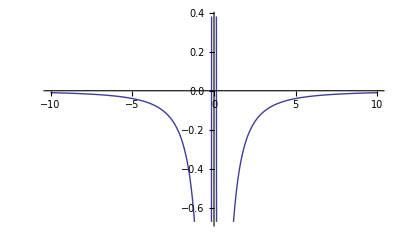

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=0.001,V0=0.00005,S0=0.0001,T=5,λS=0.15,KList={-0.005,0,0.005}},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,ω+ⅈ λS,0][[1,2]],
{ω,-10,10}]]
```

#### Derivée par rapport a V de l' Integrand en fonction de ω

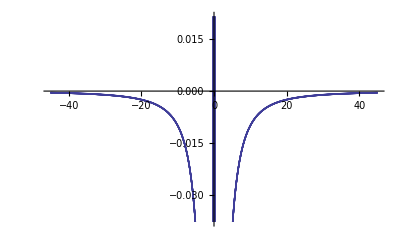

```mathematica
Module[{ρ=-0.000094075283,λ=0.1,L=0.5,ν=0.000148511498,V0=0.000000103958,S0=0.002786743,k=0.005,T=4.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},ω=0.5,λS=0.15},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,ω+ⅈ λS,0][[1]],{ω,-45,45}]]
```

#### Derivée par rapport a V de l' Integrand en fonction de ω

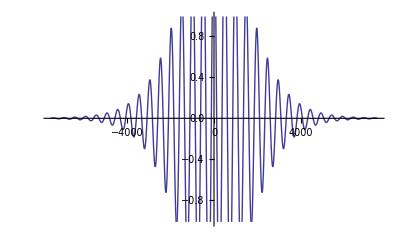

```mathematica
Module[{ρ=-0.000094075283,λ=0.1,L=0.5,ν=0.000148511498,V0=0.000000103958,S0=0.002786743,k=0.005,T=4.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},ω=0.5,λS=0.15},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,ω+ⅈ λS,2][[2,1]],{ω,-7500,7500}]]
```

#### Derivée par rapport a ν de l' Integrand en fonction de ω

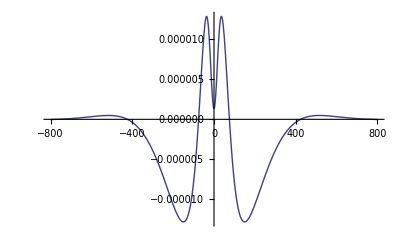

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=0.01,V0=0.00005,S0=0.0001,k=0.005,T=5,KList={-0.005,0,0.005},λS=0.5},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,ω+ⅈ λS,2][[3,1]],{ω,-800,800},PlotRange->All]]
```

#### Derivée par rapport a ρ de l' Integrand en fonction de ω

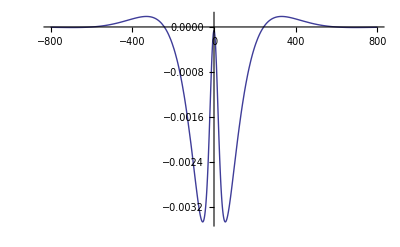

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=0.01,V0=0.00005,S0=0.0001,k=0.005,T=5,KList={-0.005,0,0.005},λS=0.5},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,ω+ⅈ λS,2][[4,1]],{ω,-800,800},PlotRange->All]]
```

#### Pour Fixer les constantes :

prices={6.76752,4.5951,3.533,2.50075,1.91898,1.16435,0.835524,0.558122,0.355561,0.150286,0.0877301,0.0380476,0.0173051,0.00375252}

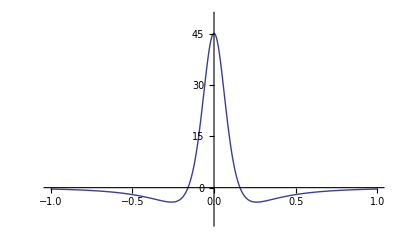
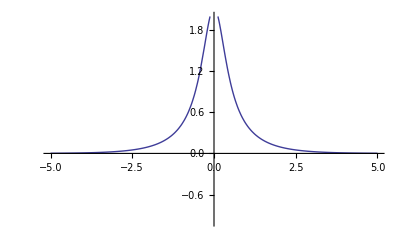
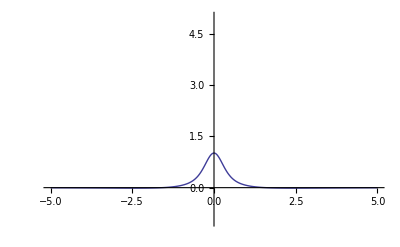
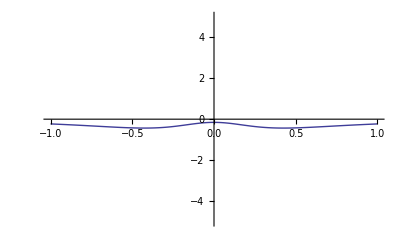
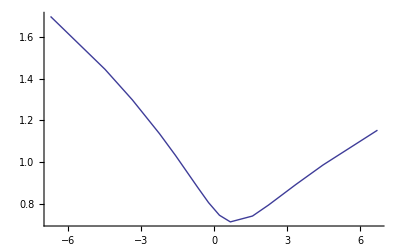

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=1.54,V=1,S0=0.0001,τ=5,nbsteps=20,scale=10,microratio=10,KList,ω=0.5,λS=0.15,prices,ll,homotheticRatio},KList={-3 √τ,-2 √τ,-1.5 √τ,-1 √τ,-0.707 √τ,-0.3 √τ,-0.1 √τ,0.1 √τ,0.3 √τ,0.707 √τ,1 √τ,1.5 √τ,2 √τ,3 √τ};
homotheticRatio=1;
prices=DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio,0][[1]];
Print["prices=",prices];
{Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[1,8]],{ω,-1/homotheticRatio,1/homotheticRatio},PlotRange->{-10,50}],
Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[2,8]],{ω,-5/homotheticRatio,5/homotheticRatio},PlotRange->{-1,2}],
Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[3,8]],{ω,-5/homotheticRatio,5/homotheticRatio},PlotRange->{-1,5}],
Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[4,8]],{ω,-1/homotheticRatio,1/homotheticRatio},PlotRange->{-5,5}],
ll=Map[(NormalImplicitVol[S0,#[[1]],τ,#[[2]]])&,Transpose[{KList,prices}]];
ListPlot[Transpose[{KList,ll}],Joined->True]}]
```

prices={19.1453,12.9882,9.97127,7.03879,5.3906,3.26681,2.34895,1.5737,0.994722,0.39042,0.215312,0.0881445,0.0397121,0.00937873}

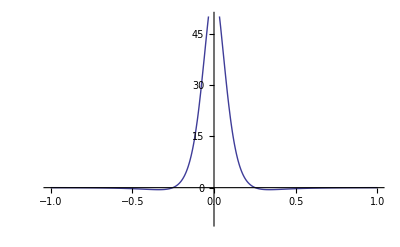
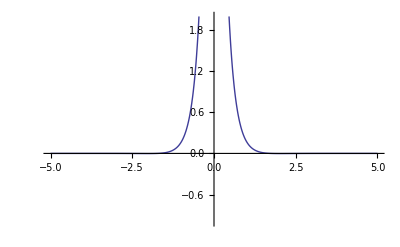
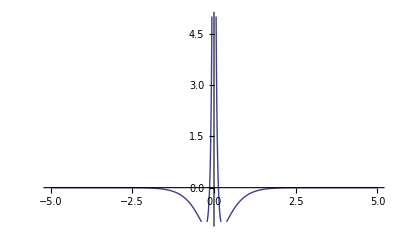
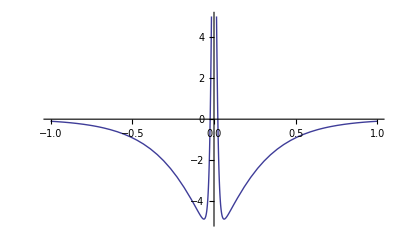
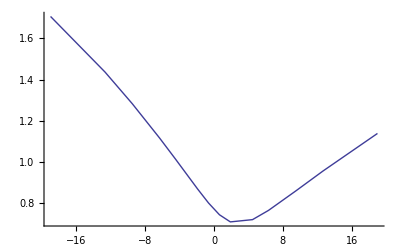

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=1.54,V=1,S0=0.0001,τ=40,nbsteps=20,scale=10,microratio=10,KList,ω=0.5,λS=0.15,prices,ll,homotheticRatio},KList={-3 √τ,-2 √τ,-1.5 √τ,-1 √τ,-0.707 √τ,-0.3 √τ,-0.1 √τ,0.1 √τ,0.3 √τ,0.707 √τ,1 √τ,1.5 √τ,2 √τ,3 √τ};
homotheticRatio=1;
prices=DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio,0][[1]];
Print["prices=",prices];
{Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[1,8]],{ω,-1/homotheticRatio,1/homotheticRatio},PlotRange->{-10,50}],
Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[2,8]],{ω,-5/homotheticRatio,5/homotheticRatio},PlotRange->{-1,2}],
Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[3,8]],{ω,-5/homotheticRatio,5/homotheticRatio},PlotRange->{-1,5}],
Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V,S0,KList,τ,ω+ⅈ λS,2][[4,8]],{ω,-1/homotheticRatio,1/homotheticRatio},PlotRange->{-5,5}],
ll=Map[(NormalImplicitVol[S0,#[[1]],τ,#[[2]]])&,Transpose[{KList,prices}]];
ListPlot[Transpose[{KList,ll}],Joined->True]}]
```

```mathematica
On en deduit Qu'il faut augmenter le microratio avec la maturité pour mieux traiter les derivée par rapport a rho et nu , sans doute par une mumtiplication  par 0.5  τ^(1/4)
```

#### Normale Heston Call avec ses derivées

```mathematica
DerivativeHestonNormalCallAux[ρ_,λ_,LT_,ν_,V_,S0_,k_,T_,nbsteps_,scale_,microratio_]:=Module[{res,λs=NormalHestonOptimalShift[λ,ρ,ν],LegendreCoef0,LegendreCoefn,period0,periodn,ϵ,imax,initialperiod,LegendreCoefn2,ω},
λs=0.15;LegendreCoef0=LegendreCoeffs[nbsteps];LegendreCoefn=LegendreCoeffs[Floor[nbsteps/7]];
period0=scale;periodn=scale/5;ϵ=10^(-8);imax=1000;initialperiod=scale/microratio;
LegendreCoefn2=LegendreCoeffs[nbsteps];
res=Re[MatrixAdaptativeIntegrate[Function[ω,DerivativeNormalHestonCallIntegrand[ρ,λ,LT,ν,V,S0,k,T,ω +λs ⅈ]],LegendreCoef0,LegendreCoefn,
period0,periodn,ϵ,imax,initialperiod,LegendreCoefn2]];
{res[[1]],1/π res[[2]]}]
```

```mathematica
DerivativeHestonNormalCallAux[ρ_,λ_,LT_,ν_,V_,S0_,k_,T_,nbsteps_,scale_,microratio_,flag_]:=Module[{res,λs=NormalHestonOptimalShift[λ,ρ,ν],LegendreCoef0,LegendreCoefn,period0,periodn,ϵ,imax,initialperiod,LegendreCoefn2,ω},
λs=0.15;LegendreCoef0=LegendreCoeffs[nbsteps];LegendreCoefn=LegendreCoeffs[Floor[nbsteps/7]];
period0=scale;periodn=scale/5;ϵ=10^(-8);imax=1000;initialperiod=scale/microratio;
LegendreCoefn2=LegendreCoeffs[nbsteps];
res=Re[MatrixAdaptativeIntegrate[Function[ω,DerivativeNormalHestonCallIntegrand[ρ,λ,LT,ν,V,S0,k,T,ω +λs ⅈ,flag]],LegendreCoef0,LegendreCoefn,
period0,periodn,ϵ,imax,initialperiod,LegendreCoefn2]];
{res[[1]],1/π res[[2]]}]
```

```mathematica
DerivativeHestonNormalCall[ρ_,λ_,LT_,ν1_,V01_,S1_,k1_List,T_,nbsteps_,scale_,microratio_]:=
Module[{optlist,L,ν,V0,F,k},
L=1/√V01;ν=L ν1;V0=1.;F=L S1;k=Table[k1[[i]] L,{i,1,Length[k1]}];
optlist=DerivativeHestonNormalCallAux[ρ,λ,LT,ν,V0,F,k,T,nbsteps,scale,microratio];
{Table[Max[{optlist⟦2,1,i⟧/L,S1-k1⟦i⟧,1.*^-12}],{i,1,Length[optlist⟦2,1⟧]}],
Table[optlist⟦2,2,i⟧ L,{i,1,Length[optlist⟦2,2⟧]}],
Table[optlist⟦2,3,i⟧/L,{i,1,Length[optlist⟦2,3⟧]}],
Table[optlist⟦2,4,i⟧,{i,1,Length[optlist⟦2,4⟧]}]}
]
```

```mathematica
DerivativeHestonNormalCall[ρ_,λ_,LT_,ν1_,V01_,S1_,k1_List,T_,nbsteps_,scale_,microratio_,flag_]:=
Module[{optlist,L,ν,V0,F,k},
L=1/√V01;ν=L ν1;V0=1.;F=L S1;k=Table[k1[[i]] L,{i,1,Length[k1]}];
optlist=DerivativeHestonNormalCallAux[ρ,λ,LT,ν,V0,F,k,T,nbsteps,scale,microratio,flag];
If[flag==0,
{Table[Max[{optlist⟦2,1,i⟧/L,S1-k1⟦i⟧,1.*^-12}],{i,1,Length[optlist⟦2,1⟧]}]},
{Table[Max[{optlist⟦2,1,i⟧/L,S1-k1⟦i⟧,1.*^-12}],{i,1,Length[optlist⟦2,1⟧]}],
Table[optlist⟦2,2,i⟧ L,{i,1,Length[optlist⟦2,2⟧]}],
Table[optlist⟦2,3,i⟧/L,{i,1,Length[optlist⟦2,3⟧]}],
Table[optlist⟦2,4,i⟧,{i,1,Length[optlist⟦2,4⟧]}]}
]]
```

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=0.001,V=0.00005,S0=0.0001,τ=5,KList={-0.005,0,0.005},ω=0.5,λS=0.1,nbsteps=120,scale=10,microratio=75,flag=0},
DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio,flag]]
```

{{0.00923346,0.00634141,0.00407765}}

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=0.001,V=0.00005,S0=0.0001,τ=5,KList={-0.005,0,0.005},ω=0.5,λS=0.1,nbsteps=120,scale=10,microratio=75,flag=2},
DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio,flag]]
```

{{0.00923346,0.00634141,0.00407765},{59.4119,63.2427,60.8397},{-0.000127682,-4.33049×10^-6,0.000128479},{0.0344685,-0.0344987,-0.0975885}}

```mathematica
Module[{ρ=-0.51,λ=0.1,L=1,ν=0.2,V=0.00005,S0=0.0001,τ=5,KList={-0.005,0,0.005},ω=0.5,λS=0.15,δV,δν,δρ,nbsteps=120,scale=10,microratio=75},
δV=0.01 δρ;δν=0.01 ν;δρ=0.0001;
{DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio],
{DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio][[1]],(DerivativeHestonNormalCall[ρ,λ,L,ν,V+δV,S0,KList,τ,nbsteps,scale,microratio][[1]]-DerivativeHestonNormalCall[ρ,λ,L,ν,V-δV,S0,KList,τ,nbsteps,scale,microratio][[1]])/(2δV),
(DerivativeHestonNormalCall[ρ,λ,L,ν+δν,V,S0,KList,τ,nbsteps,scale,microratio][[1]]-DerivativeHestonNormalCall[ρ,λ,L,ν-δν,V,S0,KList,τ,nbsteps,scale,microratio][[1]])/(2δν),
(DerivativeHestonNormalCall[ρ+δρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio][[1]]-DerivativeHestonNormalCall[ρ-δρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio][[1]])/(2δρ)}
}
]
```

{{{0.00543347,0.000726774,0.000177958},{6.58686,11.0089,3.63169},{-0.000194148,0.0000740601,0.000171297},{-0.00126997,-0.002413,-0.000609176}},{{0.00543347,0.000726774,0.000177958},{6.97969,11.363,3.9493},{-0.00127006,-0.00241317,-0.000609221},{-0.000194148,0.0000740601,0.000171297}}}

## Normal 1 Facteur : Calibrateur

```mathematica
NormalHestonSmileCalibrate[KList_,PriceList_,WeightList_,S0_,λ_,LT_,T_,nbsteps_,scale_,microratio_]:=Module[{func,gradfunc,V0,rho,nu},
func=Function[{V,ρ,ν},Module[{ff=DerivativeHestonNormalCall[ρ,λ,LT,ν,V,S0,KList,T,nbsteps,scale,microratio,0]},
Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])^2,{i,1,Length[KList]}]]];
gradfunc=Function[{V,ρ,ν},Module[{ff=DerivativeHestonNormalCall[ρ,λ,LT,ν,V,S0,KList,T,nbsteps,scale,microratio]},
{Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[2,i]],{i,1,Length[KList]}],
Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[3,i]],{i,1,Length[KList]}],
Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[4,i]],{i,1,Length[KList]}]
}]];
FindMinimum[func[V0,rho,nu],{{V0,0.00003,0.000001,0.001},{nu,0.001,0.000001,0.01},{rho,0,-0.9,0.9}},
MaxIterations->200,AccuracyGoal->8,Method->"LevenbergMarquardt",
Gradient->gradfunc[V0,rho,nu]] 
]
```

```mathematica
Module[{ρ=0.1,λ=0.1,L=1,ν=0.008,V=7 10^(-6),S0=0.0001,τ=5,nbsteps=120,scale=10,microratio=75,KList={-0.02,-0.0175,-0.015,-0.0125,-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.0125,0.015,0.0175,0.02}},
DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,τ,nbsteps,scale,microratio]]//MatrixForm
```

(0.0201836 | 0.0177071 | 0.015238 | 0.0127794 | 0.0103367 | 0.00791957 | 0.00554948 | 0.0032907 | 0.00147827 | 0.000792118 | 0.000539315 | 0.000397885 | 0.000304737 | 0.00023836 | 0.000188891 | 0.000150981 | 0.000121391
12.8343 | 16.3626 | 20.9937 | 27.1867 | 35.7036 | 47.9459 | 66.902 | 100.366 | 150.08 | 110.074 | 77.5963 | 57.9676 | 44.7326 | 35.1924 | 28.0298 | 22.5095 | 18.1796
-0.000171494 | -0.000201284 | -0.000235397 | -0.000274152 | -0.00031757 | -0.000364574 | -0.000409382 | -0.00041706 | -0.0000783304 | 0.000310948 | 0.000349262 | 0.000332053 | 0.000302881 | 0.000271499 | 0.000240991 | 0.000212485 | 0.000186392
0.00856074 | 0.00830545 | 0.00734027 | 0.00525604 | 0.00137368 | -0.00555176 | -0.0181749 | -0.0434669 | -0.084066 | -0.0501253 | -0.0243968 | -0.0102618 | -0.00181273 | 0.00340834 | 0.00660924 | 0.00847369 | 0.00942911)

```mathematica
Timing[Module[{ρ=-0.51,λ=0.1,L=1,ν=0.002,V=0.00005,S0=0.0001,T=5,nbsteps=120,scale=10,microratio=75,KList={-0.005,-0.0025,0,0.0025,0.005},PriceList={0.00925563132870,0.007697476807935,0.00629203396078,0.00504696425226,0.00396598409559},WeightList={1,1,1,1,1}},
NormalHestonSmileCalibrate[KList,PriceList,WeightList,S0,λ,L,T,nbsteps,scale,microratio]
]]
```

{48.078,{2.22142×10^-17,{V0$1977930→0.0000500752,nu$1977930→0.00202212,rho$1977930→-0.504624}}}

```mathematica
Timing[Module[{ρ=-0.51,λ=0.1,L=1,ν=0.002,V=0.00005,S0=0.0001,T=5,nbsteps=12,scale=5,microratio=20,KList={-0.005,-0.0025,0,0.0025,0.005},PriceList={0.00925563132870,0.007697476807935,0.00629203396078,0.00504696425226,0.00396598409559},WeightList={1,1,1,1,1}},
NormalHestonSmileCalibrate[KList,PriceList,WeightList,S0,λ,L,T,nbsteps,scale,microratio]
]]
```

{1.,{5.40653×10^-17,{V0$2116103→0.0000501197,nu$2116103→0.00203505,rho$2116103→-0.501523}}}

```mathematica
Timing[Module[{ρ=-0.2,λ=0.1,L=1,ν=0.01,V=0.00002,S0=0.0001,T=5,nbsteps=10,scale=8,microratio=20,
PriceList,WeightList,KList={-0.005,-0.0025,0,0.0025,0.005}},
WeightList=Table[1,{i,1,Length[KList]}];
PriceList=DerivativeHestonNormalCall[ρ,λ,L,ν,V,S0,KList,T,nbsteps,scale,microratio,0][[1]];
NormalHestonSmileCalibrate[KList,PriceList,WeightList,S0,λ,L,T,nbsteps,scale,microratio]
]]
```

{0.719,{5.1904×10^-15,{V0$11034→0.0000199993,nu$11034→0.0099995,rho$11034→-0.199886}}}

## Normal 1 Facteur : Comparaison de 3 mappers

### Mapper x=(1/y)-1

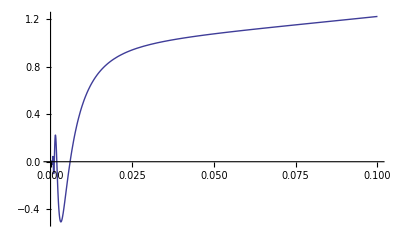

```mathematica
Module[{ρ=0.5,λ=0.1,L=0.5,ν=0.005171729,V0=1.17492*10^(-05),S0=0.002786743,k=0.005,T=3.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},λS=0.15},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,(y-1)/y,λS][[1,2]](-1/(y)^2),{y,0,0.1},PlotRange->All]]
```

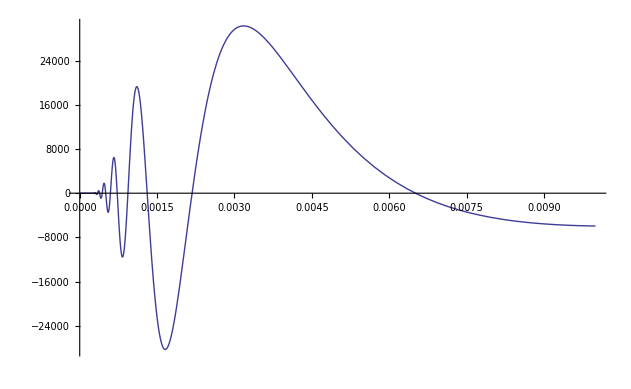

```mathematica
Module[{ρ=-0.000094075283,λ=0.1,L=0.5,ν=0.005171729,V0=1.17492*10^(-05),S0=0.002786743,k=0.005,T=3.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},λS=0.15},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,(y-1)/y,λS][[2,2]](-1/(y)^2),{y,0,0.01},PlotRange->All]]
```

### Mapper x=-log[y]/C

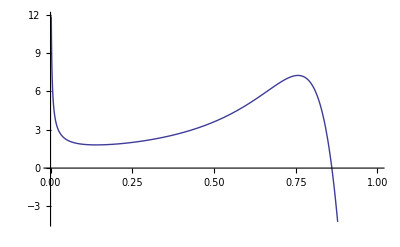

```mathematica
Module[{ρ=0.5,λ=0.1,L=0.5,ν=0.005171729,V0=1.17492*10^(-05),S0=0.002786743,k=0.005,T=3.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},λS=0.15,CLog=1.},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,-Log[y]/CLog,λS][[1,2]](-1/(y CLog)),{y,0,1}]]
```

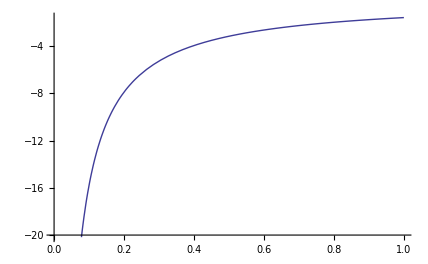

```mathematica
Module[{ρ=-0.000094075283,λ=0.1,L=0.5,ν=0.005171729,V0=1.17492*10^(-05),S0=0.002786743,k=0.005,T=3.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},λS=0.15,CLog=1},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,-Log[y]/CLog,λS][[2,2]](-1/(y CLog)),{y,0,1}]]
```

### Mapper x=Tan[y π/2]

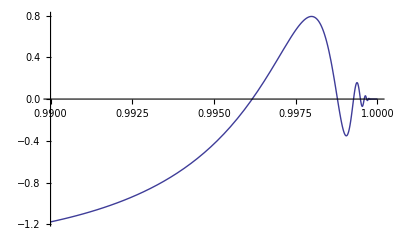

```mathematica
Module[{ρ=0.5,λ=0.1,L=0.5,ν=0.005171729,V0=1.17492*10^(-05),S0=0.002786743,k=0.005,T=3.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},λS=0.15,CLog=1.},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,Tan[y π/2],λS][[1,2]] 1/2 π Cos[(π y)/2]^-2,{y,0.99,1},PlotRange->All]]
```

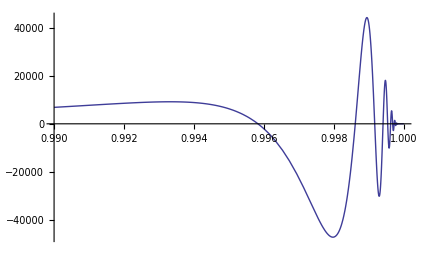

```mathematica
Module[{ρ=-0.000094075283,λ=0.1,L=0.5,ν=0.005171729,V0=1.17492*10^(-05),S0=0.002786743,k=0.005,T=3.41369863,KList={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},λS=0.15,CLog=1},Plot[DerivativeNormalHestonCallIntegrand[ρ,λ,L,ν,V0,S0,KList,T,Tan[y π/2],λS][[2,2]] 1/2 π Cos[(π y)/2]^-2,{y,0.99,1}]]
```

Conclusion 1 : Le mapping ne change pas le fait que si on a une integrale oscillante, les oscillation resteront et auront toujours besoin d' etre integrees.  De ce point de vue il est plus pratique d' avoir ces oscillation en 0 ainsi des une transformation rapidement calculable. de ce point de vue, le premier mapping est le meilleur.

Conclusion2 : Quand on veut integrer les oscillation, il vaut mieux les deplier et avoir un algorithme iteratif, car ces ocillation semeble avoir une frequnece constante. dans ce cas lemapping est inutile.

## Normal 1,2 et 3 Facteurs de vol : Integrands

#### Cas scalaire pour 1, 2 et 3 facteurs

```mathematica
NormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  S0) NormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ω,T]NormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
NormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,S0_,K_List,T_,ω_]:=Re[ⅇ^(-ⅈ ω  S0) NormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ω,T]Table[NormalCallPayOffFourierTransform[K[[i]],ω],{i,1,Length[K]}]]
```

```mathematica
NormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  S0) NormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ω,T]NormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
NormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  S0) NormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ω,T]NormalCallPayOffFourierTransform[K,α,a,ω]]
```

#### Cas vectoriel pour 1, 2 et 3 facteurs

```mathematica
NormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  S0) NormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ω,T]Table[NormalCallPayOffFourierTransform[K[[i]],α,a,ω],{i,1,Length[K]}]]
```

```mathematica
NormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  S0) NormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ω,T]Table[NormalCallPayOffFourierTransform[K[[i]],α,a,ω],{i,1,Length[K]}]]
```

```mathematica
NormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  S0) NormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ω,T]Table[NormalCallPayOffFourierTransform[K[[i]],α,a,ω],{i,1,Length[K]}]]
```

## Phenomene de resonance avec le shift complexe

```mathematica
Module[{ρ=0.300322,λv=0.387,θv=1,κ=0.8944,V=1,S0=0.53,T=11.7371,k=-4,ω},
NormalHestonFondamentalTransform[ρ,λv,θv,κ,V,0+0.5 ⅈ,T]]
```

η=0.252696

ψm+ψp ⅇ^(-ζ  τ)=0.00447286-0.00302389 ⅈ

A=6.19292-2.14841×10^-15 ⅈ B=76.7205-1.63043×10^-13 ⅈ

1.02059×10^36-1.68592×10^23 ⅈ

```mathematica
Module[{ρ=0.300322,λv=0.387,θv=1,κ=0.8944,V=1,S0=0.53,T=11.7371,k=-4,ω},
NormalHestonFondamentalTransform[ρ,λv,θv,κ,V,0+0.4 ⅈ,T]]
```

5.40868+1.88589×10^-17 ⅈ

```mathematica
NormalHestonShiftDiscriminator[ρ_,λv_,θv_,κ_,V_,τ_,λ_]:=(λv-ρ κ λ)+√((λv-ρ κ λ)^2-κ^2 λ^2)+(-(λv-ρ κ λ)+√((λv-ρ κ λ)^2-κ^2 λ^2))ⅇ^(-√((λv-ρ κ λ)^2-κ^2 λ^2) τ)
```

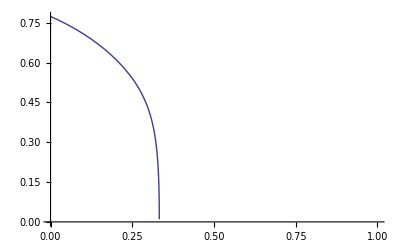

```mathematica
Module[{ρ=0.300322,λv=0.387,θv=1,κ=0.8944,V=1,S0=0.53,T=10.7371,k=-4,,λ},
Plot[NormalHestonShiftDiscriminator[ρ,λv,θv,κ,V,T,λ],{λ,0,1}]]
```

λv/κ=0.2

NormalHestonOptimalShift[λv,ρ,κ]=0.0995

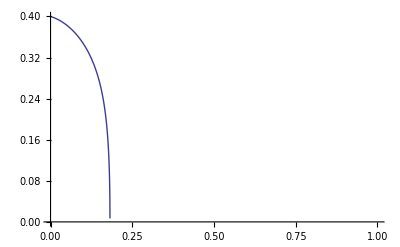

```mathematica
Module[{ρ=0.1,λv,θv=1,κ=1,V=1,S0=0.53,T=11.7371,k=-4,λ},κ=1.;λv=0.2;
Print["λv/κ=",λv/κ];
Print["NormalHestonOptimalShift[λv,ρ,κ]=",NormalHestonOptimalShift[λv,ρ,κ]];
Plot[NormalHestonShiftDiscriminator[ρ,λv,θv,κ,V,T,λ],{λ,0,1}]]
```

```mathematica
donc le shift doit etre dependant de la vol de vol et du λv, en fait de leur ratio ,
si ρ est <0, pas de probleme, si ρ>0, on doit raprocher le shift de 0 suivant λv/κ
```

```mathematica
experimentalement , un shift egal a Max[0.5, λv/κ (1-ρ^2/2)/2] parait optimal
```

```mathematica
NormalHestonOptimalShift[λv_,ρ_,κ_]:=Min[0.5, (λv(1-ρ^2/2))/(2κ)]
```

## Shift et parametres d' integration

le shift ici sera pris a 0.5. A ce shift sera adapté les constante de la procedure d' integration.

Exemple d' integrand pour des shift differents

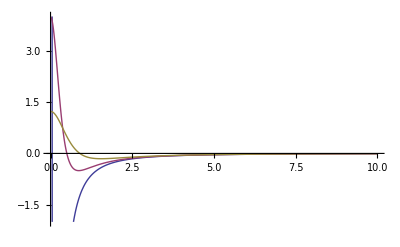
{0.219,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=0.01,S0=0,λ1=0.05,λ2=0.5,λ3=0.9,T=0.5,k=0.01,ω},
Plot[{NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ1 ⅈ],
NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ2 ⅈ],
NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ3 ⅈ]},{ω,0,10},PlotRange->{-2,4}]
]]
```

## Normal 1,2 et 3 Facteurs de vol : Implementations

on voit que le shift determine a lui tout seul les parametre

### Implementation mathematica de reference

```mathematica
HestonNormalCallN[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=1/π Re[Module[{λ=0.5,ω},
NIntegrate[NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
HestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=1/π Re[Module[{λ=0.5,ω},
NIntegrate[NormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
HestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=1/π Re[Module[{λ=0.5,ω},
NIntegrate[NormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

### Implementation Operationnelle

```mathematica
Print["ω=",ω," integrand=",NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ ⅈ]];
```

```mathematica
HestonNormalCallAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=1/π Re[Module[{λ=NormalHestonOptimalShift[λv,ρ,κ],ω},
AdaptativeIntegrate[Function[ω,NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[8],
20λ,3λ,10^(-10),1000,2λ,LegendreCoeffs[20]][[2]]]]
```

```mathematica
HestonNormalCallAux[ρ_,λv_,θv_,κ_,V_,S0_,k_List,T_]:=1/π Re[Module[{λ=NormalHestonOptimalShift[λv,ρ,κ],ω},
AdaptativeIntegrate[Function[ω,NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[8],
20λ,3λ,10^(-10),1000,2λ,LegendreCoeffs[20]][[2]]]]
```

```mathematica
HestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,NormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
HestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,NormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
(*version Vecteur *)
```

### Implementation Normalisée

```mathematica
HestonNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{θv1,κ1,V1,S01,k1,L},
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L k;
HestonNormalCallAux[ρ,λv,θv1,κ1,V1,S01,k1,T]/L
]
```

```mathematica
HestonNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_List,T_]:=Module[{θv1,κ1,V1,S01,k1,L},
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L k;
HestonNormalCallAux[ρ,λv,θv1,κ1,V1,S01,k1,T]/L
]
```

```mathematica
HestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,θv2a,κ2a,V2a,S0a,ka,L},
L=√(1./(V1+V2));θv1a=L^2 θv1;θv2a=L^2 θv2;κ1a=L κ1;κ2a=L κ2;V1a=L^2 V1;V2a=L^2 V2;S0a=L S0;ka=L k;
HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,S0,ka,T]/L
]
```

```mathematica
HestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,θv2a,κ2a,V2a,θv3a,κ3a,V3a,S0a,ka,L},
L=√(1./(V1+V2+V3));θv1a=L^2 θv1;θv2a=L^2 θv2;θv3a=L^2 θv3;κ1a=L κ1;κ2a=L κ2;κ3a=L κ3;V1a=L^2 V1;V2a=L^2 V2;V3a=L^2 V3;S0a=L S0;ka=L k;
HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,ρ3,λv3,θv3a,κ3a,V3a,S0,ka,T]/L
]
```

### Implementation Normalisée qui permet de tracer la normalisation

```mathematica
HestonNormalCallTrace[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{θva,κa,Va,S0a,ka,L},
L=√(1./V);θva=L^2 θv;κa=L κ;Va=L^2 V;S0a=L S0;ka=L k;Print["L=",L," κa=",κa," S0a=",S0a," ka=",ka];
HestonNormalCallAux[ρ,λv,θva,κa,Va,S0a,ka,T]/L
]
```

```mathematica
HestonNormalCallTrace[ρ_,λv_,θv_,κ_,V_,S0_,k_List,T_]:=Module[{θva,κa,Va,S0a,ka,L},
L=√(1./V);θva=L^2 θv;κa=L κ;Va=L^2 V;S0a=L S0;ka=L k;Print["L=",L," κa=",κa," S0a=",S0a," ka=",ka];
(HestonNormalCallAux[ρ,λv,θva,κa,Va,S0a,#,T]/L)& /@ ka
]
```

```mathematica
HestonNormalCallTrace[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,S0a,ka,θv2a,κ2a,V2a,L},
L=√(1./(V1+V2));θv1a=L^2 θv1;θv2a=L^2 θv2;κ1a=L κ1;κ2a=L κ2;V1a=L^2 V1;V2a=L^2 V2;S0a=L S0;ka=L k;Print["L=",L," V1a=",V1a," κa1=",κ1a," V2a=",V2a," κa2=",κ2a," S0a=",S0a," ka=",ka];
HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,S0a,ka,T]/L
]
```

```mathematica
HestonNormalCallTrace[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,S0a,ka,θv2a,κ2a,V2a,L},
L=√(1./(V1+V2));θv1a=L^2 θv1;θv2a=L^2 θv2;κ1a=L κ1;κ2a=L κ2;V1a=L^2 V1;V2a=L^2 V2;S0a=L S0;ka=L k;Print["L=",L," V1a=",V1a," κa1=",κ1a," V2a=",V2a," κa2=",κ2a," S0a=",S0a," ka=",ka];
(HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,S0a,#,T]/L)& /@ ka
]
```

```mathematica
HestonNormalCallTrace[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,θv3a,κ3a,V3a,S0a,ka,θv2a,κ2a,V2a,L},
L=√(1./(V1+V2+V3));θv1a=L^2 θv1;θv2a=L^2 θv2;θv3a=L^2 θv3;κ1a=L κ1;κ2a=L κ2;κ3a=L κ3;V1a=L^2 V1;V2a=L^2 V2;V3a=L^2 V3;S0a=L S0;ka=L k;Print["L=",L," V1a=",V1a," κa1=",κ1a," V2a=",V2a," κa2=",κ2a," V3a=",V3a," κa3=",κ3a," S0a=",S0a," ka=",ka];
HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,S0a,ka,T]/L
]
```

```mathematica
HestonNormalCallTrace[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,θv3a,κ3a,V3a,S0a,ka,θv2a,κ2a,V2a,L},
L=√(1./(V1+V2+V3));θv1a=L^2 θv1;θv2a=L^2 θv2;θv3a=L^2 θv3;κ1a=L κ1;κ2a=L κ2;κ3a=L κ3;V1a=L^2 V1;V2a=L^2 V2;V3a=L^2 V3;S0a=L S0;ka=L k;Print["L=",L," V1a=",V1a," κa1=",κ1a," V2a=",V2a," κa2=",κ2a," V3a=",V3a," κa3=",κ3a," S0a=",S0a," ka=",ka];
(HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,S0a,#,T]/L)& /@ ka
]
```

## Normal : Implementation traversant la barriere de Gindinkin

```mathematica
ThInterpolator[x1_,y1_,x2_,y2_,x_]:=Module[{a},
a=ArcTanh[1-y2/y1]/(x2-x1);
y1(1-Tanh[a(x-y1)])]
```

```mathematica
LinInterpolator[x1_,y1_,x2_,y2_,x_]:=Module[{a},
a=(y2-y1)/(x2-x1);
y2+a(x-x2)]
```

```mathematica
QuadInterpolator[x1_,y1_,x2_,y2_,x3_,y3_,x_]:=Module[{a,b},
a=-(x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3)/((x1-x2) (x1-x3) (-x2+x3));
b=-(-2 x1 x2 y1+x2^2 y1+2 x1 x3 y1-x3^2 y1+x1^2 y2-2 x1 x3 y2+x3^2 y2-x1^2 y3+2 x1 x2 y3-x2^2 y3)/((x2-x3) (x1^2-x1 x2-x1 x3+x2 x3));
a(x-x1)^2+b(x-x1)+y1]
```

```mathematica
PowerInterpolator[x1_,y1_,x2_,y2_,x3_,y3_,x_]:=Module[{a,b},
b=Log[(y3-y1)/(y2-y1)]/Log[(x3-x1)/(x2-x1)];
a=(y3-y1)/(x3-x1)^b;
y1+a (x-x1)^b
]
```

```mathematica
(* interpolateur qui interpole une variable >0 par exemple la vol implicite en fonction de la vol de vol *)
```

```mathematica
SmartInterpolator[x1_,y1_,x2_,y2_,x3_,y3_,x_]:=Module[{a1,a2},
a1=(y2-y1)/(x2-x1);a2=(y3-y2)/(x3-x2);
Which[
a1>0&&a2<0,LinInterpolator[x1,y1,x3,y3,x],
a1>0&&a2≥0,PowerInterpolator[x1,y1,x2,y2,x3,y3,x],
a1<0&&a2>0,LinInterpolator[x1,y1,x3,y3,x],
a1<0&&a2≤0&&a2>a1, PowerInterpolator[x1,y1,x2,y2,x3,y3,x],
a1<0&&a2≤0&&a2≤a1,ThInterpolator[x1,y1,x3,y3,x]
]]
```

```mathematica
Solve[{y3==a(x3-x1)^2+b(x3-x1)+y1,y2==a(x2-x1)^2+b(x2-x1)+y1},{a,b}]
```

{{a→-(x2 y1-x3 y1-x1 y2+x3 y2+x1 y3-x2 y3)/((x1-x2) (x1-x3) (-x2+x3)),b→-(-2 x1 x2 y1+x2^2 y1+2 x1 x3 y1-x3^2 y1+x1^2 y2-2 x1 x3 y2+x3^2 y2-x1^2 y3+2 x1 x2 y3-x2^2 y3)/((x2-x3) (x1^2-x1 x2-x1 x3+x2 x3))}}

```mathematica
TransHestonNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_,LimitGindinkin_]:=Module[{θv1,κ1,V1,S01,k1,L,κ1Limit,κ1test1,κ1test2,vol1,vol2,vol},
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L k;
κ1Limit=LimitGindinkin √(2 λv θv1);
If[κ1<0.9 κ1Limit,
HestonNormalCallAux[ρ,λv,θv1,κ1,V1,S01,k1,T]/L,
κ1test1=0.8 κ1Limit;
κ1test2=0.9 κ1Limit;
vol1=NormalImplicitVol[S01,k1,T,HestonNormalCallAux[ρ,λv,θv1,κ1test1,V1,S01,k1,T]];
vol2=NormalImplicitVol[S01,k1,T,HestonNormalCallAux[ρ,λv,θv1,κ1test2,V1,S01,k1,T]];
If[vol2<vol1,
vol=ThInterpolator[κ1test1,vol1,κ1test2,vol2,κ1],
vol=LinInterpolator[κ1test1,vol1,κ1test2,vol2,κ1]
];
NormalCall[S01,vol,k1,T]/L
]
]
```

```mathematica
TransHestonNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_,LimitGindinkin_,order_]:=Module[{θv1,κ1,V1,S01,k1,L,κ1Limit,κ1test1,κ1test2,κ1test3,vol1,vol2,vol3,vol},
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L k;
κ1Limit=LimitGindinkin √(2 λv θv1);
Print["LimitGindinkin=",κ1Limit," κ1=",κ1];
If[κ1<0.9 κ1Limit,
HestonNormalCallAux[ρ,λv,θv1,κ1,V1,S01,k1,T]/L,
If[order==1,
κ1test1=0.8 κ1Limit;
κ1test2=0.9 κ1Limit;
vol1=NormalImplicitVol[S01,k1,T,HestonNormalCallAux[ρ,λv,θv1,κ1test1,V1,S01,k1,T]];
vol2=NormalImplicitVol[S01,k1,T,HestonNormalCallAux[ρ,λv,θv1,κ1test2,V1,S01,k1,T]];
If[vol2<vol1,
vol=ThInterpolator[κ1test1,vol1,κ1test2,vol2,κ1],
vol=LinInterpolator[κ1test1,vol1,κ1test2,vol2,κ1]
]
];
If[order==2,
κ1test1=0.8 κ1Limit;
κ1test2=0.85 κ1Limit;
κ1test3=0.9 κ1Limit;
vol1=NormalImplicitVol[S01,k1,T,HestonNormalCallAux[ρ,λv,θv1,κ1test1,V1,S01,k1,T]];
vol2=NormalImplicitVol[S01,k1,T,HestonNormalCallAux[ρ,λv,θv1,κ1test2,V1,S01,k1,T]];
vol3=NormalImplicitVol[S01,k1,T,HestonNormalCallAux[ρ,λv,θv1,κ1test3,V1,S01,k1,T]];
Print["κ1test1=",κ1test1," κ1test2=",κ1test2," κ1test3=",κ1test3," vol1=",vol1," vol2=",vol2," vol3=",vol3];
vol=SmartInterpolator[κ1test1,vol1,κ1test2,vol2,κ1test3,vol3,κ1];
Print["vol=",vol]
];
NormalCall[S01,vol,k1,T]/L
]]
```

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=3,V=1,S0=-0.1,T=5},TransHestonNormalCall[ρ,λv,θv,κ,V,S0,1,T,8]]]
```

{0.313,0.0747721}

```mathematica
TransHestonNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_List,T_,LimitGindinkin_]:=Module[{θv1,κ1,V1,S01,k1,L,κ1Limit,κ1test1,κ1test2,vol1,vol2,vol},
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L k;
κ1Limit=LimitGindinkin √(2 λv θv1);
Table[
If[κ1<0.9 κ1Limit,
HestonNormalCallAux[ρ,λv,θv1,κ1,V1,S01,k1[[i]],T]/L,
κ1test1=0.8 κ1Limit;
κ1test2=0.9 κ1Limit;
vol1=NormalImplicitVol[S01,k1[[i]],T,HestonNormalCallAux[ρ,λv,θv1,κ1test1,V1,S01,k1[[i]],T]];
vol2=NormalImplicitVol[S01,k1[[i]],T,HestonNormalCallAux[ρ,λv,θv1,κ1test2,V1,S01,k1[[i]],T]];
If[vol2<vol1,
vol=ThInterpolator[κ1test1,vol1,κ1test2,vol2,κ1],
vol=LinInterpolator[κ1test1,vol1,κ1test2,vol2,κ1]
];
NormalCall[S01,vol,k1[[i]],T]/L
],{i,1,Length[k]}]
]
```

κ gindinkin=0.632456

FindRoot::reged: The point {0.0001} is at the edge of the search region {0.0001, 15.} in coordinate 1 and the computed search direction points outside the region.

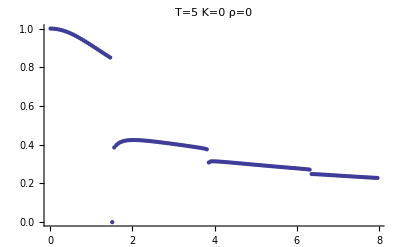

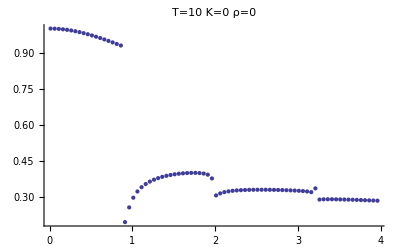

FindRoot::reged: The point {0.0001} is at the edge of the search region {0.0001, 15.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot :: "reged" will be suppressed during this calculation.

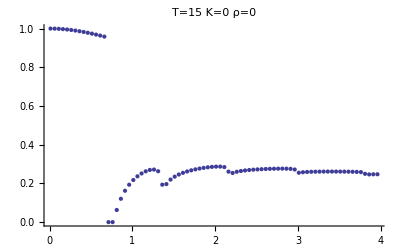

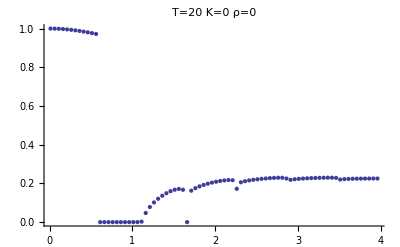

{77.719,Null}

```mathematica
Timing[Module[{ρ=0,λv=0.2,θv=1,κ,V=1,S0=0,k=0,T1=5,T2=10,T3=15,T4=20},
Print["κ gindinkin=",√(2λv θv)];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T1,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T1]]},{κ,0.01,8,0.05}],PlotLabel->"T="<>ToString[T1]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T2,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T2]]},{κ,0.01,4,0.05}],PlotLabel->"T="<>ToString[T2]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T3,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T3]]},{κ,0.01,4,0.05}],PlotLabel->"T="<>ToString[T3]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T4,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T4]]},{κ,0.01,4,0.05}],PlotLabel->"T="<>ToString[T4]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
]]
```

κ gindinkin=0.632456

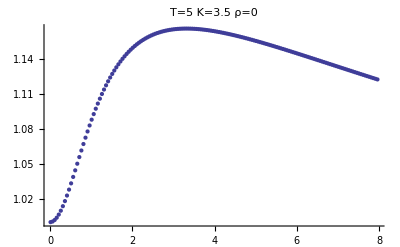

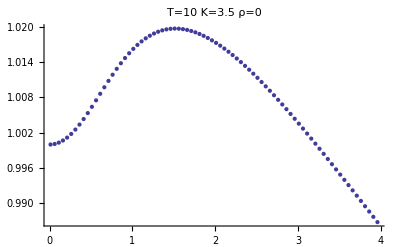

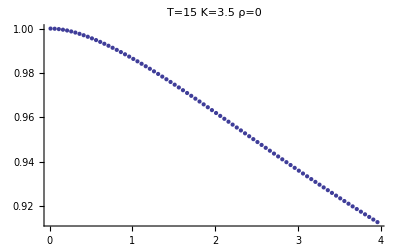

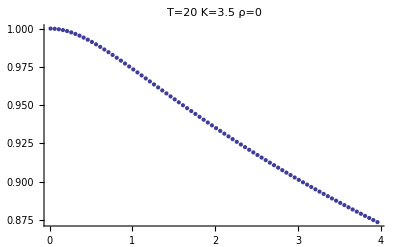

{166.094,Null}

```mathematica
Timing[Module[{ρ=0,λv=0.2,θv=1,κ,V=1,S0=0,k=3.5,T1=5,T2=10,T3=15,T4=20},
Print["κ gindinkin=",√(2λv θv)];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T1,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T1]]},{κ,0.01,8,0.05}],PlotLabel->"T="<>ToString[T1]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T2,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T2]]},{κ,0.01,4,0.05}],PlotLabel->"T="<>ToString[T2]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T3,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T3]]},{κ,0.01,4,0.05}],PlotLabel->"T="<>ToString[T3]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
Print[ListPlot[
Table[{κ,NormalImplicitVol[S0,k,T4,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T4]]},{κ,0.01,4,0.05}],PlotLabel->"T="<>ToString[T4]<>" K="<>ToString[k]<>" ρ="<>ToString[ρ],PlotRange->All]];
]]
```

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=2,V=1,S0=0.1,T=5},TransHestonNormalCall[ρ,λv,θv,κ,V,S0,1,T,5]]]
```

{0.36,0.0901133}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=2,V=1,S0=0.1,k=0.1,T=5,LimitGindinkin=10},{HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T],TransHestonNormalCall[ρ,λv,θv,κ,V,S0,{k},T,LimitGindinkin]}]]
```

{9.094,{0.653306,0.653306,0.227783,{0.653306}}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=2,V=1,S0=0.1,k=0.1,T=5,LimitGindinkin=10},{HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T],TransHestonNormalCall[ρ,λv,θv,κ,V,S0,{k},T,LimitGindinkin]}]]
```

{6.781,{0.653306,0.653306,0.227783,{0.653306}}}

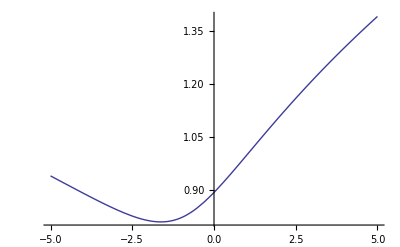
{48.39,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=1,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T]]},{k,-5,5}]]]
```

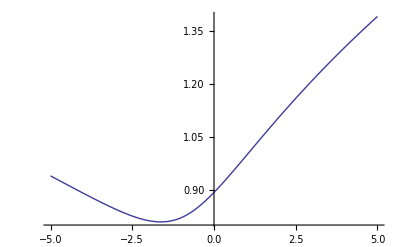
{40.984,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=1,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T]]},{k,-5,5}]]]
```

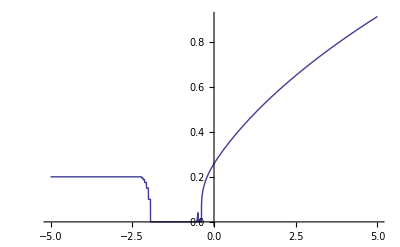
{76.469,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=3,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T]]},{k,-5,5}]]]
```

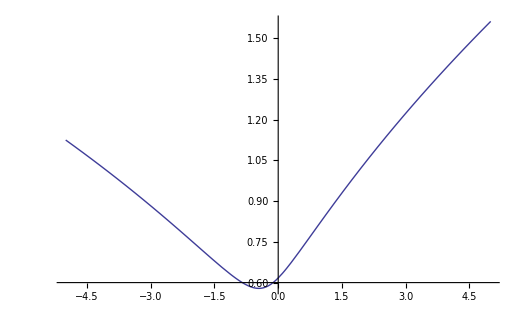
{153.64,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=3,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T]]},{k,-5,5}]]]
```

```mathematica
(*     Prolongation lineaire  des prix options : non effectif     *)
```

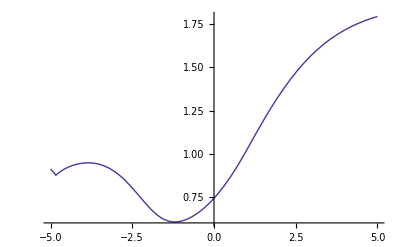
{89.562,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=3,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T]]},{k,-5,5}]]]
```

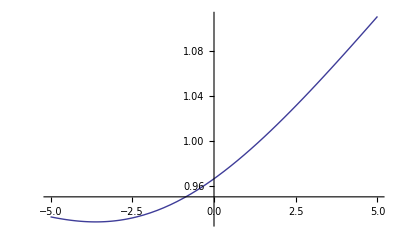
{4.187,-Graphics-}

```mathematica
Timing[Module[{ρ=0.300322,λv=0.4,θv=1,κ=0.8944,V=1,S0=0,T=11.7371,strikes,prices,inter},
strikes=Table[i,{i,-5,5,0.25}];
prices=(HestonNormalCallAux[ρ,λv,θv,κ,V,S0,#,T])& /@ strikes;
inter=Interpolation[Table[{strikes[[i]],NormalImplicitVol[S0,strikes[[i]],T,prices[[i]]]},{i,1,Length[strikes]}]];
Plot[{inter[k]},{k,-5,5},
PlotLegend->{"L=1","L=2","L=2.5","L=3"},LegendPosition->{1,0},PlotRange->All]]]
```

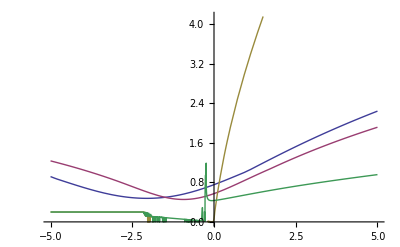
{514.593,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=3,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,1]],NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,2]],
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,2.5]],NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,3]]},{k,-5,5},
PlotLegend->{"L=1","L=2","L=2.5","L=3"},LegendPosition->{1,0}]]]
```

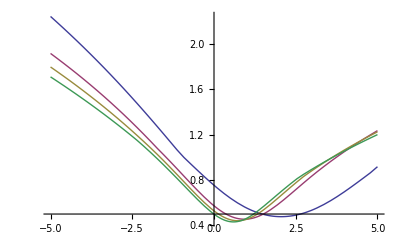
{256.5,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=1,κ=3,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,1]],NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,2]],
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,2.5]],NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,3]]},{k,-5,5},
PlotLegend->{"L=1","L=2","L=2.5","L=3"},LegendPosition->{1,0}]]]
```

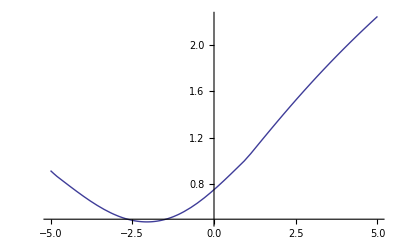
{53.937,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=3,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,2]]},{k,-5,5}]]]
```

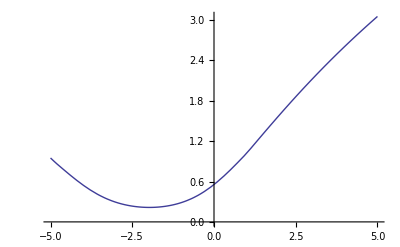
{64.594,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=5,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T]]},{k,-5,5}]]]
```

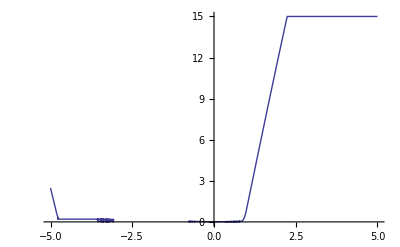
{181.172,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=1,κ=100,V=1,S0=0,T=5},Plot[{
NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T]]},{k,-5,5}]]]
```

```mathematica
TransHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,θv2a,κ2a,V2a,S0a,ka,L},
L=√(1./(V1+V2));θv1a=L^2 θv1;θv2a=L^2 θv2;κ1a=L κ1;κ2a=L κ2;V1a=L^2 V1;V2a=L^2 V2;S0a=L S0;ka=L k;
HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,S0,ka,T]/L
]
```

```mathematica
TransHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_List,T_]:=Module[{θv1a,κ1a,V1a,θv2a,κ2a,V2a,S0a,ka,L},
L=√(1./(V1+V2));θv1a=L^2 θv1;θv2a=L^2 θv2;κ1a=L κ1;κ2a=L κ2;V1a=L^2 V1;V2a=L^2 V2;S0a=L S0;ka=L k;
(HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,S0,#,T]/L)& /@ ka
]
```

```mathematica
TransHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=Module[{θv1a,κ1a,V1a,θv2a,κ2a,V2a,θv3a,κ3a,V3a,S0a,ka,L},
L=√(1./(V1+V2+V3));θv1a=L^2 θv1;θv2a=L^2 θv2;θv3a=L^2 θv3;κ1a=L κ1;κ2a=L κ2;κ3a=L κ3;V1a=L^2 V1;V2a=L^2 V2;V3a=L^2 V3;S0a=L S0;ka=L k;
HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,ρ3,λv3,θv3a,κ3a,V3a,S0,ka,T]/L
]
```

```mathematica
TransHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_List,T_]:=Module[{θv1a,κ1a,V1a,θv2a,κ2a,V2a,θv3a,κ3a,V3a,S0a,ka,L},
L=√(1./(V1+V2+V3));θv1a=L^2 θv1;θv2a=L^2 θv2;θv3a=L^2 θv3;κ1a=L κ1;κ2a=L κ2;κ3a=L κ3;V1a=L^2 V1;V2a=L^2 V2;V3a=L^2 V3;S0a=L S0;ka=L k;
(HestonNormalCallAux[ρ1,λv1,θv1a,κ1a,V1a,ρ2,λv2,θv2a,κ2a,V2a,ρ3,λv3,θv3a,κ3a,V3a,S0,#,T]/L)& /@ ka
]
```

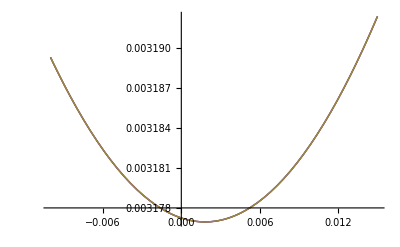
{15.047,-Graphics-}

```mathematica
Timing[Module[{ρ=0.0125053,λv=0.2,θv=0.0000101805,κ=0.0006281,V=0.0000101805,S0=0.003362,T=15,LimitGindinkin1=1,LimitGindinkin2=2,LimitGindinkin3=3},
vol1=Table[{k,NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,LimitGindinkin1]]},{k,-0.01,0.015,0.0005}];
vol2=Table[{k,NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,LimitGindinkin2]]},{k,-0.01,0.015,0.0005}];
vol3=Table[{k,NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,LimitGindinkin3]]},{k,-0.01,0.015,0.0005}];
inter1=Interpolation[vol1];inter2=Interpolation[vol2];inter3=Interpolation[vol3];
Plot[{inter1[k],inter2[k],inter3[k]},{k,-0.01,0.015}]]]
```

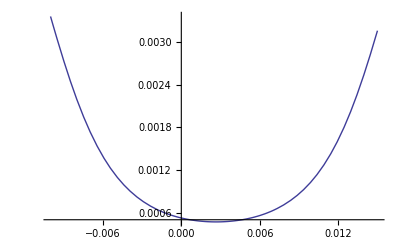
{10.266,-Graphics-}

```mathematica
Timing[Module[{ρ=0.0125053,λv=2,θv=0.0000101805,κ=0.6281,V=0.0000101805,S0=0.003362,T=15,LimitGindinkin1=1,LimitGindinkin2=1,LimitGindinkin3=1},
vol1=Table[{k,NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,LimitGindinkin1]]},{k,-0.01,0.015,0.0005}];
inter1=Interpolation[vol1];
Plot[{inter1[k]},{k,-0.01,0.015}]]]
```

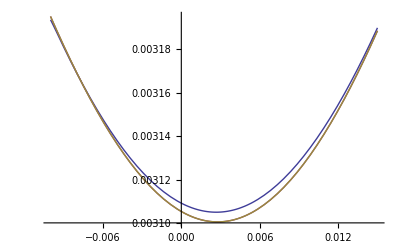
{20.453,-Graphics-}

```mathematica
Timing[Module[{ρ=0.0125053,λv=0.95,θv=0.0000101805,κ=0.006281,V=0.0000101805,S0=0.003362,T=15,LimitGindinkin1=1,LimitGindinkin2=2,LimitGindinkin3=3},
vol1=Table[{k,NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,LimitGindinkin1]]},{k,-0.01,0.015,0.0005}];
vol2=Table[{k,NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,LimitGindinkin2]]},{k,-0.01,0.015,0.0005}];
vol3=Table[{k,NormalImplicitVol[S0,k,T,TransHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T,LimitGindinkin3]]},{k,-0.01,0.015,0.0005}];
inter1=Interpolation[vol1];inter2=Interpolation[vol2];inter3=Interpolation[vol3];
Plot[{inter1[k],inter2[k],inter3[k]},{k,-0.01,0.015}]]]
```

## Verification

#### Standard

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.004,κ=0.02,V=0.004,S0=0,k={0.01,0.02},T=5},{HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T]}]]
```

{20.562,{{0.0511539,0.0468632},{{0.0542045,0.0497371},{0.0542045,0.0497371}},{{0.0511539,0.0468632},{0.0511539,0.0468632}}}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.0004,κ=0.02,V=0.0004,S0=0,k=0.01,T=5},{HestonNormalCall[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallN[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T]}]]
```

{5.609,{0.0197207,0.0197207,0.0197207}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.0004,κ=0.02,V=0.0004,S0=0,k=0.01,T=5},{HestonNormalCall[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallN[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T]}]]
```

{5.641,{0.0254532,0.0254532,0.0254532}}

#### preuve que la normalisation doit marcher

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.004,κ=0.02,V=0.004,S0=0,k=0.01,T=5,m={1,3,5,7,9,10}},(HestonNormalCallN[ρ,λv,#^2 θv,# κ,#^2 V,#S0,# k,T]/#)& /@m]]
```

{30.188,{0.0511539,0.0511539,0.0511539,0.0511539,0.0511539,0.0511539}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.004,κ=0.02,V=0.004,S0=0,k=0.01,T=5,m={1,2,3,4,5,6,7,8,9,10}},(HestonNormalCallTrace[ρ,λv,#^2 θv,# κ,#^2 V,#S0,# k,T]/#)& /@m]]
```

L=15.8114 κ1=0.316228 S01=0 k1=0.158114

L=7.90569 κ1=0.316228 S01=0 k1=0.158114

L=5.27046 κ1=0.316228 S01=0 k1=0.158114

L=3.95285 κ1=0.316228 S01=0 k1=0.158114

L=3.16228 κ1=0.316228 S01=0 k1=0.158114

L=2.63523 κ1=0.316228 S01=0 k1=0.158114

L=2.25877 κ1=0.316228 S01=0 k1=0.158114

L=1.97642 κ1=0.316228 S01=0 k1=0.158114

L=1.75682 κ1=0.316228 S01=0 k1=0.158114

L=1.58114 κ1=0.316228 S01=0 k1=0.158114

{0.094,{0.0511539,0.0511539,0.0511539,0.0511539,0.0511539,0.0511539,0.0511539,0.0511539,0.0511539,0.0511539}}

### Exploration des basse volatilités

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.01,κ=0.01,V=0.01,S0=0,k=0.01,T=5,m={0.1,0.01,0.005,0.001}},{HestonNormalCallTrace[ρ,λv,#θv,κ,#V,S0,k,T],HestonNormalCallN[ρ,λv,#θv,κ,#V,S0,k,T]}& /@m]]
```

L=31.6228 κ1=0.316228 S01=0 k1=0.316228

L=100. κ1=1. S01=0 k1=1.

L=141.421 κ1=1.41421 S01=0 k1=1.41421

L=316.228 κ1=3.16228 S01=0 k1=3.16228

{21.013,{{0.0234316,0.0234316},{0.00475905,0.0047787},{0.000368875,0.00263289},{0.0000517425,0.000567671}}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.55,θv=0.01,κ=0.01,V=0.01,S0=0,k=0.01,T=5,m={0.1,0.01,0.005,0.001}},{HestonNormalCallTrace[ρ,λv,#θv,κ,#V,S0,k,T],HestonNormalCallN[ρ,λv,#θv,κ,#V,S0,k,T]}& /@m]]
```

L=31.6228 κ1=0.316228 S01=0 k1=0.316228

L=100. κ1=1. S01=0 k1=1.

L=141.421 κ1=1.41421 S01=0 k1=1.41421

L=316.228 κ1=3.16228 S01=0 k1=3.16228

{20.249,{{0.0235315,0.0235315},{0.00494927,0.00494927},{0.00273352,0.00275524},{0.0000970247,0.000574895}}}

```mathematica
Timing[Module[{ρ=0.5,λv=2.1,θv=0.01,κ=0.01,V=0.01,S0=0,k=0.01,T=5,m={0.1,0.01,0.005,0.001}},{HestonNormalCallTrace[ρ,λv,#θv,κ,#V,S0,k,T],HestonNormalCallN[ρ,λv,#θv,κ,#V,S0,k,T]}& /@m]]
```

L=31.6228 κ1=0.316228 S01=0 k1=0.316228

L=100. κ1=1. S01=0 k1=1.

L=141.421 κ1=1.41421 S01=0 k1=1.41421

L=316.228 κ1=3.16228 S01=0 k1=3.16228

{20.514,{{0.0235347,0.0235347},{0.00492665,0.00492665},{0.00269693,0.00269693},{0.000452245,0.000452258}}}

on voit que le probleme provient du kappa et de k qui sont trop elevé. ce probleme est stabilise par la mean reversion

(ν normalisé | 0.0141421 | 0.0707107 | 0.212132 | 0.424264
√(2  λv θv/V) | 0.547723 | 0.547723 | 0.547723 | 0.547723)

FindRoot::jsing: Encountered a singular Jacobian at the point {u} = {0.0001}. Try perturbing the initial point(s).

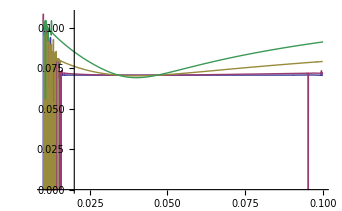
{290.328,-Graphics-}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.005,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},
Print[{{"ν normalisé",ToString[κ1/√V],ToString[κ2/√V],ToString[κ3/√V],ToString[κ4/√V]},
{"√(2  λv θv/V)",ToString[√(2λv θv/V)],ToString[√(2λv θv/V)],ToString[√(2λv θv/V)],ToString[√(2λv θv/V)]}}//MatrixForm];
Plot[{
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,0.01,0.1},PlotRange->All]]]
```

(ν normalisé | 0.0141421 | 0.0707107 | 0.212132 | 0.424264
2 λ θ | 0.6 | 0.6 | 0.6 | 0.6)

FindRoot::jsing: Encountered a singular Jacobian at the point {u} = {0.0001}. Try perturbing the initial point(s).

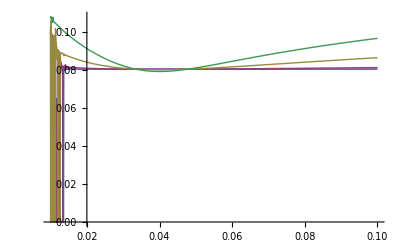
{176.047,-Graphics-}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.01,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},
Print[{{"ν normalisé",ToString[κ1/√V],ToString[κ2/√V],ToString[κ3/√V],ToString[κ4/√V]},
{"√(2  λv θv/V)",ToString[√(2λv θv/V)],ToString[√(2λv θv/V)],ToString[√(2λv θv/V)],ToString[√(2λv θv/V)]}}//MatrixForm];
Plot[{
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,0.01,0.1},PlotRange->All]]]
```

(ν normalisé | 0.0141421 | 0.0707107 | 0.212132 | 0.424264
2 λ θ | 3. | 3. | 3. | 3.)

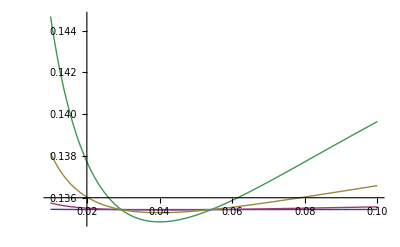
{71.219,-Graphics-}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.05,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},
Print[{{"ν normalisé",ToString[κ1/√V],ToString[κ2/√V],ToString[κ3/√V],ToString[κ4/√V]},
{"√(2  λv θv/V)",ToString[√(2λv θv/V)],ToString[√(2λv θv/V)],ToString[√(2λv θv/V)],ToString[√(2λv θv/V)]}}//MatrixForm];
Plot[{
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,0.01,0.1},PlotRange->All]]]
```

#### Probleme non resolu

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.001,κ=0.2,V=0.001,S0=0,k=0.01,T=5},{HestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallTrace[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T]}]]
```

L=31.6228 κ1=6.32456 S01=0 k1=0.316228

{5.647,{0.00902545,0.00341168,0.00902545}}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.001,κ=0.01,V=0.001,S0=0,k=0.01,T=5},{HestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallTrace[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T]}]]
```

L=31.6228 κ1=0.316228 S01=0 k1=0.316228

{5.085,{0.0231591,0.0231591,0.0231591}}

```mathematica
(*version scalaire *)
```

#### Cas des tres petite vols

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.0000005,κ=0.0002,V=0.0000005,S0=-0.004,k=0.005,T=5},{HestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallTrace[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T]}]]
```

L=1414.21 κ1=0.282843 S01=-5.65685 k1=7.07107

{5.491,{2.12599×10^-10,2.18346×10^-10,-6.51397×10^-6}}

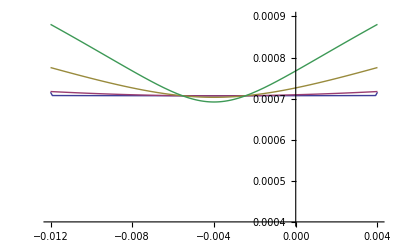
{11.747,-Graphics-}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.0000005,κ1=0.00001,κ2=0.00005,κ3=0.00015,κ4=0.0003,V=0.0000005,S0=-0.004,k=0.005,T=5},Plot[{
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,-0.012,0.004},PlotRange->{0.0004,0.0009}]]]
```

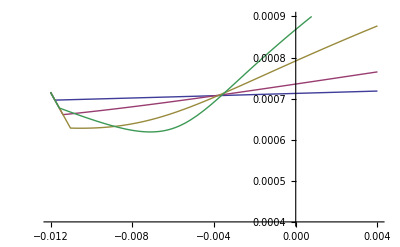
{9.251,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.0000005,κ1=0.00001,κ2=0.00005,κ3=0.00015,κ4=0.0003,V=0.0000005,S0=-0.004,k=0.005,T=5},Plot[{
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,-0.012,0.004},PlotRange->{0.0004,0.0009}]]]
```

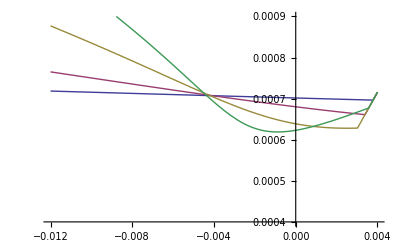
{9.953,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.0000005,κ1=0.00001,κ2=0.00005,κ3=0.00015,κ4=0.0003,V=0.0000005,S0=-0.004,k=0.005,T=5},Plot[{
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,-0.012,0.004},PlotRange->{0.0004,0.0009}]]]
```

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.001,κ=0.01,V=0.001,S0=0,k=0.01,T=5},{HestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallTrace[ρ,λv,θv,κ,V,S0,k,T],HestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T]}]]
```

L=31.6228 κ1=0.316228 S01=0 k1=0.316228

{6.022,{0.0231591,0.0231591,0.0231591}}

## Moments d'un Normal Heston et power option 1D

```mathematica
Simplify[∫_(k^(1/n))^∞ ⅇ^(ⅈ ω x1) (x1^n-k)ⅆx1]
```

If[Im[ω]>0&&(Im[k^(1/n)]≠0||k^(1/n)>0),-(ⅈ (ⅇ^(ⅈ k^(1/n) ω) k+(-(-ⅈ ω)^-n+(k^(1/n))^n (-ⅈ k^(1/n) ω)^-n) Gamma[1+n]-(k^(1/n))^n (-ⅈ k^(1/n) ω)^-n Gamma[1+n,-ⅈ k^(1/n) ω]))/ω,Integrate[-ⅇ^(ⅈ x1 ω) k+ⅇ^(ⅈ x1 ω) x1^n,{x1,k^(1/n),∞},Assumptions→k^(1/n)≤0||Im[ω]≤0]]

```mathematica
Simplify[∫_(-∞)^(k^(1/n)) ⅇ^(ⅈ ω x1) (k-x1^n)ⅆx1]
```

If[Im[ω]<0&&(Im[k^(1/n)]≠0||Sign[k^(1/n)]==-1),-(ⅈ (ⅇ^(ⅈ k^(1/n) ω) k+(-(-1)^n (ⅈ ω)^-n+(k^(1/n))^n (-ⅈ k^(1/n) ω)^-n) Gamma[1+n]-(k^(1/n))^n (-ⅈ k^(1/n) ω)^-n Gamma[1+n,-ⅈ k^(1/n) ω]))/ω,Integrate[ⅇ^(ⅈ x1 ω) k-ⅇ^(ⅈ x1 ω) x1^n,{x1,-∞,k^(1/n)},Assumptions→!(Im[ω]<0&&(Im[k^(1/n)]≠0||Sign[k^(1/n)]==-1))]]

```mathematica
Simplify[-(ⅈ (ⅇ^(ⅈ k^(1/n) ω) k+(-(-ⅈ ω)^-n+(k^(1/n))^n (-ⅈ k^(1/n) ω)^-n) Gamma[1+n]-(k^(1/n))^n (-ⅈ k^(1/n) ω)^-n Gamma[1+n,-ⅈ k^(1/n) ω]))/ω,k>0&& n>0]
```

-(ⅈ (ⅇ^(ⅈ k^(1/n) ω) k-(-ⅈ ω)^-n Gamma[1+n,-ⅈ k^(1/n) ω]))/ω

```mathematica
Simplify[∫_0^∞ ⅇ^(ⅈ ω x1) (x1^n)ⅆx1]
```

If[Im[ω]>0&&Re[n]>-1,(-ⅈ ω)^(-1-n) Gamma[1+n],Integrate[ⅇ^(ⅈ x1 ω) x1^n,{x1,0,∞},Assumptions→Im[ω]≤0||(Im[ω]>0&&Re[n]≤-1)]]

```mathematica
NormalPowerCallPayOffFourierTransform[k_,n_,ω_]:=If[k≠0,-(ⅈ (ⅇ^(ⅈ k^(1/n) ω) k-(-ⅈ ω)^-n Gamma[1+n,-ⅈ k^(1/n) ω]))/ω,(-ⅈ ω)^(-1-n) Gamma[1+n]]
```

### Implementation mathematica de reference

```mathematica
HestonPowerNormalCallN[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
NIntegrate[ⅇ^(-ⅈ (ω +λ ⅈ)S0)NormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω+ⅈ λ,T]NormalPowerCallPayOffFourierTransform[k,n,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
HestonPowerNormalPutN[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
NIntegrate[ⅇ^(-ⅈ (ω +λ ⅈ)S0)NormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω+ⅈ λ,T]NormalPowerCallPayOffFourierTransform[k,n,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

### Implementation Operationnelle

```mathematica
HestonPowerNormalCallAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
AdaptativeIntegrate[Function[ω,ⅇ^(-ⅈ (ω +λ ⅈ)S0)NormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω +λ ⅈ,T]NormalPowerCallPayOffFourierTransform[k,n,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[20],
10/T,5/T,10^(-10),1000,1/T,LegendreCoeffs[60]][[2]]]]
```

```mathematica
HestonPowerNormalPutAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
AdaptativeIntegrate[Function[ω,ⅇ^(-ⅈ (ω +λ ⅈ)S0)NormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω +λ ⅈ,T]NormalPowerCallPayOffFourierTransform[k,n,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[20],
10/T,5/T,10^(-10),1000,1/T,LegendreCoeffs[60]][[2]]]]
```

### Implementation Normalisée

```mathematica
HestonPowerNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=Module[{θv1,κ1,V1,S01,k1,L,prix},
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L^n k;
prix=HestonPowerNormalCallAux[ρ,λv,θv1,κ1,V1,S01,k1,n,T];
L^-n*prix]
```

```mathematica
HestonPowerNormalPut[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=Module[{θv1,κ1,V1,S01,k1,L,prix},
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L^n k;
prix=HestonPowerNormalPutAux[ρ,λv,θv1,κ1,V1,S01,k1,n,T];
L^-n*prix]
```

```mathematica
HestonNormalVariance[ρ_,λv_,θv_,κ_,V_,S0_,T_]:=Module[{call,put},
call=HestonPowerNormalCall[ρ,λv,θv,κ,V,S0,S0^2,2,T];
put=HestonPowerNormalPut[ρ,λv,θv,κ,V,S0,S0^2,2,T];
call-put]
```

```mathematica
HestonNormalVarianceTrace[ρ_,λv_,θv_,κ_,V_,S0_,T_]:=Module[{call,put},
call=HestonPowerNormalCall[ρ,λv,θv,κ,V,S0,S0^2,2,T];
put=HestonPowerNormalPut[ρ,λv,θv,κ,V,S0,S0^2,2,T];
Print["T=",T," call=",call," put=",put];
call-put]
```

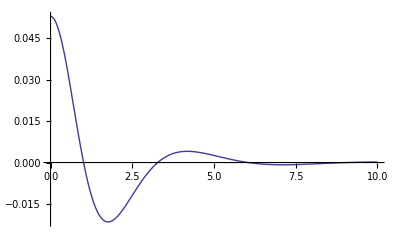
{0.344,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.1,λv=0.15,θv=0.01,κ=0.1,V=0.01,S0=0.001,λ1=2.5,T=10,k=1,n=2,ω},
Plot[{Re[ⅇ^(-ⅈ (ω+ⅈ λ1)  S0)NormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω+ⅈ λ1,T]NormalPowerCallPayOffFourierTransform[k,n,ω+ⅈ λ1]]},{ω,0,10},PlotRange->All]
]]
```

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.05,κ=0.1,V=0.05,S0=0.001,T=5},
HestonPowerNormalCallAux[ρ,λv,θv,κ,V,S0,0,2,T]]]
```

{0.141,-0.125389}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.001,κ=0.1,V=0.001,S0=0,T=5},
HestonNormalVariance[ρ,λv,θv,κ,V,S0,T]]]
```

{0.328,-0.000687706}

#### Moments a partir de la transformé de fourier

```mathematica
NormalHestonFondamentalTransformLog[ρ_,λv_,θv_,κ_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ},
ζ=√((λv+ρ κ ⅈ ω)^2+κ^2( ω^2));
ψp =-(λv+ρ κ  ⅈ ω)+ζ;
ψm =(λv+ρ κ  ⅈ ω)+ζ;
A=-(θv λv (τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/κ^2;
B=(-( ω^2)(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
A+B V]
```

```mathematica
D2=D[NormalHestonFondamentalTransformLog[ρ,λv,θv,κ,V,ω,τ],{ω,2}];
D2LogNormalHestonFondamentalTransform=Function[{ρ,λv,θv,κ,V,τ},Evaluate[1/ⅈ^2 D2/. ω->0]];
```

```mathematica
D2LogNormalHestonFondamentalTransform=Function[{ρ,λv,θv,κ,V,τ},Evaluate[Simplify[D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ],λv>0]]];
```

```mathematica
Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.01,ω=0,τ=30},
{D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ]}]
```

{1.00222}

La formule est en fait tres simple

```mathematica
D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ]
```

(V-ⅇ^(-λv τ) V+θv (-1+ⅇ^(-λv τ)+λv τ))/λv

```mathematica
et lorsque V=θv
```

```mathematica
Simplify[D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ] /. θv->V]
```

V τ

#### Comparaison entre les differents moyens de calculer la variance d'un normal Heston

ca marche pour des maturité inferieure a 2.5  an , pourquoi , mystere

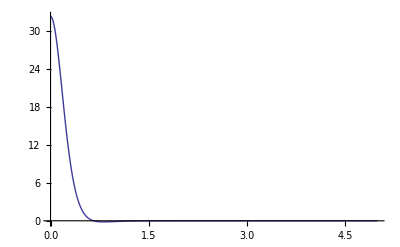
{0.406,{-Graphics-,{0.0195418,0.0462}}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.011,κ=0.05,V=0.011,S0=0,k,T=4.2,λ=0.5,L,θv1,κ1,V1,S01,k1},k=S0;
L=√(1./V);θv1=L^2 θv;κ1=L κ;V1=1.0;S01=L S0;k1=L^2 k;
{Plot[{Re[ⅇ^(-ⅈ (ω+ⅈ λ)  S01)NormalHestonFondamentalTransform[ρ,λv,θv1,κ1,V1,ω+ⅈ λ,T]NormalPowerCallPayOffFourierTransform[k1,2,ω +λ ⅈ]]},{ω,0,5},PlotRange->All],
{HestonNormalVariance[ρ,λv,θv,κ,V,S0,T]-S0^2,D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,T]}}]]
```

## LogNormal 1,2,3,4 et 5 Facteurs de vol

```mathematica
LogNormalHestonFondamentalTransform[ρ_,λv_,θv_,κ_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ,η},
η=λv+ρ κ ⅈ ω;
argζ=η^2+κ^2(ω^2-ⅈ ω);
ζ=√argζ;
ψp =-η+ζ;
ψm =η+ζ;
A=-(θv λv (τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/κ^2;
B=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
If[Re[A+B V]<-100,0,
ⅇ^(A+B V)]]
```

```mathematica
LogNormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ω_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,B1,argζ1,η1,ζ2,ψp2 ,ψm2,A2,B2,argζ2,η2,A},
η1=λv1+ρ1 κ1 ⅈ ω;
argζ1=η1^2+κ1^2(ω^2-ⅈ ω);
ζ1=√argζ1;
ψp1 =-η1+ζ1;
ψm1 =η1+ζ1;
B1=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
η2=λv2+ρ2 κ2 ⅈ ω;
argζ2=η2^2+κ2^2(ω^2-ⅈ ω);
ζ2=√argζ2;
ψp2 =-η2+ζ2;
ψm2 =η2+ζ2;
B2=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
A=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2;
If[Re[A+B1 V1+B2 V2]<-100,0,
ⅇ^(A+B1 V1+B2 V2)]
]
```

```mathematica
LogNormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ω_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,argζ1,η1,ζ2,ψp2 ,ψm2,argζ2,η2,ζ3,ψp3 ,ψm3,A3,argζ3,η3,B1,B2,B3,A},
η1=λv1+ρ1 κ1 ⅈ ω;
argζ1=(λv1+ρ1 κ1 ⅈ ω)^2+κ1^2(ω^2-ⅈ ω);
ζ1=√argζ1;
ψp1 =-η1+ζ1;
ψm1 =η1+ζ1;
B1=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
η2=λv2+ρ2 κ2 ⅈ ω;
argζ2=η2^2+κ2^2(ω^2-ⅈ ω);
ζ2=√argζ2;
ψp2 =-η2+ζ2;
ψm2 =η2+ζ2;
B2=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
η3=λv3+ρ3 κ3 ⅈ ω;
argζ3=η3^2+κ3^2(ω^2-ⅈ ω);
ζ3=√argζ3;
ψp3 =-η3+ζ3;
ψm3 =η3+ζ3;
B3=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));
A=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2;
If[Re[A+B1 V1+B2 V2+B3 V3]<-100,0,
ⅇ^(A+B1 V1+B2 V2+B3 V3)]
]
```

```mathematica
LogNormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ω_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,argζ1,η1,ζ2,ψp2 ,ψm2,argζ2,η2,ζ3,ψp3 ,ψm3,A3,argζ3,η3,ζ4,ψp4 ,ψm4,A4,argζ4,η4,B1,B2,B3,B4,A},
η1=λv1+ρ1 κ1 ⅈ ω;
argζ1=(λv1+ρ1 κ1 ⅈ ω)^2+κ1^2(ω^2-ⅈ ω);
ζ1=√argζ1;
ψp1 =-η1+ζ1;
ψm1 =η1+ζ1;
B1=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
η2=λv2+ρ2 κ2 ⅈ ω;
argζ2=η2^2+κ2^2(ω^2-ⅈ ω);
ζ2=√argζ2;
ψp2 =-η2+ζ2;
ψm2 =η2+ζ2;
B2=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
η3=λv3+ρ3 κ3 ⅈ ω;
argζ3=η3^2+κ3^2(ω^2-ⅈ ω);
ζ3=√argζ3;
ψp3 =-η3+ζ3;
ψm3 =η3+ζ3;
B3=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));
η4=λv4+ρ4 κ4 ⅈ ω;
argζ4=η4^2+κ4^2(ω^2-ⅈ ω);
ζ4=√argζ4;
ψp4 =-η4+ζ4;
ψm4 =η4+ζ4;
B4=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ4  τ)))/(ψm4+ψp4 ⅇ^(-ζ4  τ));
A=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2-(θv4 λv4 (τ ψp4+2 Log[(ψm4+ⅇ^(-ζ4 τ) ψp4)/(2ζ4)]))/κ4^2;
If[Re[A+B1 V1+B2 V2+B3 V3+B4 V4]<-100,0,
ⅇ^(A+B1 V1+B2 V2+B3 V3+B4 V4)]
]
```

```mathematica
LogNormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,ω_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,argζ1,η1,ζ2,ψp2 ,ψm2,argζ2,η2,ζ3,ψp3 ,ψm3,A3,argζ3,η3,ζ4,ψp4 ,ψm4,A4,argζ4,η4,ζ5,ψp5 ,ψm5,A5,argζ5,η5,B1,B2,B3,B4,B5,A},
η1=λv1+ρ1 κ1 ⅈ ω;
argζ1=(λv1+ρ1 κ1 ⅈ ω)^2+κ1^2(ω^2-ⅈ ω);
ζ1=√argζ1;
ψp1 =-η1+ζ1;
ψm1 =η1+ζ1;
B1=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
η2=λv2+ρ2 κ2 ⅈ ω;
argζ2=η2^2+κ2^2(ω^2-ⅈ ω);
ζ2=√argζ2;
ψp2 =-η2+ζ2;
ψm2 =η2+ζ2;
B2=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
η3=λv3+ρ3 κ3 ⅈ ω;
argζ3=η3^2+κ3^2(ω^2-ⅈ ω);
ζ3=√argζ3;
ψp3 =-η3+ζ3;
ψm3 =η3+ζ3;
B3=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));
η4=λv4+ρ4 κ4 ⅈ ω;
argζ4=η4^2+κ4^2(ω^2-ⅈ ω);
ζ4=√argζ4;
ψp4 =-η4+ζ4;
ψm4 =η4+ζ4;
B4=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ4  τ)))/(ψm4+ψp4 ⅇ^(-ζ4  τ));
η5=λv5+ρ5 κ5 ⅈ ω;
argζ5=η5^2+κ5^2(ω^2-ⅈ ω);
ζ5=√argζ5;
ψp5 =-η5+ζ5;
ψm5 =η5+ζ5;
B5=(-(ω^2-ⅈ ω)(1-ⅇ^(-ζ5  τ)))/(ψm5+ψp5 ⅇ^(-ζ5  τ));
A=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2-(θv4 λv4 (τ ψp4+2 Log[(ψm4+ⅇ^(-ζ4 τ) ψp4)/(2ζ4)]))/κ4^2-(θv5 λv5 (τ ψp5+2 Log[(ψm5+ⅇ^(-ζ5 τ) ψp5)/(2ζ5)]))/κ5^2;
If[Re[A+B1 V1+B2 V2+B3 V3+B4 V4+B5 V5]<-100,0,
ⅇ^(A+B1 V1+B2 V2+B3 V3+B4 V4+B5 V5)]
]
```

## LogNormal 1,2,3,4 et 5 Facteurs de vol : Integrands

#### Cas scalaire pour 1, 2,3,4 et 5 facteurs

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0]) LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ω,T]LogNormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ω,T]LogNormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ω,T]LogNormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ω,T]LogNormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,S0_,K_,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,ω,T]LogNormalCallPayOffFourierTransform[K,α,a,ω]]
```

#### Cas vectoriel pour 1,2,3,4 et 5 facteurs

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ω,T]Table[LogNormalCallPayOffFourierTransform[K,α,a,ω],{i,1,Length[K]}]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ω,T]Table[LogNormalCallPayOffFourierTransform[K,α,a,ω],{i,1,Length[K]}]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ω,T]Table[LogNormalCallPayOffFourierTransform[K,α,a,ω],{i,1,Length[K]}]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ω,T]LogNormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
LogNormalHestonCallIntegrand[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,S0_,K_List,α_,a_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0])  LogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,ω,T]LogNormalCallPayOffFourierTransform[K,α,a,ω]]
```

```mathematica
Clear[LogNormalHestonCallIntegrand]
```

```mathematica
Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=0.01,S0=0.05,λ1=0.05,λ2=0.5,λ3=0.9,T=0.5,k=0.01,ω=1.2},
LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω]]
```

0.00175681

```mathematica
Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=0.01,S0=0.05,λ1=0.05,λ2=0.5,λ3=0.9,T=0.5,k=0.01,ω=1.2},
LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω,T]]
```

-0.003562-0.000259168 ⅈ

## Shift et parametres d' integration

le shift ici sera pris a 0.5. A ce shift sera adapté les constante de la procedure d' integration.

Exemple d' integrand pour des shift differents

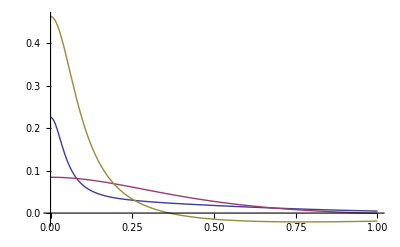
{0.203,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=1,S0=0.05,λ1=0.05,λ2=0.5,λ3=0.9,T=0.5,k=0.01,ω},
Plot[{LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ1 ⅈ],
LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ2 ⅈ],
LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ3 ⅈ]},{ω,0,1},PlotRange->All]
]]
```

on voit que le shift determine a lui tout seul les parametre

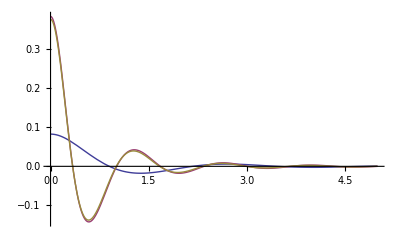
{1.328,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=0.01,S0=1,λ1=0.05,λ2=0.5,λ3=0.9,T=30,k=0.01,ω},
Plot[{LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,2,T,ω +λ2 ⅈ],
LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ2 ⅈ],
LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ2 ⅈ]},{ω,0,5},PlotRange->All]
]]
```

#### Determination de parametres d' integration de la version normalisée

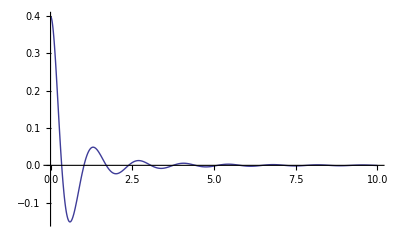
{0.344,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.1,λv=0.15,θv=0.01,κ=2,V=0.01,S0=1,λ1=0.5,T=10,k=0.01,ω},
Plot[{Re[ⅇ^(-ⅈ (ω+ⅈ λ1)  Log[S0])LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω+ⅈ λ1,T]LogNormalCallPayOffFourierTransform[k,ω+ⅈ λ1]]},{ω,0,10},PlotRange->All]
]]
```

## LogNormal 1,2,3,4 et 5 Facteurs de vol : Implementations

### Implementation mathematica de reference

```mathematica
LogHestonNormalCallN[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
LogHestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
LogHestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
LogHestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
LogHestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,S0,k,1,1,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

### Implementation Operationnelle

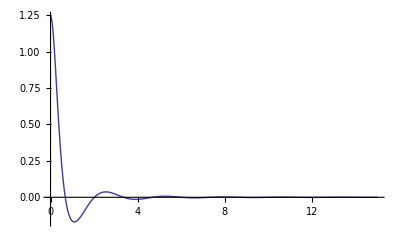
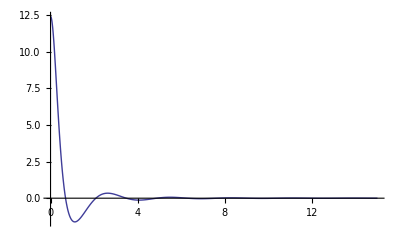
{0.687,{-Graphics-,-Graphics-}}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=0.01,S0=1,T=30,k=0.01,ω},
{Plot[{LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,S0/10,1,1,T,ω +0.5 ⅈ]},{ω,0,15},PlotRange->All],
Plot[{LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,S0 10,1,1,T,ω +0.5 ⅈ]},{ω,0,15},PlotRange->All]}
]]
```

```mathematica
LogHestonNormalCallAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,2,10^(-10),1000,2,LegendreCoeffs[20]][[2]]]]
```

```mathematica
LogHestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
LogHestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
LogHestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
LogHestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
(*version Vecteur *)
```

### Implementation Normalisée

```mathematica
LogHestonNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{},
S0 LogHestonNormalCallAux[ρ,λv,θv,κ,V,1,k/S0,T]
]
```

```mathematica
LogHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=Module[{},
S0 LogHestonNormalCallAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,1,k/S0,T]
]
```

```mathematica
LogHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=Module[{},
S0 LogHestonNormalCallAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,1,k/S0,T]
]
```

```mathematica
LogHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,S0_,k_,T_]:=Module[{},
S0 LogHestonNormalCallAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,1,k/S0,T]
]
```

```mathematica
LogHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,S0_,k_,T_]:=Module[{},
S0 LogHestonNormalCallAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,1,k/S0,T]
]
```

## Implentation des densitée

```mathematica
LogHestonNormalDensité[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{shift=S0/1000},Max[0,(LogHestonNormalCall[ρ,λv,θv,κ,V,S0,k+shift,T]+LogHestonNormalCall[ρ,λv,θv,κ,V,S0,k-shift,T]-2LogHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T])/(shift^2)]]
```

```mathematica
LogHestonNormalDensité[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,T_]:=Module[{shift=S0/1000},Max[0,(LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k+shift,T]+LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k-shift,T]-2LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,T])/(shift^2)]]
```

```mathematica
LogHestonNormalDensité[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,T_]:=Module[{shift=S0/1000},Max[0,(LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k+shift,T]+LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k-shift,T]-2LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,T])/(shift^2)]]
```

```mathematica
LogHestonNormalDensité[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,S0_,k_,T_]:=Module[{shift=S0/1000},Max[0,(LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,S0,k+shift,T]+LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,S0,k-shift,T]-2LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,S0,k,T])/(shift^2)]]
```

```mathematica
LogHestonNormalDensité[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,S0_,k_,T_]:=Module[{shift=S0/1000},Max[0,(LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,S0,k+shift,T]+LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,S0,k-shift,T]-2LogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,ρ4,λv4,θv4,κ4,V4,ρ5,λv5,θv5,κ5,V5,S0,k,T])/(shift^2)]]
```

## Implementation des variances

### Variance par integration

```mathematica
CoeffBasedVariance[density_,coeffs_]:=Module[{n=Length[coeffs],densitytable,Expectation=0,variance=0,normalisation=0,i},
densitytable=Table[density[coeffs[[i,1]]],{i,1,n}];
Do[normalisation+= densitytable[[i]] coeffs[[i,2]],{i,1,n}];
Do[Expectation+=coeffs[[i,1]] densitytable[[i]] coeffs[[i,2]],{i,1,n}];Expectation/=normalisation;
Do[variance+=(coeffs[[i,1]]-Expectation)^2 densitytable[[i]] coeffs[[i,2]],{i,1,n}];
Print["normalisation=",normalisation," Expectation=",Expectation," variance=",variance];
variance/=normalisation;
variance]
```

```mathematica
CoeffBasedVariance[density_,coeffs_,Expectation_]:=Module[{n=Length[coeffs],densitytable,variance=0,i},
densitytable=Table[density[coeffs[[i,1]]],{i,1,n}];
Do[variance+=(coeffs[[i,1]]-Expectation)^2 densitytable[[i]] coeffs[[i,2]],{i,1,n}];
variance]
```

```mathematica
LogHestonNormalVariance2[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=CoeffBasedIntegrate[((#-S0)^2 LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,S0/5,6S0]]
```

```mathematica
LogHestonNormalVariance3[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,S0/5,6S0]]
```

```mathematica
LogHestonNormalEsperance[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=CoeffBasedIntegrate[((#)LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,S0/5,6S0]]
```

```mathematica
LogHestonNormalNormalisation[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=CoeffBasedIntegrate[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,S0/5,6S0]]
```

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalEsperance[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalNormalisation[ρ,λv,θv,κ,V,S0,k,T]}]]
```

{2.636,{0.0489338,0.990318}}

### Variance du Heston normal a maturité

dV_s=λ(V_∞-V_s)ds+dM_s  donc V_s=∫_0^s (λ(V_∞-V_u)du+dM_u  )ⅆu

Soit  L_T=∫_0^T V_s ⅆs==

E[L_T]=∫_0^T E[V_s]ⅆs

or je sais que E[V_s]=V_∞+(V_0-V_∞)ⅇ^(-λ s)

donc

E[L_T]=∫_0^T (V_∞+(V_0-V_∞)ⅇ^(-λ s))ⅆs=T  V_∞ + (V_0-V_∞) ((1-ⅇ^(-λ T))/λ)

### Proxy de variance

```mathematica
Simplify[Integrate[ⅇ^x(ⅇ^(-(x-x0)^2/(2 σ^2)))/(√(2π)σ),{x,-∞,∞}],σ>0]
```

ⅇ^(x0+σ^2/2)

```mathematica
Simplify[Integrate[ⅇ^(2x)(ⅇ^(-(x-x0)^2/(2 σ^2)))/(√(2π)σ),{x,-∞,∞}],σ>0]
```

ⅇ^(2 (x0+σ^2))

donc variance=ⅇ^(2 (x0+σ^2))-(ⅇ^(x0+σ^2/2))^2=

```mathematica
Simplify[ⅇ^(2 (x0+σ^2))-(ⅇ^(x0+σ^2/2))^2]
```

ⅇ^(2 x0+σ^2) (-1+ⅇ^(σ^2))

```mathematica
LogHestonNormalVarianceProxy[ρ_,λv_,θv_,κ_,V_,S0_,T_]:=Module[{Vlog},
Vlog=θv T+(V -θv)((1-ⅇ^(-λv T))/λv);
S0^2 ⅇ^Vlog(ⅇ^Vlog-1)]
```

```mathematica
LogHestonNormalVarianceProxy[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,T_]:=Module[{Vlog1,Vlog2},
Vlog1=θv1 T+(V1 -θv1)((1-ⅇ^(-λv1 T))/λv1);
Vlog2=θv2 T+(V2 -θv2)((1-ⅇ^(-λv2 T))/λv2);
S0^2 ⅇ^(Vlog1+Vlog2)(ⅇ^(Vlog1+Vlog2)-1)
]
```

```mathematica
LogHestonNormalVarianceProxy[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,T_]:=Module[{Vlog1,Vlog2,Vlog3},
Vlog1=θv1 T+(V1 -θv1)((1-ⅇ^(-λv1 T))/λv1);
Vlog2=θv2 T+(V2 -θv2)((1-ⅇ^(-λv2 T))/λv2);
Vlog3=θv3 T+(V3 -θv3)((1-ⅇ^(-λv3 T))/λv3);
S0^2 ⅇ^(Vlog1+Vlog2+Vlog3)(ⅇ^(Vlog1+Vlog2+Vlog3)-1)
]
```

```mathematica
LogHestonNormalVarianceProxy[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,S0_,T_]:=Module[{Vlog1,Vlog2,Vlog3,Vlog4},
Vlog1=θv1 T+(V1 -θv1)((1-ⅇ^(-λv1 T))/λv1);
Vlog2=θv2 T+(V2 -θv2)((1-ⅇ^(-λv2 T))/λv2);
Vlog3=θv3 T+(V3 -θv3)((1-ⅇ^(-λv3 T))/λv3);
Vlog4=θv4 T+(V4 -θv4)((1-ⅇ^(-λv4 T))/λv4);
S0^2 ⅇ^(Vlog1+Vlog2+Vlog3+Vlog4)(ⅇ^(Vlog1+Vlog2+Vlog3+Vlog4)-1)
]
```

```mathematica
LogHestonNormalVarianceProxy[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,ρ4_,λv4_,θv4_,κ4_,V4_,ρ5_,λv5_,θv5_,κ5_,V5_,S0_,T_]:=Module[{Vlog1,Vlog2,Vlog3,Vlog4,Vlog5},
Vlog1=θv1 T+(V1 -θv1)((1-ⅇ^(-λv1 T))/λv1);
Vlog2=θv2 T+(V2 -θv2)((1-ⅇ^(-λv2 T))/λv2);
Vlog3=θv3 T+(V3 -θv3)((1-ⅇ^(-λv3 T))/λv3);
Vlog4=θv4 T+(V4 -θv4)((1-ⅇ^(-λv4 T))/λv4);
Vlog5=θv5 T+(V5 -θv5)((1-ⅇ^(-λv5 T))/λv5);
S0^2 ⅇ^(Vlog1+Vlog2+Vlog3+Vlog4+Vlog5)(ⅇ^(Vlog1+Vlog2+Vlog3+Vlog4+Vlog5)-1)
]
```

### Exemples

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T]}]]
```

{5.07,{0.00681842,0.00681842,0.00681842}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalCall[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallAux[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallN[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T]}]]
```

{5.188,{0.0107732,0.0107732,0.0107732}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalCall[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallAux[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallN[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T]}]]
```

{4.765,{0.0182362,0.0182362,0.0182362}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalCall[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallAux[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallN[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,k,T]}]]
```

{5.219,{0.0137363,0.0137363,0.0137363}}

#### Verification de la convergence des integrales

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalCall[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallAux[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalCallN[ρ,λv,θv,κ,V,S0,k,T]}]]
```

{5.07,{0.00681842,0.00681842,0.00681842}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T]}]]
```

{0.203,{0.000362438,0.000362438,0.000362438}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T]}]]
```

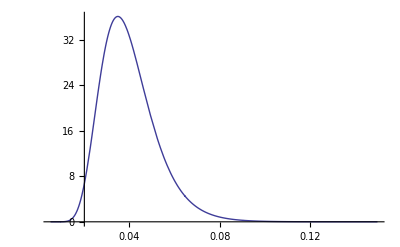
{30.81,-Graphics-}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.05,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},Plot[{
LogHestonNormalDensité[ρ,λv,θv,κ1,V,S0,k,T]},{k,0.005,0.15},PlotRange->All]]]
```

```mathematica
LogHestonNormalVariance2[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_,n1_,n2_]:=CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[60,S0/n1,n2 S0]]
```

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=5},{
LogHestonNormalVariance3[ρ,λv,θv,κ,V,S0,k,T,5,5],
LogHestonNormalVariance3[ρ,λv,θv,κ,V,S0,k,T,10,10],
LogHestonNormalVariance3[ρ,λv,θv,κ,V,S0,k,T,10,20], S0^2 V T,LogHestonNormalVarianceProxy[ρ,λv,θv,κ,V,S0,T]}]]
```

{1.35891×10^-13,{LogHestonNormalVariance3[0.5,0.15,0.04,0.2,0.04,0.05,0.055,5,5,5],LogHestonNormalVariance3[0.5,0.15,0.04,0.2,0.04,0.05,0.055,5,10,10],LogHestonNormalVariance3[0.5,0.15,0.04,0.2,0.04,0.05,0.055,5,10,20],0.0005,0.000676055}}

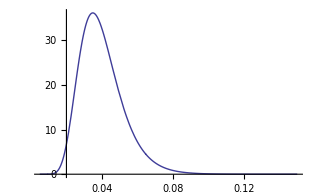
{30.81,-Graphics-}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.05,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},Plot[{
LogHestonNormalDensité[ρ,λv,θv,κ1,V,S0,k,T]},{k,0.005,0.15},PlotRange->All]]]
```

normalisation=0.989834 Expectation=0.0494119 variance=0.000620144

normalisation=0.998193 Expectation=0.049213 variance=0.000623134

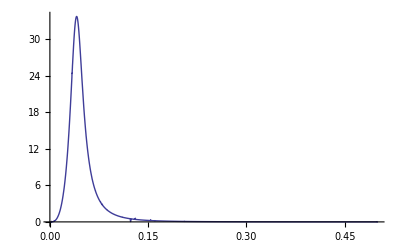
{256.156,{-Graphics-,0.000626514,0.000624262,0.00113072,0.000517143,0.0005,0.00268221}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,T=5},
{Plot[{LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T]},{k,0.001,0.5},PlotRange->All],
CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,S0/5,6S0]],
CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[40,0.005,0.3]],
LogHestonNormalVariance[ρ,λv,θv,κ,V,S0,T],
CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,0.01,0.22],S0],
 S0^2 V T,
LogHestonNormalVarianceProxy[ρ,λv,θv,κ,V,S0,T]}]]
```

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.04,κ=0.4,V=0.04,S0=1,T=15},
√(LogHestonNormalVariance[ρ,λv,θv,κ,V,S0,T]/(S0 S0 T))]]
```

{0.219,0.14762}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=0.01,S0=1,T=30,k=0.01,ω},
{Plot[{LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,S0/10,1,1,T,ω +0.5 ⅈ]},{ω,0,15},PlotRange->All],
Plot[{LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,S0 10,1,1,T,ω +0.5 ⅈ]},{ω,0,15},PlotRange->All]}
]]
```

{0.687,{-Graphics-,-Graphics-}}

```mathematica
LogHestonNormalCallAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=S0-1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[12],
10,2,10^(-10),1000,2,LegendreCoeffs[30]][[2]]]]
```

normalisation=0.999665 Expectation=0.0500096 variance=0.000554284

normalisation=0.96135 Expectation=0.0471624 variance=0.000331847

prixheston=0.00885103 prixBS=0.0191462 VarianceNaive=0.2 VarianceCorrigée=0.0427415

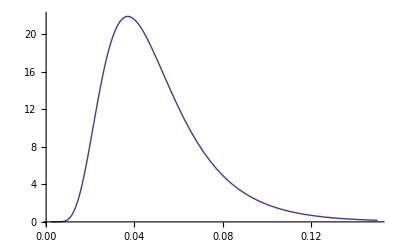
{44.469,{-Graphics-,0.00055447,0.000345189,0.000339588,0.0005,0.0427415}}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.002,V=0.04,S0=0.05,T=5},
{Plot[{LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,k,T]},{k,0.002,0.15},PlotRange->All],
CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,S0/5,6S0]],
CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,0.01,0.1]],
CoeffBasedVariance[(LogHestonNormalDensité[ρ,λv,θv,κ,V,S0,#,T])&,LegendreCoeffs[20,0.01,0.1],S0],
 S0^2 V T,LogHestonNormalVarianceProxy[ρ,λv,θv,κ,V,S0,T]}]]
```

#### ca s' ecroule a 30 ans !

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=0.055,T=30},{LogHestonNormalEsperance[ρ,λv,θv,κ,V,S0,k,T],LogHestonNormalNormalisation[ρ,λv,θv,κ,V,S0,k,T],
LogHestonNormalVariance[ρ,λv,θv,κ,V,S0,k,T]/LogHestonNormalNormalisation[ρ,λv,θv,κ,V,S0,k,T],
LogHestonNormalVariance2[ρ,λv,θv,κ,V,S0,k,T], S0^2 V T}]]
```

{3.494,{0.0370348,0.871985,0.00147998,0.00142331,0.003}}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.01,κ=0.5,V=0.01,S0=1,λ1=0.05,λ2=0.5,λ3=0.9,T=30,k=0.01,ω},
Plot[{LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,2,T,ω +λ2 ⅈ]},{ω,0,5},PlotRange->All]
]]
```

#### Verification du Smile

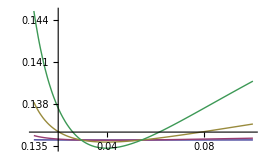
{42.109,-Graphics-}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.05,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},Plot[{
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,0.01,0.1},PlotRange->All]]]
```

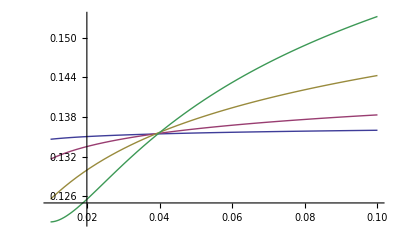
{14.625,-Graphics-}

```mathematica
Timing[Module[{ρ=0.5,λv=0.15,θv=0.05,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},Plot[{
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,0.01,0.1},PlotRange->All]]]
```

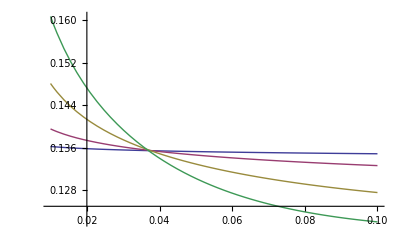
{11.75,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.05,κ1=0.001,κ2=0.005,κ3=0.015,κ4=0.03,V=0.005,S0=0.04,k=0.05,T=5},Plot[{
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ1,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ2,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ3,V,S0,k,T]],
ImpVolBS[S0,k,T,LogHestonNormalCall[ρ,λv,θv,κ4,V,S0,k,T]]},{k,0.01,0.1},PlotRange->All]]]
```

## Lognormal Shifté

### Dynamique β>0

dF/(β F+(1-β )F_0)=∑_(i=1)^N √V_i dW_i

#### pricing

donc

dF/(F+(1-β )/β F_0)=∑_(i=1)^N √(β^2 V_i)dW_i

c'est donc un lognormal ou l'on decale F_0 ainsi que les strike de la valeur:(1-β )/β F_0  et on modifie le dynamique en multipliant V_(i,0)  et θ_i par β^2 ainsi que κ_i par β

Fonction de packaging

### Dynamique β<0 on cree β^*=-β

dF/((1+β^* )F_0-β^* F)=∑_(i=1)^N √V_i dW_i

donc

dF/(F-(1+β^* )/β^*F_0)=∑_(i=1)^N √(β^2 V_i)d(W̄)_i  (avec (W̄)_i=-W_i et ρ = -ρ_initial)

c'est donc un lognormal ou l'on decale F_0 ainsi que les strike de la valeur:-(1+β^* )/β^*F_0  et on modifie le dynamique en multipliant V_(i,0)  et θ_i par (β^*)^2 ainsi que κ_i par β^*

mais les decalage ameneront dans le territoire F < 0, donc on doit modeliser - F

Si on modelise (-F) on a :

(d(-F))/((1+β^* )(-F_0)-β^*(- F))=∑_(i=1)^N √V_i dW_i

Soit H = -F , on a donc

dH/((1+β^* )(H_0)-β^*(H))=∑_(i=1)^N √V_i dW_i

avec H_0=-F_0

c'est donc un lognormal ou l'on decale H_0 ainsi que les strike de la valeur:-(1+β^* )/β^*H_0  et on modifie le dynamique en multipliant V_(i,0)  et θ_i par (β^*)^2 ainsi que κ_i par β^*

#### Pricing

```mathematica
ShiftedLogHestonNormalCallAux[β_,ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{},
LogHestonNormalCall[ρ,λv,β^2 θv,Abs[β] κ,β^2 V,S0+(1-β )/β S0,k+(1-β )/β S0,T]] /; β>=0
```

```mathematica
ShiftedLogHestonNormalCallAux[β_,ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{},
LogHestonNormalCall[-ρ,λv,β^2 θv,Abs[β] κ,β^2 V,-S0-(1-β )/β S0,-k-(1-β )/β S0,T]] /; β<0
```

```mathematica
Timing[Module[{β=-0.03,ρ=-0.5,λv=0.15,θv=0.04,κ=1,V=0.04,S0=0.05,k=0.045,T=5},ShiftedLogHestonNormalCallAux[β,ρ,λv,θv,κ,V,S0,k,T]]]
```

sum initiale=2.65542

sum initiale=2.65542

{3.578,0.00316004}

### Visualisation des problemes au voisinage de β = 0

```mathematica
ShiftedLogHestonNormalCall0[β_,ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{},
If[β==0,HestonNormalCall[ρ,λv,S0^2 θv,S0 κ,S0^2 V,S0,k,T],ShiftedLogHestonNormalCallAux[β,ρ,λv,θv,κ,V,S0,k,T]]]
```

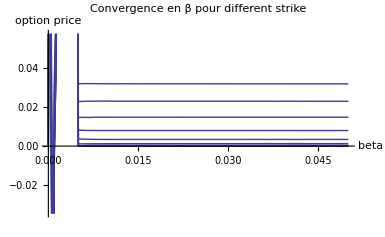
{247.485,-Graphics-}

```mathematica
Timing[Module[{β={-0.1,-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.001,-0.0005,-0.0001,0,0.0001,0.0005,0.001,0.005,0.006,0.007,0.008,0.009,0.01,0.015,0.02,.03,0.04,0.05,0.1},ρ=-0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=Table[0.01 i,{i,2,12}],T=5},res=Table[ShiftedLogHestonNormalCall0[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}];
res1=Table[Interpolation[Transpose[{β,res[[i]]}]],{i,1,Length[res]}];
Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.05,0.05},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}]]]
```

### Implementation integrant une interpolation lineaire

```mathematica
ShiftedLogHestonNormalCall1[β_,ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{βL=0.02},
If[(β<βL)&& (β>=0),
(βL-β)/βL HestonNormalCall[ρ,λv,S0^2 θv,S0 κ,S0^2 V,S0,k,T]+β/βL ShiftedLogHestonNormalCallAux[βL,ρ,λv,θv,κ,V,S0,k,T],
If[(β>-βL)&& (β<0),
(βL-Abs[β])/βL HestonNormalCall[ρ,λv,S0^2 θv,S0 κ,S0^2 V,S0,k,T]+Abs[β]/βL ShiftedLogHestonNormalCallAux[-βL,ρ,λv,θv,κ,V,S0,k,T],
ShiftedLogHestonNormalCallAux[β,ρ,λv,θv,κ,V,S0,k,T]]]]
```

```mathematica
Timing[Module[{β=-0.03,ρ=-0.5,λv=0.15,θv=0.04,κ=1,V=0.04,S0=0.05,k=0.045,T=5},ShiftedLogHestonNormalCallAux[β,ρ,λv,θv,κ,V,S0,k,T]]]
```

{3.61,0.00734534}

### volvol normalisée = 0.25 pour 2 λ θ = 0.3

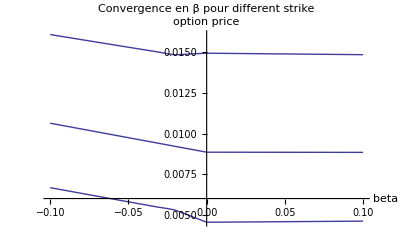
{75.375,-Graphics-}

```mathematica
Timing[Module[{β={-0.1,-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.001,-0.0005,-0.0001,0,0.0001,0.0005,0.001,0.005,0.006,0.007,0.008,0.009,0.01,0.015,0.02,.03,0.04,0.05,0.1},ρ=-0.5,λv=0.15,θv=0.04,κ=0.05,V=0.04,S0=0.05,k=Table[0.01 i,{i,4,6}],T=5},res=Table[ShiftedLogHestonNormalCall1[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}];
res1=Table[Interpolation[Transpose[{β,res[[i]]}]],{i,1,Length[res]}];
Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.1,0.1},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}]]]
```

```mathematica
0.2/√0.04
```

1.

### volvol normalisée = 1 pour 2 λ θ = 0.3

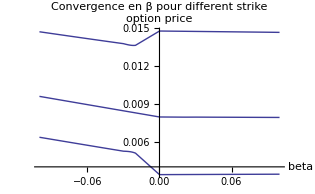
{143.906,-Graphics-}

```mathematica
Timing[Module[{β={-0.1,-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.001,-0.0005,-0.0001,0,0.0001,0.0005,0.001,0.005,0.006,0.007,0.008,0.009,0.01,0.015,0.02,.03,0.04,0.05,0.1},ρ=-0.5,λv=0.15,θv=0.04,κ=0.2,V=0.04,S0=0.05,k=Table[0.01 i,{i,4,6}],T=5},res=Table[ShiftedLogHestonNormalCall1[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}];
res1=Table[Interpolation[Transpose[{β,res[[i]]}]],{i,1,Length[res]}];
Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.1,0.1},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}]]]
```

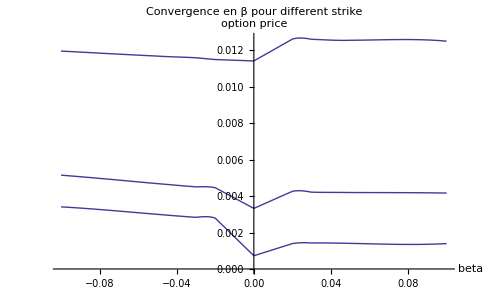
{81.656,-Graphics-}

```mathematica
Timing[Module[{β={-0.1,-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.001,-0.0005,-0.0001,0,0.0001,0.0005,0.001,0.005,0.006,0.007,0.008,0.009,0.01,0.015,0.02,.03,0.04,0.05,0.1},ρ=-0.5,λv=0.15,θv=0.04,κ=1,V=0.04,S0=0.05,k=Table[0.01 i,{i,4,6}],T=5},res=Table[ShiftedLogHestonNormalCall1[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}];
res1=Table[Interpolation[Transpose[{β,res[[i]]}]],{i,1,Length[res]}];
Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.1,0.1},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}]]]
```

### Implementation integrant une interpolation Th

```mathematica
BetaPositifApprox[βini_,βL_,force_]:=βL ⅇ^(-force βini)+(1-βL ⅇ^-force) βini
```

```mathematica
BetaNegatifApprox[βini_,βL_,force_]:=-βL ⅇ^(force βini)+(1-βL ⅇ^-force) βini
```

```mathematica
InterpolDenfer[x_,m_,q_]:=Module[{y,z},
y=2 (1.0-x)^q-1;
z= ArcTanh[y];
1-(Tanh[m z]+1)/2]
```

```mathematica
InterpolDenfer[0.5,2,1]
```

0.5

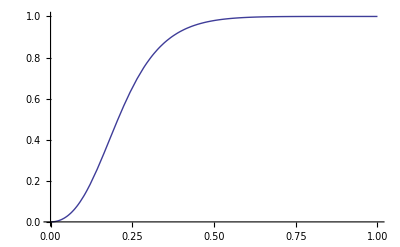

```mathematica
Plot[InterpolDenfer[x,2,3],{x,0,1}]
```

```mathematica
ShiftedLogHestonNormalCallAux[β_,ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{},
LogHestonNormalCall[ρ,λv,β^2 θv,Abs[β] κ,β^2 V,S0+(1-β )/β S0,k+(1-β )/β S0,T]] /; β>=0
```

```mathematica
ShiftedLogHestonNormalCallAux[β_,ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{},
LogHestonNormalCall[-ρ,λv,β^2 θv,Abs[β] κ,β^2 V,S0-(1-β )/β S0,k-(1-β )/β S0,T]] /; β<0
```

```mathematica
ShiftedLogHestonNormalCall2[β_,ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=Module[{βL=0.02,βeff,αN,αLN,force=1,m=2,q=3},
If[ (β>=0),αLN=InterpolDenfer[β,m,q];αN=1-αLN;
βeff=BetaPositifApprox[β,βL,force];
(*Print["β>0 : αLN=",αLN," βeff=",βeff," HestonNormalCall[ρ,λv,S0^2θv,S0 κ,S0^2V,S0,k,T]=", HestonNormalCall[ρ,λv,S0^2 θv,S0 κ,S0^2 V,S0,k,T],"  ShiftedLogHestonNormalCallAux[βeff,ρ,λv,θv,κ,V,S0,k,T]=", ShiftedLogHestonNormalCallAux[βeff,ρ,λv,θv,κ,V,S0,k,T]];*);
αN HestonNormalCall[ρ,λv,S0^2 θv,S0 κ,S0^2 V,S0,k,T]+αLN ShiftedLogHestonNormalCallAux[βeff,ρ,λv,θv,κ,V,S0,k,T],
If[ (β<0),αLN=InterpolDenfer[-β,m,q];αN=1-αLN;
βeff=BetaNegatifApprox[β,βL,force];
(* Print["β<0 : αLN=",αLN," βeff=",βeff];*)
αN HestonNormalCall[ρ,λv,S0^2 θv,S0 κ,S0^2 V,S0,k,T]+αLN ShiftedLogHestonNormalCallAux[βeff,ρ,λv,θv,κ,V,S0,k,T],
ShiftedLogHestonNormalCallAux[β,ρ,λv,θv,κ,V,S0,k,T]]]]
```

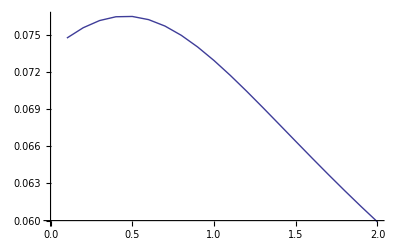

```mathematica
Module[{β=0,ρ=0.5,λv=0.15,θv=1,κ=2,V=1,S0=0.1,k=0.1,T=5,zz},
ListPlot[Table[{κ,ShiftedLogHestonNormalCallAux[β,ρ,λv,θv,κ,V,S0,k,T]},{κ,0.1,2,0.1}],Joined->True]]
```

```mathematica
Module[{β=0.5,ρ=0.5,λv=0.15,θv=1,κ=2,V=1,S0=0.1,k=0.1,T=5},ShiftedLogHestonNormalCall2[β,ρ,λv,θv,κ,V,S0,k,T]]
```

0.0693853

```mathematica
Module[{β=0.7,ρ=0.5,λv=0.15,θv=1,κ=2,V=1,S0=0.1,k=0.1,T=5},ShiftedLogHestonNormalCall2[β,ρ,λv,θv,κ,V,S0,k,T]]
```

0.066208

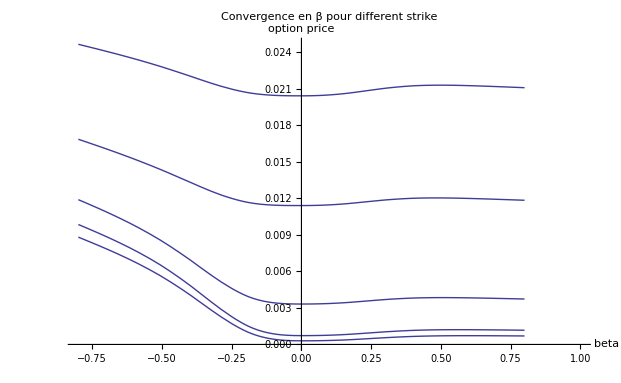
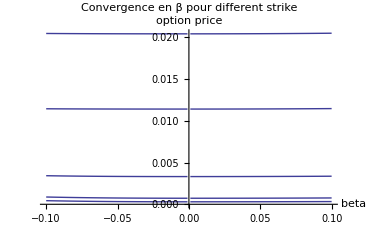
{588.,{-Graphics-,-Graphics-}}

```mathematica
(* q=2,m=2*)Timing[Module[{β={-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.001,-0.0005,-0.0001,0,0.0001,0.0005,0.001,0.005,0.006,0.007,0.008,0.009,0.01,0.015,0.02,.03,0.04,0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1},ρ=-0.5,λv=0.15,θv=0.04,κ=1,V=0.04,S0=0.05,k=Table[0.01 i,{i,3,7}],T=5,res,res1},res=Table[ShiftedLogHestonNormalCall2[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}];
res1=Table[Interpolation[Transpose[{β,res[[i]]}]],{i,1,Length[res]}];
{Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.8,1},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}],
Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.1,0.1},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}]}]]
```

```mathematica
(* q=2,m=2*)Timing[Module[{β={-.01},ρ=0.,λv=0.15,θv=0.04,κ=0.18,V=0.04,S0=0.0372,k=Table[0.0372 i,{i,1,1}],T=5.005479452,res,res1},res=Table[ShiftedLogHestonNormalCall2[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}]]]
```

{1.657,{{0.00608094}}}

```mathematica
(* q=2,m=2*)Timing[Module[{β={-.01},ρ=0.,λv=0.15,θv=0.04,κ=0.22,V=0.04,S0=0.0372,k=Table[0.0372 i,{i,1,1}],T=5.005479452,res,res1},res=Table[ShiftedLogHestonNormalCall2[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}]]]
```

{1.984,{{0.00587515}}}

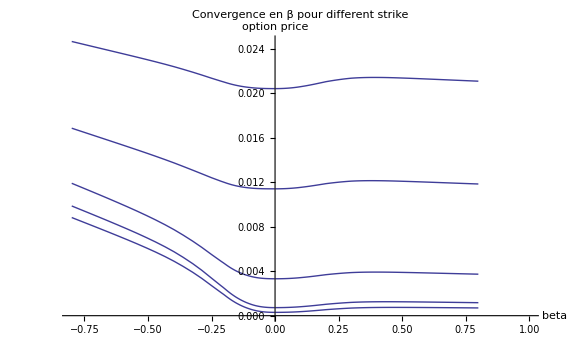
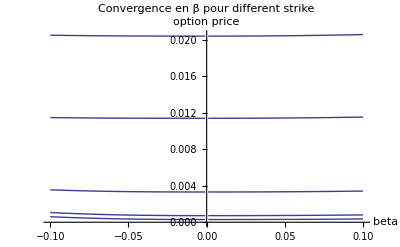
{603.531,{-Graphics-,-Graphics-}}

```mathematica
(* q=2,m=2*)Timing[Module[{β={-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.001,-0.0005,-0.0001,0,0.0001,0.0005,0.001,0.005,0.006,0.007,0.008,0.009,0.01,0.015,0.02,.03,0.04,0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1},ρ=-0.5,λv=0.15,θv=0.04,κ=1,V=0.04,S0=0.05,k=Table[0.01 i,{i,3,7}],T=5,res,res1},res=Table[ShiftedLogHestonNormalCall2[β[[j]],ρ,λv,θv,κ,V,S0,k[[i]],T],{i,1,Length[k]},{j,1,Length[β]}];
res1=Table[Interpolation[Transpose[{β,res[[i]]}]],{i,1,Length[res]}];
{Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.8,1},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}],
Plot[Table[res1[[i]][x],{i,1,Length[res1]}],{x,-0.1,0.1},PlotLabel->"Convergence en β pour different strike",AxesLabel->{"beta","option price"}]}]]
```

```mathematica
D[InterpolDenfer[x,m,q],x]
```

(m q x^(-1+q) Sech[m ArcTanh[1-2 x^q]]^2)/(1-(1-2 x^q)^2)

```mathematica
DInterpolDenfer[x_,m_,q_]:=(m q x^(-1+q) Sech[m ArcTanh[1-2 x^q]]^2)/(1-(1-2 x^q)^2)
```

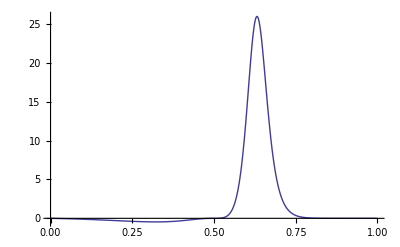

```mathematica
Module[{m=2,q=2},Plot[DInterpolDenfer[x,m,q],{x,0,1},PlotRange->All]]
```

## Moments d'un LogNormal Heston et power option 1,2,3D

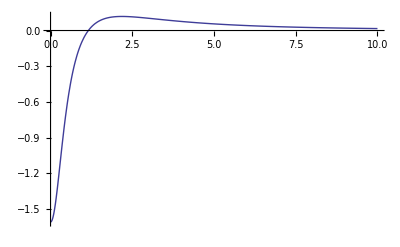
{0.156,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.1,λv=0.15,θv=0.01,κ=2,V=0.01,S0=1,λ1=2.5,T=10,k=1,n=2,ω,λ=2.5},
Plot[LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,n,T,ω +λ ⅈ],{ω,0,10},PlotRange->All]
]]
```

### Implementation mathematica de reference

```mathematica
PowerLogHestonNormalCallN[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,n,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
PowerLogHestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,n,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
PowerLogHestonNormalCallN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,n,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
PowerLogHestonNormalPutN[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,n,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
PowerLogHestonNormalPutN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,n,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
PowerLogHestonNormalPutN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
NIntegrate[LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,n,T,ω +λ ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
LogHestonNormalVarianceN[ρ_,λv_,θv_,κ_,V_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCallN[ρ,λv,θv,κ,V,S0,S0^2,2,T];
put=PowerLogHestonNormalPutN[ρ,λv,θv,κ,V,S0,S0^2,2,T];
call-put
]
```

```mathematica
LogHestonNormalVarianceN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCallN[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,S0^2,2,T];
put=PowerLogHestonNormalPutN[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,S0^2,2,T];
call-put
]
```

```mathematica
LogHestonNormalVarianceN[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCallN[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,S0^2,2,T];
put=PowerLogHestonNormalPutN[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,S0^2,2,T];
call-put
]
```

### Implementation Operationnelle

```mathematica
PowerLogHestonNormalCallAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,n,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
PowerLogHestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,n,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
PowerLogHestonNormalCallAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=n+0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,n,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
PowerLogHestonNormalPutAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,n,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
PowerLogHestonNormalPutAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,k,1,n,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
PowerLogHestonNormalPutAux[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,n_,T_]:=S0^n-1/π Re[Module[{λ=-0.5,ω},
AdaptativeIntegrate[Function[ω,LogNormalHestonCallIntegrand[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,k,1,n,T,ω +λ ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],
10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

### Implementation Normalisée

```mathematica
PowerLogHestonNormalCall[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=Module[{},
S0^n PowerLogHestonNormalCallAux[ρ,λv,θv,κ,V,1,k/S0^n,n,T]
]
```

```mathematica
PowerLogHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,n_,T_]:=Module[{},
S0^n PowerLogHestonNormalCallAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,1,k/S0^n,n,T]
]
```

```mathematica
PowerLogHestonNormalCall[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,n_,T_]:=Module[{},
S0^n PowerLogHestonNormalCallAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,1,k/S0^n,n,T]
]
```

```mathematica
PowerLogHestonNormalPut[ρ_,λv_,θv_,κ_,V_,S0_,k_,n_,T_]:=Module[{},
S0^n PowerLogHestonNormalPutAux[ρ,λv,θv,κ,V,1,k/S0^n,n,T]
]
```

```mathematica
PowerLogHestonNormalPut[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,k_,n_,T_]:=Module[{},
S0^n PowerLogHestonNormalPutAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,1,k/S0^n,n,T]
]
```

```mathematica
PowerLogHestonNormalPut[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,k_,n_,T_]:=Module[{},
S0^n PowerLogHestonNormalPutAux[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,1,k/S0^n,n,T]
]
```

```mathematica
LogHestonNormalVariance[ρ_,λv_,θv_,κ_,V_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCall[ρ,λv,θv,κ,V,S0,S0^2,2,T];
put=PowerLogHestonNormalPut[ρ,λv,θv,κ,V,S0,S0^2,2,T];
call-put
]
```

```mathematica
LogHestonNormalVariance[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,S0^2,2,T];
put=PowerLogHestonNormalPut[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,S0^2,2,T];
call-put
]
```

```mathematica
LogHestonNormalVariance[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,S0^2,2,T];
put=PowerLogHestonNormalPut[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,S0^2,2,T];
call-put
]
```

```mathematica
LogHestonNormalVarianceTrace[ρ_,λv_,θv_,κ_,V_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCall[ρ,λv,θv,κ,V,S0,S0^2,2,T];
put=PowerLogHestonNormalPut[ρ,λv,θv,κ,V,S0,S0^2,2,T];
Print["call=",call," put=",put];
call-put
]
```

```mathematica
LogHestonNormalVarianceTrace[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,S0^2,2,T];
put=PowerLogHestonNormalPut[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,S0,S0^2,2,T];
Print["call=",call," put=",put];
call-put
]
```

```mathematica
LogHestonNormalVarianceTrace[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,S0_,T_]:=Module[{call,put},
call=PowerLogHestonNormalCall[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,S0^2,2,T];
put=PowerLogHestonNormalPut[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,S0,S0^2,2,T];
Print["call=",call," put=",put];
call-put
]
```

```mathematica
Timing[Module[{ρ=-0.1,λv=0.15,θv=0.1,κ=2,V=0.1,S0=1,λ1=2.5,T=10,k=1,n=2,ω,λ=2.5},
{PowerLogHestonNormalCallN[ρ,λv,θv,κ,V,S0,k,n,T],PowerLogHestonNormalCall[ρ,λv,θv,κ,V,S0,k,n,T]}]]
```

{4.852,{1.22924,1.22924}}

```mathematica
Timing[Module[{ρ=-0.1,λv=0.15,θv=0.1,κ=2,V=0.1,S0=1,λ1=2.5,T=10,k=1,n=2,ω,λ=2.5},
{PowerLogHestonNormalPutN[ρ,λv,θv,κ,V,S0,k,n,T],PowerLogHestonNormalPut[ρ,λv,θv,κ,V,S0,k,n,T]}]]
```

{5.296,{1.1534,1.1534}}

#### Exemple de calcul de variance

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.05,κ=1.5,V=1,S0=0.04,T=1},
{LogHestonNormalVariance[ρ,λv,θv,κ,V,S0,T],S0^2 V T}]]
```

{0.078,{0.00554081,0.0016}}

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.05,κ=0.1,V=0.05,S0=0.04,T=5},
{LogHestonNormalVariance[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,T],S0^2 V T}]]
```

{0.063,{-0.000609768,0.0004}}

#### Exemple de l'evolution de la volatilité moyenne

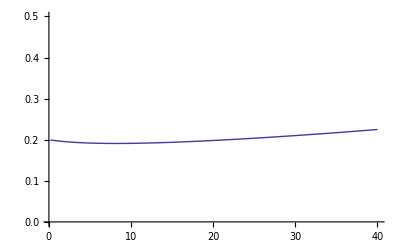
{12.89,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.04,κ=0.1,V=0.04,S0=1},
ListPlot[{#,√(LogHestonNormalVariance[ρ,λv,θv,κ,V,S0,#]/(S0 S0 #))}& /@ Table[i/5,{i,1,200}],Joined->True ,PlotRange->{0,0.5}]]]
```

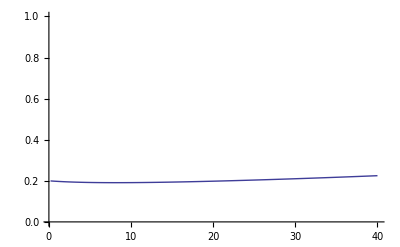
{19.672,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.02,κ=0.1,V=0.02,S0=1},
ListPlot[{#,√(LogHestonNormalVariance[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,#]/(S0 S0 #))}& /@ Table[i/5,{i,1,200}],Joined->True ,PlotRange->{0,1}]]]
```

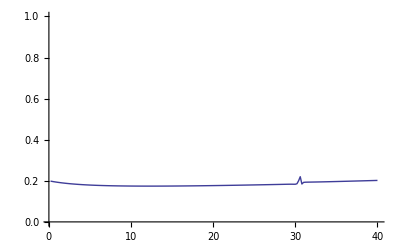
{26.953,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.02,κ=0.2,V=0.02,S0=1},
ListPlot[{#,√(LogHestonNormalVariance[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,#]/(S0 S0 #))}& /@ Table[i/5,{i,1,200}],Joined->True ,PlotRange->{0,1}]]]
```

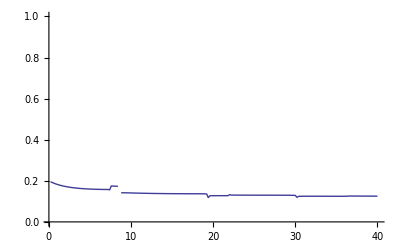
{46.531,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.5,λv=0.15,θv=0.02,κ=0.5,V=0.02,S0=1},
ListPlot[{#,√(LogHestonNormalVariance[ρ,λv,θv,κ,V,ρ,λv,θv,κ,V,S0,#]/(S0 S0 #))}& /@ Table[i/5,{i,1,200}],Joined->True ,PlotRange->{0,1}]]]
```

#### Cassage de gueule a 40 ans !

```mathematica
Timing[Module[{ρ=0.,λv=0.15,θv=0.04,κ=0.1,V=0.04,S0=1,T=40},
PowerLogHestonNormalCall[ρ,λv,θv,κ,V,S0,S0^2,2,T]]]
```

{0.016,-4.70278×10^7}

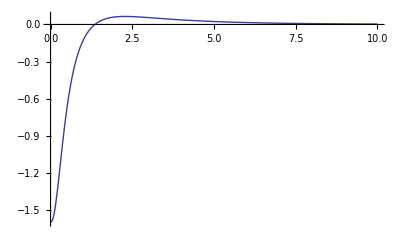
{0.094,-Graphics-}

```mathematica
Timing[Module[{ρ=-0.1,λv=0.15,θv=0.05,κ=2,V=0.05,S0=1,λ1=2.5,T=40,k=1,n=2,ω,λ=-.5},
Plot[LogNormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,n,T,ω +λ ⅈ],{ω,0,10},PlotRange->All]
]]
```

## Spreadoption dans BiSuperHeston

## Determinations des moments liés au normal Heston

```mathematica
NormalHestonFondamentalTransform[ρ_,λv_,θv_,κ_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ},
ζ=√((λv+ρ κ ⅈ ω)^2+κ^2( ω^2));
ψp =-(λv+ρ κ  ⅈ ω)+ζ;
ψm =(λv+ρ κ  ⅈ ω)+ζ;
A=-(θv λv (τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/κ^2;
B=(-( ω^2)(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
ⅇ^(A+B V)]
```

```mathematica
LogaritmOfNormalHestonFondamentalTransform[ρ_,λv_,θv_,κ_,V_,ω_,τ_]:=Module[{ζ,ψp ,ψm,A,B,argζ},
ζ=√((λv+ρ κ ⅈ ω)^2+κ^2( ω^2));
ψp =-(λv+ρ κ  ⅈ ω)+ζ;
ψm =(λv+ρ κ  ⅈ ω)+ζ;
A=-(θv λv (τ ψp+2 Log[(ψm+ⅇ^(-ζ τ) ψp)/(2ζ)]))/κ^2;
B=(-( ω^2)(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
A+B V]
```

```mathematica
D2=D[LogaritmOfNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,ω,τ],{ω,2}];
D2LogNormalHestonFondamentalTransform=Function[{ρ,λv,θv,κ,V,τ},Evaluate[1/ⅈ^2 D2/. ω->0]];
```

```mathematica
D2LogNormalHestonFondamentalTransform=Function[{ρ,λv,θv,κ,V,τ},Evaluate[Simplify[D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ]]]];
```

```mathematica
Module[{ρ=0.5,λv=0.15,θv=0.04,κ=0.2,V=0.01,ω=0,τ=30},
{
D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ]}
]
```

{1.00222}

```mathematica
D2LogNormalHestonFondamentalTransform=Function[{ρ,λv,θv,κ,V,τ},Evaluate[Simplify[D2LogNormalHestonFondamentalTransform[ρ,λv,θv,κ,V,τ]]]];
```

## Determinations des moments liés au BiSuperHeston

```mathematica
LogBiSuperLogNormalHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,α2_,β2_,Z1_,Z2_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,A1,ζ2,ψp2 ,ψm2,A2,ζ3,ψp3 ,ψm3,A3,c},
ζ1=√((λv1+ρ1 κ1 ⅈ Z1)^2+κ1^2( Z1^2-ⅈ Z1));
ψp1 =-(λv1+ρ1 κ1 ⅈ Z1)+ζ1;
ψm1 =(λv1+ρ1 κ1  ⅈ Z1)+ζ1;
A1=(-( Z1^2-ⅈ Z1)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
ζ2=√((λv2+ρ2 κ2 ⅈ (Z1 α2+Z2 β2))^2+κ2^2( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2));
ψp2 =-(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
ψm2 =(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
A2=(-( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
ζ3=√((λv3+ρ3 κ3 ⅈ Z2)^2+κ3^2( Z2^2-ⅈ Z2));
ψp3 =-(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
ψm3 =(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
A3=(-( Z2^2-ⅈ Z2)(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));

c=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2;
c+A1 V1+A2 V2+A3 V3]
```

```mathematica
Clear[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ]
```

```mathematica
D1X=D[LogBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ],Z1];
D1XBiSuperLogNormalHestonFondamentalTransform=Function[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ},Evaluate[Simplify[1/ⅈ D1X /.{Z1->0,Z2->0},λv1>0&&λv2>0&&λv3>0]]];
```

```mathematica
D1Y=D[LogBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ],Z2];
D1YBiSuperLogNormalHestonFondamentalTransform=Function[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ},Evaluate[Simplify[1/ⅈ D1Y/.{Z1->0,Z2->0},λv1>0&&λv2>0&&λv3>0]]];
```

```mathematica
D2XX=D[LogBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ],{Z1,2}];
D2XXBiSuperLogNormalHestonFondamentalTransform=Function[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ},Evaluate[Simplify[1/ⅈ^2 D2XX/.{Z1->0,Z2->0},λv1>0&&λv2>0&&λv3>0]]];
```

```mathematica
D2YY=D[LogBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ],{Z2,2}];
D2YYBiSuperLogNormalHestonFondamentalTransform=Function[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ},Evaluate[Simplify[1/ⅈ^2 D2YY/.{Z1->0,Z2->0},λv1>0&&λv2>0&&λv3>0]]];
```

```mathematica
D2XY=D[LogBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,Z1,Z2,τ],Z1,Z2];
D2XYBiSuperLogNormalHestonFondamentalTransform=Function[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ},Evaluate[Simplify[1/ⅈ^2 D2XY/.{Z1->0,Z2->0},λv1>0&&λv2>0&&λv3>0]]];
```

## Determination de la variance exacte du normal Heston

```mathematica
Simplify[D2LogNormalHestonFondamentalTransform[ρS,λS,θS,κS,VS,T],λS>0]
```

(VS-ⅇ^(-T λS) VS+θS (-1+ⅇ^(-T λS)+T λS))/λS

```mathematica
Solve [(VS-ⅇ^(-T λS) VS+VS LTfac (-1+ⅇ^(-T λS)+T λS))/λS==VarSpread,VS]
```

{{VS→(ⅇ^(T λS) VarSpread λS)/(-1+ⅇ^(T λS)+LTfac-ⅇ^(T λS) LTfac+ⅇ^(T λS) LTfac T λS)}}

#### Signification des dimensions

{Underlying1, Underlying2, Underlying3, VarianceUnder1, VarianceUnder2, VarianceUnder3}

## Projection du generateur de Bisuperheston sur les generateurs Normalheston

### 1) BiSuperheston

```mathematica
Corr={
{1,0,0,rho1,0,0},
{0,1,0,0,rho2,0},
{0,0,1,0,0,rho3},
{rho1,0,0,1,0,0},
{0,rho2,0,0,1,0},
{0,0,rho3,0,0,1}
};
```

```mathematica
Mch=Eigensystem[Corr] [[2]]
```

{{-1,0,0,1,0,0},{1,0,0,1,0,0},{0,-1,0,0,1,0},{0,1,0,0,1,0},{0,0,-1,0,0,1},{0,0,1,0,0,1}}

```mathematica
Eigens=Eigensystem[Corr] [[1]]
```

{1-rho1,1+rho1,1-rho2,1+rho2,1-rho3,1+rho3}

```mathematica
Mch //MatrixForm
```

(-1 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0
0 | -1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | -1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1)

```mathematica
Clear[S1,S2,V1,V2,V3]
```

```mathematica
Diff[x_]:=
D[x,S1]{√V1 S1,alpha2 √V2 S1,0,0,0,0}+
D[x,S2]{0,beta2 √V2 S2,√V3 S2,0,0,0}+
D[x,V1]{0,0,0,kappaV1 √V1,0,0}+
D[x,V2]{0,0,0,0,kappaV2 √V2,0}+
D[x,V3]{0,0,0,0,0,kappaV3 √V3}
```

```mathematica
Diff[S1].Diff[S1]
```

S1^2 V1+alpha2^2 S1^2 V2

```mathematica
VS=Simplify[Diff[S1-S2].(Corr.Diff[S1-S2])]
```

S1^2 V1+(alpha2 S1-beta2 S2)^2 V2+S2^2 V3

```mathematica
Drift[x_]:=1/2(D[x,S1,S1](Diff[S1].Diff[S1])+D[x,S1,S2](Diff[S1].Diff[S2])+D[x,S2,S2](Diff[S2].Diff[S2])+D[x,V1,V1](Diff[V1].Diff[V1])+D[x,V2,V2](Diff[V2].Diff[V2])+D[x,V3,V3](Diff[V3].Diff[V3]))
```

```mathematica
DiffVS=Diff[VS]
```

{S1 √V1 (2 S1 V1+2 alpha2 (alpha2 S1-beta2 S2) V2),alpha2 S1 √V2 (2 S1 V1+2 alpha2 (alpha2 S1-beta2 S2) V2)+beta2 S2 √V2 (-2 beta2 (alpha2 S1-beta2 S2) V2+2 S2 V3),S2 √V3 (-2 beta2 (alpha2 S1-beta2 S2) V2+2 S2 V3),kappaV1 S1^2 √V1,kappaV2 (alpha2 S1-beta2 S2)^2 √V2,kappaV3 S2^2 √V3}

```mathematica
DiffVS //MatrixForm
```

(S1 √V1 (2 S1 V1+2 alpha2 (alpha2 S1-beta2 S2) V2)
alpha2 S1 √V2 (2 S1 V1+2 alpha2 (alpha2 S1-beta2 S2) V2)+beta2 S2 √V2 (-2 beta2 (alpha2 S1-beta2 S2) V2+2 S2 V3)
S2 √V3 (-2 beta2 (alpha2 S1-beta2 S2) V2+2 S2 V3)
kappaV1 S1^2 √V1
kappaV2 (alpha2 S1-beta2 S2)^2 √V2
kappaV3 S2^2 √V3)

```mathematica
VarVS=Simplify[Diff[VS].(Corr.Diff[VS])]
```

S1^2 V1 (kappaV1 rho1 S1+2 S1 V1+2 alpha2 (alpha2 S1-beta2 S2) V2) (-2 alpha2 beta2 S2 V2+2 S1 (V1+alpha2^2 V2))+kappaV1 S1^3 V1 (kappaV1 S1+2 rho1 (-alpha2 beta2 S2 V2+S1 (V1+alpha2^2 V2)))+2 S2^2 V3 (-alpha2 beta2 S1 V2+S2 (beta2^2 V2+V3)) (kappaV3 rho3 S2-2 alpha2 beta2 S1 V2+2 S2 (beta2^2 V2+V3))+kappaV3 S2^3 V3 (kappaV3 S2+2 rho3 (-alpha2 beta2 S1 V2+S2 (beta2^2 V2+V3)))+V2 (2 alpha2 S1 (-alpha2 beta2 S2 V2+S1 (V1+alpha2^2 V2))+2 beta2 S2 (-alpha2 beta2 S1 V2+S2 (beta2^2 V2+V3))) (kappaV2 rho2 (alpha2 S1-beta2 S2)^2+2 alpha2 S1 (-alpha2 beta2 S2 V2+S1 (V1+alpha2^2 V2))+2 beta2 S2 (-alpha2 beta2 S1 V2+S2 (beta2^2 V2+V3)))+kappaV2 (alpha2 S1-beta2 S2)^2 V2 (kappaV2 (alpha2 S1-beta2 S2)^2+rho2 (2 alpha2 S1 (-alpha2 beta2 S2 V2+S1 (V1+alpha2^2 V2))+2 beta2 S2 (-alpha2 beta2 S1 V2+S2 (beta2^2 V2+V3))))

```mathematica
Simplify[VarVS-(VarVS /.{kappaV1->0,kappaV2->0,kappaV3->0})]
```

kappaV1^2 S1^4 V1+4 alpha2^5 kappaV2 rho2 S1^4 V2^2+alpha2^4 kappaV2 S1^3 V2 (kappaV2 S1-12 beta2 rho2 S2 V2)-4 alpha2^3 kappaV2 S1^2 V2 (beta2 kappaV2 S1 S2-rho2 S1^2 V1+beta2^2 rho2 (S1-3 S2) S2 V2)+4 kappaV1 rho1 S1^3 V1 (-alpha2 beta2 S2 V2+S1 (V1+alpha2^2 V2))+S2^4 (beta2^4 kappaV2^2 V2+4 beta2^5 kappaV2 rho2 V2^2+4 beta2^3 kappaV2 rho2 V2 V3+4 beta2^2 kappaV3 rho3 V2 V3+kappaV3 V3 (kappaV3+4 rho3 V3))+2 alpha2^2 beta2 kappaV2 S1 S2 V2 (3 beta2 kappaV2 S1 S2+2 beta2^2 rho2 (3 S1-S2) S2 V2+2 rho2 S1 (-2 S1 V1+S2 V3))-4 alpha2 beta2 S1 S2^2 V2 (beta2^2 kappaV2^2 S2+3 beta2^3 kappaV2 rho2 S2 V2+kappaV3 rho3 S2 V3+beta2 kappaV2 rho2 (-S1 V1+2 S2 V3))

```mathematica
CoVarSVS=Simplify[Diff[VS].(Corr.Diff[S1-S2])]
```

kappaV1 rho1 S1^3 V1+kappaV2 rho2 (alpha2 S1-beta2 S2)^3 V2+2 S1^2 V1 (-alpha2 beta2 S2 V2+S1 (V1+alpha2^2 V2))-kappaV3 rho3 S2^3 V3-2 S2^2 V3 (-alpha2 beta2 S1 V2+S2 (beta2^2 V2+V3))+(alpha2 S1-beta2 S2) V2 (2 alpha2 S1 (-alpha2 beta2 S2 V2+S1 (V1+alpha2^2 V2))+2 beta2 S2 (-alpha2 beta2 S1 V2+S2 (beta2^2 V2+V3)))

```mathematica
Simplify[CoVarSVS-(CoVarSVS /.{kappaV1->0,kappaV2->0,kappaV3->0})]
```

kappaV1 rho1 S1^3 V1+kappaV2 rho2 (alpha2 S1-beta2 S2)^3 V2-kappaV3 rho3 S2^3 V3

Que l' on identifie avec les meme calculs fait avec normal heston :

```mathematica
BiSuperHestonSpreadObservable[S1_,S2_,alpha2_,beta2_,rho1_,kappaV1_,V1_,rho2_,kappaV2_,V2_,rho3_,kappaV3_,V3_]:={
S1^2 V1+(alpha2 S1-beta2 S2)^2 V2+S2^2 V3,
kappaV1^2 S1^4 V1+
4 alpha2^5 kappaV2 rho2 S1^4 V2^2+
alpha2^4 kappaV2 S1^3 V2 (kappaV2 S1-12 beta2 rho2 S2 V2)-4 alpha2^3 kappaV2 S1^2 V2 (beta2 kappaV2 S1 S2-rho2 S1^2 V1+beta2^2 rho2 (S1-3 S2) S2 V2)+4 kappaV1 rho1 S1^3 V1 (-alpha2 beta2 S2 V2+S1 (V1+alpha2^2 V2))+S2^4 (beta2^4 kappaV2^2 V2+4 beta2^5 kappaV2 rho2 V2^2+4 beta2^3 kappaV2 rho2 V2 V3+4 beta2^2 kappaV3 rho3 V2 V3+kappaV3 V3 (kappaV3+4 rho3 V3))+2 alpha2^2 beta2 kappaV2 S1 S2 V2 (3 beta2 kappaV2 S1 S2+2 beta2^2 rho2 (3 S1-S2) S2 V2+2 rho2 S1 (-2 S1 V1+S2 V3))-4 alpha2 beta2 S1 S2^2 V2 (beta2^2 kappaV2^2 S2+3 beta2^3 kappaV2 rho2 S2 V2+kappaV3 rho3 S2 V3+beta2 kappaV2 rho2 (-S1 V1+2 S2 V3)),
kappaV1 rho1 S1^3 V1+kappaV2 rho2 (alpha2 S1-beta2 S2)^3 V2-kappaV3 rho3 S2^3 V3
}
```

```mathematica
CForm[kappaV1^2 S1^4 V1+
4 alpha2^5 kappaV2 rho2 S1^4 V2^2+
alpha2^4 kappaV2 S1^3 V2 (kappaV2 S1-12 beta2 rho2 S2 V2)-4 alpha2^3 kappaV2 S1^2 V2 (beta2 kappaV2 S1 S2-rho2 S1^2 V1+beta2^2 rho2 (S1-3 S2) S2 V2)+4 kappaV1 rho1 S1^3 V1 (-alpha2 beta2 S2 V2+S1 (V1+alpha2^2 V2))+S2^4 (beta2^4 kappaV2^2 V2+4 beta2^5 kappaV2 rho2 V2^2+4 beta2^3 kappaV2 rho2 V2 V3+4 beta2^2 kappaV3 rho3 V2 V3+kappaV3 V3 (kappaV3+4 rho3 V3))+2 alpha2^2 beta2 kappaV2 S1 S2 V2 (3 beta2 kappaV2 S1 S2+2 beta2^2 rho2 (3 S1-S2) S2 V2+2 rho2 S1 (-2 S1 V1+S2 V3))-4 alpha2 beta2 S1 S2^2 V2 (beta2^2 kappaV2^2 S2+3 beta2^3 kappaV2 rho2 S2 V2+kappaV3 rho3 S2 V3+beta2 kappaV2 rho2 (-S1 V1+2 S2 V3))]
```

Power(kappaV1,2)*Power(S1,4)*V1 + 4*Power(alpha2,5)*kappaV2*rho2*Power(S1,4)*Power(V2,2) + 
   Power(alpha2,4)*kappaV2*Power(S1,3)*V2*(kappaV2*S1 - 12*beta2*rho2*S2*V2) - 
   4*Power(alpha2,3)*kappaV2*Power(S1,2)*V2*
    (beta2*kappaV2*S1*S2 - rho2*Power(S1,2)*V1 + Power(beta2,2)*rho2*(S1 - 3*S2)*S2*V2) + 
   4*kappaV1*rho1*Power(S1,3)*V1*(-(alpha2*beta2*S2*V2) + S1*(V1 + Power(alpha2,2)*V2)) + 
   Power(S2,4)*(Power(beta2,4)*Power(kappaV2,2)*V2 + 4*Power(beta2,5)*kappaV2*rho2*Power(V2,2) + 
      4*Power(beta2,3)*kappaV2*rho2*V2*V3 + 4*Power(beta2,2)*kappaV3*rho3*V2*V3 + 
      kappaV3*V3*(kappaV3 + 4*rho3*V3)) + 2*Power(alpha2,2)*beta2*kappaV2*S1*S2*V2*
    (3*beta2*kappaV2*S1*S2 + 2*Power(beta2,2)*rho2*(3*S1 - S2)*S2*V2 + 2*rho2*S1*(-2*S1*V1 + S2*V3)) - 
   4*alpha2*beta2*S1*Power(S2,2)*V2*(Power(beta2,2)*Power(kappaV2,2)*S2 + 
      3*Power(beta2,3)*kappaV2*rho2*S2*V2 + kappaV3*rho3*S2*V3 + beta2*kappaV2*rho2*(-(S1*V1) + 2*S2*V3))

### Normal Heston

```mathematica
CovNH={
{1,ρ},
{ρ,1}
};
```

```mathematica
DiffNH[x_]:=D[x,S]{√v,0}+
D[x,v]{0,ν √v }
```

```mathematica
VSNH=Simplify[DiffNH[S].(CovNH.DiffNH[S])]
```

v

```mathematica
VarVSNH=Simplify[DiffNH[VSNH].(CovNH.DiffNH[VSNH])]
```

v ν^2

```mathematica
CoVarSVS=Simplify[DiffNH[VSNH].(CovNH.DiffNH[S])]
```

v ν ρ

ce qui permet d' extraire les parametres utiles :

v = VSNH

ν^2=VarVSNH/v=VarVSNH/VSNH

ρ=CoVarSVS/(v ν)=CoVarSVS/VarVSNH

### BiLog

```mathematica
CovBL={
{1,ρ},
{ρ,1}
};
```

```mathematica
DiffBL[x_]:=D[x,S1]{√V1 S1,0}+
D[x,S2]{0,√V2 S2 }
```

```mathematica
VSBL=Simplify[DiffBL[S1-S2].(CovBL.DiffBL[S1-S2])]
```

S1^2 V1+S2^2 V2-2 S1 S2 √V1 √V2 ρ

```mathematica
VarVSBL=Simplify[DiffBL[VSBL].(CovBL.DiffBL[VSBL])]
```

4 (S1^4 V1^3+S2^4 V2^3-2 S1 S2^3 √V1 V2^2 ρ (√V2+√V1 ρ)-2 S1^3 S2 (V1^(5/2) √V2 ρ+V1^2 V2 ρ^2)+S1^2 S2^2 V1 V2 ρ (V1 ρ+V2 ρ+2 √V1 √V2 (1+ρ^2)))

```mathematica
CoVarSVSBL=Simplify[DiffBL[VSBL].(CovBL.DiffBL[S1-S2])]
```

2 (S1^3 V1^2-S2^3 V2^2+S1 S2^2 √V1 V2 ρ (2 √V2+√V1 ρ)-S1^2 S2 (2 V1^(3/2) √V2 ρ+V1 V2 ρ^2))

```mathematica
Simplify[VarVS/. {kappaV1->0,kappaV2->0,kappaV3->0,alpha2->1,beta2->1,V3->0,V1->0}]
```

4 (S1-S2)^4 V2^3

```mathematica
Simplify[VarVSBL/.{V1->V2,ρ->1}]
```

4 (S1-S2)^4 V2^3

### On verifie que on degenere bien en bilog

```mathematica
Simplify[VarVS//. {beta2->((1+ρ)√VS2)/2,alpha2->(2ρ)/(1+ρ)√VS1,V1->VS1-alpha2^2,V3->VS2-beta2^2,V2->1,kappaV1->0,kappaV2->0,kappaV3->0}]
```

4 (S1^4 VS1^3+S2^4 VS2^3-2 S1 S2^3 √VS1 VS2^2 ρ (√VS2+√VS1 ρ)-2 S1^3 S2 (VS1^(5/2) √VS2 ρ+VS1^2 VS2 ρ^2)+S1^2 S2^2 VS1 VS2 ρ (VS1 ρ+VS2 ρ+2 √VS1 √VS2 (1+ρ^2)))

```mathematica
VarVSBL
```

4 (S1^4 V1^3+S2^4 V2^3-2 S1 S2^3 √V1 V2^2 ρ (√V2+√V1 ρ)-2 S1^3 S2 (V1^(5/2) √V2 ρ+V1^2 V2 ρ^2)+S1^2 S2^2 V1 V2 ρ (V1 ρ+V2 ρ+2 √V1 √V2 (1+ρ^2)))

```mathematica
BiLogVarVsCoVar[S1_,S2_,V1_,V2_,ρ_]:={4 (S1^4 V1^3+S2^4 V2^3-2 S1 S2^3 √V1 V2^2 ρ (√V2+√V1 ρ)-2 S1^3 S2 (V1^(5/2) √V2 ρ+V1^2 V2 ρ^2)+S1^2 S2^2 V1 V2 ρ (V1 ρ+V2 ρ+2 √V1 √V2 (1+ρ^2))),2 (S1^3 V1^2-S2^3 V2^2+S1 S2^2 √V1 V2 ρ (2 √V2+√V1 ρ)-S1^2 S2 (2 V1^(3/2) √V2 ρ+V1 V2 ρ^2))}
```

### Shifted Normal Heston

```mathematica
dS=(1+ϵ S)√v dW
```

```mathematica
CovNH={
{1,ρ},
{ρ,1}
};
```

```mathematica
DiffNH[x_]:=D[x,S]{(1+ϵ S)√v,0}+D[x,v]{0,ν √v }
```

```mathematica
VSNH=Simplify[DiffNH[S].(CovNH.DiffNH[S])]
```

v (1+S ϵ)^2

on approxime par :

VSNH = v + 2 ϵ S

donc

v = VSNH - 2 ϵ S

```mathematica
CoVarSVS=Simplify[DiffNH[VSNH].(CovNH.DiffNH[S])]
```

v (1+S ϵ)^3 (2 v ϵ+ν ρ)

```mathematica
Normal[Series[CoVarSVS,{ϵ,0,1}]]
```

v ν ρ+ϵ (2 v^2+3 S v ν ρ)

donc on approxime

CoVarSVS=v ν ρ+ϵ (2 v^2+3 S v ν ρ)=v ν ρ+ϵ(2 VSNH^2+3S CoVarSVS)

ce qui permet de resoudre :

CoVarSVS-v ν ρ-ϵ(2 VSNH^2+3S CoVarSVS)=0

CoVarSVS=(v ν ρ+2ϵ VSNH^2)/(1-3S ϵ)=v ν ρ+(2 VSNH^2-3S v ν ρ)ϵ=v ν ρ(1-3ϵ S)+2 ϵ VSNH^2

donc

v ν ρ=(CoVarSVS-2ϵ VSNH^2)/(1-3ϵ S)

```mathematica
VarVSNH=Simplify[DiffNH[VSNH].(CovNH.DiffNH[VSNH])]
```

v (1+S ϵ)^4 (4 v^2 ϵ^2+ν^2+4 v ϵ ν ρ)

```mathematica
Normal[Series[VarVSNH,{ϵ,0,1}]]
```

v ν^2+ϵ (4 S v ν^2+4 v^2 ν ρ)

donc on approxime

VarVSNH=v ν^2+ϵ (4 S v ν^2+4 v^2 ν ρ)=v ν^2+ϵ (4 S VarVSNH+4 v CoVarSVS)

que l' on resoud

VarVSNH(1-ϵ 4 S)=v ν^2+ϵ 4 v CoVarSVS

donc

v ν^2=VarVSNH(1-ϵ 4 S)-ϵ 4 v CoVarSVS

en resumé

```mathematica
v=VSNH-2ϵ S
v ν ρ=(CoVarSVS-2ϵ VSNH^2)/(1-3ϵ S)
v ν^2=VarVSNH(1-ϵ 4 S)-ϵ 4 v CoVarSVS
```

```mathematica
desirant fixer un effet de decalage on calcule la vol de la covariance
```

```mathematica
VarCoVarSVS=Simplify[DiffNH[CoVarSVS].(CovNH.DiffNH[CoVarSVS])]
```

v (1+S ϵ)^6 (36 v^4 ϵ^4+84 v^3 ϵ^3 ν ρ+ν^4 ρ^2+2 v ϵ ν^3 ρ (4+3 ρ^2)+v^2 ϵ^2 ν^2 (16+45 ρ^2))

```mathematica
Normal[Series[VarCoVarSVS,{ϵ,0,1}]]
```

v ν^4 ρ^2+ϵ (8 v^2 ν^3 ρ+6 S v ν^4 ρ^2+6 v^2 ν^3 ρ^3)

VarCoVarSVS=v ν^4 ρ^2+ϵ (8 v^2 ν^3 ρ+6 S v ν^4 ρ^2+6 v^2 ν^3 ρ^3)

donc

VarCoVarSVS=1/v^2((CoVarSVS-2ϵ VSNH^2)/(1-3ϵ S))^2(VarVSNH(1-ϵ 4 S)-ϵ 4 v CoVarSVS)+ϵ(8 CoVarSVS VarVSNH+6 S(CoVarSVS^2 VarVSNH)/v^2 +6 CoVarSVS^3/v)

soit

```mathematica
Normal[Series[((CoVarSVSa-2ϵ VSNHa^2)/(1-3ϵ S))^2(VarVSNHa(1-ϵ 4 S)-ϵ 4 v CoVarSVSa),{ϵ,0,1}]]
```

CoVarSVSa^2 VarVSNHa+(-4 CoVarSVSa^3 v+2 CoVarSVSa^2 S VarVSNHa-4 CoVarSVSa VarVSNHa VSNHa^2) ϵ

VarCoVarSVS=1/v^2(CoVarSVS^2 VarVSNH+(-4 CoVarSVS^3 v+2 CoVarSVS^2 S VarVSNH-4 CoVarSVS VarVSNH VSNH^2) ϵ)+ϵ(8 CoVarSVS VarVSNH+6 S(CoVarSVS^2 VarVSNH)/v^2 +6 CoVarSVS^3/v)

donc

VarCoVarSVS=1/v^2 CoVarSVS^2 VarVSNH+ϵ ((-4 CoVarSVS^3 v+2 CoVarSVS^2 S VarVSNH-4 CoVarSVS VarVSNH VSNH^2)/v^2+8 CoVarSVS VarVSNH+6S (CoVarSVS^2 VarVSNH)/v^2 +6 CoVarSVS^3/v)

VarCoVarSVS=1/v^2 CoVarSVS^2 VarVSNH+ϵ (1/v^2(-4 CoVarSVS^3 v+2 CoVarSVS^2 S VarVSNH-4 CoVarSVS VarVSNH VSNH^2+8 v^2 CoVarSVS VarVSNH+6v CoVarSVS^3+6S CoVarSVS^2 VarVSNH  ))

VarCoVarSVS=1/v^2 CoVarSVS^2 VarVSNH+ϵ ((8 CoVarSVS^2 S VarVSNH+4 v^2 CoVarSVS VarVSNH+2v CoVarSVS^3)/v^2)

ce qui determine ϵ en theorie

ϵ=(v^2 VarCoVarSVS -CoVarSVS^2 VarVSNH)/(8 CoVarSVS^2 S VarVSNH+4 v^2 CoVarSVS VarVSNH+2v CoVarSVS^3)

### Ajustement de la correlation du a l' effet d' exponentielle

resolution de

dX1 = σ1 dW1

dX2 = σ2 dW2

avec dW1.dW2 = ρ dt

S1 ⅇ^X1  et  S2 ⅇ^X2  ont une correlation a terme que l'on veut calculer

moments de  ⅇ^X1  et  ⅇ^X2 :

E[(ⅇ^X1)^2]-E[(ⅇ^X1)]^2=E[ⅇ^(2X1)]-E[ⅇ^X1]^2=ⅇ^(1/2 Var[2X1])-(ⅇ^(1/2 Var[X1]))^2=ⅇ^(2 σ1^2 T)-ⅇ^(σ1^2 T)

E[(ⅇ^X1+ⅇ^X2)^2]-E[(ⅇ^X1+ⅇ^X2)]^2=E[ⅇ^(2X1)+ⅇ^(2X2)+2 ⅇ^(X1+X2)]-E[ⅇ^X1+ⅇ^X2]^2=ⅇ^(1/2 Var[2X1])+ⅇ^(1/2 Var[2X2])+2 ⅇ^(1/2 Var[X1+X2])-(ⅇ^(1/2 Var[X1])+ⅇ^(1/2 Var[X2]))^2=
ⅇ^(1/2 Var[2X1])+ⅇ^(1/2 Var[2X2])+2 ⅇ^(1/2 Var[X1+X2])-ⅇ^Var[X1]-ⅇ^Var[X2]-2 ⅇ^((Var[X1]+Var[X2])/2)=
ⅇ^(2 σ1^2 T)+ⅇ^(2 σ2^2 T)+2 ⅇ^(1/2(σ1^2+σ2^2+2ρ σ1 σ2)T)-ⅇ^(σ1^2 T)-ⅇ^(σ2^2 T)-2 ⅇ^(((σ1^2+σ2^2)/2)T)

La correlation normale implicite est donc :

(VarSum-Var1-Var2)/(2 √(Var1 Var2))

ce qui dans ce cas precis nous donne :

VarSum-Var1-Var2=ⅇ^(2 σ1^2 T)+ⅇ^(2 σ2^2 T)+2 ⅇ^(1/2(σ1^2+σ2^2+2ρ σ1 σ2)T)-ⅇ^(σ1^2 T)-ⅇ^(σ2^2 T)-2 ⅇ^(((σ1^2+σ2^2)/2)T)-(ⅇ^(2 σ1^2 T)-ⅇ^(σ1^2 T))-(ⅇ^(2 σ2^2 T)-ⅇ^(σ2^2 T))=

donc

(VarSum-Var1-Var2)/(2 √(Var1 Var2))=(2 ⅇ^(1/2(σ1^2+σ2^2+2ρ σ1 σ2)T)-2 ⅇ^(((σ1^2+σ2^2)/2)T))/(2 √((ⅇ^(2 σ1^2 T)-ⅇ^(σ1^2 T)) (ⅇ^(2 σ2^2 T)-ⅇ^(σ2^2 T))))=(ⅇ^(1/2(σ1^2+σ2^2+2ρ σ1 σ2)T)-2 ⅇ^(((σ1^2+σ2^2)/2)T))/(ⅇ^(1/2(σ1^2+σ2^2)T)√((ⅇ^(σ1^2 T)-1) (ⅇ^(σ2^2 T)-1)))=(ⅇ^(ρ σ1 σ2 T)-1)/(√((ⅇ^(σ1^2 T)-1) (ⅇ^(σ2^2 T)-1)))

mais si on connait les variance a terme des deux V1=σ1^2 T  et V2=σ2^2 T ,on a la formule :

ρ_T=(ⅇ^(ρ √(V1 V2))-1)/(√((ⅇ^V1-1) (ⅇ^V2-1)))

```mathematica
CorrelationExponentialAdjuster[V1_,V2_,ρ_]:=(ⅇ^(ρ √(V1 V2))-1)/(√((ⅇ^V1-1) (ⅇ^V2-1)))
```

### Ajustement du kurtosis par effet de vol :

ν_initial √V_initial=ν_reel √V_reel

donc

ν_reel=ν_initial √(V_initial/V_reel)

### Fonctions annexes et etudes de la projection

```mathematica
ρprojeté[S1_,S2_, ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,α2_,β2_]:=Module[{VarVS,VS,CoVarSVS},
VarVS=S1^2 V1 (2 S1 (V1+V2 α2^2)-2 S2 V2 α2 β2) (2 S1 V1+2 V2 α2 (S1 α2-S2 β2)+S1 κ1 ρ1)+S1^3 V1 κ1 (-2 S2 V2 α2 β2 ρ1+S1 (κ1+2 (V1+V2 α2^2) ρ1))+V2 (S1 α2-S2 β2)^2 κ2 ((S1 α2-S2 β2)^2 κ2+(2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) ρ2)+V2 (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) (-2 S1 S2 α2 β2 (V2 (α2+β2)+κ2 ρ2)+S1^2 α2 (2 V1+α2 (2 V2 α2+κ2 ρ2))+S2^2 β2 (2 V3+β2 (2 V2 β2+κ2 ρ2)))+S2^3 V3 κ3 (-2 S1 V2 α2 β2 ρ3+S2 (κ3+2 (V3+V2 β2^2) ρ3))+2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)) (-2 S1 V2 α2 β2+S2 (2 V3+2 V2 β2^2+κ3 ρ3));
CoVarSVS=2 S1^2 V1 (S1 (V1+V2 α2^2)-S2 V2 α2 β2)-2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2))+V2 (S1 α2-S2 β2) (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2))+S1^3 V1 κ1 ρ1+V2 (S1 α2-S2 β2)^3 κ2 ρ2-S2^3 V3 κ3 ρ3;
VS=S1^2 V1+S2^2 V3+V2 (S1 α2-S2 β2)^2;CoVarSVS/(√(VS VarVS))]
```

```mathematica
νprojeté[S1_,S2_, ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,α2_,β2_]:=Module[{VarVS,VS},
VarVS=S1^2 V1 (2 S1 (V1+V2 α2^2)-2 S2 V2 α2 β2) (2 S1 V1+2 V2 α2 (S1 α2-S2 β2)+S1 κ1 ρ1)+S1^3 V1 κ1 (-2 S2 V2 α2 β2 ρ1+S1 (κ1+2 (V1+V2 α2^2) ρ1))+V2 (S1 α2-S2 β2)^2 κ2 ((S1 α2-S2 β2)^2 κ2+(2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) ρ2)+V2 (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) (-2 S1 S2 α2 β2 (V2 (α2+β2)+κ2 ρ2)+S1^2 α2 (2 V1+α2 (2 V2 α2+κ2 ρ2))+S2^2 β2 (2 V3+β2 (2 V2 β2+κ2 ρ2)))+S2^3 V3 κ3 (-2 S1 V2 α2 β2 ρ3+S2 (κ3+2 (V3+V2 β2^2) ρ3))+2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)) (-2 S1 V2 α2 β2+S2 (2 V3+2 V2 β2^2+κ3 ρ3));
VS=S1^2 V1+S2^2 V3+V2 (S1 α2-S2 β2)^2;√(VarVS/VS)]
```

```mathematica
Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ,S1,S2,SpreadStrikes,α2,β2,LTFactorS=1.5,λS=0.15},
κ1=0.2;V1=0.001;
θv2=0.05;κ2=0.2;V2=0.001;ρ2=-0.2;
θv3=0.005;κ3=0.22;V3=0.001;
τ=10;S1=0.048;S2=0.05;α2=0.9;β2=1.2;
Plot3D[ρprojeté[S1,S2, ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,α2,β2],{ρ1,-1,1},{ρ3,-1,1},PlotLabel->"Spread Normal Heston Correlation",AxesLabel->{"Correlation ρ1","Correlation ρ2"}]]
```

-Graphics3D-

Donc toutes les  valeurs  de ρ sont atteignable en particulier le long de la diagonale, ce qui signifie que pour la calibration,

```mathematica
Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ,S1,S2,SpreadStrikes,α2,β2,LTFactorS=1.5,λS=0.15},
V1=0.001;
V2=0.001;ρ2=-0.2;ρ1=0.1;ρ3=0.1;
V3=0.001;κ2=0.5;
S1=0.048;S2=0.05;α2=0.9;β2=1.2;
Plot3D[νprojeté[S1,S2, ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,α2,β2],{κ1,0,50},{κ3,0,50},AxesLabel->{"Vol of Vol κ1","Vol of Vol κ2"},PlotLabel->"Spread Normal Heston Vol of Vol"]]
```

-Graphics3D-

Donc toutes les valeur de ν sont atteignable en particulier le long de la diagonale, ce qui signifie que pour la calibration,

```mathematica
SmileBiSuperHestonNormalCorrelation[S1_,S2_, ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,α2_,β2_,LTFactorS_,λS_,SpreadStrikes_,τ_,LimitGindinkin_,printflag_]:=Module[{Z1,Z2,VarExpX,VarExpY,VarRealSpead,ρprojeté,νprojeté,ExpcorreLT,driftVarVS,
μX,μY,μXX,μYY,μXY,μXXX,μXXY,μXYY,μYYY,μXXXX,μXXXY,μXXYY,μXYYY,μYYYY,
μ1,μ2,μ3,μ4,V0Generateur,TrueIniVarSpread,x,prices,NormalTerminalcorrelT,ρmodel,VarVS,CoVarSVS,VS,νfinal,νnormalized},

(*   determination de la correl  *)
{{μX,μY},{μXX,μYY,μXY}}=
{{D1XBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ],
D1YBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ]},
{D2XXBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ],
D2YYBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ],
D2XYBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ]}};
If[printflag==1 || MemberQ[printflag,1] ,Print["moments=",{{μX,μY},{μXX,μYY,μXY}}]];
NormalTerminalcorrelT=μXY/√(μXX μYY);NormalTerminalcorrelT]
```

```mathematica
SmileBiSuperHestonLogNormalCorrelation[S1_,S2_, ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,α2_,β2_,LTFactorS_,λS_,SpreadStrikes_,τ_,LimitGindinkin_,printflag_]:=Module[{Z1,Z2,VarExpX,VarExpY,VarRealSpead,ρprojeté,νprojeté,ExpcorreLT,driftVarVS,
μX,μY,μXX,μYY,μXY,μXXX,μXXY,μXYY,μYYY,μXXXX,μXXXY,μXXYY,μXYYY,μYYYY,
μ1,μ2,μ3,μ4,V0Generateur,TrueIniVarSpread,x,prices,NormalTerminalcorrelT,ρmodel,VarVS,CoVarSVS,VS,νfinal,νnormalized},

(*   determination de la correl  *)
{{μX,μY},{μXX,μYY,μXY}}=
{{D1XBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ],
D1YBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ]},
{D2XXBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ],
D2YYBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ],
D2XYBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ]}};
If[printflag==1 || MemberQ[printflag,1] ,Print["moments=",{{μX,μY},{μXX,μYY,μXY}}]];
NormalTerminalcorrelT=μXY/√(μXX μYY);
(-1+ⅇ^(NormalTerminalcorrelT √(μXX μYY)))/(√((-1+ⅇ^μXX) (-1+ⅇ^μYY)))]
```

```mathematica
Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ,S1,S2,SpreadStrikes,α2,β2,LTFactorS=1.5,λS=0.15,gyndinkin=1,prices},
ρ1=-0.;λv1=0.15;θv1=0.000000001;κ1=0.5;V1=0.00000000001;
ρ2=-0.;λv2=0.15;θv2=0.05;κ2=0.5;V2=0.01;
ρ3=-0.;λv3=0.15;θv3=0.000000001;κ3=0.5;V3=0.00000000001;
τ=10;S1=0.05;S2=0.05;α2=1;β2=1;SpreadStrikes={-0.015,-0.01,-0.005,-0.001,0,0.001,0.005,0.01,0.015};
prices=SmileBiSuperHestonNormalCorrelation[S1,S2, ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,LTFactorS,λS,SpreadStrikes,τ,gyndinkin,1]]
```

moments={{0.146417,0.146417},{0.474973,0.474973,0.474973}}

1.

## SmileBiSuperHestonVanillaSpreadOption

mode = 0 : V0Effectif = V0minimim

mode = 1 : V0Effectif = TrueIniVarSpread

mode = 2 : on determine Vinf et V0Effectif a partir de VarNormalHeston = VarRealSpead et OptATmNormalHeston = optATM

```mathematica
SmileBiSuperHestonVanillaSpreadOption[S1_,S2_, ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,α2_,β2_,LTFactorS_,λS_,SpreadStrikes_,τ_,LimitGindinkin_,mode_,printflag_]:=Module[{Z1,Z2,VarExpX,VarExpY,VarRealSpead,ρprojeté,νprojeté,ExpcorreLT,driftVarVS,
μX,μY,μXX,μYY,μXY,VarVS,CoVarSVS,VS,Sig1,Sig2,Correl12,numinimum,νbrut,CoVarSVSTotal,ρprojetéIni,VarVSNu},

(*  Moments exacts  *)
{{μX,μY},{μXX,μYY,μXY}}=
{{D1XBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ],
D1YBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ]},
{D2XXBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ],
D2YYBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ],
D2XYBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ]}};
If[printflag==1 || MemberQ[printflag,1] ,Print["moments=",{{μX,μY},{μXX,μYY,μXY}}]];
(*  variance proxy *)
VarExpX=LogHestonNormalVarianceProxy[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,α2^2 θv2,α2 κ2,α2^2 V2,S1,τ];
VarExpY=LogHestonNormalVarianceProxy[ρ3,λv3,θv3,κ3,V3,ρ2,λv2,β2^2 θv2,β2 κ2,β2^2 V2,S2,τ];
If[printflag==1 || MemberQ[printflag,1] ,Print["VarExpX=",VarExpX," VarExpY=",VarExpY]];
(* observable du generateur de spread *)
{VS,VarVS,CoVarSVS}=BiSuperHestonSpreadObservable[S1,S2,α2,β2,ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3];
(* observable du generateur des underlyings*)
If[printflag==1 || MemberQ[printflag,1] ,Print["VS=",VS," VarVS=",VarVS," CoVarSVS=",CoVarSVS]];
Sig1=√(α2^2 V2+V1);Sig2=√(β2^2 V2+V3);Correl12=α2 β2 V2/(Sig1 Sig2);
If[printflag==1 || MemberQ[printflag,1] ,Print["Sig1=",Sig1," Sig2=",Sig2," Correl12=",Correl12]];

AlphaGenericComputeSpreadOption[S1,S2,Sig1,Sig2,Correl12,VarExpX,VarExpY,VS,VarVS,CoVarSVS,μX,μY,μXX,μYY,μXY,LTFactorS,λS,SpreadStrikes,τ,LimitGindinkin,mode,printflag]
]
```

```mathematica
AlphaGenericComputeSpreadOption[S1_,S2_,Sig1_,Sig2_,Correl12_,VarExpX_,VarExpY_,VS_,VarVS_,CoVarSVS_,μX_,μY_,μXX_,μYY_,μXY_,LTFactorS_,λS_,SpreadStrikes_,τ_,LimitGindinkin_,mode_,printflag_]:=Module[{NormalTerminalcorrelT,ExpcorreLT,VarRealSpead,TrueIniVarSpread,ρprojetéIni,numinimum,rhominimum,Thetaminimum,V0minimim,
V0Effectif,VarVSTotal,CoVarSVSTotal,ThetaEffectif,prices},
If[printflag==1 || MemberQ[printflag,1] ,Print["****AlphaGenericComputeSpreadOption****"]];
NormalTerminalcorrelT=μXY/√(μXX μYY);
ExpcorreLT=CorrelationExponentialAdjuster[μXX,μYY,NormalTerminalcorrelT];
VarRealSpead=VarExpX+VarExpY-2ExpcorreLT √(VarExpX VarExpY);
If[printflag==1 || MemberQ[printflag,1] ,Print["VarRealSpead (Goal)=",VarRealSpead]];
If[printflag==1 || MemberQ[printflag,1] ,Print["NormalTerminalcorrelT=",NormalTerminalcorrelT," ExpcorreLT=",ExpcorreLT]];

(* determination de la variance normale initiale equvalente *)
TrueIniVarSpread=(ⅇ^(λS τ) VarRealSpead λS)/(-1+LTFactorS+ⅇ^(λS τ) (1+LTFactorS (-1+λS τ)));
If[printflag==1 || MemberQ[printflag,1] ,Print["TrueIniVarSpread=",TrueIniVarSpread]];

ρprojetéIni=-0.2;
If[mode==-2, (* on calcule V0minimum *)
{numinimum,rhominimum,V0minimim}=
NuRhoV0MinimunNormalHestonFromBilog[S1,S2,Sig1,Sig2,Correl12,τ,ρprojetéIni,λS,LTFactorS ,TrueIniVarSpread,printflag,LimitGindinkin];
If[printflag==1 || MemberQ[printflag,1] ,Print["Mode 1 :   Numinimum=",numinimum," rhominimum= ",rhominimum ," V0minimim=",V0minimim]];
If[printflag==1 || MemberQ[printflag,1] ,Print["Comparaison:  TrueIniVarSpread/ V0minimim =",TrueIniVarSpread/ V0minimim]];
V0Effectif=V0minimim;
VarVSTotal=numinimum^2 V0minimim;
CoVarSVSTotal=rhominimum V0minimim numinimum;
ρprojeté=CoVarSVSTotal/(√(V0minimim VarVSTotal));νprojeté=√(VarVSTotal/V0minimim);ThetaEffectif=LTFactorS  V0minimim;
];
If[mode==1, (* on utilise  TrueIniVarSpread comme V0 *)
{numinimum,rhominimum}=
NuRhoMinimunNormalHestonFromBilog[S1,S2,Sig1,Sig2,Correl12,τ,ρprojetéIni,λS,LTFactorS ,TrueIniVarSpread,printflag,LimitGindinkin];
If[printflag==1 || MemberQ[printflag,1] ,Print["Mode 0 :  Numinimum=",numinimum," rhominimum= ",rhominimum]];
V0Effectif=TrueIniVarSpread;
VarVSTotal=VarVS+numinimum^2 TrueIniVarSpread;
CoVarSVSTotal=CoVarSVS+rhominimum TrueIniVarSpread numinimum ;
ρprojeté=CoVarSVSTotal/(√(TrueIniVarSpread VarVSTotal));νprojeté=√(VarVSTotal/TrueIniVarSpread);ThetaEffectif=LTFactorS  TrueIniVarSpread;
];
If[mode==0, (* on calcule V0minimum *)
{numinimum,rhominimum,V0minimim}=
NuRhoV0MinimunNormalHestonFromBilog[S1,S2,Sig1,Sig2,Correl12,τ,ρprojetéIni,λS,LTFactorS ,TrueIniVarSpread,printflag,LimitGindinkin];
If[printflag==1 || MemberQ[printflag,1] ,Print["Mode 1 :   Numinimum=",numinimum," rhominimum= ",rhominimum ," V0minimim=",V0minimim]];
If[printflag==1 || MemberQ[printflag,1] ,Print["Comparaison:  TrueIniVarSpread/ V0minimim =",TrueIniVarSpread/ V0minimim]];
V0Effectif=V0minimim;
VarVSTotal=VarVS+numinimum^2 V0minimim;
CoVarSVSTotal=CoVarSVS+rhominimum V0minimim numinimum;
ρprojeté=CoVarSVSTotal/(√(V0minimim VarVSTotal));νprojeté=√(VarVSTotal/V0minimim);ThetaEffectif=LTFactorS  V0minimim;
];
If[mode==2, (* on calule V0minimum et thetaminimum *)
{numinimum,rhominimum,Thetaminimum,V0minimim}=
Mode2NuRhoV0MinimunNormalHestonFromBilog[S1,S2,Sig1,Sig2,Correl12,τ,ρprojetéIni,λS,LTFactorS ,VarRealSpead,printflag,LimitGindinkin];
If[printflag==1 || MemberQ[printflag,1] ,Print["Mode 2 :  Numinimum=",numinimum," rhominimum= ",rhominimum," Thetaminimum=",Thetaminimum," V0minimim=",V0minimim]];

V0Effectif=V0minimim;
VarVSTotal=VarVS+numinimum^2 V0minimim;
CoVarSVSTotal=CoVarSVS+rhominimum V0minimim numinimum;
ρprojeté=CoVarSVSTotal/(√(V0minimim VarVSTotal));νprojeté=√(VarVSTotal/V0minimim);ThetaEffectif=Thetaminimum;
];
(* ajustement du kurtosis par effet de vol *)
If[printflag==1 || MemberQ[printflag,1] ,Print["Normal Heston Parameters=",{{"S0",S1-S2},{"V0",V0Effectif},{"θ",ThetaEffectif},{"λv",λS},{"ρ",ρprojeté},{"ν",νprojeté},
{"ν normalized",νprojeté/(√V0Effectif)},{"standard dev equi.",√V0Effectif}} //MatrixForm]];

prices=TransHestonNormalCall[ρprojeté,λS,ThetaEffectif,νprojeté,V0Effectif,S1-S2,SpreadStrikes,τ,LimitGindinkin];
If[printflag==1 || MemberQ[printflag,1] ,Print["prices=",prices]];
prices
]
```

```mathematica
Timing[Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ,S1,S2,SpreadStrikes,α2,β2,LTFactorS=1.5,λS=0.15,gyndinkin=1,prices},
ρ1=-0.3;λv1=0.15;θv1=0.001;κ1=0.05;V1=0.001;
ρ2=-0.5;λv2=0.15;θv2=0.01;κ2=0.05;V2=0.01;
ρ3=-0.1;λv3=0.15;θv3=0.001;κ3=0.05;V3=0.001;
τ=10;S1=0.05;S2=0.05;α2=1;β2=1;SpreadStrikes={-0.015,-0.01,-0.005,-0.001,0,0.001,0.005,0.01,0.015};
prices=SmileBiSuperHestonVanillaSpreadOption[S1,S2, ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,LTFactorS,λS,SpreadStrikes,τ,gyndinkin,0];
Table[NormalImplicitVol[S1-S2,SpreadStrikes[[i]],τ,prices[[i]]],{i,1,Length[SpreadStrikes]}]]]
```

{3.657,{0.00311269,0.0027151,0.00240447,0.00229947,0.00228614,0.00227927,0.00231623,0.0025091,0.00287383}}

Initial:(S1 | 0.0539991
VolSquareS1 | 0.0251
S2 | 0.0526832
VolSquareS2 | 0.024) Process V1=(V1 | 0.00257258
κ1 | 0.05
ρ1 | 0.
 κ1 norm. | 0.985793) Process V2=(α2 | 0.150091
β2 | 0.147173
κ2 | 0.05
ρ2 | 0.
 κ21 norm. | 0.33313
 κ22 norm. | 0.339735) Process V3=(V3 | 0.00234
κ3 | 0.05
ρ3 | 0.
 κ3 norm. | 1.03362) T=11.7372

variance attendue du spread:0.000165722 ecart type equivalent: 0.0128733

S1 0.0539991 S2 0.0526832 VolS1=0.0251 VolS2=0.024 Correl12= 0.9

entering   SmileBiSuperHestonVanillaSpreadOption **************

moments={{0.147301,0.140846},{0.295073,0.282121,0.259342}}

VarExpX=0.00134121 VarExpY=0.0011969

VS=0.0000141194 VarVS=9.97486×10^-11 CoVarSVS=0.

Sig1=0.15843 Sig2=0.154919 Correl12=0.9

****AlphaGenericComputeSpreadOption****

VarRealSpead (Goal)=0.000294978

NormalTerminalcorrelT=0.898857 ExpcorreLT=0.885212

TrueIniVarSpread=0.000025132

@@@@@@  inside NuRhoV0MinimunNormalHestonFromBilog

S1=0.0539991 S2=0.0526832 sig1=0.15843 sig2=0.154919 Correl12=0.9

opt1=0.00801113 opt2=0.00321053 opt3=0.00512454

vol1=0.00375194 vol2=0.00374941 vol3=0.00390882

convexity=0.000161938 pente=0.000156879 ATMprix=0.00512454

convexityTable=(1.71246×10^-6 | -7.6009
7.00235×10^-6 | -6.90776
0.00011414 | -5.52146
0.00016712 | -5.29832
0.000445938 | -4.60517)

Equivalent nu normalisé=(0.0005 | 0.099737
0.001 | 0.199474
0.004 | 0.797896
0.005 | 0.99737
0.01 | 1.99474)

κsol=0.00493721

prices(pour la pente)=(-0.6 | {0.00916948,0.00308354}
-0.3 | {0.00903264,0.00351402}
-0.1 | {0.00889913,0.00372833}
0 | {0.00881869,0.00381869}
0.3 | {0.00851402,0.00403264}
0.6 | {0.00808354,0.00416948})

vols=(-0.6 | {0.00465274,0.00380902}
-0.3 | {0.00454745,0.00414596}
-0.1 | {0.00444448,0.00431238}
0 | {0.00438233,0.00438233}
0.3 | {0.00414596,0.00454745}
0.6 | {0.00380902,0.00465274})

penteTable=(-0.000843726 | -0.53705
-0.000401496 | -0.291313
-0.000132102 | -0.099668
7.96013×10^-14 | 0
0.000401496 | 0.291313
0.000843726 | 0.53705)

ρsol=0.118124

######## arg={ρsol,λv,LT V0Table[,κsol,V0Table,S1-S2,S1-S2,τ,LimitGindinkin}

######## arg={0.118124,0.1,{0.000012566,0.0000226188,0.000025132,0.0000276452,0.000050264},0.00493721,{0.000012566,0.0000226188,0.000025132,0.0000276452,0.000050264},0.00131588,0.00131588,11.7372,10}

VOptionATMTable=(0 | 0
0.00378363 | 0.000012566
0.00549827 | 0.0000226188
0.00586658 | 0.000025132
0.00621753 | 0.0000276452
0.00884973 | 0.000050264)

V0sol=0.0000201965

convexityTable=(2.54027×10^-6 | -7.6009
0.0000104064 | -6.90776
0.000158095 | -5.52146
0.00022583 | -5.29832
0.000553853 | -4.60517)

Equivalent nu normalisé=(0.0005 | 0.099737
0.001 | 0.199474
0.004 | 0.797896
0.005 | 0.99737
0.01 | 1.99474)

κsol2=0.00407213

VOptionATMTable=(0 | 0
0.0039962 | 0.000012566
0.00573051 | 0.0000226188
0.00610038 | 0.000025132
0.00645216 | 0.0000276452
0.00907688 | 0.000050264)

V0sol2=0.0000187832

Mode 1 :   Numinimum=0.00407213 rhominimum= 0.118124 V0minimim=0.0000187832

Comparaison:  TrueIniVarSpread/ V0minimim =1.33801

Normal Heston Parameters=(S0 | 0.00131588
V0 | 0.0000187832
θ | 0.0000187832
λv | 0.1
ρ | 0.102804
ν | 0.00467897
ν normalized | 1.07961
standard dev equi. | 0.00433396)

prices={0.0128597,0.00885466,0.00619601,0.00563445,0.00511816,0.00348997,0.00222751}

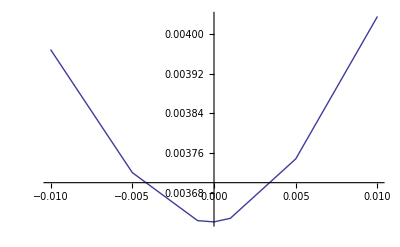

```mathematica
Module[{S1=0.05399906,S2=0.05268318,SpreadStrikes={-0.01,-0.005,-0.001,0,0.001,0.005,0.01},τ=11.737166,
VolS1=0.0251,VolS2=0.024,Correl12=0.9,ρS1=-0.,ρS2=-0.,ρS3=-0.,κS1=0.05,κS2=0.05,κS3=0.05,λ=0.1
,LTVarianceFactor=1.,gyndinkin=10,printflag=1,prices,mode=0},
prices=PackagedSmileBiSuperHestonVanillaSpreadoptionRapide[S1,S2,SpreadStrikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor,gyndinkin,mode,printflag];
ListPlot[Table[{SpreadStrikes[[i]],NormalImplicitVol[S1-S2,SpreadStrikes[[i]],τ,prices[[i]]]},{i,1,Length[SpreadStrikes]}],Joined->True]]
```

Initial:(S1 | 0.0539991
VolSquareS1 | 0.021
S2 | 0.0526832
VolSquareS2 | 0.034) Process V1=(V1 | 0.00215235
κ1 | 0.05
ρ1 | 0.
 κ1 norm. | 1.07774) Process V2=(α2 | 0.137287
β2 | 0.175171
κ2 | 0.05
ρ2 | 0.
 κ21 norm. | 0.364201
 κ22 norm. | 0.285435) Process V3=(V3 | 0.003315
κ3 | 0.05
ρ3 | 0.
 κ3 norm. | 0.868417) T=11.7372

variance attendue du spread:0.000220329 ecart type equivalent: 0.0148435

S1 0.0539991 S2 0.0526832 VolS1=0.021 VolS2=0.034 Correl12= 0.9

entering   SmileBiSuperHestonVanillaSpreadOption **************

moments={{0.12324,0.199532},{0.246863,0.399714,0.282352}}

NormalTerminalcorrelT=0.898851 ExpcorreLT=0.87952

VarExpX=0.00104285 VarExpY=0.00202876

VarRealSpead (Goal)=0.000513014

TrueIniVarSpread=0.0000437085

VS=0.0000187719 VarVS=1.09621×10^-10 CoVarSVS=0.

opt1=0.00924994 opt2=0.00337616 opt3=0.00590341

convexity=0.000114449 pente=-0.000676079 ATMprix=0.00590341

convexityTable=(0.0005 | 7.44186×10^-7
0.001 | 3.01796×10^-6
0.002 | 0.0000125975
0.003 | 0.0000292939
0.01 | 0.0000288344)

prices={0.218,{{-0.8,{0.0105576,0.00478473}},{-0.6,{0.0106434,0.00493173}},{-0.4,{0.010662,0.00515461}},{-0.2,{0.0106081,0.00536019}},{0,{0.0104973,0.00552787}},{0.5,{0.0100439,0.00574043}},{0.8,{0.00981993,0.00572275}}}}

vols={{-0.8,{0.00570989,0.00512346}},{-0.6,{0.00577473,0.00523537}},{-0.4,{0.00578882,0.0054047}},{-0.2,{0.00574805,0.00556054}},{0,{0.00566431,0.00568742}},{0.5,{0.00532066,0.00584801}},{0.8,{0.00515028,0.00583466}}}

penteTable=(-0.8 | -0.000586433
-0.6 | -0.000539353
-0.4 | -0.000384123
-0.2 | -0.000187511
0 | 0.0000231097
0.5 | 0.000527341
0.8 | 0.000684379)

VOptionATM=(0.0000218543 | 0.00446381
0.0000393377 | 0.00669812
0.0000437085 | 0.00718546
0.0000480794 | 0.00765161
0.0000874171 | 0.0111824)

Mode 1 :   Numinimum=0.00718517 rhominimum= -0.765412 V0minimim=0.0000326524

Comparaison:  TrueIniVarSpread/ V0minimim =1.3386

Normal Heston Parameters=(S0 | 0.00131588
V0 | 0.0000326524
θ | 0.0000326524
λv | 0.1
ρ | -0.741677
ν | 0.00741511
ν normalized | 1.29766
standard dev equi. | 0.00571423)

prices={0.0147721,0.0106016,0.00750582,0.0067804,0.00607988,0.00360631,0.00157377}

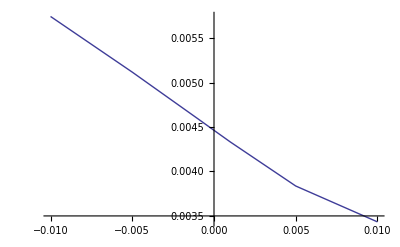

```mathematica
Module[{S1=0.05399906,S2=0.05268318,SpreadStrikes={-0.01,-0.005,-0.001,0,0.001,0.005,0.01},τ=11.737166,
VolS1=0.021,VolS2=0.034,Correl12=0.9,ρS1=-0.,ρS2=-0.,ρS3=-0.,κS1=0.05,κS2=0.05,κS3=0.05,λ=0.1
,LTVarianceFactor=1.,gyndinkin=10,printflag=1,prices,mode=1},
prices=PackagedSmileBiSuperHestonVanillaSpreadoptionRapide[S1,S2,SpreadStrikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor,gyndinkin,mode,printflag];
ListPlot[Table[{SpreadStrikes[[i]],NormalImplicitVol[S1-S2,SpreadStrikes[[i]],τ,prices[[i]]]},{i,1,Length[SpreadStrikes]}],Joined->True]]
```

## Packaging des options dans BiSuperHeston

dS_1/S_1=α_2 √v_2 dW_2+ √v_1 dW_1
dS_2/S_2=β_2 √v_2 dW_2+ √v_3 dW_3

on a v_2(0)=1

contrainte :

α_2^2+v_1^2=V_S1
β_2^2+v_3^2=V_S2
α_2 β_2=ρ √(V_S1 V_S2)

on en deduit

β_2^2=(ρ^2 V_S1 V_S2)/α_2^2

on decide que

β_2^2=(1+ρ)^2/4 V_S2
α_2^2=(4 ρ^2)/(1+ρ)^2 V_S1

on peut verifier que

α_2^2 β_2^2=ρ^2 V_S1 V_S2

et que (tres important) il reste de la plce pour β et δ :

soit α_S2^2<V_S2  et α_S1^2<V_S1

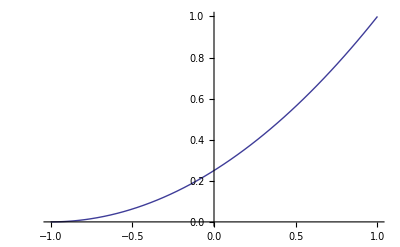

```mathematica
Plot[(1+ρ)^2/4,{ρ,-1,1}]
```

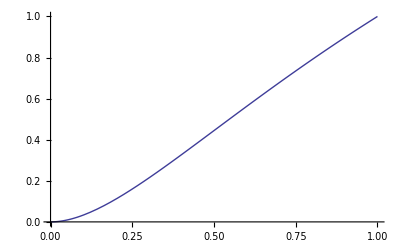

```mathematica
Plot[(4 ρ^2)/(1+ρ)^2,{ρ,0,1}]
```

#### en resumé

α_2=((1+ρ)√V_S2)/2;β_2=(2ρ)/(1+ρ)√V_S1;V_1=V_S1-α_2^2;V_3=V_S2-β_2^2;V_2=1;

```mathematica
SmileBiSuperHestonVanillaSpreadOption[S1,S2, ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,LTFactorS,λS,SpreadStrikes,τ,printflag]
```

## PackagedSmileBiSuperHestonVanillaSpreadoptionRapide

```mathematica
PackagedSmileBiSuperHestonVanillaSpreadoptionRapide[S1_,S2_,SpreadStrikes_,τ_,
VolS1_,VolS2_,Correl12_,ρS1_,ρS2_,ρS3_,κS1_,κS2_,κS3_,λ_,LTVarianceFactor_,LimitGindinkin_,mode_,
printflag_]:=
Module[{S,ρ1,κ1,V1,V2,ρ2,κ2,ρ3,κ3,V3,VarApprox,α2,β2},
β2=((1+Correl12)√VolS2)/2;α2=(2Correl12)/(1+Correl12)√VolS1;V1=VolS1-α2^2;V3=VolS2-β2^2;V2=1;
κ1=κS1;κ2=κS2;κ3=κS3;
ρ1=ρS1;ρ2=ρS2;ρ3=ρS3;
If[printflag==1 || MemberQ[printflag,1]  ,
Print["Initial:",{{"S1",S1},{"VolSquareS1",VolS1},{"S2",S2},{"VolSquareS2",VolS2}} // MatrixForm,
" Process V1=",{{"V1",V1},{"κ1",κ1},{"ρ1",ρ1},{" κ1 norm.",κ1/(√V1)}} //MatrixForm,
" Process V2=",{{"α2",α2},{"β2",β2},{"κ2",κ2},{"ρ2",ρ2},{" κ21 norm.",κ2/α2},{" κ22 norm.",κ2/β2}} //MatrixForm,
" Process V3=",{{"V3",V3},{"κ3",κ3},{"ρ3",ρ3},{" κ3 norm.",κ3/(√V3)}} //MatrixForm,
" T=",τ]];
VarApprox=((S1 √VolS1)^2+(S2 √VolS2)^2-2Correl12 S1 √VolS1 S2 √VolS2)τ;
If[printflag==1 || MemberQ[printflag,1]  ,Print["variance attendue du spread:", VarApprox, " ecart type equivalent: ",√VarApprox];
Print["S1 ", S1, " S2 ",S2," VolS1=",VolS1," VolS2=",VolS2, " Correl12= ",Correl12];Print["entering   SmileBiSuperHestonVanillaSpreadOption **************"]];
SmileBiSuperHestonVanillaSpreadOption[S1,S2, ρ1,λ,V1 LTVarianceFactor,κ1,V1,ρ2,λ,V2 LTVarianceFactor,κ2,V2,ρ3,λ,V3 LTVarianceFactor,κ3,V3,α2,β2,LTVarianceFactor,λ,SpreadStrikes,τ,LimitGindinkin,mode,printflag]]
```

```mathematica
Module[{S1=0.05,S2=0.048,SpreadStrikes={-0.01,-0.005,-0.001,0,0.001,0.005,0.01},τ=15,
VolS1=0.01,VolS2=0.01,Correl12=0.95,ρS1=0.1,ρS2=0.1,ρS3=0.1,κS1=0.1,κS2=3.,κS3=0.1,λ=0.15,LTVarianceFactor=1.5,gyndinkin=1,printflag=1,prices},
prices=PackagedSmileBiSuperHestonVanillaSpreadoptionRapide[S1,S2,SpreadStrikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor,gyndinkin,printflag];
Table[NormalImplicitVol[S1-S2,SpreadStrikes[[i]],τ,prices[[i]]],{i,1,Length[SpreadStrikes]}]]
```

Initial:(S1 | 0.05
VolSquareS1 | 0.01
S2 | 0.048
VolSquareS2 | 0.01) Process V1=(V1 | 0.000506246
κ1 | 0.1
ρ1 | 0.1
 κ1 norm. | 4.44446) Process V2=(α2 | 0.0974359
β2 | 0.0975
κ2 | 3.
ρ2 | 0.1
 κ21 norm. | 30.7895
 κ22 norm. | 30.7692) Process V3=(V3 | 0.00049375
κ3 | 0.1
ρ3 | 0.1
 κ3 norm. | 4.50035) T=15

variance attendue du spread:0.0000366 ecart type equivalent: 0.00604979

S1 0.05 S2 0.048 VolS1=0.01 VolS2=0.01 Correl12= 0.95

entering   SmileBiSuperHestonVanillaSpreadOption **************

moments={{0.09759,0.09759},{0.244853,0.244996,0.235109}}

NormalTerminalcorrelT=0.959924 ExpcorreLT=0.955037

(ρ1 | λv1 | θv1 | κ1 | V1 | ρ2 | λv2 | α2^2 θv2 | κ2 | α2^2V2 | S1 | τ
0.1 | 0.15 | 0.000759369 | 0.1 | 0.000506246 | 0.1 | 0.15 | 0.0142406 | 3. | 0.00949375 | 0.05 | 15)

VarExpX=0.000654957 VarExpY=0.000603608

VarRealSpead (Goal)=0.0000575901

TrueIniVarSpread=2.95061×10^-6

VS=2.44×10^-6 VarVS=5.82317×10^-11 CoVarSVS=2.80076×10^-10

ρprojeté=0.0234964 νprojeté=0.00488523 νfinal=0.00100555 νnormalized=0.585396

Normal Heston Parameters=(S0 | 0.002
V0 | 2.95061×10^-6
θ | 4.42592×10^-6
λv | 0.15
ρ | 0.0234964
ν | 0.00100555
ν normalized | 0.585396
standard dev equi. | 0.00171774)

prices={0.0122175,0.00771308,0.00467406,0.00403358,0.00344882,0.00168642,0.000585805}

{0.00203109,0.00194125,0.0018984,0.00189337,0.0018909,0.0019071,0.00197753}

```mathematica
PackagedSmileBiSuperHestonUnderlyingOption2[S1_,S2_,KList_,T_,
VolS1_,VolS2_,Correl12_,ρ1_,ρ2_,ρ3_,κ1_,κ2_,κ3_,λ_,LTVarianceFactor_,
printflag_]:=
Module[{S,V1,α2,β2,V3,V2},
β2=((1+Correl12)√VolS2)/2;α2=(2Correl12)/(1+Correl12)√VolS1;V1=VolS1-α2^2;V3=VolS2-β2^2;V2=1;
If[printflag==1 || MemberQ[printflag,1]  ,
Print["Initial:",{{"S1",S1},{"VolS1",VolS1},{"S2",S2},{"VolS2",VolS2}} // MatrixForm,
" repartition=",{{"β2",β2},{"α2",α2},{"V1",V1},{"V3",V3}}//MatrixForm,
" Process V2=",{{"α2",α2},{"β2",β2},{"λv2",λ},{"θv2",β2^2 LTVarianceFactor},{"κ2",κ2},{"ρ2",ρ2}} //MatrixForm,
" Process V3=",{{"V3",V3},{"λv2",λ},{"θv3",V3 LTVarianceFactor},{"κ3",κ3},{"ρ3",ρ3}} //MatrixForm,
" T=",T]];
Table[LogHestonNormalCall[ρ3,λ,V3 LTVarianceFactor,κ3,V3,ρ2,λ,β2^2 LTVarianceFactor,β2 κ2,β2^2,S2,KList[[i]],T],{i,1,Length[KList]}]]
```

```mathematica
PackagedSmileBiSuperHestonUnderlyingOption1[S1_,S2_,KList_,T_,
VolS1_,VolS2_,Correl12_,ρ1_,ρ2_,ρ3_,κ1_,κ2_,κ3_,λ_,LTVarianceFactor_,
printflag_]:=
Module[{S,V1,α2,β2,V3},
β2=((1+Correl12)√VolS2)/2;α2=(2Correl12)/(1+Correl12)√VolS1;V1=VolS1-α2^2;V3=VolS2-β2^2;V2=1;
If[printflag==1 || MemberQ[printflag,1]  ,
Print["Initial:",{{"S1",S1},{"VolS1",VolS1},{"S2",S2},{"VolS2",VolS2}} // MatrixForm,
" repartition=",{{"β2",β2},{"α2",α2},{"V1",V1},{"V3",V3}}//MatrixForm,
" Process V1=",{{"V1",V1},{"λv1",λ},{"θv1",V1 LTVarianceFactor },{"κ1",κ1},{"ρ1",ρ1}} //MatrixForm,
" Process V2=",{{"α2",α2},{"β2",β2},{"λv2",λ},{"θv2",α2^2 LTVarianceFactor},{"κ2",κ2},{"ρ2",ρ2}} //MatrixForm," T=",T]];
Table[LogHestonNormalCall[ρ1,λ,V1 LTVarianceFactor,κ1,V1,ρ2,λ,α2^2 LTVarianceFactor,α2 κ2,α2^2,S1,KList[[i]],T],{i,1,Length[KList]}]]
```

```mathematica
Module[{S1=0.05,S2=0.05,KList={0.04,0.05,0.06},τ=5,
VolS1=0.01,VolS2=0.01,Correl12=0.99,ρ1=0.05,ρ2=0.05,ρ3=-0.5,ν1=0.3,ν2=2.4,ν3=3.2,
λ=0.15,LTVarianceFactor=1.5,printflag={1},prices},
prices=PackagedSmileBiSuperHestonUnderlyingOption1[S1,S2,KList,τ,VolS1,VolS2,Correl12,ρ1,ρ2,ρ3,ν1,ν2,ν3,λ,LTVarianceFactor,
printflag];
Print[prices];
{Table[ImpVolBS[S1,KList[[i]],τ,prices[[i]]],{i,1,Length[KList]}],
Table[ImpVolBS[S1,KList[[i]],τ,LogHestonNormalCall[ρ2,λ,VolS1  LTVarianceFactor,ν2,VolS1,S1,KList[[i]],τ]],{i,1,Length[KList]}]}//MatrixForm]
```

Initial:(S1 | 0.05
VolS1 | 0.01
S2 | 0.05
VolS2 | 0.01) repartition=(V2S2 | 0.0995
α2 | 0.0994975
V1 | 0.00010025
V3 | 0.00009975) Process V1=(V1 | 0.00010025
λv1 | 0.15
θv1 | 0.000150375
κ1 | 0.3
ρ1 | 0.05) Process V2=(α2 | 0.0994975
V2S2 | 0.0995
λv2 | 0.15
θv2 | 0.149246
κ2 | 2.4
ρ2 | 0.05) T=5

{0.0102564,0.000914627,0.000366617}

(0.0709830928075221844423499714358 | 0.0205077024070346873290034034792 | 0.0635463536850369333151750024111
0.0706190731158806886183669500828 | 0.0197225937553643371093716070836 | 0.0631220009223781542609639508279)

```mathematica
Module[{S1=0.05,S2=0.05,α1=1,a=1,KList={0.04,0.05,0.06},τ=5,
VolS1=0.01,VolS2=0.01,Correl12=0.999,ρ2=0.05,ν2=2.4,
λ=0.15,LTVarianceFactor=1.5,V1=0.001,ν1,printflag={1}},ν1=√(VolS1/V1);
{Table[ImpVolBS[S1,KList[[i]],τ,LogHestonNormalCall[ρ2,λ,V1 LTVarianceFactor,ν1,V1,ρ2,λ,VolS1 LTVarianceFactor,ν2,VolS1,S1,KList[[i]],τ]],{i,1,Length[KList]}],
Table[ImpVolBS[S1,KList[[i]],τ,LogHestonNormalCall[ρ2,λ,VolS1  LTVarianceFactor,ν2,VolS1,S1,KList[[i]],τ]],{i,1,Length[KList]}]}//MatrixForm]
```

(0.0719452984578467762375686934324 | 0.0209925838336815011481289151147 | 0.0644247233221604656886521810693
0.0706190731158806886183669500828 | 0.0197225937553643371093716070836 | 0.0631220009223781542609639508279)

```mathematica
Module[{S1=0.05,S2=0.05,α1=1,a=1,KList={0.04,0.05,0.06},τ=5,
VolS1=0.01,VolS2=0.01,Correl12=0.8,ρ1=0.01,ρ2=0.05,ρ3=-0.5,ν1=0.3,ν2=2.4,ν3=3.2,
λ1=0.15,λ=0.15,LTVarianceFactor=1.5,
printflag={1}},
ImpVolBS[S2,KList,τ,PackagedSmileBiSuperHestonUnderlyingOption2[S1,S2,KList,τ,
VolS1,VolS2,Correl12,ρ1,ρ2,ρ3,ν1,ν2,ν3,λ,LTVarianceFactor,
printflag]]]
```

Initial:(S1 | 0.05
VolS1 | 0.01
S2 | 0.05
VolS2 | 0.01) repartition=(β2 | 0.09
α2 | 0.0888889
V1 | 0.00209877
V3 | 0.0019) Process V2=(α2 | 0.0888889
β2 | 0.09
λv2 | 0.15
θv2 | 0.01215
κ2 | 2.4
ρ2 | 0.05) Process V3=(V3 | 0.0019
λv2 | 0.15
θv3 | 0.00285
κ3 | 3.2
ρ3 | -0.5) T=5

{0.0962502706676334116482194602368,0.0720711565077786528405870950733,0.0925496630427405996356847411262}

Initial:(S1 | 0.049279
VolSquareS1 | 0.022
S2 | 0.045917
VolSquareS2 | 0.025) Process V1=(V1 | 0.00138512
κ1 | 0.3
ρ1 | 0.05
 κ1 norm. | 8.06079) Process V2=(α2 | 0.143579
β2 | 0.153212
κ2 | 1.6
ρ2 | -0.395
 κ21 norm. | 11.1437
 κ22 norm. | 10.443) Process V3=(V3 | 0.00152598
κ3 | 0.2
ρ3 | 0.03
 κ3 norm. | 5.11984) T=5

variance attendue du spread:0.000032913 ecart type equivalent: 0.00573699

S1 0.049279 S2 0.045917 VolS1=0.022 VolS2=0.025 Correl12= 0.938

entering   SmileBiSuperHestonVanillaSpreadOption **************

moments={{0.055,0.0625},{0.128068,0.14707,0.129755}}

NormalTerminalcorrelT=0.945461 ExpcorreLT=0.941689

(ρ1 | λv1 | θv1 | κ1 | V1 | ρ2 | λv2 | α2^2 θv2 | κ2 | α2^2V2 | S1 | τ
0.05 | 0.35 | 0.00138512 | 0.3 | 0.00138512 | -0.395 | 0.35 | 0.0206149 | 1.6 | 0.0206149 | 0.049279 | 5)

VarExpX=0.000315206 VarExpY=0.000318105

VarRealSpead (Goal)=0.000036935

TrueIniVarSpread=7.387×10^-6

VS=6.5826×10^-6 VarVS=1.01136×10^-9 CoVarSVS=1.76565×10^-9 driftVarVS=2.924×10^-10

avκ1=8.16836×10^-9 bvκ1=2.45499×10^-12 avκ2=2.65589×10^-18 bvκ2=-2.50637×10^-15 avκ3=6.78331×10^-9 bvκ3=1.13249×10^-12

ρprojeté=0.0216398 νprojeté=0.0123952 νfinal=0.0052328 νfinal/νprojeté=0.422163 νnormalized=1.92531

Normal Heston Parameters=(S0 | 0.003362
V0 | 7.387×10^-6
θ | 7.387×10^-6
λv | 0.35
ρ | 0.0216398
ν | 0.0052328
ν normalized | 1.92531
standard dev equi. | 0.0027179)

prices={0.0134863,0.00867364,0.00592407,0.00504794,0.00462358,0.00421093,0.00381241,0.00343083,0.00273088,0.00129221,0.000742677,0.000459854,0.000182301}

Vol Normale Underlying1=0.00620646Vol Normale Underlying2=0.00618493

Vol normal a la monaie du spread = 0.00217514

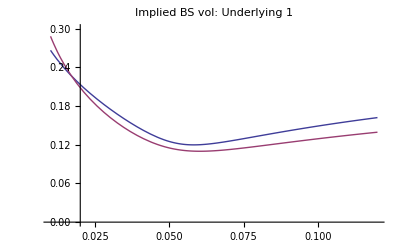
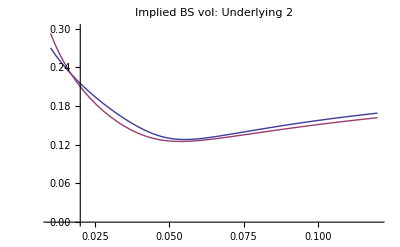
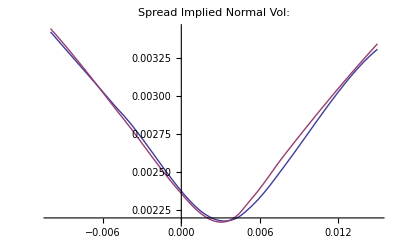
{12.969,{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Timing[Module[{S1,S2,α1=1,β1=1,a=1,b=1,spreadstrikes,τ=5,
VolSquareS1=0.022,VolSquareS2=0.025,Correl12=0.938,ρS2=-0.395,κS2=1.6,ρS1=0.05,ρS3=0.03,κS1=0.3,κS3=0.2,
λ=0.35,LTVarianceFactor=1.,gyndinkin=2,
Understrikes,prices1,smile1,prices2,smile2,inter1,inter2,smileMarket1,smileMarket2,
interMarket1,interMarket2,spreadprices,spreadsmile,interspread,VolNormal1,VolNormal2,spreadMarket,interspreadMarket,
tenor1="cms10",tenor2="cms2"},

(* S1=MarketCMSForward[τ,tenor1][[1]];S2=MarketCMSForward[τ,tenor2][[1]]; *)
S1=0.049279;S2=0.045917;
Understrikes={0.01,0.0125,0.015,0.0175,0.02,0.021,0.022,0.023,0.024,0.0245,0.025,0.0255,0.026,0.0265,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.045,0.048,0.05,0.055,0.058,0.06,0.062,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.11,0.12};
spreadstrikes={-0.01,-0.005,-0.002,-0.001,-0.0005,0,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015};
prices1=PackagedSmileBiSuperHestonUnderlyingOption1[S1,S2,Understrikes,τ,
VolSquareS1,VolSquareS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor,0];
smile1=Table[{Understrikes[[i]],ImpVolBS[S1,Understrikes[[i]],τ,prices1[[i]]]},{i,1,Length[Understrikes]}];
inter1=Interpolation[smile1];
smileMarket1=Table[{Understrikes[[i]],MarketCMSOptionVol[Understrikes[[i]],τ,tenor1][[1]]},{i,1,Length[Understrikes]}];
interMarket1=Interpolation[smileMarket1];
prices2=PackagedSmileBiSuperHestonUnderlyingOption2[S1,S2,Understrikes,τ,
VolSquareS1,VolSquareS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor,0];
smile2=Table[{Understrikes[[i]],ImpVolBS[S2,Understrikes[[i]],τ,prices2[[i]]]},{i,1,Length[Understrikes]}];
inter2=Interpolation[smile2];
smileMarket2=Table[{Understrikes[[i]],MarketCMSOptionVol[Understrikes[[i]],τ,tenor2][[1]]},{i,1,Length[Understrikes]}];
interMarket2=Interpolation[smileMarket2];
spreadprices=PackagedSmileBiSuperHestonVanillaSpreadoptionRapide[S1,S2,spreadstrikes,τ,
VolSquareS1,VolSquareS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor,gyndinkin,{1,4,9}];
spreadsmile=Table[{spreadstrikes[[i]],NormalImplicitVol[S1-S2,spreadstrikes[[i]],τ,spreadprices[[i]]]},{i,1,Length[spreadstrikes]}];
interspread=Interpolation[spreadsmile];
VolNormal1=inter1[S1] S1;VolNormal2=inter2[S2] S2;Print["Vol Normale Underlying1=",VolNormal1,"Vol Normale Underlying2=",VolNormal2];
spreadMarket=Table[{spreadstrikes[[i]],MarketCMSSpreadOptionNormalVol[spreadstrikes[[i]],τ,tenor2,tenor1][[1]]},{i,1,Length[spreadstrikes]}];
interspreadMarket=Interpolation[spreadMarket];
Print["Vol normal a la monaie du spread = ",interspreadMarket[S1-S2]];
{Plot[{inter1[x],interMarket1[x]},{x,Understrikes[[1]],Last[Understrikes]},PlotLabel->"Implied BS vol: Underlying 1",
PlotLegend->{"BiSuperHeston","Market"},LegendPosition->{1,0},PlotRange->{0,0.3}],
Plot[{inter2[x],interMarket2[x]},{x,Understrikes[[1]],Last[Understrikes]},PlotLabel->"Implied BS vol: Underlying 2",
PlotLegend->{"BiSuperHeston","Market"},LegendPosition->{1,0},PlotRange->{0,0.3}],
Plot[{interspread[x],interspreadMarket[x]},{x,spreadstrikes[[1]],Last[spreadstrikes]},PlotLabel->"Spread Implied Normal Vol:",
PlotLegend->{"BiSuperHeston","Market"},LegendPosition->{1,0},PlotRange->All]}]]
```

Initial:(S1 | 0.043046
VolS1 | 0.00045
S2 | 0.0459995
VolS2 | 0.0003) Process V1=(V1 | 0.000196875
κ1 | 0.001
ρ1 | 0.3
 κ1 norm. | 0.0712697) Process V2=(α2 | 0.0159099
β2 | 0.0138564
κ2 | 0.14
ρ2 | -0.4
 κ21 norm. | 8.79955
 κ22 norm. | 10.1036) Process V3=(V3 | 0.000108
κ3 | 0.001
ρ3 | -0.2
 κ3 norm. | 0.096225) T=5

variance attendue du spread:5.95578×10^-7

moments={{0.00115835,0.000772237},{0.0023184,0.0015462,0.00113681}}

NormalTerminalcorrelT=0.600429 ExpcorreLT=0.60019

(ρ1 | λv1 | θv1 | κ1 | V1 | ρ2 | λv2 | α2^2 θv2 | κ2 | α2^2V2 | S1 | τ
0.3 | 0.15 | 0.000216563 | 0.001 | 0.000196875 | -0.4 | 0.15 | 0.000278438 | 0.14 | 0.000253125 | 0.043046 | 5)

VarExpX=4.29155×10^-6 VarExpY=3.26329×10^-6

VarRealSpead (Goal)=3.06269×10^-6

TrueIniVarSpread=5.94901×10^-7

VS=5.95578×10^-7 VarVS=1.76295×10^-15 CoVarSVS=1.24325×10^-11

ρprojeté=0.383682 νprojeté=0.0000544065 νfinal=0.0000239921 νnormalized=0.0311061

Normal Heston Parameters=(S0 | -0.0029535
V0 | 5.94901×10^-7
θ | 6.54391×10^-7
λv | 0.15
ρ | 0.383682
ν | 0.0000239921)

L=1296.52 κa=0.0311061 S0a=-3.82926 ka={-12.9652,-6.48258,-1.29652,-0.648258,0,0.648258,1.29652,2.59303,6.48258,9.72387,12.9652,19.4477}

prices={0.00704651,0.00214889,0.000118435,0.0000658065,0.0000344767,0.000017005,7.88644×10^-6,1.40496×10^-6,1.70605×10^-9,1.08856×10^-12,1.45772×10^-16,7.14295×10^-21}

spreadprices={0.00704651,0.00214889,0.000118435,0.0000658065,0.0000344767,0.000017005,7.88644×10^-6,1.40496×10^-6,1.70605×10^-9,1.08856×10^-12,1.45772×10^-16,7.14295×10^-21}

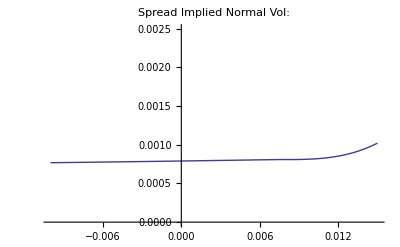

```mathematica
Module[{S1=0.043046,S2=0.0459995,spreadstrikes={-0.01,-0.005,-0.001,-0.0005,0,0.0005,0.001,0.002,0.005,0.0075,0.01,0.015},τ=5,
VolS1=0.00045,VolS2=0.0003,Correl12=0.6,ρS1=0.3,ρS2=-0.4,ρS3=-0.2,κS1=0.001,κS2=0.14,κS3=0.001,λ=0.15,LTVarianceFactor=1.1,printflag=1,spreadprices,spreadsmile,interspread},spreadprices=PackagedSmileBiSuperHestonVanillaSpreadoptionRapide[S1,S2,spreadstrikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor,printflag];
Print["spreadprices=",spreadprices];
spreadsmile=Table[{spreadstrikes[[i]],NormalImplicitVol[S1-S2,spreadstrikes[[i]],τ,spreadprices[[i]]]},{i,1,Length[spreadstrikes]}];
interspread=Interpolation[spreadsmile];
Plot[{interspread[x]},{x,spreadstrikes[[1]],Last[spreadstrikes]},PlotLabel->"Spread Implied Normal Vol:",
PlotLegend->{"BiSuperHeston","Market"},LegendPosition->{1,0},PlotRange->{0,0.0025}]
]
```

## Etude de convergence Normal Heston

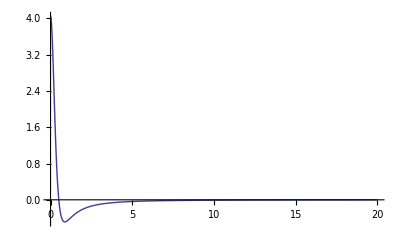
{0.125,-Graphics-}

```mathematica
Timing[Module[{ρ=0.,λv=0.35,θv=0.000929,κ=0.29,V=0.000929,S0=-0.00421,k=-0.025,T=5,ω},
Plot[{NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +0.5ⅈ]},{ω,0,20},PlotRange->All]
]]
```

```mathematica
Timing[Module[{ρ=0.18,λv=0.35,θv=0.000929,κ=0.29,V=0.000929,S0=-0.00421,k=-0.005,T=5},
NormalImplicitVol[S0,#,T,HestonNormalCall[ρ,λv,θv,κ,V,S0,#,T]]& /@{-0.025,-0.02,-0.015,-0.01,-0.005}]]
```

{1.891,{0.000453251,0.00449076,0.00578457,0.00620497,0.00659936}}

FindRoot::jsing: Encountered a singular Jacobian at the point {u$6944586} = {0.0001}. Try perturbing the initial point(s).

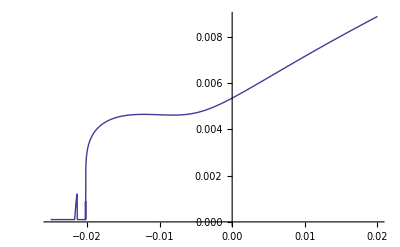
{775.625,-Graphics-}

```mathematica
Timing[Module[{ρ=0.18,λv=0.35,θv=0.000929,κ=0.5,V=0.000929,S0=-0.00421,k=-0.005,T=5},Plot[{
NormalImplicitVol[S0,k,T,HestonNormalCall[ρ,λv,θv,κ,V,S0,k,T]]},{k,-0.025,0.02}]]]
```

```mathematica
(* HestonNormalCallAux[ρ_,λv_,θv_,κ_,V_,S0_,k_,T_]:=1/π Re[Module[{λ=0.5,ω},
AdaptativeIntegrate[Function[ω,NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +λ ⅈ]],LegendreCoeffs[100],LegendreCoeffs[30],
10,1,10^(-10),1000,1,LegendreCoeffs[100]][[2]]]]
*)
```

```mathematica
Timing[Module[{ρ=0.18,λv=0.35,θv=0.000929,κ=0.29,V=0.000929,S0=-0.00421,k=-0.005,T=5},
NormalImplicitVol[S0,#,T,HestonNormalCall[ρ,λv,θv,κ,V,S0,#,T]]& /@{-0.0225}]]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {u$6942268} = {0.0001}. Try perturbing the initial point(s).

{0.828,{0.0001}}

## Problème du contrôle de la vol de vol

### 1) BiSuperheston

```mathematica
Corr={
{1,0,0,ρ1,0,0},
{0,1,0,0,ρ2,0},
{0,0,1,0,0,ρ3},
{ρ1,0,0,1,0,0},
{0,ρ2,0,0,1,0},
{0,0,ρ3,0,0,1}
};
```

```mathematica
Clear[S1,S2,V1,V2,V3]
```

```mathematica
Diff[x_]:=
D[x,S1]{√V1 S1,α2 √V2 S1,0,0,0,0}+D[x,S2]{0,β2 √V2 S2,√V3 S2,0,0,0}+
D[x,V1]{0,0,0,κ1 √V1,0,0}+D[x,V2]{0,0,0,0,κ2 √V2,0}+D[x,V3]{0,0,0,0,0,κ3 √V3}
```

```mathematica
VS=Simplify[Diff[S1-S2].(Corr.Diff[S1-S2])]
```

S1^2 V1+S2^2 V3+V2 (S1 α2-S2 β2)^2

```mathematica
Drift[x_]:=1/2(D[x,S1,S1](Diff[S1].Diff[S1])+D[x,S1,S2](Diff[S1].Diff[S2])+D[x,S2,S2](Diff[S2].Diff[S2])+D[x,V1,V1](Diff[V1].Diff[V1])+D[x,V2,V2](Diff[V2].Diff[V2])+D[x,V3,V3](Diff[V3].Diff[V3]))
```

```mathematica
DiffVS=Diff[VS]
```

{S1 √V1 (2 S1 V1+2 V2 α2 (S1 α2-S2 β2)),S1 √V2 α2 (2 S1 V1+2 V2 α2 (S1 α2-S2 β2))+S2 √V2 β2 (2 S2 V3-2 V2 β2 (S1 α2-S2 β2)),S2 √V3 (2 S2 V3-2 V2 β2 (S1 α2-S2 β2)),S1^2 √V1 κ1,√V2 (S1 α2-S2 β2)^2 κ2,S2^2 √V3 κ3}

```mathematica
DiffVS //MatrixForm
```

(S1 √V1 (2 S1 V1+2 V2 α2 (S1 α2-S2 β2))
S1 √V2 α2 (2 S1 V1+2 V2 α2 (S1 α2-S2 β2))+S2 √V2 β2 (2 S2 V3-2 V2 β2 (S1 α2-S2 β2))
S2 √V3 (2 S2 V3-2 V2 β2 (S1 α2-S2 β2))
S1^2 √V1 κ1
√V2 (S1 α2-S2 β2)^2 κ2
S2^2 √V3 κ3)

```mathematica
VarVS=Simplify[Diff[VS].(Corr.Diff[VS])]
```

S1^2 V1 (2 S1 (V1+V2 α2^2)-2 S2 V2 α2 β2) (2 S1 V1+2 V2 α2 (S1 α2-S2 β2)+S1 κ1 ρ1)+S1^3 V1 κ1 (-2 S2 V2 α2 β2 ρ1+S1 (κ1+2 (V1+V2 α2^2) ρ1))+V2 (S1 α2-S2 β2)^2 κ2 ((S1 α2-S2 β2)^2 κ2+(2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) ρ2)+V2 (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) (-2 S1 S2 α2 β2 (V2 (α2+β2)+κ2 ρ2)+S1^2 α2 (2 V1+α2 (2 V2 α2+κ2 ρ2))+S2^2 β2 (2 V3+β2 (2 V2 β2+κ2 ρ2)))+S2^3 V3 κ3 (-2 S1 V2 α2 β2 ρ3+S2 (κ3+2 (V3+V2 β2^2) ρ3))+2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)) (-2 S1 V2 α2 β2+S2 (2 V3+2 V2 β2^2+κ3 ρ3))

```mathematica
CoVarSVS=Simplify[Diff[VS].(Corr.Diff[S1-S2])]
```

2 S1^2 V1 (S1 (V1+V2 α2^2)-S2 V2 α2 β2)-2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2))+V2 (S1 α2-S2 β2) (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2))+S1^3 V1 κ1 ρ1+V2 (S1 α2-S2 β2)^3 κ2 ρ2-S2^3 V3 κ3 ρ3

Que l' on identifie avec les meme calculs fait avec normal heston :

```mathematica
Simplify[Drift[VarVS]]
```

2 (S1^4 (12 V1^4+12 V1^3 (4 V2 α2^2+κ1 ρ1)+V2 α2^5 (12 V2^3 α2^3+9 V2 α2 κ2^2+12 V2^2 α2^2 κ2 ρ2+2 κ2^3 ρ2)+3 V1^2 (24 V2^2 α2^4+3 κ1^2+4 V2 α2^2 (2 κ1 ρ1+α2 κ2 ρ2))+V1 (48 V2^3 α2^6+9 V2 α2^2 (κ1^2+α2^2 κ2^2)+2 κ1^3 ρ1+12 V2^2 α2^4 (κ1 ρ1+2 α2 κ2 ρ2)))-S1^3 S2 V2 α2 β2 (12 V1^3+6 V1^2 (3 V2 α2 (2 α2+β2)+κ1 ρ1+2 α2 κ2 ρ2)+α2^2 (6 V2^3 α2^2 (2 α2^2+3 α2 β2+β2^2)+3 V2 α2 (6 α2+5 β2) κ2^2+3 V2^2 α2 (6 α2^2+5 α2 β2+β2^2) κ2 ρ2+2 (3 α2+β2) κ2^3 ρ2)+V1 (6 V2^2 α2^2 (6 α2^2+6 α2 β2+β2^2)+4 κ1^2+2 α2 (7 α2+2 β2) κ2^2+3 V2 α2 (2 α2 κ1 ρ1+β2 κ1 ρ1+10 α2^2 κ2 ρ2+4 α2 β2 κ2 ρ2)))+S1^2 S2^2 V2 α2 β2 (2 V1^2 (2 V3+β2 (V2 α2+2 V2 β2+κ2 ρ2))+V1 (4 V3^2+2 V3 (V2 (4 α2^2+6 α2 β2+4 β2^2)+(α2+β2) κ2 ρ2)+β2 (4 V2^2 (α2^3+4 α2^2 β2+3 α2 β2^2+β2^3)+(5 α2+4 β2) κ2^2+2 V2 (4 α2^2+5 α2 β2+β2^2) κ2 ρ2))+α2 (2 V2^3 β2 (α2+β2)^2 (α2^2+4 α2 β2+β2^2)+2 V2^2 (2 V3 (α2^3+3 α2^2 β2+4 α2 β2^2+β2^3)+3 β2 (α2+β2)^3 κ2 ρ2)+V2 (2 V3^2 (2 α2+β2)+3 β2 (3 α2^2+10 α2 β2+3 β2^2) κ2^2+2 V3 (α2^2+5 α2 β2+4 β2^2) κ2 ρ2)+κ2 (V3 (4 α2+5 β2) κ2+2 V3^2 ρ2+6 β2 (α2+β2) κ2^2 ρ2)))+S2^4 (12 V3^4+V2 β2^5 (12 V2^3 β2^3+9 V2 β2 κ2^2+12 V2^2 β2^2 κ2 ρ2+2 κ2^3 ρ2)+12 V3^3 (4 V2 β2^2+κ3 ρ3)+V3 (48 V2^3 β2^6+9 V2 β2^2 (β2^2 κ2^2+κ3^2)+2 κ3^3 ρ3+12 V2^2 β2^4 (2 β2 κ2 ρ2+κ3 ρ3))+3 V3^2 (24 V2^2 β2^4+3 κ3^2+4 V2 β2^2 (β2 κ2 ρ2+2 κ3 ρ3)))-S1 S2^3 V2 α2 β2 (12 V3^3+β2^2 (6 V2^3 β2^2 (α2^2+3 α2 β2+2 β2^2)+3 V2 β2 (5 α2+6 β2) κ2^2+3 V2^2 β2 (α2^2+5 α2 β2+6 β2^2) κ2 ρ2+2 (α2+3 β2) κ2^3 ρ2)+6 V3^2 (3 V2 β2 (α2+2 β2)+2 β2 κ2 ρ2+κ3 ρ3)+V3 (6 V2^2 β2^2 (α2^2+6 α2 β2+6 β2^2)+4 α2 β2 κ2^2+14 β2^2 κ2^2+4 κ3^2+3 V2 β2 (4 α2 β2 κ2 ρ2+10 β2^2 κ2 ρ2+α2 κ3 ρ3+2 β2 κ3 ρ3))))

```mathematica
vvar=S1^2 V1 (2 S1 (V1+V2 α2^2)-2 S2 V2 α2 β2) (2 S1 V1+2 V2 α2 (S1 α2-S2 β2)+S1 κ1 ρ1)+S1^3 V1 κ1 (-2 S2 V2 α2 β2 ρ1+S1 (κ1+2 (V1+V2 α2^2) ρ1))+V2 (S1 α2-S2 β2)^2 κ2 ((S1 α2-S2 β2)^2 κ2+(2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) ρ2)+V2 (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) (-2 S1 S2 α2 β2 (V2 (α2+β2)+κ2 ρ2)+S1^2 α2 (2 V1+α2 (2 V2 α2+κ2 ρ2))+S2^2 β2 (2 V3+β2 (2 V2 β2+κ2 ρ2)))+S2^3 V3 κ3 (-2 S1 V2 α2 β2 ρ3+S2 (κ3+2 (V3+V2 β2^2) ρ3))+2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)) (-2 S1 V2 α2 β2+S2 (2 V3+2 V2 β2^2+κ3 ρ3));
```

```mathematica
Collect[vvar,κ3]
```

4 S2^3 V3^2 (-S1 V2 α2 β2+S2 (V3+V2 β2^2))-4 S1 S2^2 V2 V3 α2 β2 (-S1 V2 α2 β2+S2 (V3+V2 β2^2))+4 S2^3 V2 V3 β2^2 (-S1 V2 α2 β2+S2 (V3+V2 β2^2))+S2^4 V3 κ3^2+S1^2 V1 (2 S1 (V1+V2 α2^2)-2 S2 V2 α2 β2) (2 S1 V1+2 V2 α2 (S1 α2-S2 β2)+S1 κ1 ρ1)+S1^3 V1 κ1 (-2 S2 V2 α2 β2 ρ1+S1 (κ1+2 (V1+V2 α2^2) ρ1))+V2 (S1 α2-S2 β2)^2 κ2 ((S1 α2-S2 β2)^2 κ2+(2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) ρ2)+V2 (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) (-2 S1 S2 α2 β2 (V2 (α2+β2)+κ2 ρ2)+S1^2 α2 (2 V1+α2 (2 V2 α2+κ2 ρ2))+S2^2 β2 (2 V3+β2 (2 V2 β2+κ2 ρ2)))+κ3 (-2 S1 S2^3 V2 V3 α2 β2 ρ3+2 S2^4 V3 (V3+V2 β2^2) ρ3+2 S2^3 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)) ρ3)

```mathematica
vκ3=S2^4 V3 κ3^2+κ3 (-2 S1 S2^3 V2 V3 α2 β2 ρ3+2 S2^4 V3 (V3+V2 β2^2) ρ3+2 S2^3 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)) ρ3);
```

```mathematica
vκ1=S1^4 V1 κ1^2+κ1 (2 S1^4 V1 (V1+V2 α2^2) ρ1-2 S1^3 S2 V1 V2 α2 β2 ρ1+S1^3 V1 (2 S1 (V1+V2 α2^2)-2 S2 V2 α2 β2) ρ1)
```

```mathematica
S1^4 V1 κ1^2+κ1 (2 S1^4 V1 (V1+V2 α2^2) ρ1-2 S1^3 S2 V1 V2 α2 β2 ρ1+S1^3 V1 (2 S1 (V1+V2 α2^2)-2 S2 V2 α2 β2) ρ1);
```

```mathematica
Simplify[vvar-vκ3-vκ1-vκ2]
```

4 (S1^4 (V1+V2 α2^2)^3+S2^4 (V3+V2 β2^2)^3-2 S1^3 S2 V2 α2 (V1+V2 α2^2) β2 (V1+V2 α2 (α2+β2))-2 S1 S2^3 V2 α2 β2 (V3+V2 β2^2) (V3+V2 β2 (α2+β2))+S1^2 S2^2 V2 α2 β2 (V1 (2 V3+V2 β2 (α2+2 β2))+V2 α2 (V3 (2 α2+β2)+V2 β2 (α2^2+4 α2 β2+β2^2))))

```mathematica
vκ2=(S1^4 V2 α2^4-4 S1^3 S2 V2 α2^3 β2+6 S1^2 S2^2 V2 α2^2 β2^2-4 S1 S2^3 V2 α2 β2^3+S2^4 V2 β2^4) κ2^2+κ2 (4 S1^4 V1 V2 α2^3 ρ2+4 S1^4 V2^2 α2^5 ρ2-8 S1^3 S2 V1 V2 α2^2 β2 ρ2+4 S1^2 S2^2 V2 V3 α2^2 β2 ρ2+4 S1^2 S2^2 V1 V2 α2 β2^2 ρ2-8 S1 S2^3 V2 V3 α2 β2^2 ρ2+4 S2^4 V2 V3 β2^3 ρ2+4 S2^4 V2^2 β2^5 ρ2+12 S1^2 S2^2 V2^2 α2^2 β2^2 (α2+β2) ρ2-4 S1^3 S2 V2^2 α2^3 β2 (3 α2+β2) ρ2-4 S1 S2^3 V2^2 α2 β2^3 (α2+3 β2) ρ2);
```

```mathematica
avκ1=S1^4 V1;bvκ1=(2 S1^4 V1 (V1+V2 α2^2) ρ1-2 S1^3 S2 V1 V2 α2 β2 ρ1+S1^3 V1 (2 S1 (V1+V2 α2^2)-2 S2 V2 α2 β2) ρ1);
avκ2=(S1^4 V2 α2^4-4 S1^3 S2 V2 α2^3 β2+6 S1^2 S2^2 V2 α2^2 β2^2-4 S1 S2^3 V2 α2 β2^3+S2^4 V2 β2^4);
bvκ2=(4 S1^4 V1 V2 α2^3 ρ2+4 S1^4 V2^2 α2^5 ρ2-8 S1^3 S2 V1 V2 α2^2 β2 ρ2+4 S1^2 S2^2 V2 V3 α2^2 β2 ρ2+4 S1^2 S2^2 V1 V2 α2 β2^2 ρ2-8 S1 S2^3 V2 V3 α2 β2^2 ρ2+4 S2^4 V2 V3 β2^3 ρ2+4 S2^4 V2^2 β2^5 ρ2+12 S1^2 S2^2 V2^2 α2^2 β2^2 (α2+β2) ρ2-4 S1^3 S2 V2^2 α2^3 β2 (3 α2+β2) ρ2-4 S1 S2^3 V2^2 α2 β2^3 (α2+3 β2) ρ2);
avκ3=S2^4 V3;bvκ3= (-2 S1 S2^3 V2 V3 α2 β2 ρ3+2 S2^4 V3 (V3+V2 β2^2) ρ3+2 S2^3 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)) ρ3);
```

```mathematica
Simplify[vvar-avκ3 κ3^2-bvκ3 κ3-avκ1 κ1^2-bvκ1 κ1-avκ2 κ2^2-bvκ2 κ2]
```

4 (S1^4 (V1+V2 α2^2)^3+S2^4 (V3+V2 β2^2)^3-2 S1^3 S2 V2 α2 (V1+V2 α2^2) β2 (V1+V2 α2 (α2+β2))-2 S1 S2^3 V2 α2 β2 (V3+V2 β2^2) (V3+V2 β2 (α2+β2))+S1^2 S2^2 V2 α2 β2 (V1 (2 V3+V2 β2 (α2+2 β2))+V2 α2 (V3 (2 α2+β2)+V2 β2 (α2^2+4 α2 β2+β2^2))))

```mathematica
νprojetéPackaged[S1_,S2_,VolS1_,VolS2_,Correl12_, ρ1_,κ1_,ρ2_,κ2_,ρ3_,κ3_]:=Module[{VarVS,VS,α2,β2,V1,V2,V3},
β2=((1+Correl12)√VolS2)/2;α2=(2Correl12)/(1+Correl12)√VolS1;V1=VolS1-α2^2;V3=VolS2-β2^2;V2=1;
VarVS=S1^2 V1 (2 S1 (V1+V2 α2^2)-2 S2 V2 α2 β2) (2 S1 V1+2 V2 α2 (S1 α2-S2 β2)+S1 κ1 ρ1)+S1^3 V1 κ1 (-2 S2 V2 α2 β2 ρ1+S1 (κ1+2 (V1+V2 α2^2) ρ1))+V2 (S1 α2-S2 β2)^2 κ2 ((S1 α2-S2 β2)^2 κ2+(2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) ρ2)+V2 (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) (-2 S1 S2 α2 β2 (V2 (α2+β2)+κ2 ρ2)+S1^2 α2 (2 V1+α2 (2 V2 α2+κ2 ρ2))+S2^2 β2 (2 V3+β2 (2 V2 β2+κ2 ρ2)))+S2^3 V3 κ3 (-2 S1 V2 α2 β2 ρ3+S2 (κ3+2 (V3+V2 β2^2) ρ3))+2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)) (-2 S1 V2 α2 β2+S2 (2 V3+2 V2 β2^2+κ3 ρ3));
VS=S1^2 V1+S2^2 V3+V2 (S1 α2-S2 β2)^2;√(VarVS/VS)]
```

```mathematica
Module[{S1=0.05399906,S2=0.05268318,SpreadStrikes={-0.01,-0.0075,-0.005,-0.0025,0,0.0025,0.005,0.0075,0.01,0.015},τ=11.737166,
VolS1=0.021,VolS2=0.034,Correl12=0.9,ρS1=-0.15,ρS2=-0.5,ρS3=-0.15,κS1=0.5,κS2=0.9,κS3=0.5,λ=0.25,LTVarianceFactor=0.4,gyndinkin=1,printflag=1,prices},
prices=PackagedSmileBiSuperHestonVanillaSpreadoptionRapide[S1,S2,SpreadStrikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor,gyndinkin,printflag];
(*
Print[Plot3D[νprojetéPackaged[S1,S2,VolS1,VolS2,Correl12 ,ρS1,κS1,ρS2,κS2,ρS3,κS3],{κ1,0,50},{κ3,0,50},AxesLabel->{"Vol of Vol κ1","Vol of Vol κ2"},PlotLabel->"Spread Normal Heston Vol of Vol"]];
*)
Table[NormalImplicitVol[S1-S2,SpreadStrikes[[i]],τ,prices[[i]]],{i,1,Length[SpreadStrikes]}]]
```

Initial:(S1 | 0.0539991
VolSquareS1 | 0.021
S2 | 0.0526832
VolSquareS2 | 0.034) Process V1=(V1 | 0.00215235
κ1 | 0.5
ρ1 | -0.15
 κ1 norm. | 10.7774) Process V2=(α2 | 0.137287
β2 | 0.175171
κ2 | 0.9
ρ2 | -0.5
 κ21 norm. | 6.55562
 κ22 norm. | 5.13783) Process V3=(V3 | 0.003315
κ3 | 0.5
ρ3 | -0.15
 κ3 norm. | 8.68417) T=11.7372

variance attendue du spread:0.000220329 ecart type equivalent: 0.0148435

S1 0.0539991 S2 0.0526832 VolS1=0.021 VolS2=0.034 Correl12= 0.9

entering   SmileBiSuperHestonVanillaSpreadOption **************

moments={{0.0731563,0.118443},{0.186809,0.317211,0.20959}}

NormalTerminalcorrelT=0.86099 ExpcorreLT=0.842085

(ρ1 | λv1 | θv1 | κ1 | V1 | ρ2 | λv2 | α2^2 θv2 | κ2 | α2^2V2 | S1 | τ
-0.15 | 0.25 | 0.000860942 | 0.5 | 0.00215235 | -0.5 | 0.25 | 0.00753906 | 0.9 | 0.0188476 | 0.0539991 | 11.7372)

VarExpX=0.000531808 VarExpY=0.000940195

VarRealSpead (Goal)=0.000281111

TrueIniVarSpread=0.0000403474

VS=0.0000187719 VarVS=1.0949×10^-8 CoVarSVS=-1.00312×10^-8 driftVarVS=2.68768×10^-10

avκ1=1.83003×10^-8 bvκ1=2.70406×10^-11 avκ2=1.08574×10^-11 bvκ2=-2.34631×10^-11 avκ3=2.55371×10^-8 bvκ3=-1.43273×10^-10

ρprojeté=-0.0221265 νprojeté=0.0241509 νfinal=0.00624092 νfinal/νprojeté=0.258414 νnormalized=0.982518

Normal Heston Parameters=(S0 | 0.00131588
V0 | 0.0000403474
θ | 0.000016139
λv | 0.25
ρ | -0.0221265
ν | 0.00624092
ν normalized | 0.982518
standard dev equi. | 0.00635196)

prices={0.0137153,0.0118377,0.0100943,0.00850091,0.00706988,0.00580836,0.00471724,0.00379094,0.00301824,0.00186987}

{0.00480205,0.00475651,0.00471951,0.00469222,0.00467558,0.00467014,0.00467606,0.00469308,0.00472056,0.00480272}

## Exploration du changement de temps

#### Dans Black and Sholes

```mathematica
Module[{s=100,k=110,t=5,r=0.06,v=0.2,ϵ=0.1},{BS[s,k,t,r,v],BS[s,k,t/ϵ^2,r ϵ^2,v ϵ]}]
```

{26.9297,26.9297}

#### Dans Normal Heston

```mathematica
Timing[Module[{ρ=0.5,λ=0.15,ν=0.2,θ=0.01,V0=0.01,S0=0,k=0.01,T=5,ϵ=1/2,ρb},{HestonNormalCall[ρ,λ,θ,ν,V0,S0,k,T],HestonNormalCall[ρ,ϵ λ,ϵ θ,ν ,ϵ V0,S0,k,ϵ T]}]]
```

{0.688,{0.0203912,0.00734586}}

```mathematica
HestonNormalCall[ρ_,λ_,ν_,α_,S0_,k_,T_]:=HestonNormalCall[ρ,λ,α^2,ν/α,α^2,S0,k,T]
```

```mathematica
Timing[Module[{ρ=0.,λ=0.15,ν=0.02,S0=0,k=0.1,α=0.1,T=5,ϵ=1/2,ρb},{HestonNormalCall[ρ,λ,ν,α,S0,k,T],HestonNormalCall[ρ,λ ϵ,ν ,α ϵ,S0,k,T ϵ]}]]
```

{1.437,{0.011936,0.000360485}}

-∂_t H==1/2  V (∂^2 H)/(∂S^2)+1/2  ν^2 V(∂^2 H)/(∂V^2)+ρ ν V(∂^2 H)/(∂S∂V)+λ(θ-V)(∂H)/(∂V)

with the boundary condition

H[0]=max[S_T-K,0]

by a change of time u = α t

so ∂_t H=d/dt= (du/dt)d/du=α d/du

we get the system

-∂_u H==1/(2α)  V (∂^2 H)/(∂S^2)+1/2  ν^2/α V(∂^2 H)/(∂V^2)+ρ ν/α V(∂^2 H)/(∂S∂V)+λ/α(θ-V)(∂H)/(∂V)

H[0]=max[S_(α T)-K,0]

on change de variable M=V/α donc dV=α dM

-∂_u H==1/2  M(∂^2 H)/(∂S^2)+1/2  ν^2 M/α^2(∂^2 H)/(∂M^2)+ρ ν M/α(∂^2 H)/(∂S∂M)+λ/α^2(θ-α M)(∂H)/(∂M)

-∂_u H==1/2  M(∂^2 H)/(∂S^2)+1/2  ν^2/α^2 M(∂^2 H)/(∂M^2)+ρ ν/α M(∂^2 H)/(∂S∂M)+λ/α(θ/α- M)(∂H)/(∂M)

donc si ν_1=ν/α,λ_1=λ/α,θ_1=θ/α,M_0=V_0/α

-∂_u H==1/2  M(∂^2 H)/(∂S^2)+1/2  ν_1^2 M(∂^2 H)/(∂M^2)+ρ ν_1 M(∂^2 H)/(∂S∂M)+λ_1(θ_1- M)(∂H)/(∂M)

```mathematica
Timing[Module[{ρ=-0.5,λ=0.15,ν=0.2,θ=0.01,V0=0.01,S0=0,k=0.002,T=2.5,α=2.1},{HestonNormalCallAux[ρ,λ,θ,ν,V0,S0,k,T],HestonNormalCallAux[ρ, λ/α, θ/α,ν/α , V0/α,S0,k, T α]}]]
```

{3.343,{0.0479744,0.0479744}}

```mathematica
HestonNormalCall[ρ_,λ_,ν_,α_,S0_,k_,T_]:=HestonNormalCall[ρ,λ,α^2,ν α,α^2,S0,k,T]
```

```mathematica
Timing[Module[{ρ=0.6,λ=0.35,ν=0.02,S0=0,k=0.001,α=0.1,T=3.1,ϵ=1/2,ρb},{HestonNormalCall[ρ,λ,ν,α,S0,k,T],HestonNormalCall[ρ,λ ϵ^2,ν ϵ ,α ϵ,S0,k,T /ϵ^2]}]]
```

{0.172,{0.0697419,0.0697419}}

### Lognormal Heston

-∂_t H==1/2  S^2 V (∂^2 H)/(∂S^2)+1/2  ν^2 V(∂^2 H)/(∂V^2)+ρ ν  S V(∂^2 H)/(∂S∂V)+λ(θ-V)(∂H)/(∂V)

with the boundary condition

H[0]=max[S_T-K,0]

by a change of time u = α t

so ∂_t H=d/dt= (du/dt)d/du=α d/du

we get the system

-∂_u H==1/(2α) S^2 V (∂^2 H)/(∂S^2)+1/2  ν^2/α V(∂^2 H)/(∂V^2)+ρ ν/α S V(∂^2 H)/(∂S∂V)+λ/α(θ-V)(∂H)/(∂V)

H[0]=max[S_(α T)-K,0]

on change de variable M=V/α donc dV=α dM

-∂_u H==1/2  S^2 M(∂^2 H)/(∂S^2)+1/2  ν^2 M/α^2(∂^2 H)/(∂M^2)+ρ ν(S M)/α(∂^2 H)/(∂S∂M)+λ/α^2(θ-α M)(∂H)/(∂M)

-∂_u H==1/2  S^2 M(∂^2 H)/(∂S^2)+1/2  ν^2/α^2 M(∂^2 H)/(∂M^2)+ρ ν/α S M(∂^2 H)/(∂S∂M)+λ/α(θ/α- M)(∂H)/(∂M)

donc si ν_1=ν/α,λ_1=λ/α,θ_1=θ/α,M_0=V_0/α

-∂_u H==1/2 S^2 M(∂^2 H)/(∂S^2)+1/2  ν_1^2 M(∂^2 H)/(∂M^2)+ρ ν_1 S M(∂^2 H)/(∂S∂M)+λ_1(θ_1- M)(∂H)/(∂M)

```mathematica
Timing[Module[{ρ=-0.5,λ=0.15,ν=0.2,θ=0.01,V0=0.01,S0=0.05,k=0.052,T=2.5,α=2.1},{LogHestonNormalCallAux[ρ,λ,θ,ν,V0,S0,k,T],LogHestonNormalCallAux[ρ, λ/α, θ/α,ν/α , V0/α,S0,k, T α]}]]
```

{0.672,{0.00141328,0.00141328}}

```mathematica
Timing[Module[{ρ=-0.5,λ=0.15,ν=0.2,θ=0.01,V0=0.01,S0=0.05,k=0.052,T=2.5,α=2.1},{LogHestonNormalCallAux[ρ,λ,θ,ν,V0,ρ,λ,θ,ν,V0,S0,k,T],LogHestonNormalCallAux[ρ, λ/α, θ/α,ν/α , V0/α,ρ, λ/α, θ/α,ν/α , V0/α,S0,k, T α]}]]
```

{0.203,{0.00273246,0.00273246}}

```mathematica
Bi Superheston
```

Variance Process

(dS_(1,t))/(S_(1,t))=α_2 √(v_(2,t)) dW_(2,t)+√(v_(1,t)) dW_(1,t);
(dS_(2,t))/(S_(2,t))=β_2 √(v_(2,t)) dW_(2,t)+√(v_(3,t)) dW_(3,t);
dv_(1,t)=λ_1(θ_1-v_(1,t))dt+κ_1 √(v_(1,t)) d(W̄)_(1,t);
dv_(2,t)=λ_2(θ_2-v_(2,t))dt+κ_2 √(v_(2,t)) d(W̄)_(2,t);
dv_(3,t)=λ_3(θ_3-v_(3,t))dt+κ_3 √(v_(3,t)) d(W̄)_(3,t)
 dW_(1,t)d(W̄)_(1,t)=ρ_1 dt;dW_(2,t)d(W̄)_(2,t)=ρ_2 dt; dW_(3,t)d(W̄)_(3,t)=ρ_3 dt

On montre que

<(dS_(1,t))/(S_(1,t)),(dS_(1,t))/(S_(1,t))> =(α_2^2 v_(2,t)+v_(1,t))dt

<(dS_(2,t))/(S_(2,t)),(dS_(2,t))/(S_(2,t))> =(β_2^2 v_(2,t)+v_(3,t))dt

<(dS_(1,t))/(S_(1,t)),(dS_(2,t))/(S_(2,t))> =β_2 α_2 v_(2,t)dt

```mathematica
Σ=({{v1, 0, 0}, {0, v2, 0}, {0, 0, v3}});Q=({{κ1, 0, 0}, {0, κ2, 0}, {0, 0, κ3}});M=({{λ1, 0, 0}, {0, λ2, 0}, {0, 0, λ3}})
```

```mathematica
Subscript[x, 1,t]=Log[Subscript[S, 1,t]]; Subscript[x, 2,t]=Log[Subscript[S, 2,t]]
```

```mathematica
processus:
```

```mathematica
l'etat : ({{Subscript[x, 1,t]}, {Subscript[x, 2,t]}, {Subscript[v, 1,t]}, {Subscript[v, 2,t]}, {Subscript[v, 3,t]}})  a pour covariance matrice: ({{{{Subscript[v, 1,t]+Subscript[α, 2]^2 Subscript[v, 2,t]}, {Subscript[α, 2] Subscript[β, 2] Subscript[v, 2,t]}, {κ1 ρ1 Subscript[v, 1,t]}, {Subscript[α, 2] κ2 ρ2 Subscript[v, 2,t]}, {0}}, {{Subscript[α, 2] Subscript[β, 2] Subscript[v, 2,t]}, {Subscript[β, 2]^2 Subscript[v, 2,t]+Subscript[v, 3,t]}, {0}, {Subscript[β, 2] κ2ρ2 Subscript[v, 2,t]}, {κ3 ρ3 Subscript[v, 3,t]}}, {{κ1 ρ1 Subscript[v, 1,t]}, {0}, {κ1^2 Subscript[v, 1,t]}, {0}, {0}}, {{Subscript[α, 2] κ2 ρ2 Subscript[v, 2,t]}, {Subscript[β, 2] κ2 ρ2 Subscript[v, 2,t]}, {0}, {κ2^2 Subscript[v, 2,t]}, {0}}, {{0}, {κ3 ρ3 Subscript[v, 3,t]}, {0}, {0}, {κ3^2 Subscript[v, 3,t]}}}}) et pour drift ({{-1/2(Subscript[v, 1,t]+Subscript[α, 2]^2 Subscript[v, 2,t])}, {-1/2(Subscript[β, 2]^2 Subscript[v, 2,t]+Subscript[v, 3,t])}, {Subscript[λ, 1](Subscript[θ, 1]-Subscript[v, 1,t])}, {Subscript[λ, 2](Subscript[θ, 2]-Subscript[v, 2,t])}, {Subscript[λ, 3](Subscript[θ, 3]-Subscript[v, 3,t])}})
```

```mathematica
c'est donc bien un processus affine et la probabilité de transition est donc de la forme:
```

```mathematica
Exp[ A1  v1 + A2 v2 +A3 v3+ γ1 x1 +γ2 x2  + c]
```

```mathematica
Transformée fondamentale
```

{-(∂ P)/(∂t)=(V_1+α_2^2 V_2)/2(∂^2 P)/(∂x^2)+(β_2^2 V_2+V_3)/2(∂^2 P)/(∂y^2)+(κ_1^2 V_1)/2(∂^2 P)/(∂V_1^2)+(κ_2^2 V_2)/2(∂^2 P)/(∂V_2^2)+(κ_3^2 V_3)/2(∂^2 P)/(∂V_3^2)+α_2 β_2 V_2(∂^2 P)/(∂x ∂y)+
ρ_1 κ_1  v_1(∂^2 P)/(∂V_1 ∂x)+ λ_1(θ_1-v_1)(∂ P)/(∂V_1)-1/2(v_1+α_2^2 v_2)(∂ P)/(∂x)+
ρ_3 κ_3  v_3(∂^2 P)/(∂V_3 ∂y)+ λ_3(θ_3-v_3)(∂ P)/(∂V_3)-1/2(v_3+β_2^2 v_2)(∂ P)/(∂y)
+λ_2(θ_2-v_2)(∂ P)/(∂V_2)+α_2 ρ_2 κ_2  v_2(∂^2 P)/(∂V_2 ∂x)+β_2 ρ_2 κ_2  v_2(∂^2 P)/(∂V_2 ∂y)

P(0)=(ⅇ^x-ⅇ^y-K)^+

```mathematica
soit q la transformé de fourier par rapport a x et y
```

q[z]=∫_(-∞)^∞ ⅇ^(ⅈ z1  x+ⅈ z2  y)P[x,y]ⅆx

∫_(-∞)^∞ ⅇ^(ⅈ z1  x+ⅈ z2  y)(∂ P)/(∂x)ⅆx=([ⅇ^(ⅈ z1  x+ⅈ z2  y)P]^∞)_(-∞)-∫_(-∞)^∞ ⅈ Z ⅇ^(ⅈ z1  x+ⅈ z2  y)Pⅆx=∫_(-∞)^∞ (-ⅈ Z1 )ⅇ^(ⅈ z1  x+ⅈ z2  y)Pⅆx

```mathematica
∫_(-∞)^∞ ⅇ^(ⅈ z1  x+ⅈ z2  y)(∂ P)/(∂y)ⅆx=∫_(-∞)^∞ (-ⅈ Z2 )ⅇ^(ⅈ z1  x+ⅈ z2  y)Pⅆx
```

τ = T - t

{(∂ q)/(∂τ)=-(V_1+α_2^2 V_2)/2 Z1^2 q-(β_2^2 V_2+V_3)/2 Z2^2 q-α_2 β_2 V_2 Z1 Z2 q+(κ_1^2 V_1)/2(∂^2 q)/(∂V_1^2)+(κ_2^2 V_2)/2(∂^2 q)/(∂V_2^2)+(κ_3^2 V_3)/2(∂^2 q)/(∂V_3^2)
-ⅈ Z1 ρ_1 κ_1  v_1(∂ q)/(∂V_1)+ λ_1(θ_1-v_1)(∂ q)/(∂V_1)+(ⅈ Z1)/2(v_1+α_2^2 v_2)q+
-ⅈ Z2 ρ_3 κ_3  v_3(∂ q)/(∂V_3)+ λ_3(θ_3-v_3)(∂ q)/(∂V_13)+(ⅈ Z2)/2(v_3+β_2^2 v_2)q

+λ_2(θ_2-v_2)(∂ q)/(∂V_2)-ⅈ Z1 α_2 ρ_2 κ_2  v_2(∂ q)/(∂V_2)-ⅈ Z2 β_2 ρ_2 κ_2  v_2(∂ q)/(∂V_2)


q(0)=∫_(-∞)^∞ ⅇ^(ⅈ z1  x+ⅈ z2  y)(ⅇ^x-ⅇ^y-K)^+ⅆxⅆy

```mathematica
soit
```

{(∂ q)/(∂τ)=(V_1+α_2^2 V_2)/2(ⅈ Z1-Z1^2)q+(β_2^2 V_2+V_3)/2(ⅈ Z2-Z2^2)q+(κ_1^2 V_1)/2(∂^2 q)/(∂V_1^2)+(κ_2^2 V_2)/2(∂^2 q)/(∂V_2^2)+(κ_3^2 V_3)/2(∂^2 q)/(∂V_3^2)-α_2 β_2 V_2 Z1 Z2 q
-ⅈ Z1 ρ_1 κ_1  v_1(∂ q)/(∂V_1)+ λ_1(θ_1-v_1)(∂ q)/(∂V_1)+
-ⅈ Z2 ρ_3 κ_3  v_3(∂ q)/(∂V_3)+ λ_3(θ_3-v_3)(∂ q)/(∂V_3)
+λ_2(θ_2-v_2)(∂ q)/(∂V_2)-ⅈ Z1 α_2 ρ_2 κ_2  v_2(∂ q)/(∂V_2)-ⅈ Z2 β_2 ρ_2 κ_2  v_2(∂ q)/(∂V_2)


q(0)=∫_(-∞)^∞ ⅇ^(ⅈ z1  x+ⅈ z2  y)(ⅇ^x-ⅇ^y-K)^+ⅆxⅆy

```mathematica
on pose
q[Z1,Z2,Subscript[V, 1],Subscript[V, 2],t]=Subscript[q, 1][Z1,Z2,Subscript[V, 1],Subscript[V, 2],t]Subscript[q, 0][Z1,Z2]
```

```mathematica
ou
```

```mathematica
Subscript[q, 0][Z1,Z2]=q(0)
```

```mathematica
alors
```

{(∂ q_1)/(∂τ)=(V_1+α_2^2 V_2)/2(ⅈ Z1-Z1^2)q_1+(β_2^2 V_2+V_3)/2(ⅈ Z2-Z2^2)q_1+(κ_1^2 V_1)/2(∂^2 q_1)/(∂V_1^2)+(κ_2^2 V_2)/2(∂^2 q_1)/(∂V_2^2)+(κ_3^2 V_3)/2(∂^2 q_1)/(∂V_3^2)-α_2 β_2 V_2 Z1 Z2 q_1
-ⅈ Z1 ρ_1 κ_1  v_1(∂ q_1)/(∂V_1)+ λ_1(θ_1-v_1)(∂ q_1)/(∂V_1)+
-ⅈ Z2 ρ_3 κ_3  v_3(∂ q_1)/(∂V_3)+ λ_3(θ_3-v_3)(∂ q_1)/(∂V_3)
+λ_2(θ_2-v_2)(∂ q_1)/(∂V_2)-ⅈ Z1 α_2 ρ_2 κ_2  v_2(∂ q_1)/(∂V_2)-ⅈ Z2 β_2 ρ_2 κ_2  v_2(∂ q_1)/(∂V_2)
q_1(0)=1

```mathematica
on suppose
```

```mathematica
Subscript[q, 1]=Exp[ A1[τ]  v1 + A2[τ]  v2 +A3[τ]  v3+  c[τ] ]
```

```mathematica
( (∂c[τ])/(∂τ)+(∂A1[τ])/(∂τ) Subscript[V, 1]+(∂A2[τ])/(∂τ) Subscript[V, 2]+(∂A3[τ])/(∂τ) Subscript[V, 3])Subscript[q, 1]=
(Subscript[V, 1]+Subscript[α, 2]^2 Subscript[V, 2])/2(ⅈ Z1-Z1^2)Subscript[q, 1]+(Subscript[β, 2]^2 Subscript[V, 2]+Subscript[V, 3])/2(ⅈ Z2-Z2^2)Subscript[q, 1]+(Subscript[κ, 1]^2 Subscript[V, 1])/2 A1^2 Subscript[q, 1]+(Subscript[κ, 2]^2 Subscript[V, 2])/2 A2^2 Subscript[q, 1]+(Subscript[κ, 3]^2 Subscript[V, 3])/2 A3^2 Subscript[q, 1]-Subscript[α, 2] Subscript[β, 2] Subscript[V, 2] Z1 Z2 Subscript[q, 1]
-ⅈ Z1 Subscript[ρ, 1] Subscript[κ, 1]  Subscript[v, 1] A1 Subscript[q, 1]+ Subscript[λ, 1](Subscript[θ, 1]-Subscript[v, 1])A1 Subscript[q, 1]+
-ⅈ Z2 Subscript[ρ, 3] Subscript[κ, 3]  Subscript[v, 3] A3 Subscript[q, 1]+ Subscript[λ, 3](Subscript[θ, 3]-Subscript[v, 3])A3 Subscript[q, 1]+
+Subscript[λ, 2](Subscript[θ, 2]-Subscript[v, 2])A2 Subscript[q, 1]-ⅈ Z1 Subscript[α, 2] Subscript[ρ, 2] Subscript[κ, 2]  Subscript[v, 2] A2 Subscript[q, 1]-ⅈ Z2 Subscript[β, 2] Subscript[ρ, 2] Subscript[κ, 2]  Subscript[v, 2] A2 Subscript[q, 1]
```

```mathematica
on separe l'equation en terme constant, term en Subscript[V, 1] , terme en Subscript[V, 2] et terme en Subscript[V, 3]:
```

```mathematica
(∂c[τ])/(∂τ)=Subscript[λ, 1](Subscript[θ, 1])A1+Subscript[λ, 2](Subscript[θ, 2])A2+Subscript[λ, 3](Subscript[θ, 3])A3 Subscript[q, 1]
```

```mathematica
(∂A1[τ])/(∂τ)=(ⅈ Z1-Z1^2)/2+Subscript[κ, 1]^2/2 A1^2-ⅈ Z1 Subscript[ρ, 1] Subscript[κ, 1]  A1- Subscript[λ, 1] A1
```

```mathematica
(∂A2[τ])/(∂τ)=Subscript[β, 2]^2(ⅈ Z2-Z2^2)/2+Subscript[α, 2]^2(ⅈ Z1-Z1^2)/2+Subscript[κ, 2]^2/2 A2^2 -ⅈ(Subscript[α, 2] Z1+  Subscript[β, 2] Z2) Subscript[ρ, 2] Subscript[κ, 2]  A2- Subscript[λ, 2] A2-Subscript[α, 2] Subscript[β, 2] Z1 Z2
```

```mathematica
(∂A3[τ])/(∂τ)=(ⅈ Z2-Z2^2)/2+Subscript[κ, 3]^2/2 A3^2-ⅈ Z2 Subscript[ρ, 3] Subscript[κ, 3]  A3- Subscript[λ, 3] A3
```

```mathematica
avec comme conditions aux limites : A1[0]=A2[0]=A3[0]=c[0]=0
```

```mathematica
Ce qui s'ese reecrit en :
```

```mathematica
(∂A1[τ])/(∂τ)=Subscript[κ, 1]^2/2 A1^2-(Subscript[λ, 1]+ⅈ Z1 Subscript[ρ, 1] Subscript[κ, 1] ) A1+(ⅈ Z1-Z1^2)/2
```

```mathematica
(∂A2[τ])/(∂τ)=Subscript[κ, 2]^2/2 A2^2 -(Subscript[λ, 2]+ⅈ (Subscript[α, 2] Z1+Subscript[β, 2] Z2) Subscript[ρ, 2] Subscript[κ, 2] ) A2+Subscript[β, 2]^2(ⅈ Z2-Z2^2)/2+Subscript[α, 2]^2(ⅈ Z1-Z1^2)/2-Subscript[α, 2] Subscript[β, 2] Z1 Z2
```

```mathematica
(∂A3[τ])/(∂τ)=Subscript[κ, 3]^2/2 A3^2-(Subscript[λ, 3]+ⅈ Z2 Subscript[ρ, 3] Subscript[κ, 3])  A3+(ⅈ Z2-Z2^2)/2
```

```mathematica
qui sont 3 riccati independantes  qui se resolve en :
```

```mathematica
les 1iere et 3iemes s'integrent immediatement en :
```

A1[τ]=(-(1-ⅇ^(-ζ1  τ)) (Z1^2-ⅈ Z1))/(ⅇ^(-ζ1  τ)ψp1+ψm1) avec ζ1=( λ1+ⅈ ρ1 Z1 κ1)^2+ κ1^2   (Z1^2-ⅈ Z1) ; ψp1=-(λ1+ρ1 κ1 ⅈ Z1)+ζ1    et ψm1=(λ1+ρ1 κ1 ⅈ Z1)+ζ1

A3[τ]=(-(1-ⅇ^(-ζ3  τ)) (Z2^2-ⅈ Z2))/(ⅇ^(-ζ3  τ)ψp3+ψm3) avec ζ3=( λ3+ⅈ ρ3 Z2 κ3)^2+ κ3^2   (Z2^2-ⅈ Z2) ; ψp3=-(λ3+ρ3 κ3 ⅈ Z2)+ζ3    et ψm3=(λ3+ρ3 κ3 ⅈ Z3)+ζ3

```mathematica
la deuxieme necessite un peu d'attention:
```

```mathematica
{{{a=Subscript[κ, 2]^2/2}, {{{b=- ( λ2+ⅈ ρ2  (Subscript[α, 2] Z1+Subscript[β, 2] Z2) Subscript[κ, 2])}, {c=Subscript[β, 2]^2(ⅈ Z2-Z2^2)/2+Subscript[α, 2]^2(ⅈ Z1-Z1^2)/2-Subscript[α, 2] Subscript[β, 2] Z1 Z2}}}}
```

```mathematica
Simplify[Subscript[β, 2]^2(ⅈ Z2-Z2^2)/2+Subscript[α, 2]^2(ⅈ Z1-Z1^2)/2-Subscript[α, 2] Subscript[β, 2] Z1 Z2]
```

1/2 (-Z1 (-ⅈ+Z1) α_2^2-2 Z1 Z2 α_2 β_2-Z2 (-ⅈ+Z2) β_2^2)

```mathematica
=1/2(ⅈ(Z1+Z2)-(Z1+Z2)^2)
```

```mathematica
ζ2=√((  λ2+ⅈ ρ2  (Subscript[α, 2] Z1+Subscript[β, 2] Z2) Subscript[κ, 2])^2+ Subscript[κ, 2]^2/2    (Subscript[β, 2]^2(Z2^2-ⅈ Z2)+Subscript[α, 2]^2(Z1^2-ⅈ Z1)+2 Subscript[α, 2] Subscript[β, 2] Z1 Z2))
```

{x_1= (( λ2+ⅈ ρ2  (α_2 Z1+β_2 Z2) κ)-ζ)/(2 κ2^2)
x_2= (( λ2+ⅈ ρ2  (α_2 Z1+β_2 Z2) κ)+ζ)/(2 κ2^2)

```mathematica
x1-x2=-ζ2/κ2^2  et de meme   x1 x2=c/a=(Subscript[β, 2]^2(Z2^2-ⅈ Z2)+Subscript[α, 2]^2(Z1^2-ⅈ Z1)+2 Subscript[α, 2] Subscript[β, 2] Z1 Z2)/Subscript[κ, 2]^2
```

et      df (1/( f-x1)-1/(f-x2))=a (x1-x2)dτ

```mathematica
Log[(A2[τ]-Subscript[x, 1])/(A2[τ]-Subscript[x, 2])]=-ζ2 τ+C   donc A2[τ]-Subscript[x, 1]=ⅇ^(-ζ2 τ+C)(A2[τ]-Subscript[x, 2])
```

```mathematica
donc
```

```mathematica
A2[τ]=(Subscript[x, 1]-ⅇ^(-ζ2  τ+C)Subscript[x, 2])/(1-ⅇ^(-ζ2  τ+C))
```

```mathematica
et  pour que A2[0]=0 on fixe C par:ⅇ^C=Subscript[x, 1]/Subscript[x, 2] , ainsi
```

```mathematica
A2[τ]=(Subscript[x, 1] Subscript[x, 2](1-ⅇ^(-ζ2  τ)))/(Subscript[x, 2]-Subscript[x, 1] ⅇ^(-ζ2  τ))
```

```mathematica
on cree
```

ψp = -x_1 κ2^2   et   ψm =  x_2 κ2^2

donc x_1=-ψp/κ2^2  et x_2=ψm/κ2^2   ainsi que ψp +ψm =2 ζ2

```mathematica
donc
```

```mathematica
A2[τ]=((Subscript[β, 2]^2(Z2^2-ⅈ Z2)+Subscript[α, 2]^2(Z1^2-ⅈ Z1)+2 Subscript[α, 2] Subscript[β, 2] Z1 Z2)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ 2 τ)); 
 ζ2=( Subscript[α, 2] Z1+Subscript[β, 2] Z2)^2+ Subscript[κ, 2]^2    (Subscript[β, 2]^2(Z2^2-ⅈ Z2)+Subscript[α, 2]^2(Z1^2-ⅈ Z1)+2 Subscript[α, 2] Subscript[β, 2] Z1 Z2) ; 
 ψp2=-( λ2+ⅈ ρ2  (Subscript[α, 2] Z1+Subscript[β, 2] Z2) κ2)+ζ2 ;     ψm2= (λ2+ⅈ ρ2  (Subscript[α, 2] Z1+Subscript[β, 2] Z2) κ2)+ζ2;
```

```mathematica
ainsi on peut calculer en integrant: :
```

```mathematica
Simplify[Integrate[λ1 θ1(-(1-ⅇ^(-ζ1  τ)) (Z1^2-ⅈ Z1))/(ⅇ^(-ζ1  τ)ψp1+ψm1)+λ2 θ2 ((Subscript[β, 2]^2(Z2^2-ⅈ Z2)+Subscript[α, 2]^2(Z1^2-ⅈ Z1)+2 Subscript[α, 2] Subscript[β, 2] Z1 Z2)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2 τ))+λ3 θ3 (-(1-ⅇ^(-ζ3  τ)) (Z2^2-ⅈ Z2))/(ⅇ^(-ζ3  τ)ψp3+ψm3) ,{τ,0,t}] ]
```

(Z1 (-ⅈ+Z1) θ1 λ1 (t ζ1 ψm1+(ψm1+ψp1) Log[ψm1+ψp1]-(ψm1+ψp1) Log[ⅇ^(t ζ1) ψm1+ψp1]))/(ζ1 ψm1 ψp1)+(Z2 (-ⅈ+Z2) θ3 λ3 (t ζ3 ψm3+(ψm3+ψp3) Log[ψm3+ψp3]-(ψm3+ψp3) Log[ⅇ^(t ζ3) ψm3+ψp3]))/(ζ3 ψm3 ψp3)+(θ2 λ2 (-t ζ2 ψm2-(ψm2+ψp2) Log[ψm2+ψp2]+(ψm2+ψp2) Log[ⅇ^(t ζ2) ψm2+ψp2]) (Z1 (-ⅈ+Z1) α_2^2+2 Z1 Z2 α_2 β_2+Z2 (-ⅈ+Z2) β_2^2))/(ζ2 ψm2 ψp2)

```mathematica
BiSuperHestonFondamentalTransform[ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,Z1_,Z2_,α2_,β2_,τ_]:=
Module[{ζ1,ψp1 ,ψm1,A1,argζ1,ζ2,ψp2 ,ψm2,A2,argζ2,ζ3,ψp3 ,ψm3,A3,argζ3,c},
argζ1=(λv1+ρ1 κ1 ⅈ Z1)^2+κ1^2( Z1^2-ⅈ Z1);
ζ1=√argζ1;
ψp1 =-(λv1+ρ1 κ1 ⅈ Z1)+ζ1;
ψm1 =(λv1+ρ1 κ1  ⅈ Z1)+ζ1;
A1=(-( Z1^2-ⅈ Z1)(1-ⅇ^(-ζ1  τ)))/(ψm1+ψp1 ⅇ^(-ζ1  τ));
argζ2=(λv2+ρ2 κ2 ⅈ (Z1 α2+Z2 β2))^2+κ2^2( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2);
ζ2=√argζ2;
ψp2 =-(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
ψm2 =(λv2+ρ2 κ2  ⅈ (Z1 α2+Z2 β2))+ζ2;
A2=(-( Z1 (-ⅈ+Z1) α2^2+2 Z1 Z2 α2 β2+Z2 (-ⅈ+Z2) β2^2)(1-ⅇ^(-ζ2  τ)))/(ψm2+ψp2 ⅇ^(-ζ2  τ));
argζ3=(λv3+ρ3 κ3 ⅈ Z2)^2+κ3^2( Z2^2-ⅈ Z2);
ζ3=√argζ3;
ψp3 =-(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
ψm3 =(λv3+ρ3 κ3  ⅈ Z2)+ζ3;
A3=(-( Z2^2-ⅈ Z2)(1-ⅇ^(-ζ3  τ)))/(ψm3+ψp3 ⅇ^(-ζ3  τ));

c=-(θv1 λv1 (τ ψp1+2 Log[(ψm1+ⅇ^(-ζ1 τ) ψp1)/(2ζ1)]))/κ1^2-(θv2 λv2 (τ ψp2+2 Log[(ψm2+ⅇ^(-ζ2 τ) ψp2)/(2ζ2)]))/κ2^2-(θv3 λv3 (τ ψp3+2 Log[(ψm3+ⅇ^(-ζ3 τ) ψp3)/(2ζ3)]))/κ3^2;
If[Re[c+A1 V1+A2 V2+A3 V3]<-100,0,
ⅇ^(c+A1 V1+A2 V2+A3 V3)]
]
```

en 0:262.58

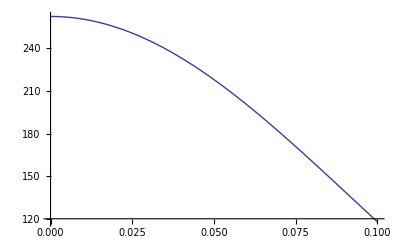
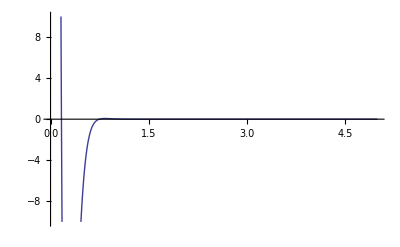

{0.64,Null}

```mathematica
Timing[Module[{ρ=0.300322,λv=0.8,θv=1,κ=0.8944,V=1,S0=0.53,T=11.7371,k=-4,ω},
Print["en 0:",NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,0 +0.5 ⅈ]];
Print[{Plot[{NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +0.5 ⅈ]},{ω,0,0.1},PlotRange->All],
Plot[{NormalHestonCallIntegrand[ρ,λv,θv,κ,V,S0,k,1,1,T,ω +0.5 ⅈ]},{ω,0,5},PlotRange->{-10,10}]}]]
]
```

14.8485

9.19884

5.01683

2.38963

1.02645

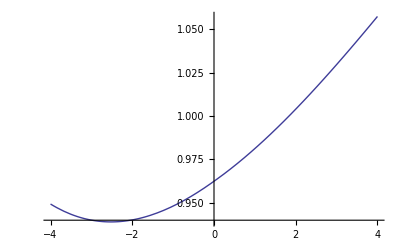
{0.359,-Graphics-}

```mathematica
Timing[Module[{ρ=0.300322,λv=0.45,θv=1,κ=0.8944,V=1,S0=0.53,T=11.7371,strikes,prices,inter},
strikes={-4.0811,-2,0,2,4};
prices=(HestonNormalCallAux[ρ,λv,θv,κ,V,S0,#,T])& /@ strikes;
inter=Interpolation[Table[{strikes[[i]],NormalImplicitVol[S0,strikes[[i]],T,prices[[i]]]},{i,1,Length[strikes]}]];
Plot[{inter[k]},{k,-4,4},
PlotLegend->{"L=1","L=2","L=2.5","L=3"},LegendPosition->{1,0},PlotRange->All]]]
```

## Degenerescence vers la BiLognormale

## Cas BiLognormal

### Formule du bilog spreadoption

```mathematica
phi[x_]:=Exp[-x^2/2]/Sqrt[2Pi]
```

```mathematica
Nd[x_]:=(Erf[x/(√2)]+1)/2
```

```mathematica
LogNormalSpreadDigitaleCall[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=NIntegrate[phi[x]Nd[-(Log[(k+S2 E^(-1/2 sig2^2 t+sig2 Sqrt[t] x))/(S1 E^(-1/2 sig1^2 t))]-rho sig1 Sqrt[t] x)/(√(1-rho^2) sig1 √t)],{x,-∞,-1,+∞}]
```

```mathematica
LogNormalSpreadDigitaleCallN[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=CoeffBasedIntegrate[(Nd[-(Log[(k+S2 E^(-1/2 sig2^2 t+sig2 Sqrt[t] #))/(S1 E^(-1/2 sig1^2 t))]-rho sig1 Sqrt[t] #)/(√(1-rho^2) sig1 √t)])&,ModifiedHermiteCoeffs[20]]
```

```mathematica
LogNormalSpreadDigitaleCallN[S1_,S2_,sig1_,sig2_,rho_,k_,t_,nbsteps_]:=CoeffBasedIntegrate[(Nd[-(Log[(k+S2 E^(-1/2 sig2^2 t+sig2 Sqrt[t] #))/(S1 E^(-1/2 sig1^2 t))]-rho sig1 Sqrt[t] #)/(√(1-rho^2) sig1 √t)])&,ModifiedHermiteCoeffs[nbsteps]]
```

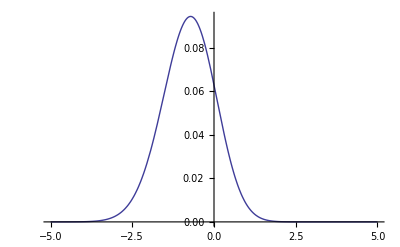

```mathematica
Module[{S1=0.05,S2=0.045,sig1=0.2,sig2=0.3,k=0.01,rho=0.92,t=1},Plot[phi[x]Nd[-(Log[(k+S2 E^(-1/2 sig2^2 t+sig2 Sqrt[t] x))/(S1 E^(-1/2 sig1^2 t))]-rho sig1 Sqrt[t] x)/(√(1-rho^2) sig1 √t)],{x,-5,5}]]
```

```mathematica
Module[{S1=0.05,S2=0.045,sig1=0.2,sig2=0.3,k=0.01,rho=0.2,t=1},LogNormalSpreadDigitaleCall2[S1,S2,sig1,sig2,rho,k,t]]
```

0.385161

```mathematica
Module[{S1=0.05,S2=0.045,sig1=0.2,sig2=0.3,k=0.01,rho=0.2,t=1,nb=20},LogNormalSpreadDigitaleCall[S1,S2,sig1,sig2,rho,k,t,nb]]
```

0.385162

```mathematica
Positive
```

```mathematica
LogNormalSpreadDigitaleCall[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=If[k>=0,LogNormalSpreadDigitaleCallN[S1 ,S2 ,sig1,sig2,rho,k,t],1-LogNormalSpreadDigitaleCallN[S2 ,S1 ,sig2,sig1,rho,-k,t]]
```

```mathematica
MesureQTLogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=LogNormalSpreadDigitaleCall[S1 ,S2 ,sig1,sig2,rho,k,t]
```

```mathematica
MesureQ1LogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=LogNormalSpreadDigitaleCall[S1 Exp[sig1^2 t],S2 Exp[rho sig1 sig2 t],sig1,sig2,rho,k,t]
```

```mathematica
MesureQ2LogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=LogNormalSpreadDigitaleCall[S1 Exp[rho sig1 sig2 t],S2 Exp[sig2^2 t],sig1,sig2,rho,k,t]
```

```mathematica
LogNormalSpreadDigitaleCall[S1_,S2_,sig1_,sig2_,rho_,k_,t_,nb_]:=If[k>=0,LogNormalSpreadDigitaleCallN[S1 ,S2 ,sig1,sig2,rho,k,t,nb],1-LogNormalSpreadDigitaleCallN[S2 ,S1 ,sig2,sig1,rho,-k,t,nb]]
```

```mathematica
MesureQTLogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_,nb_]:=LogNormalSpreadDigitaleCall[S1 ,S2 ,sig1,sig2,rho,k,t,nb]
```

```mathematica
MesureQ1LogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_,nb_]:=LogNormalSpreadDigitaleCall[S1 Exp[sig1^2 t],S2 Exp[rho sig1 sig2 t],sig1,sig2,rho,k,t,nb]
```

```mathematica
MesureQ2LogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_,t_,nb_]:=LogNormalSpreadDigitaleCall[S1 Exp[rho sig1 sig2 t],S2 Exp[sig2^2 t],sig1,sig2,rho,k,t,nb]
```

```mathematica
E[S2 Subscript[1, S1-S2>K]]=S2-E[S2 Subscript[1, S1-S2<K]]=S2-E[S2 Subscript[1, S2-S1>-K]]
```

```mathematica
MesureQ2LogNormalSpreadDigitaleZ[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=1-MesureQ1LogNormalSpreadDigitale[S2,S1,sig2,sig1,rho,-k,t]
```

```mathematica
Module[{S1=0.05,S2=0.051,sig1=0.2,sig2=0.3,rho=0.9,k=0.004,t=10},{MesureQ2LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t],MesureQ2LogNormalSpreadDigitaleZ[S1,S2,sig1,sig2,rho,k,t]}]
```

{0.326645,0.326645}

```mathematica
Module[{S1=0.05,S2=0.051,sig1=0.2,sig2=0.3,rho=0.9,k=0.004,t=10},{MesureQ2LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t,20],MesureQ2LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t,12]}]
```

{0.326607,0.326616}

```mathematica
LogNormalSpreadOption[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=S1 MesureQ1LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t]-S2 MesureQ2LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t]-k MesureQTLogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t]
```

```mathematica
LogNormalSpreadOption[S1_,S2_,sig1_,sig2_,rho_,k_,t_,nb_]:=S1 MesureQ1LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t,nb]-S2 MesureQ2LogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t,nb]-k MesureQTLogNormalSpreadDigitale[S1,S2,sig1,sig2,rho,k,t,nb]
```

```mathematica
Clear[MesureQTLogNormalSpreadDigitale]
```

```mathematica
MesureQTLogNormalSpreadDigitale[0.05,0.051,0.2,0.3,0.9,0.02,10,12]
```

0.123138

```mathematica
?MesureQTLogNormalSpreadDigitale
```

Global`MesureQTLogNormalSpreadDigitale

MesureQTLogNormalSpreadDigitale[S1_,S2_,sig1_,sig2_,rho_,k_Positive,t_,nb_]:=LogNormalSpreadDigitaleCallN[S1,S2,sig1,sig2,rho,k,t,nb]

```mathematica
Module[{S1=0.05,S2=0.051,sig1=0.2,sig2=0.3,rho=0.9,k=0.02,t=10},LogNormalSpreadOption[S1,S2,sig1,sig2,rho,k,t,12]]
```

0.00361177-0.02 MesureQTLogNormalSpreadDigitale[0.05,0.051,0.2,0.3,0.9,0.02,10,12]

### Smile normal du bilog spreadoption

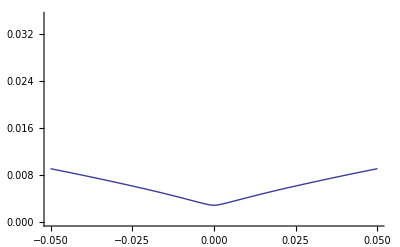

```mathematica
Module[{S1=0.05,S2=0.05,sig1=0.4,sig2=0.4,rho=0.99,k=0.02,t=10,strikes=Table[0.01i,{i,-5,5,0.1}]},ListPlot[Table[{strikes[[i]],NormalImplicitVol[S1-S2,strikes[[i]],t,LogNormalSpreadOption[S1,S2,sig1,sig2,rho,strikes[[i]],t]]},{i,1,Length[strikes]}],PlotRange->{0,0.035},Joined->True]]
```

### Effet de mean reversion des underlyings

Introduction de la mean reversion  pour expliquer l' effet moustache

d[Log[x]] = λ (A - Log[x]) dt + σ dW

y = Log[x]

dy = λ (A - y) dt + σ dW

y(T)=A+(y(0)-A)ⅇ^(-λ t)+ⅇ^-at W̄((ⅇ^(2 a t)-1)/(2a)σ^2)

si je suppose y (0) - A

y(T)=A+W̄((1-ⅇ^(-2 a_1 t))/(2 a_1)σ^2)

si on se donne deux variables

y_1(T)=A_1+ⅇ^-a_1t OverBar[W_1]((1-ⅇ^(-2 a_1 t))/(2 a_1)σ_1^2)

y_2(T)=A_2+ⅇ^-a_2t OverBar[W_2]((1-ⅇ^(-2 a_2 t))/(2 a_2)σ_2^2)

on suppose en plus que OverBar[W_1].OverBar[W_2]=ρ_eff dt

ⅇ^y_1-ⅇ^y_2 revient a examiner deux processus lognormaux avec une  vol_i = √((1-ⅇ^(-2 a_i T))/(2 a_i T))σ_i

Donc pas d' effet moustache (diminution de la pente de smile pour les strike loin de la monaie) a priori

```mathematica
Densité
```

```mathematica
Simplify[D[phi[x]Nd[-(Log[(k+S2 E^(-1/2 sig2^2 t+sig2 Sqrt[t] x))/(S1 E^(-1/2 sig1^2 t))]-rho sig1 Sqrt[t] x)/(√(1-rho^2) sig1 √t)],{k,1}]]
```

-(ⅇ^(1/2 (-x^2+((-rho sig1 √t x+Log[(ⅇ^((sig1^2 t)/2) (k+ⅇ^(-(sig2^2 t)/2+sig2 √t x) S2))/S1])^2)/((-1+rho^2) sig1^2 t))))/(2 π √(1-rho^2) (k+ⅇ^(-(sig2^2 t)/2+sig2 √t x) S2) sig1 √t)

```mathematica
LogNormalSpreadDensity[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=CoeffBasedIntegrate[((ⅇ^(1/2 (-#^2+((-rho sig1 √t #+Log[(ⅇ^((sig1^2 t)/2) (k+ⅇ^(-(sig2^2 t)/2+sig2 √t#) S2))/S1])^2)/((-1+rho^2) sig1^2 t))))/(2 π √(1-rho^2) (k+ⅇ^(-(sig2^2 t)/2+sig2 √t #) S2) sig1 √t))&,ModifiedHermiteCoeffs[20]]
```

```mathematica
Module[{S1=0.05,S2=0.048,τ=5,
VolS1=0.01,VolS2=0.01,Correl12=0.9,k=0.001},LogNormalSpreadDensity[S1,S2,√VolS1,√VolS2,Correl12,k,τ]]
```

23.6713

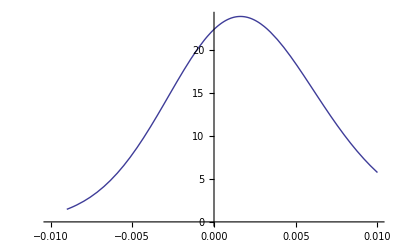

```mathematica
Module[{S1=0.05,S2=0.048,τ=5,
VolS1=0.01,VolS2=0.01,Correl12=0.9},Plot[LogNormalSpreadDensity[S1,S2,√VolS1,√VolS2,Correl12,k,τ],{k,-0.01,0.01}]]
```

### Projection du bilog sur les normal heston

## NuRhoMinimunNormalHestonFromBilog

```mathematica
NuRhoMinimunNormalHestonFromBilog[S1_,S2_,sig1_,sig2_,Correl12_,τ_,ρ_,λv_,LT_,TrueIniVarSpread_,printflag_,LimitGindinkin_]:=
Module[{convexity,convexityTable,VS,DeltaS=0.005,κtable,κ,κinter,prices,κsol,opt1,opt2,opt3,vol1,vol2,vol3,
pente,vols,ρtable,penteTable,ρinter,ρsol,ρs,V0Table,V0inter,V0sol,V0},
If[printflag==1 || MemberQ[printflag,1] ,Print[" @@@@@@  inside NuRhoMinimunNormalHestonFromBilog"]];
opt1=LogNormalSpreadOption[S1,S2,sig1,sig2,Correl12,S1-S2-DeltaS,τ];
opt2=LogNormalSpreadOption[S1,S2,sig1,sig2,Correl12,S1-S2+DeltaS,τ];
opt3=LogNormalSpreadOption[S1,S2,sig1,sig2,Correl12,S1-S2,τ];
vol1=NormalImplicitVol[S1-S2,S1-S2-DeltaS,τ,opt1];
vol2=NormalImplicitVol[S1-S2,S1-S2,τ,opt3];
vol3=NormalImplicitVol[S1-S2,S1-S2+DeltaS,τ,opt2];
If[printflag==1 || MemberQ[printflag,1] ,Print["opt1=",opt1," opt2=",opt2," opt3=",opt3]];
If[printflag==1 || MemberQ[printflag,1] ,Print["vol1=",vol1," vol2=",vol2," vol3=",vol3]];
convexity=vol1+vol3-2*vol2;
pente=vol3-vol1;
If[printflag==1 || MemberQ[printflag,1] ,Print["convexity=",convexity, " pente=",pente," ATMprix=",opt3]];
VS=S1^2 sig1^2+S2^2 sig2^2-2 S1 S2 sig1 sig2  Correl12;
κtable={0.0005,0.001,0.0015,0.0025,0.0035};
prices=Timing[Table[{κtable[[i]],TransHestonNormalCall[ρ,λv,LT TrueIniVarSpread,κtable[[i]],TrueIniVarSpread,S1-S2,{S1-S2-DeltaS,S1-S2,S1-S2+DeltaS},τ,LimitGindinkin]},{i,1,Length[κtable]}]];
If[printflag==1 || MemberQ[printflag,1] ,Print["PriceTable(for convexity)=",prices[[2]] // MatrixForm]];
vols=Map[({#[[1]],
{NormalImplicitVol[S1-S2,S1-S2-DeltaS,τ,#[[2,1]]],
NormalImplicitVol[S1-S2,S1-S2,τ,#[[2,2]]],
NormalImplicitVol[S1-S2,S1-S2+DeltaS,τ,#[[2,3]]]}})&,
prices[[2]]];
If[printflag==1 || MemberQ[printflag,1] ,Print["VolTable(for convexity)=",vols// MatrixForm]];
convexityTable=Map[({#[[2,1]]+#[[2,3]]-2#[[2,2]],#[[1]]})&,vols];
If[printflag==1 || MemberQ[printflag,1] ,Print["convexityTable=",convexityTable // MatrixForm]];
κsol=Apply[Interpolator5points,Append[Flatten[convexityTable],convexity]];
If[printflag==1 || MemberQ[printflag,1] ,Print["κsol=",κsol]];
ρtable={-0.6,-0.3,-0.1,0,0.5,0.8};
prices=Timing[Table[{ρtable[[i]],TransHestonNormalCall[ρtable[[i]],λv,LT TrueIniVarSpread,κsol,TrueIniVarSpread,S1-S2,{S1-S2-DeltaS,S1-S2+DeltaS},τ,LimitGindinkin]},{i,1,Length[ρtable]}]];
If[printflag==1 || MemberQ[printflag,1] ,Print["prices=",prices]];
vols=Map[({#[[1]],
{NormalImplicitVol[S1-S2,S1-S2-DeltaS,τ,#[[2,1]]],
NormalImplicitVol[S1-S2,S1-S2+DeltaS,τ,#[[2,2]]]}})&,
prices[[2]]];
If[printflag==1 || MemberQ[printflag,1] ,Print["vols=",vols]];
penteTable=Map[({#[[2,2]]-#[[2,1]],#[[1]]})&,vols];
If[printflag==1 || MemberQ[printflag,1] ,Print["penteTable=",penteTable // MatrixForm]];
ρsol=Apply[Interpolator6points,Append[Flatten[penteTable],pente]];
If[printflag==1 || MemberQ[printflag,1] ,Print["ρsol=",ρsol]];
{κsol,ρsol}]
```

## NuRhoV0MinimunNormalHestonFromBilog

```mathematica
NuRhoV0MinimunNormalHestonFromBilog[S1_,S2_,sig1_,sig2_,Correl12_,τ_,ρ_,λv_,LT_,TrueIniVarSpread_,printflag_,LimitGindinkin_]:=
Module[{convexity,convexityTable,VS,DeltaS=0.005,κtable,κ,κinter,prices,κsol,opt1,opt2,opt3,vol1,vol2,vol3,
pente,vols,ρtable,penteTable,ρinter,ρsol,ρs,V0Table,V0inter,V0sol,V0,κsol2,V0sol2},
If[printflag==1 || MemberQ[printflag,1] ,Print[" @@@@@@  inside NuRhoV0MinimunNormalHestonFromBilog"]];
Print["S1=",S1," S2=",S2," sig1=",sig1," sig2=",sig2," Correl12=",Correl12];
opt1=LogNormalSpreadOption[S1,S2,sig1,sig2,Correl12,S1-S2-DeltaS,τ];
opt2=LogNormalSpreadOption[S1,S2,sig1,sig2,Correl12,S1-S2+DeltaS,τ];
opt3=LogNormalSpreadOption[S1,S2,sig1,sig2,Correl12,S1-S2,τ];
vol1=NormalImplicitVol[S1-S2,S1-S2-DeltaS,τ,opt1];
vol2=NormalImplicitVol[S1-S2,S1-S2,τ,opt3];
vol3=NormalImplicitVol[S1-S2,S1-S2+DeltaS,τ,opt2];
If[printflag==1 || MemberQ[printflag,1] ,Print["opt1=",opt1," opt2=",opt2," opt3=",opt3]];
If[printflag==1 || MemberQ[printflag,1] ,Print["vol1=",vol1," vol2=",vol2," vol3=",vol3]];
convexity=vol1+vol3-2*vol2;
pente=vol3-vol1;
If[printflag==1 || MemberQ[printflag,1] ,Print["convexity=",convexity, " pente=",pente," ATMprix=",opt3]];
VS=S1^2 sig1^2+S2^2 sig2^2-2 S1 S2 sig1 sig2  Correl12;
κtable={0.0005,0.001,0.004,0.005,0.01};
prices=Timing[Table[{κtable[[i]],TransHestonNormalCall[ρ,λv,LT TrueIniVarSpread,κtable[[i]],TrueIniVarSpread,S1-S2,{S1-S2-DeltaS,S1-S2,S1-S2+DeltaS},τ,LimitGindinkin]},{i,1,Length[κtable]}]];
vols=Map[({#[[1]],
{NormalImplicitVol[S1-S2,S1-S2-DeltaS,τ,#[[2,1]]],
NormalImplicitVol[S1-S2,S1-S2,τ,#[[2,2]]],
NormalImplicitVol[S1-S2,S1-S2+DeltaS,τ,#[[2,3]]]}})&,
prices[[2]]];
convexityTable=Map[({#[[2,1]]+#[[2,3]]-2#[[2,2]],Log[#[[1]]]})&,vols];

If[printflag==1 || MemberQ[printflag,1] ,Print["convexityTable=",convexityTable //MatrixForm]];
If[printflag==1 || MemberQ[printflag,1] ,Print["Equivalent nu normalisé=",Map[({#,#/√TrueIniVarSpread})&,κtable] //MatrixForm]];
κsol=Exp[Apply[Interpolator5points,Append[Flatten[convexityTable],convexity]]];
If[printflag==1 || MemberQ[printflag,1] ,Print["κsol=",κsol]];
ρtable={-0.6,-0.3,-0.1,0,0.3,0.6};
prices=Timing[Table[{ρtable[[i]],TransHestonNormalCall[ρtable[[i]],λv,LT TrueIniVarSpread,κsol,TrueIniVarSpread,S1-S2,{S1-S2-DeltaS,S1-S2+DeltaS},τ,LimitGindinkin]},{i,1,Length[ρtable]}]];
If[printflag==1 || MemberQ[printflag,1] ,Print["prices(pour la pente)=",prices[[2]]// MatrixForm]];
vols=Map[({#[[1]],
{NormalImplicitVol[S1-S2,S1-S2-DeltaS,τ,#[[2,1]]],
NormalImplicitVol[S1-S2,S1-S2+DeltaS,τ,#[[2,2]]]}})&,
prices[[2]]];
If[printflag==1 || MemberQ[printflag,1] ,Print["vols=",vols// MatrixForm]];
penteTable=Map[({#[[2,2]]-#[[2,1]],Tanh[#[[1]]]})&,vols];
If[printflag==1 || MemberQ[printflag,1] ,Print["penteTable=",penteTable // MatrixForm]];
ρsol=ArcTanh[Apply[Interpolator6points,Append[Flatten[penteTable],pente]]];
If[printflag==1 || MemberQ[printflag,1] ,Print["ρsol=",ρsol]];
V0Table={0.5 TrueIniVarSpread,0.9 TrueIniVarSpread, TrueIniVarSpread, 1.1 TrueIniVarSpread,2 TrueIniVarSpread};
Print["######## arg=","{ρsol,λv,LT V0Table[,κsol,V0Table,S1-S2,S1-S2,τ,LimitGindinkin}"];
Print["######## arg=",{ρsol,λv,LT V0Table,κsol,V0Table,S1-S2,S1-S2,τ,LimitGindinkin}];
prices=Table[{TransHestonNormalCall[ρsol,λv,LT V0Table[[i]],κsol,V0Table[[i]],S1-S2,S1-S2,τ,LimitGindinkin],V0Table[[i]]},{i,1,Length[V0Table]}];
prices=Prepend[prices,{0,0}];
If[printflag==1 || MemberQ[printflag,1] ,Print["VOptionATMTable=",prices // MatrixForm]];
V0sol=Apply[Interpolator6points,Append[Flatten[prices],opt3]];
If[printflag==1 || MemberQ[printflag,1] ,Print["V0sol=",V0sol]];
prices=Timing[Table[{κtable[[i]],TransHestonNormalCall[ρsol,λv,LT V0sol,κtable[[i]],V0sol,S1-S2,{S1-S2-DeltaS,S1-S2,S1-S2+DeltaS},τ,LimitGindinkin]},{i,1,Length[κtable]}]];
vols=Map[({#[[1]],
{NormalImplicitVol[S1-S2,S1-S2-DeltaS,τ,#[[2,1]]],
NormalImplicitVol[S1-S2,S1-S2,τ,#[[2,2]]],
NormalImplicitVol[S1-S2,S1-S2+DeltaS,τ,#[[2,3]]]}})&,
prices[[2]]];
convexityTable=Map[({#[[2,1]]+#[[2,3]]-2#[[2,2]],Log[#[[1]]]})&,vols];
If[printflag==1 || MemberQ[printflag,1] ,Print["convexityTable=",convexityTable //MatrixForm]];
If[printflag==1 || MemberQ[printflag,1] ,Print["Equivalent nu normalisé=",Map[({#,#/√TrueIniVarSpread})&,κtable] //MatrixForm]];
κsol2=Exp[Apply[Interpolator5points,Append[Flatten[convexityTable],convexity]]];
If[printflag==1 || MemberQ[printflag,1] ,Print["κsol2=",κsol2]];
prices=Table[{TransHestonNormalCall[ρsol,λv,LT V0Table[[i]],κsol2,V0Table[[i]],S1-S2,S1-S2,τ,LimitGindinkin],V0Table[[i]]},{i,1,Length[V0Table]}];
prices=Prepend[prices,{0,0}];
If[printflag==1 || MemberQ[printflag,1] ,Print["VOptionATMTable=",prices // MatrixForm]];
V0sol2=Apply[Interpolator6points,Append[Flatten[prices],opt3]];
If[printflag==1 || MemberQ[printflag,1] ,Print["V0sol2=",V0sol2]];
{κsol2,ρsol,V0sol2}]
```

## Mode2NuRhoV0MinimunNormalHestonFromBilog

```mathematica
Clear[VS]
```

```mathematica
Solve [(VS-ⅇ^(-T λS) VS+Vinf (-1+ⅇ^(-T λS)+T λS))/λS==VarSpread,VS]
```

{{VS→(-Vinf+ⅇ^(T λS) Vinf+ⅇ^(T λS) VarSpread λS-ⅇ^(T λS) T Vinf λS)/(-1+ⅇ^(T λS))}}

```mathematica
Solve [(V0Initial-ⅇ^(-τ λv) V0Initial+V0Initial LTInitial  (-1+ⅇ^(-τ λv)+τ λv))/λv==VarSpread,V0Initial]
```

{{V0Initial→(ⅇ^(λv τ) VarSpread λv)/(-1+ⅇ^(λv τ)+LTInitial-ⅇ^(λv τ) LTInitial+ⅇ^(λv τ) LTInitial λv τ)}}

```mathematica
Mode2NuRhoV0MinimunNormalHestonFromBilog[S1_,S2_,sig1_,sig2_,Correl12_,τ_,ρ_,λv_,LTInitial_,VarSpread_,printflag_]:=
Module[{convexity,convexityTable,VS,DeltaS=0.005,κtable,κ,κinter,prices,κsol,opt1,opt2,opt3,vol1,vol2,vol3,
pente,vols,ρtable,penteTable,ρinter,ρsol,ρs,V0Table,V0inter,V0sol,V0, V0Initial,LTTable,LTsol,LT,initable},
V0Initial=(ⅇ^(λv τ) VarSpread λv)/(-1+ⅇ^(λv τ)+LTInitial-ⅇ^(λv τ) LTInitial+ⅇ^(λv τ) LTInitial λv τ);
opt1=LogNormalSpreadOption[S1,S2,sig1,sig2,Correl12,S1-S2-DeltaS,τ];
opt2=LogNormalSpreadOption[S1,S2,sig1,sig2,Correl12,S1-S2+DeltaS,τ];
opt3=LogNormalSpreadOption[S1,S2,sig1,sig2,Correl12,S1-S2,τ];
vol1=NormalImplicitVol[S1-S2,S1-S2-DeltaS,τ,opt1];
vol2=NormalImplicitVol[S1-S2,S1-S2,τ,opt3];
vol3=NormalImplicitVol[S1-S2,S1-S2+DeltaS,τ,opt2];
If[printflag==1 || MemberQ[printflag,1] ,Print["opt1=",opt1," opt2=",opt2," opt3=",opt3]];
convexity=vol1+vol3-2*vol2;
pente=vol3-vol1;
If[printflag==1 || MemberQ[printflag,1] ,Print["convexity=",convexity, " pente=",pente," ATMprix=",opt3]];
VS=S1^2 sig1^2+S2^2 sig2^2-2 S1 S2 sig1 sig2  Correl12;
κtable={0.0005,0.001,0.002,0.003,0.006,0.01};
prices=Timing[Table[{κtable[[i]],HestonNormalCall[ρ,λv,LTInitial  V0Initial,κtable[[i]],V0Initial,S1-S2,{S1-S2-DeltaS,S1-S2,S1-S2+DeltaS},τ]},{i,1,Length[κtable]}]];
vols=Map[({#[[1]],
{NormalImplicitVol[S1-S2,S1-S2-DeltaS,τ,#[[2,1]]],
NormalImplicitVol[S1-S2,S1-S2,τ,#[[2,2]]],
NormalImplicitVol[S1-S2,S1-S2+DeltaS,τ,#[[2,3]]]}})&,
prices[[2]]];
convexityTable=Map[({#[[1]],#[[2,1]]+#[[2,3]]-2#[[2,2]]})&,vols];
κinter=Interpolation[convexityTable];
If[printflag==1 || MemberQ[printflag,1] ,Print["convexityTable=",convexityTable // MatrixForm]];
κsol=κ /. FindRoot[κinter[κ]==convexity,{κ,0.002,0.0005,0.01}];
If[printflag==1 || MemberQ[printflag,1] ,Print["Solution κsol=",κsol]];
ρtable={-0.8,-0.6,-0.4,-0.2,0,0.5,0.8};
prices=Timing[Table[{ρtable[[i]],HestonNormalCall[ρtable[[i]],λv,LTInitial  V0Initial,κsol,V0Initial,S1-S2,{S1-S2-DeltaS,S1-S2+DeltaS},τ]},{i,1,Length[ρtable]}]];
If[printflag==1 || MemberQ[printflag,1] ,Print["prices=",prices]];
vols=Map[({#[[1]],
{NormalImplicitVol[S1-S2,S1-S2-DeltaS,τ,#[[2,1]]],
NormalImplicitVol[S1-S2,S1-S2+DeltaS,τ,#[[2,2]]]}})&,
prices[[2]]];
If[printflag==1 || MemberQ[printflag,1] ,Print["vols=",vols]];
penteTable=Map[({#[[1]],#[[2,2]]-#[[2,1]]})&,vols];
ρinter=Interpolation[penteTable];
If[printflag==1 || MemberQ[printflag,1] ,Print["penteTable=",penteTable // MatrixForm]];
ρsol=ρs /. FindRoot[ρinter[ρs]==pente,{ρs,0.,-0.8,0.8}];
If[printflag==1 || MemberQ[printflag,1] ,Print["Solution ρsol=",ρsol]];
LTTable={0.5 ,0.9 , 1.1,2 };

initable=Prepend[Table[{LTTable[[i]],  (ⅇ^(λv τ) VarSpread λv)/(-1+ⅇ^(λv τ)+LTTable[[i]]-ⅇ^(λv τ) LTTable[[i]]+ⅇ^(λv τ) LTTable[[i]] λv τ),LTTable[[i]]  (ⅇ^(λv τ) VarSpread λv)/(-1+ⅇ^(λv τ)+LTTable[[i]]-ⅇ^(λv τ) LTTable[[i]]+ⅇ^(λv τ) LTTable[[i]] λv τ)},{i,1,Length[LTTable]}],
{"LT","V0","Theta"}];
If[printflag==1 || MemberQ[printflag,1] ,Print["initable=",initable // MatrixForm]];
prices=Table[{LTTable[[i]],HestonNormalCall[ρsol,λv,LTTable[[i]]  (ⅇ^(λv τ) VarSpread λv)/(-1+ⅇ^(λv τ)+LTTable[[i]]-ⅇ^(λv τ) LTTable[[i]]+ⅇ^(λv τ) LTTable[[i]] λv τ),κsol,(ⅇ^(λv τ) VarSpread λv)/(-1+ⅇ^(λv τ)+LTTable[[i]]-ⅇ^(λv τ) LTTable[[i]]+ⅇ^(λv τ) LTTable[[i]] λv τ),S1-S2,S1-S2,τ]},{i,1,Length[LTTable]}];
If[printflag==1 || MemberQ[printflag,1] ,Print["VOptionATM=",prices // MatrixForm]];
V0inter=Interpolation[prices];
LTsol=LT /. FindRoot[V0inter[LT]==opt3,{LT,0.5 ,2 }];
If[printflag==1 || MemberQ[printflag,1] ,Print["Solution LTsol=",LTsol]];
V0=(ⅇ^(λv τ) VarSpread λv)/(-1+ⅇ^(λv τ)+LTsol-ⅇ^(λv τ) LTsol+ⅇ^(λv τ) LTsol λv τ);
{κsol,ρsol,LTsol V0,V0}]
```

## Proxy simple pour la vol de vol minimale du bilog

```mathematica
Si on calcule de maniere instantanée
```

d(σ1^2 S1^2+σ2^2 S2^2-2ρ σ1 σ2 S1 S2)==(2 σ1^2 S1 dS1+σ2^2 S2 dS2-2ρ σ1 σ2 S1 dS2-22ρ σ1 σ2 S2 dS1 )+drifts

donc partie martingale  ==2( σ1^2 S1 -ρ σ1 σ2 S2 )dS1+2(σ2^2 S2 -ρ σ1 σ2 S1)dS2

==2( σ1^2 S1 -ρ σ1 σ2 S2 )dS1+2(σ2^2 S2 -ρ σ1 σ2 S1)dS2

donc varvar=4( σ1^2 S1 -ρ σ1 σ2 S2 )^2 σ1^2+4(σ2^2 S2 -ρ σ1 σ2 S1)^2 σ2^2+8ρ ( σ1^2 S1 -ρ σ1 σ2 S2 )(σ2^2 S2 -ρ σ1 σ2 S1) σ1 σ2

```mathematica
Simplify[4( σ1^2 S1 -Correl12 σ1 σ2 S2 )^2 σ1^2+4(σ2^2 S2 -Correl12 σ1 σ2 S1 )^2 σ2^2+8Correl12 ( σ1^2 S1 -Correl12 σ1 σ2 S2 )(σ2^2 S2 -Correl12 σ1 σ2 S1) σ1 σ2]
```

4 σ2^4 (Correl12 S1 σ1-S2 σ2)^2+4 σ1^4 (S1 σ1-Correl12 S2 σ2)^2+8 Correl12 σ1^2 σ2^2 (Correl12 S1 σ1-S2 σ2) (-S1 σ1+Correl12 S2 σ2)

```mathematica
ModeMoins3NuMinimunNormalHestonFromBilogProxy[S1_,S2_,σ1_,σ2_,Correl12_,T_]:=
Module[{varvar,VS},
VS=(σ1^2 S1^2+σ2^2 S2^2-2Correl12 σ1 σ2 S1 S2);
varvar=4 σ1^4 (S1 σ1-Correl12 S2 σ2)^2+4 σ2^4 (Correl12 S1 σ1-S2 σ2)^2+8 Correl12 σ1^2 σ2^2 (Correl12 S1 σ1-S2 σ2) (Correl12 S2 σ2-S1 σ1);
{VS,√varvar/√VS}]
```

attention VolS1 = σ1^2 et pareil pour VolS2

```mathematica
Module[{S1=0.05399906,S2=0.05268318,τ=11.737166,
VolS1=0.0251,VolS2=0.024,Correl12=0.9},ModeMoins3NuMinimunNormalHestonFromBilogProxy[S1,S2,√VolS1,√VolS2,Correl12,τ]]
```

{0.0000141194,0.0216257}

## Parametre Heston du bilog

```mathematica
Calcul du {V0,rho nu}
```

```mathematica
LogNormalSpreadDigitaleCallN[S1_,S2_,sig1_,sig2_,rho_,k_,t_]:=CoeffBasedIntegrate[(Nd[-(Log[(k+S2 E^(-1/2 sig2^2 t+sig2 Sqrt[t] #))/(S1 E^(-1/2 sig1^2 t))]-rho sig1 Sqrt[t] #)/(√(1-rho^2) sig1 √t)])&,ModifiedHermiteCoeffs[10]]
```

```mathematica
NormalHestonSmileCalibrate[KList_,PriceList_,WeightList_,S0_,λ_,LT_,T_,nbsteps_,scale_,microratio_]:=Module[{func,gradfunc,V0,rho,nu},
func=Function[{V,ρ,ν},Module[{ff=DerivativeHestonNormalCall[ρ,λ,LT,ν,V,S0,KList,T,nbsteps,scale,microratio,0]},
Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])^2,{i,1,Length[KList]}]]];
gradfunc=Function[{V,ρ,ν},Module[{ff=DerivativeHestonNormalCall[ρ,λ,LT,ν,V,S0,KList,T,nbsteps,scale,microratio]},
{Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[2,i]],{i,1,Length[KList]}],
Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[3,i]],{i,1,Length[KList]}],
Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[4,i]],{i,1,Length[KList]}]
}]];
FindMinimum[func[V0,rho,nu],{{V0,0.00003,0.000001,0.001},{nu,0.001,0.000001,0.01},{rho,0,-0.9,0.9}},
MaxIterations->200,AccuracyGoal->7,Method->"LevenbergMarquardt",
Gradient->gradfunc[V0,rho,nu]] 
]
```

```mathematica
NormalHestonSmileCalibrateV0Fixed[KList_,PriceList_,WeightList_,S0_,V0_,λ_,LT_,T_,nbsteps_,scale_,microratio_]:=Module[{func,gradfunc,rho,nu},
func=Function[{ρ,ν},Module[{ff=DerivativeHestonNormalCall[ρ,λ,LT,ν,V0,S0,KList,T,nbsteps,scale,microratio,0]},
Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])^2,{i,1,Length[KList]}]]];
gradfunc=Function[{ρ,ν},Module[{ff=DerivativeHestonNormalCall[ρ,λ,LT,ν,V0,S0,KList,T,nbsteps,scale,microratio]},
{Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[3,i]],{i,1,Length[KList]}],
Sum[WeightList[[i]](PriceList[[i]]-ff[[1,i]])ff[[4,i]],{i,1,Length[KList]}]
}]];
FindMinimum[{func[rho,nu],(rho>-1)&&(rho<1)},{{nu,0.001,0.000001,0.01},{rho,0,-0.9,0.9}},
MaxIterations->200,AccuracyGoal->8,
Gradient->gradfunc[rho,nu]] 
]
```

```mathematica
HestonFromBilog[S1_,S2_,σ1_,σ2_,Correl12_,T_,λ_,LT_]:=
Module[{strikes,Stdev,volgoaltable,WeightList,nbsteps,scale,microratio,nbstrike,ss,V0,ρ,ν},
Stdev=√T √(S1^2 σ1^2+S2^2 σ2^2-2Correl12 S1 S2 σ1 σ2);Print[Stdev];
strikes={- Stdev/3,-Stdev/6,0,Stdev/6,Stdev/3};Print["strikes=",strikes];
nbstrike=Length[strikes];
volgoaltable=Table[LogNormalSpreadOption[S1,S2,σ1,σ2,Correl12,strikes[[i]],T,12],{i,1,nbstrike}];
WeightList=Table[1,{i,1,nbstrike}];nbsteps=40;scale=8;microratio=5 T^(1/2);
ss=NormalHestonSmileCalibrate[strikes,volgoaltable,WeightList,S1-S2,λ,LT,T,nbsteps,scale,microratio];
Print["optimisation results:",ss];
V0=ss[[2,1,2]];ρ=ss[[2,3,2]];ν=ss[[2,2,2]];
{V0,ρ,ν}
]
```

```mathematica
HestonFromBilogV0Fixed[S1_,S2_,σ1_,σ2_,Correl12_,T_,λ_,LT_]:=
Module[{strikes,Stdev,volgoaltable,WeightList,nbsteps,scale,microratio,nbstrike,ss,V0,ρ,ν},
V0=S1^2 σ1^2+S2^2 σ2^2-2Correl12 S1 S2 σ1 σ2;
Stdev=√(V0 T);Print[Stdev];
strikes={- Stdev/3,-Stdev/6,0,Stdev/6,Stdev/3};Print["strikes=",strikes];
nbstrike=Length[strikes];
volgoaltable=Table[LogNormalSpreadOption[S1,S2,σ1,σ2,Correl12,strikes[[i]],T,12],{i,1,nbstrike}];
WeightList=Table[1,{i,1,nbstrike}];nbsteps=40;scale=8;microratio=5 T^(1/2);
ss=NormalHestonSmileCalibrateV0Fixed[strikes,volgoaltable,WeightList,S1-S2,V0,λ,LT,T,nbsteps,scale,microratio];
Print["optimisation results:",ss];
ρ=ss[[2,2,2]];ν=ss[[2,1,2]];
{V0,ρ,ν}
]
```

```mathematica
Module[{S1=0.055,S2=0.051,T=30,VolS1=0.15,VolS2=0.2,Correl12=0.5,λ=0.1,LT=1.,ss,V0,ρ,ν,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,bilogprices},
HestonFromBilog[S1,S2,VolS1,VolS2,Correl12,T,λ,LT]]
```

0.0513671

strikes={-0.0171224,-0.00856118,0,0.00856118,0.0171224}

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 200 iterations.

{0.000141766,-0.332069,0.0190758}

```mathematica
Module[{S1=0.055,S2=0.051,T=5,VolS1=0.15,VolS2=0.2,Correl12=0.5,λ=0.1,LT=1.,ss,V0,ρ,ν,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,bilogprices},
HestonFromBilogV0Fixed[S1,S2,VolS1,VolS2,Correl12,T,λ,LT]]
```

0.0209705

strikes={-0.00699017,-0.00349509,0,0.00349509,0.00699017}

optimisation results:{5.40649×10^-9,{nu$16055→0.00230478,rho$16055→-0.899442}}

{0.0000879525,-0.899442,0.00230478}

```mathematica
Module[{S1=0.055,S2=0.051,T=5,VolS1=0.15,VolS2=0.2,Correl12=0.5,λ=0.1,LT=1.,ss,V0,ρ,ν,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,bilogprices},
HestonFromBilog[S1,S2,VolS1,VolS2,Correl12,T,λ,LT]]
```

0.0209705

strikes={-0.00699017,-0.00349509,0,0.00349509,0.00699017}

optimisation results:{1.94044×10^-12,{V0$23831→0.0000987108,nu$23831→0.00675444,rho$23831→-0.249316}}

{0.0000987108,-0.249316,0.00675444}

0.0209705

strikes={-0.00699017,-0.00349509,0,0.00349509,0.00699017}

optimisation results:{1.94044×10^-12,{V0$33334→0.0000987108,nu$33334→0.00675444,rho$33334→-0.249316}}

timing for the HestonFromBilog:7.844 sec.

V0=0.0000987108 ρ=-0.249316 ν=0.00675444

0.0209705

strikes={-0.00699017,-0.00349509,0,0.00349509,0.00699017}

optimisation results:{5.40649×10^-9,{nu$42835→0.00230478,rho$42835→-0.899442}}

timing for the HestonFromBilogV0Fixed:7.219 sec.

V0=0.0000879525 ρ=-0.899442 ν=0.00230478

bilogprices={0.0217031,0.0176527,0.0139272,0.0112381,0.010612,0.0100057,0.0077876,0.00550441,0.00376009}

hestonprices={0.0216815,0.0176423,0.0139222,0.0112335,0.0106072,0.0100006,0.00778252,0.00550537,0.00377556}

hestonpricesV0Fixed={0.0215583,0.017565,0.0138948,0.011233,0.0106092,0.010003,0.0077602,0.005387,0.00350771}

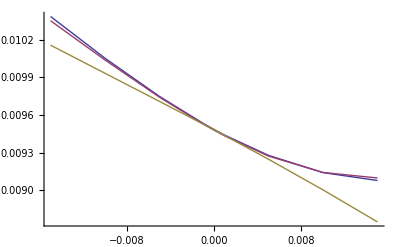
{18.781,-Graphics-}

```mathematica
Timing[Module[{S1=0.055,S2=0.051,T=5,VolS1=0.15,VolS2=0.2,Correl12=0.5,λ=0.1,LT=1.,ss,V0,ρ,ν,ss1,V01,ρ1,ν1,
nbstrike,strikes,bilogvols,hestonprices,hestonvols,hestonprices1,hestonvols1,bilogprices,nbsteps=10,scale=8,microratio=20},
ss=Timing[HestonFromBilog[S1,S2,VolS1,VolS2,Correl12,T,λ,LT]];
V0=ss[[2,1]];ρ=ss[[2,2]];ν=ss[[2,3]];
Print["timing for the HestonFromBilog:",ss[[1]]," sec."];
Print["V0=",V0," ρ=",ρ," ν=",ν];
ss1=Timing[HestonFromBilogV0Fixed[S1,S2,VolS1,VolS2,Correl12,T,λ,LT]];
V01=ss1[[2,1]];ρ1=ss1[[2,2]];ν1=ss1[[2,3]];
Print["timing for the HestonFromBilogV0Fixed:",ss1[[1]]," sec."];
Print["V0=",V01," ρ=",ρ1," ν=",ν1];
strikes={-0.015,-0.01,-0.005,-0.001,0,0.001,0.005,0.01,0.015};nbstrike=Length[strikes];
bilogprices=Table[LogNormalSpreadOption[S1,S2,VolS1,VolS2,Correl12,strikes[[i]],T,12],{i,1,nbstrike}];
bilogvols=Table[NormalImplicitVol[S1-S2,strikes[[i]],T,bilogprices[[i]]],{i,1,nbstrike}];
hestonprices=DerivativeHestonNormalCall[ρ,λ,LT,ν,V0,S1-S2,strikes,T,nbsteps,scale,microratio,0][[1]];
hestonvols=Table[NormalImplicitVol[S1-S2,strikes[[i]],T,hestonprices[[i]]],{i,1,nbstrike}];
hestonprices1=DerivativeHestonNormalCall[ρ1,λ,LT,ν1,V01,S1-S2,strikes,T,nbsteps,scale,microratio,0][[1]];
hestonvols1=Table[NormalImplicitVol[S1-S2,strikes[[i]],T,hestonprices1[[i]]],{i,1,nbstrike}];
Print["bilogprices=",bilogprices];Print["hestonprices=",hestonprices];Print["hestonpricesV0Fixed=",hestonprices1];
ListPlot[{Transpose[{strikes,bilogvols}],Transpose[{strikes,hestonvols}],Transpose[{strikes,hestonvols1}]},Joined->True, PlotLegend->{"bilog", "heston", "hestonV0Fixed"}]
]]
```

## Comparaison avec la BiLognormale

Initial:(S1 | 0.0539991
VolSquareS1 | 0.0251
S2 | 0.0526832
VolSquareS2 | 0.024) Process V1=(V1 | 0.00257258
κ1 | 0.
ρ1 | 0.
 κ1 norm. | 0.) Process V2=(α2 | 0.150091
β2 | 0.147173
κ2 | 0.
ρ2 | 0.
 κ21 norm. | 0.
 κ22 norm. | 0.) Process V3=(V3 | 0.00234
κ3 | 0.
ρ3 | 0.
 κ3 norm. | 0.) T=1.73717

variance attendue du spread:0.0000245278 ecart type equivalent: 0.00495256

S1 0.0539991 S2 0.0526832 VolS1=0.0251 VolS2=0.024 Correl12= 0.9

entering   SmileBiSuperHestonVanillaSpreadOption **************

moments={{0.0218014,0.020846},{0.0436029,0.041692,0.038373}}

VarExpX=0.000135746 VarExpY=0.000123194

VS=0.0000141194 VarVS=0. CoVarSVS=0.

Sig1=0.15843 Sig2=0.154919 Correl12=0.9

****AlphaGenericComputeSpreadOption****

VarRealSpead (Goal)=0.0000266682

NormalTerminalcorrelT=0.9 ExpcorreLT=0.898066

TrueIniVarSpread=0.0000153516

@@@@@@  inside NuRhoMinimunNormalHestonFromBilog

opt1=0.00540418 opt2=0.000453163 opt3=0.00197514

vol1=0.00375452 vol2=0.00375636 vol3=0.00390665

convexity=0.000148434 pente=0.000152127 ATMprix=0.00197514

PriceTable(for convexity)=(0.0005 | {0.00546667,0.00205807,0.000446876}
0.001 | {0.00547602,0.00205171,0.000436686}
0.0015 | {0.00548496,0.00204111,0.000426665}
0.0025 | {0.00550161,0.00200741,0.000408827}
0.0035 | {0.0055161,0.00195858,0.000395951})

VolTable(for convexity)=(0.0005 | {0.0039476,0.00391408,0.00388744}
0.001 | {0.00397572,0.00390198,0.00385612}
0.0015 | {0.00400247,0.00388182,0.00382508}
0.0025 | {0.00405182,0.00381773,0.0037692}
0.0035 | {0.00409432,0.00372487,0.00372834})

convexityTable=(6.88975×10^-6 | 0.0005
0.0000278853 | 0.001
0.0000639019 | 0.0015
0.000185558 | 0.0025
0.000372915 | 0.0035)

κsol=0.0022784

prices={2.156,{{-0.6,{0.00557436,0.000311812}},{-0.3,{0.0055179,0.000388983}},{-0.1,{0.00547769,0.00043493}},{0,{0.00545666,0.000456663}},{0.5,{0.00533888,0.000555994}},{0.8,{0.00525204,0.00060989}}}}

vols={{-0.6,{0.00426167,0.00344838}},{-0.3,{0.00409957,0.00370603}},{-0.1,{0.00398073,0.0038507}},{0,{0.0039173,0.0039173}},{0.5,{0.00354119,0.00420951}},{0.8,{0.00323164,0.00436119}}}

penteTable=(-0.000813292 | -0.6
-0.000393535 | -0.3
-0.000130032 | -0.1
-7.70698×10^-13 | 0
0.000668321 | 0.5
0.00112955 | 0.8)

ρsol=0.11693

Mode 0 :  Numinimum=0.0022784 rhominimum= 0.11693

Normal Heston Parameters=(S0 | 0.00131588
V0 | 0.0000153516
θ | 0.0000153516
λv | 0.1
ρ | 0.11693
ν | 0.0022784
ν normalized | 0.581505
standard dev equi. | 0.00391811)

prices={0.0163186,0.0113472,0.00657941,0.00337287,0.00273393,0.00217541,0.000729513,0.000132689,0.0000183143}

Vols Alpha=(-0.015 | 0.00422657
-0.01 | 0.0040259
-0.005 | 0.00386631
-0.001 | 0.00381473
0 | 0.00381837
0.001 | 0.00382936
0.005 | 0.00393837
0.01 | 0.00416213
0.015 | 0.00441552)

Vols bilog=(-0.015 | 0.00417231
-0.01 | 0.00394193
-0.005 | 0.00377911
-0.001 | 0.00373571
0 | 0.00374038
0.001 | 0.00375152
0.005 | 0.00385526
0.01 | 0.00408146
0.015 | 0.00436249)

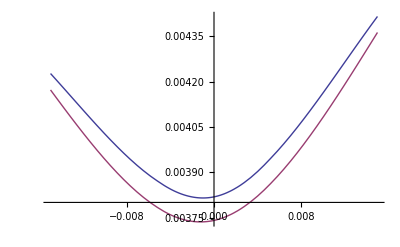

```mathematica
Module[{S1=0.05399906,S2=0.05268318,SpreadStrikes={-0.015,-0.01,-0.005,-0.001,0,0.001,0.005,0.01,0.015},τ=1.737166,
VolS1=0.0251,VolS2=0.024,Correl12=0.9,ρS1=0.,ρS2=0.,ρS3=0.,
κS1=0.00,κS2=0.0,κS3=0.00,
λ=0.1,LTVarianceFactor=1.,gyndinkin=10,printflag=1,mode=1,prices,pricebilog,interprice,interbilog},
prices=PackagedSmileBiSuperHestonVanillaSpreadoptionRapide[S1,S2,SpreadStrikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor,gyndinkin,mode,printflag];
prices=Table[{SpreadStrikes[[i]],NormalImplicitVol[S1-S2,SpreadStrikes[[i]],τ,prices[[i]]]},{i,1,Length[SpreadStrikes]}];
Print["Vols Alpha=",prices // MatrixForm];
pricebilog=Table[{SpreadStrikes[[i]],NormalImplicitVol[S1-S2,SpreadStrikes[[i]],τ,LogNormalSpreadOption[S1,S2,√VolS1,√VolS2,Correl12,SpreadStrikes[[i]],τ]]},{i,1,Length[SpreadStrikes]}];
Print["Vols bilog=",pricebilog // MatrixForm];
interprice=Interpolation[prices];
interbilog=Interpolation[pricebilog];

Plot[{interprice[x],interbilog[x]},{x,First[SpreadStrikes],Last[SpreadStrikes]}, PlotLegend->{"Alpha", "BiLog"}, LegendPosition->{0.8,-0.8}]
]
```

```mathematica
ici une varvar  serait de :
```

```mathematica
√0.000015351568541308277*0.0022784007962428567
```

8.92702×10^-6

```mathematica
mais la bilog parait avoir une varvar superieure.
```

## Calibration

## Calibration de κ et ρ

#### Schema de la calibration

La calibration fonctionne uniquement dans le mode 0

la ou

{numinimum,rhominimum,V0minimim}=
NuRhoV0MinimunNormalHestonFromBilog[S1,S2,Sig1,Sig2,Correl12,τ,ρprojetéIni,λS,LTFactorS ,TrueIniVarSpread,printflag,LimitGindinkin];
V0Effectif=V0minimim;
VarVSTotal=VarVS+numinimum^2 V0minimim;
CoVarSVSTotal=CoVarSVS+rhominimum V0minimim numinimum;
ρprojeté=CoVarSVSTotal/(√(V0minimim VarVSTotal));νprojeté=√(VarVSTotal/V0minimim);ThetaEffectif=LTFactorS  V0minimim;

donc VarVSTotal=νprojeté^2 V0Effectif

et  CoVarSVSTotal = ρprojeté νprojeté  V0Effectif

on calcule alors

{numinimum, rhominimum, V0minimim}

et on deduit :

VarVS=VarVSTotal-numinimum^2 V0minimim

CoVarSVS = CoVarSVSTotal - rhominimum V0minimim numinimum

```mathematica
donc en resumé:
```

VarVS=νprojeté^2 V0Effectif-numinimum^2 V0minimim

CoVarSVS =  ρprojeté νprojeté  V0Effectif - rhominimum V0minimim numinimum

#### Fabrication des solution

```mathematica
{VSObs, VarVSObs, CoVarSVSObs} = Simplify[BiSuperHestonSpreadObservable[S1, S2, alpha2, beta2, rhobase1 - rhos, kappaFact1*kappas, V1, rho2, kappa2, V2, rhobase3 + rhos, kappaFact2*kappas, V3]];
```

```mathematica
rulecovar=Solve[CoVarSVSObs==CoVarSVS,rhos][[1]]
```

{rhos→(CoVarSVS-kappaFact1 kappas rhobase1 S1^3 V1-alpha2^3 kappa2 rho2 S1^3 V2+3 alpha2^2 beta2 kappa2 rho2 S1^2 S2 V2-3 alpha2 beta2^2 kappa2 rho2 S1 S2^2 V2+beta2^3 kappa2 rho2 S2^3 V2+kappaFact2 kappas rhobase3 S2^3 V3)/(-kappaFact1 kappas S1^3 V1-kappaFact2 kappas S2^3 V3)}

```mathematica
VarVSObstrans=VarVSObs /. rulecovar;
```

```mathematica
kappasfunc=Simplify[Solve[VarVSObstrans==VarVS,kappas]];
```

```mathematica
CForm[kappas /.kappasfunc[[1]]]
```

-((2*kappaFact1*kappaFact2*rhobase1*Power(S1,4)*Power(S2,3)*Power(V1,2)*V3 + 2*kappaFact1*kappaFact2*rhobase3*Power(S1,4)*Power(S2,3)*Power(V1,2)*V3 + 
       2*Power(alpha2,2)*kappaFact1*kappaFact2*rhobase1*Power(S1,4)*Power(S2,3)*V1*V2*V3 - 
       2*alpha2*beta2*kappaFact1*kappaFact2*rhobase1*Power(S1,4)*Power(S2,3)*V1*V2*V3 + 
       2*Power(alpha2,2)*kappaFact1*kappaFact2*rhobase3*Power(S1,4)*Power(S2,3)*V1*V2*V3 - 
       2*alpha2*beta2*kappaFact1*kappaFact2*rhobase3*Power(S1,4)*Power(S2,3)*V1*V2*V3 - 
       2*alpha2*beta2*kappaFact1*kappaFact2*rhobase1*Power(S1,3)*Power(S2,4)*V1*V2*V3 + 
       2*Power(beta2,2)*kappaFact1*kappaFact2*rhobase1*Power(S1,3)*Power(S2,4)*V1*V2*V3 - 
       2*alpha2*beta2*kappaFact1*kappaFact2*rhobase3*Power(S1,3)*Power(S2,4)*V1*V2*V3 + 
       2*Power(beta2,2)*kappaFact1*kappaFact2*rhobase3*Power(S1,3)*Power(S2,4)*V1*V2*V3 + 
       2*kappaFact1*kappaFact2*rhobase1*Power(S1,3)*Power(S2,4)*V1*Power(V3,2) + 
       2*kappaFact1*kappaFact2*rhobase3*Power(S1,3)*Power(S2,4)*V1*Power(V3,2) + 
       Sqrt(16*Power(kappaFact1,2)*Power(kappaFact2,2)*Power(rhobase1 + rhobase3,2)*Power(S1,6)*Power(S2,6)*Power(V1,2)*Power(V3,2)*
           Power(S1*(V1 + alpha2*(alpha2 - beta2)*V2) + S2*(-(alpha2*beta2*V2) + Power(beta2,2)*V2 + V3),2) - 
          4*(Power(kappaFact1,3)*Power(S1,7)*Power(V1,2) + Power(kappaFact1,2)*kappaFact2*Power(S1,4)*Power(S2,3)*V1*V3 + 
             kappaFact1*Power(kappaFact2,2)*Power(S1,3)*Power(S2,4)*V1*V3 + Power(kappaFact2,3)*Power(S2,7)*Power(V3,2))*
           (Power(beta2,4)*Power(kappa2,2)*kappaFact1*Power(S1,3)*Power(S2,4)*V1*V2 + 
             4*Power(beta2,3)*kappa2*kappaFact1*rho2*Power(S1,4)*Power(S2,3)*Power(V1,2)*V2 + 
             4*Power(beta2,5)*kappa2*kappaFact1*rho2*Power(S1,3)*Power(S2,4)*V1*Power(V2,2) + 
             Power(beta2,4)*Power(kappa2,2)*kappaFact2*Power(S2,7)*V2*V3 + 4*Power(beta2,3)*kappa2*kappaFact1*rho2*Power(S1,3)*Power(S2,4)*V1*V2*V3 + 
             4*Power(alpha2,5)*kappa2*kappaFact2*rho2*Power(S1,4)*Power(S2,3)*Power(V2,2)*V3 + 
             4*CoVarSVS*(kappaFact1*Power(S1,3)*V1*(S1*V1 + Power(alpha2,2)*S1*V2 - alpha2*beta2*S2*V2) - 
                kappaFact2*Power(S2,3)*V3*(-(alpha2*beta2*S1*V2) + Power(beta2,2)*S2*V2 + S2*V3)) - 
             4*alpha2*Power(beta2,2)*kappa2*S1*Power(S2,2)*V2*
              (rho2*(S1*V1 + S2*V3)*(2*kappaFact1*Power(S1,3)*V1 - kappaFact2*Power(S2,3)*V3) + 
                Power(beta2,2)*rho2*S2*V2*(kappaFact1*Power(S1,2)*(3*S1 + S2)*V1 - kappaFact2*Power(S2,3)*V3) + 
                beta2*kappa2*S2*(kappaFact1*Power(S1,3)*V1 + kappaFact2*Power(S2,3)*V3)) - 
             4*Power(alpha2,3)*kappa2*Power(S1,2)*S2*V2*(-(kappaFact2*rho2*S1*Power(S2,2)*V3*(S1*V1 + S2*V3)) + 
                beta2*kappa2*S1*(kappaFact1*Power(S1,3)*V1 + kappaFact2*Power(S2,3)*V3) + 
                Power(beta2,2)*rho2*V2*(kappaFact1*Power(S1,3)*(S1 + 3*S2)*V1 - 3*kappaFact2*Power(S2,3)*(S1 + S2)*V3)) + 
             2*Power(alpha2,2)*beta2*kappa2*S1*S2*V2*(2*rho2*S1*(S1*V1 + S2*V3)*(kappaFact1*Power(S1,3)*V1 - 2*kappaFact2*Power(S2,3)*V3) + 
                3*beta2*kappa2*S1*S2*(kappaFact1*Power(S1,3)*V1 + kappaFact2*Power(S2,3)*V3) - 
                2*Power(beta2,2)*rho2*S2*V2*(-3*kappaFact1*Power(S1,3)*(S1 + S2)*V1 + kappaFact2*Power(S2,3)*(3*S1 + S2)*V3)) + 
             Power(alpha2,4)*kappa2*Power(S1,3)*V2*(kappa2*(kappaFact1*Power(S1,4)*V1 + kappaFact2*S1*Power(S2,3)*V3) - 
                4*beta2*rho2*S2*V2*(-(kappaFact1*Power(S1,3)*V1) + kappaFact2*Power(S2,2)*(S1 + 3*S2)*V3)) - kappaFact1*Power(S1,3)*V1*VarVS - 
             kappaFact2*Power(S2,3)*V3*VarVS))/2.)/
     (Power(kappaFact1,3)*Power(S1,7)*Power(V1,2) + Power(kappaFact1,2)*kappaFact2*Power(S1,4)*Power(S2,3)*V1*V3 + 
       kappaFact1*Power(kappaFact2,2)*Power(S1,3)*Power(S2,4)*V1*V3 + Power(kappaFact2,3)*Power(S2,7)*Power(V3,2)))

```mathematica
CForm[rhos /.rulecovar[[1]]]
```

(CoVarSVS - kappaFact1*kappas*rhobase1*Power(S1,3)*V1 - Power(alpha2,3)*kappa2*rho2*Power(S1,3)*V2 + 
     3*Power(alpha2,2)*beta2*kappa2*rho2*Power(S1,2)*S2*V2 - 3*alpha2*Power(beta2,2)*kappa2*rho2*S1*Power(S2,2)*V2 + 
     Power(beta2,3)*kappa2*rho2*Power(S2,3)*V2 + kappaFact2*kappas*rhobase3*Power(S2,3)*V3)/
   (-(kappaFact1*kappas*Power(S1,3)*V1) - kappaFact2*kappas*Power(S2,3)*V3)

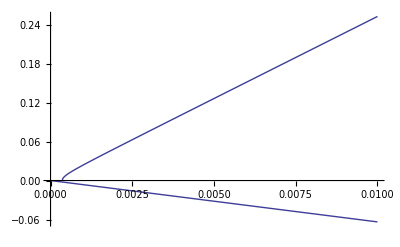

```mathematica
Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ,S1,S2,α2,β2,LTFactorS=1.5,λS=0.15,gyndinkin=1,prices,VarRealSpead=0.0000987781,VarVS,νfinal,ρprojeté=0.1,TrueIniVarSpread=7.959278543949322*10^(-6),kappaFact1=1,kappaFact2=1,
rhobase1=0.1,rhobase2=0.1},
ρ1=-0.3;λv1=0.15;θv1=0.001;κ1=0.5;V1=0.001;
ρ2=-0.5;λv2=0.15;θv2=0.05;κ2=0.5;V2=0.01;
ρ3=-0.1;λv3=0.15;θv3=0.001;κ3=0.5;V3=0.001;
τ=10;S1=0.05;S2=0.05;α2=1;β2=1;
Plot[VarVS=νfinal^2 TrueIniVarSpread;CalibrateKappaSpecifBiSuperHestonSmileParams[S1,S2, ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,LTFactorS,λS,τ,TrueIniVarSpread,νfinal,ρprojeté,kappaFact1,kappaFact2,rhobase1,rhobase2],{νfinal,0.0000,0.01}]]
```

```mathematica
ρ1->rhobase1-ρs
```

```mathematica
ρ3->rhobase3+ρs
```

```mathematica
κ1->kappaFact1 κs,κ3->kappaFact2 κs
```

```mathematica
Minimize
```

## Calcul des derivées packagées

β2=((1+Correl12)√VolS2)/2;α2=(2Correl12)/(1+Correl12)√VolS1;V1=VolS1-α2^2;V3=VolS2-β2^2;V2=1;
κ1=κS1;κ2=κS2;κ3=κS3;
ρ1=ρS1;ρ2=ρS2;ρ3=ρS3;

### cas U1

V1_eff=VolS1(1-(4 Correl12^2)/(1+Correl12)^2)
V2_eff=VolS1((4 Correl12^2)/(1+Correl12)^2);κ2_eff=(2Correl12)/(1+Correl12)√VolS1 κ2

(∂ U1)/(∂ VolS1)=(∂ U1)/(∂ V1_eff) (∂ V1_eff)/(∂ VolS1)+(∂ U1)/(∂ V2_eff) (∂ V2_eff)/(∂ VolS1)+(∂ U1)/(∂ κ2_eff) (∂ κ2_eff)/(∂ VolS1)
=(∂ U1)/(∂ V1_eff) (1-(4 Correl12^2)/(1+Correl12)^2)+(∂ U1)/(∂ V2_eff) ((4 Correl12^2)/(1+Correl12)^2)+(∂ U1)/(∂ κ2_eff) (2Correl12)/(1+Correl12)κ2/(2 √VolS1)

(∂ U1)/(∂ VolS2)=0

(∂ U1)/(∂ κ2)=(∂ U1)/(∂ κ2_eff) (2Correl12)/(1+Correl12)√VolS1

(∂ U1)/(∂ ρ2)=(∂ U1)/(∂ ρ2_eff)

### cas U2

V1_eff=VolS2(1-(1+Correl12)^2/4)
V2_eff=VolS2((1+Correl12)^2/4);κ2_eff=(1+Correl12)/2 √VolS2 κ2

(∂ U2)/(∂ VolS1)=0

(∂ U2)/(∂ VolS2)=(∂ U2)/(∂ V1_eff) (1-(1+Correl12)^2/4)+(∂ U2)/(∂ V2_eff) ((1+Correl12)^2/4)+(∂ U2)/(∂ κ2_eff) (1+Correl12)/2 κ2/(2 √VolS2)

(∂ U2)/(∂ κ2)=(∂ U2)/(∂ κ2_eff) (1+Correl12)/2 √VolS2

(∂ U2)/(∂ ρ2)=(∂ U2)/(∂ ρ2_eff)

## Calibration analytique

```mathematica
SmileBiSuperHestonVanillaSmileParameters[S1_,S2_, ρ1_,λv1_,θv1_,κ1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,ρ3_,λv3_,θv3_,κ3_,V3_,α2_,β2_,LTFactorS_,λS_,τ_]:=Module[
{Z1,Z2,VarExpX,VarExpY,VarRealSpead,ρprojeté,νprojeté,ExpcorreLT,driftVarVS,
μX,μY,μXX,μYY,μXY,μXXX,μXXY,μXYY,μYYY,μXXXX,μXXXY,μXXYY,μXYYY,μYYYY,
μ1,μ2,μ3,μ4,V0Generateur,TrueIniVarSpread,x,prices,NormalTerminalcorrelT,ρmodel,VarVS,CoVarSVS,VS,νfinal},

(*   determination de la correl  *)
{{μX,μY},{μXX,μYY,μXY}}=
{{D1XBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ],
D1YBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ]},
{D2XXBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ],
D2YYBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ],
D2XYBiSuperLogNormalHestonFondamentalTransform[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ]}};
NormalTerminalcorrelT=μXY/√(μXX μYY);
ExpcorreLT=CorrelationExponentialAdjuster[μXX,μYY,NormalTerminalcorrelT];
VarExpX=LogHestonNormalVarianceProxy[ρ1,λv1,θv1,κ1,V1,ρ2,λv2,α2^2 θv2,α2 κ2,α2^2 V2,S1,τ];
VarExpY=LogHestonNormalVarianceProxy[ρ3,λv3,θv3,κ3,V3,ρ2,λv2,β2^2 θv2,β2 κ2,β2^2 V2,S2,τ];
VarRealSpead=VarExpX+VarExpY-2ExpcorreLT √(VarExpX VarExpY);
TrueIniVarSpread=(ⅇ^(λS τ) VarRealSpead λS)/(-1+LTFactorS+ⅇ^(λS τ) (1+LTFactorS (-1+λS τ)));
VarVS=S1^2 V1 (2 S1 (V1+V2 α2^2)-2 S2 V2 α2 β2) (2 S1 V1+2 V2 α2 (S1 α2-S2 β2)+S1 κ1 ρ1)+S1^3 V1 κ1 (-2 S2 V2 α2 β2 ρ1+S1 (κ1+2 (V1+V2 α2^2) ρ1))+V2 (S1 α2-S2 β2)^2 κ2 ((S1 α2-S2 β2)^2 κ2+(2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) ρ2)+V2 (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) (-2 S1 S2 α2 β2 (V2 (α2+β2)+κ2 ρ2)+S1^2 α2 (2 V1+α2 (2 V2 α2+κ2 ρ2))+S2^2 β2 (2 V3+β2 (2 V2 β2+κ2 ρ2)))+S2^3 V3 κ3 (-2 S1 V2 α2 β2 ρ3+S2 (κ3+2 (V3+V2 β2^2) ρ3))+2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)) (-2 S1 V2 α2 β2+S2 (2 V3+2 V2 β2^2+κ3 ρ3));
CoVarSVS=2 S1^2 V1 (S1 (V1+V2 α2^2)-S2 V2 α2 β2)-2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2))+V2 (S1 α2-S2 β2) (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2))+S1^3 V1 κ1 ρ1+V2 (S1 α2-S2 β2)^3 κ2 ρ2-S2^3 V3 κ3 ρ3;
VS=S1^2 V1+S2^2 V3+V2 (S1 α2-S2 β2)^2;
ρprojeté=CoVarSVS/(√(VS VarVS));νprojeté=√(VarVS/VS);νfinal=νprojeté √(VS/TrueIniVarSpread);{TrueIniVarSpread,ρprojeté,νfinal}
]
```

```mathematica
expρ=Simplify[(2 S1^2 V1 (S1 (V1+V2 α2^2)-S2 V2 α2 β2)-2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2))+V2 (S1 α2-S2 β2) (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2))+S1^3 V1 κ1 ρ1+V2 (S1 α2-S2 β2)^3 κ2 ρ2-S2^3 V3 κ3 ρ3 )/.{ρ1->rhobase1-ρs,ρ3->rhobase3+ρs}]
```

2 S1^2 V1 (S1 (V1+V2 α2^2)-S2 V2 α2 β2)-2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2))+V2 (S1 α2-S2 β2) (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2))+V2 (S1 α2-S2 β2)^3 κ2 ρ2+S1^3 V1 κ1 (rhobase1-ρs)-S2^3 V3 κ3 (rhobase3+ρs)

```mathematica
Solve[CoVarSVS==expρ,ρs]
```

{{ρs→1/(S1^3 V1 κ1+S2^3 V3 κ3)(-CoVarSVS+2 S1^3 V1^2-2 S2^3 V3^2+4 S1^3 V1 V2 α2^2+2 S1^3 V2^2 α2^4-4 S1^2 S2 V1 V2 α2 β2+4 S1 S2^2 V2 V3 α2 β2-4 S1^2 S2 V2^2 α2^3 β2-4 S2^3 V2 V3 β2^2-2 S1^2 S2 V2^2 α2^2 β2^2+2 S1 S2^2 V2^2 α2^2 β2^2+4 S1 S2^2 V2^2 α2 β2^3-2 S2^3 V2^2 β2^4+rhobase1 S1^3 V1 κ1-rhobase3 S2^3 V3 κ3+S1^3 V2 α2^3 κ2 ρ2-3 S1^2 S2 V2 α2^2 β2 κ2 ρ2+3 S1 S2^2 V2 α2 β2^2 κ2 ρ2-S2^3 V2 β2^3 κ2 ρ2)}}

```mathematica
expκ=Simplify[Simplify[Simplify[S1^2 V1 (2 S1 (V1+V2 α2^2)-2 S2 V2 α2 β2) (2 S1 V1+2 V2 α2 (S1 α2-S2 β2)+S1 κ1 ρ1)+S1^3 V1 κ1 (-2 S2 V2 α2 β2 ρ1+S1 (κ1+2 (V1+V2 α2^2) ρ1))+V2 (S1 α2-S2 β2)^2 κ2 ((S1 α2-S2 β2)^2 κ2+(2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) ρ2)+V2 (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) (-2 S1 S2 α2 β2 (V2 (α2+β2)+κ2 ρ2)+S1^2 α2 (2 V1+α2 (2 V2 α2+κ2 ρ2))+S2^2 β2 (2 V3+β2 (2 V2 β2+κ2 ρ2)))+S2^3 V3 κ3 (-2 S1 V2 α2 β2 ρ3+S2 (κ3+2 (V3+V2 β2^2) ρ3))+2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)) (-2 S1 V2 α2 β2+S2 (2 V3+2 V2 β2^2+κ3 ρ3))/.{ρ1->rhobase1-ρs,ρ3->rhobase3+ρs}]/.{ρs->1/(-S1^3 V1 κ1-S2^3 V3 κ3)(CoVarSVS-2 S1^3 V1^2+2 S2^3 V3^2-4 S1^3 V1 V2 α2^2-2 S1^3 V2^2 α2^4+4 S1^2 S2 V1 V2 α2 β2-4 S1 S2^2 V2 V3 α2 β2+4 S1^2 S2 V2^2 α2^3 β2+4 S2^3 V2 V3 β2^2+2 S1^2 S2 V2^2 α2^2 β2^2-2 S1 S2^2 V2^2 α2^2 β2^2-4 S1 S2^2 V2^2 α2 β2^3+2 S2^3 V2^2 β2^4-rhobase1 S1^3 V1 κ1+rhobase3 S2^3 V3 κ3-S1^3 V2 α2^3 κ2 ρ2+3 S1^2 S2 V2 α2^2 β2 κ2 ρ2-3 S1 S2^2 V2 α2 β2^2 κ2 ρ2+S2^3 V2 β2^3 κ2 ρ2)}]/.{κ1->kappaFact1 κs,κ3->kappaFact2 κs}]
```

(4 CoVarSVS (kappaFact1 S1^3 V1 (S1 (V1+V2 α2^2)-S2 V2 α2 β2)-kappaFact2 S2^3 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2))) κs+kappaFact1 S1^7 V1 κs (-4 V1^3-12 V1^2 V2 α2^2-12 V1 V2^2 α2^4-4 V2^3 α2^6+V2 α2^4 κ2^2+kappaFact1^2 V1 κs^2)+kappaFact2 S2^7 V3 κs (-4 V3^3-12 V2 V3^2 β2^2-12 V2^2 V3 β2^4-4 V2^3 β2^6+V2 β2^4 κ2^2+kappaFact2^2 V3 κs^2)+4 kappaFact1 S1^6 S2 V1 V2 α2 β2 κs (4 V1^2+V1 α2 (8 V2 α2+κ2 ρ2)+α2^2 (4 V2^2 α2^2-κ2^2+V2 (α2-β2) κ2 ρ2))+4 kappaFact2 S1 S2^6 V2 V3 α2 β2 κs (4 V3^2+V3 β2 (8 V2 β2+κ2 ρ2)+β2^2 (4 V2^2 β2^2-κ2^2+V2 (-α2+β2) κ2 ρ2))-2 kappaFact1 S1^5 S2^2 V1 V2 α2 β2 κs (2 V1 (2 V3+β2 (5 V2 α2+2 V2 β2+2 κ2 ρ2))+α2 (-2 V2^2 β2 (-5 α2^2-2 α2 β2+β2^2)-κ2 (3 β2 κ2+2 V3 ρ2)+V2 (V3 (4 α2-2 β2)+6 (α2-β2) β2 κ2 ρ2)))+2 kappaFact2 S1^2 S2^5 V2 V3 α2 β2 κs (2 V1 (-2 V3+β2 (V2 α2-2 V2 β2+κ2 ρ2))+α2 (2 V2^2 β2 (α2^2-2 α2 β2-5 β2^2)+κ2 (3 β2 κ2-4 V3 ρ2)-2 V2 (V3 (2 α2+5 β2)+3 β2 (-α2+β2) κ2 ρ2)))+S1^4 S2^3 (kappaFact2 V3 κs (4 V1^3+4 V1^2 (V2 α2 (3 α2-2 β2)+kappaFact1 (rhobase1+rhobase3) κs)+V2 α2^4 (4 V2^2 α2 (α2-2 β2)+κ2^2+4 V2 (α2-β2) κ2 ρ2)+V1 (4 V2^2 α2^3 (3 α2-4 β2)+kappaFact1^2 κs^2+4 V2 α2 (kappaFact1 (rhobase1+rhobase3) (α2-β2) κs+α2^2 κ2 ρ2)))+4 kappaFact1 V1 κs (V1 (2 V3^2+4 V2 V3 β2^2+V2 β2^3 (2 V2 β2+κ2 ρ2))+V2 α2 (2 V3^2 (α2-β2)-2 V3 β2^2 (-3 V2 α2+2 V2 β2+κ2 ρ2)-β2^3 (-2 V2^2 (α2^2+2 α2 β2-β2^2)+κ2^2+3 V2 (-α2+β2) κ2 ρ2))))+S1^3 S2^4 (kappaFact1 kappaFact2^2 V1 V3 κs^3+kappaFact1 V1 κs (4 V3^3+4 V2 V3^2 β2 (-2 α2+3 β2)+4 V2 V3 β2^3 (-4 V2 α2+3 V2 β2+κ2 ρ2)+V2 β2^4 (4 V2^2 β2 (-2 α2+β2)+κ2^2+4 V2 (-α2+β2) κ2 ρ2))+4 kappaFact2 V3 κs (2 V1^2 (V3+V2 β2 (-α2+β2))+V2 α2^3 (2 V2^2 β2 (-α2^2+2 α2 β2+β2^2)+κ2 (-β2 κ2+V3 ρ2)+V2 (2 V3 α2+3 β2 (-α2+β2) κ2 ρ2))+V1 (2 V2^2 α2^2 β2 (-2 α2+3 β2)+kappaFact1 (rhobase1+rhobase3) V3 κs+V2 (4 V3 α2^2+β2 (-kappaFact1 (rhobase1+rhobase3) (α2-β2) κs-2 α2^2 κ2 ρ2))))))/((kappaFact1 S1^3 V1+kappaFact2 S2^3 V3) κs)

```mathematica
Simplify[Solve[expκ==VarVS,κs]]
```

{{κs→-(2 kappaFact1 kappaFact2 rhobase1 S1^4 S2^3 V1^2 V3+2 kappaFact1 kappaFact2 rhobase3 S1^4 S2^3 V1^2 V3+2 kappaFact1 kappaFact2 rhobase1 S1^3 S2^4 V1 V3^2+2 kappaFact1 kappaFact2 rhobase3 S1^3 S2^4 V1 V3^2+2 kappaFact1 kappaFact2 rhobase1 S1^4 S2^3 V1 V2 V3 α2^2+2 kappaFact1 kappaFact2 rhobase3 S1^4 S2^3 V1 V2 V3 α2^2-2 kappaFact1 kappaFact2 rhobase1 S1^4 S2^3 V1 V2 V3 α2 β2-2 kappaFact1 kappaFact2 rhobase3 S1^4 S2^3 V1 V2 V3 α2 β2-2 kappaFact1 kappaFact2 rhobase1 S1^3 S2^4 V1 V2 V3 α2 β2-2 kappaFact1 kappaFact2 rhobase3 S1^3 S2^4 V1 V2 V3 α2 β2+2 kappaFact1 kappaFact2 rhobase1 S1^3 S2^4 V1 V2 V3 β2^2+2 kappaFact1 kappaFact2 rhobase3 S1^3 S2^4 V1 V2 V3 β2^2+1/2 √(16 kappaFact1^2 kappaFact2^2 (rhobase1+rhobase3)^2 S1^6 S2^6 V1^2 V3^2 (S1 (V1+V2 α2 (α2-β2))+S2 (V3+V2 β2 (-α2+β2)))^2-4 (kappaFact1^3 S1^7 V1^2+kappaFact1^2 kappaFact2 S1^4 S2^3 V1 V3+kappaFact1 kappaFact2^2 S1^3 S2^4 V1 V3+kappaFact2^3 S2^7 V3^2) (4 CoVarSVS (kappaFact1 S1^3 V1 (S1 (V1+V2 α2^2)-S2 V2 α2 β2)-kappaFact2 S2^3 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)))+kappaFact1 S1^3 V1 (-VarVS-S1^4 (4 V1^3+12 V1^2 V2 α2^2+12 V1 V2^2 α2^4+4 V2^3 α2^6-V2 α2^4 κ2^2)+4 S1^3 S2 V2 α2 β2 (4 V1^2+V1 α2 (8 V2 α2+κ2 ρ2)+α2^2 (4 V2^2 α2^2-κ2^2+V2 (α2-β2) κ2 ρ2))+S2^4 (4 V3^3+4 V2 V3^2 β2 (-2 α2+3 β2)+4 V2 V3 β2^3 (-4 V2 α2+3 V2 β2+κ2 ρ2)+V2 β2^4 (4 V2^2 β2 (-2 α2+β2)+κ2^2+4 V2 (-α2+β2) κ2 ρ2))-2 S1^2 S2^2 V2 α2 β2 (2 V1 (2 V3+β2 (5 V2 α2+2 V2 β2+2 κ2 ρ2))+α2 (-2 V2^2 β2 (-5 α2^2-2 α2 β2+β2^2)-κ2 (3 β2 κ2+2 V3 ρ2)+V2 (V3 (4 α2-2 β2)+6 (α2-β2) β2 κ2 ρ2)))+4 S1 S2^3 (V1 (2 V3^2+4 V2 V3 β2^2+V2 β2^3 (2 V2 β2+κ2 ρ2))+V2 α2 (2 V3^2 (α2-β2)-2 V3 β2^2 (-3 V2 α2+2 V2 β2+κ2 ρ2)-β2^3 (-2 V2^2 (α2^2+2 α2 β2-β2^2)+κ2^2+3 V2 (-α2+β2) κ2 ρ2))))+kappaFact2 S2^3 V3 (-VarVS-S2^4 (4 V3^3+12 V2 V3^2 β2^2+12 V2^2 V3 β2^4+4 V2^3 β2^6-V2 β2^4 κ2^2)+S1^4 (4 V1^3+4 V1^2 V2 α2 (3 α2-2 β2)+4 V1 V2 α2^3 (3 V2 α2-4 V2 β2+κ2 ρ2)+V2 α2^4 (4 V2^2 α2 (α2-2 β2)+κ2^2+4 V2 (α2-β2) κ2 ρ2))+4 S1 S2^3 V2 α2 β2 (4 V3^2+V3 β2 (8 V2 β2+κ2 ρ2)+β2^2 (4 V2^2 β2^2-κ2^2+V2 (-α2+β2) κ2 ρ2))+4 S1^3 S2 (2 V1^2 (V3+V2 β2 (-α2+β2))-2 V1 V2 α2^2 (-2 V3+β2 (2 V2 α2-3 V2 β2+κ2 ρ2))+V2 α2^3 (2 V2^2 β2 (-α2^2+2 α2 β2+β2^2)+κ2 (-β2 κ2+V3 ρ2)+V2 (2 V3 α2+3 β2 (-α2+β2) κ2 ρ2)))+2 S1^2 S2^2 V2 α2 β2 (2 V1 (-2 V3+β2 (V2 α2-2 V2 β2+κ2 ρ2))+α2 (2 V2^2 β2 (α2^2-2 α2 β2-5 β2^2)+κ2 (3 β2 κ2-4 V3 ρ2)-2 V2 (V3 (2 α2+5 β2)+3 β2 (-α2+β2) κ2 ρ2)))))))/(kappaFact1^3 S1^7 V1^2+kappaFact1^2 kappaFact2 S1^4 S2^3 V1 V3+kappaFact1 kappaFact2^2 S1^3 S2^4 V1 V3+kappaFact2^3 S2^7 V3^2)},{κs→-(2 kappaFact1 kappaFact2 rhobase1 S1^4 S2^3 V1^2 V3+2 kappaFact1 kappaFact2 rhobase3 S1^4 S2^3 V1^2 V3+2 kappaFact1 kappaFact2 rhobase1 S1^3 S2^4 V1 V3^2+2 kappaFact1 kappaFact2 rhobase3 S1^3 S2^4 V1 V3^2+2 kappaFact1 kappaFact2 rhobase1 S1^4 S2^3 V1 V2 V3 α2^2+2 kappaFact1 kappaFact2 rhobase3 S1^4 S2^3 V1 V2 V3 α2^2-2 kappaFact1 kappaFact2 rhobase1 S1^4 S2^3 V1 V2 V3 α2 β2-2 kappaFact1 kappaFact2 rhobase3 S1^4 S2^3 V1 V2 V3 α2 β2-2 kappaFact1 kappaFact2 rhobase1 S1^3 S2^4 V1 V2 V3 α2 β2-2 kappaFact1 kappaFact2 rhobase3 S1^3 S2^4 V1 V2 V3 α2 β2+2 kappaFact1 kappaFact2 rhobase1 S1^3 S2^4 V1 V2 V3 β2^2+2 kappaFact1 kappaFact2 rhobase3 S1^3 S2^4 V1 V2 V3 β2^2-1/2 √(16 kappaFact1^2 kappaFact2^2 (rhobase1+rhobase3)^2 S1^6 S2^6 V1^2 V3^2 (S1 (V1+V2 α2 (α2-β2))+S2 (V3+V2 β2 (-α2+β2)))^2-4 (kappaFact1^3 S1^7 V1^2+kappaFact1^2 kappaFact2 S1^4 S2^3 V1 V3+kappaFact1 kappaFact2^2 S1^3 S2^4 V1 V3+kappaFact2^3 S2^7 V3^2) (4 CoVarSVS (kappaFact1 S1^3 V1 (S1 (V1+V2 α2^2)-S2 V2 α2 β2)-kappaFact2 S2^3 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)))+kappaFact1 S1^3 V1 (-VarVS-S1^4 (4 V1^3+12 V1^2 V2 α2^2+12 V1 V2^2 α2^4+4 V2^3 α2^6-V2 α2^4 κ2^2)+4 S1^3 S2 V2 α2 β2 (4 V1^2+V1 α2 (8 V2 α2+κ2 ρ2)+α2^2 (4 V2^2 α2^2-κ2^2+V2 (α2-β2) κ2 ρ2))+S2^4 (4 V3^3+4 V2 V3^2 β2 (-2 α2+3 β2)+4 V2 V3 β2^3 (-4 V2 α2+3 V2 β2+κ2 ρ2)+V2 β2^4 (4 V2^2 β2 (-2 α2+β2)+κ2^2+4 V2 (-α2+β2) κ2 ρ2))-2 S1^2 S2^2 V2 α2 β2 (2 V1 (2 V3+β2 (5 V2 α2+2 V2 β2+2 κ2 ρ2))+α2 (-2 V2^2 β2 (-5 α2^2-2 α2 β2+β2^2)-κ2 (3 β2 κ2+2 V3 ρ2)+V2 (V3 (4 α2-2 β2)+6 (α2-β2) β2 κ2 ρ2)))+4 S1 S2^3 (V1 (2 V3^2+4 V2 V3 β2^2+V2 β2^3 (2 V2 β2+κ2 ρ2))+V2 α2 (2 V3^2 (α2-β2)-2 V3 β2^2 (-3 V2 α2+2 V2 β2+κ2 ρ2)-β2^3 (-2 V2^2 (α2^2+2 α2 β2-β2^2)+κ2^2+3 V2 (-α2+β2) κ2 ρ2))))+kappaFact2 S2^3 V3 (-VarVS-S2^4 (4 V3^3+12 V2 V3^2 β2^2+12 V2^2 V3 β2^4+4 V2^3 β2^6-V2 β2^4 κ2^2)+S1^4 (4 V1^3+4 V1^2 V2 α2 (3 α2-2 β2)+4 V1 V2 α2^3 (3 V2 α2-4 V2 β2+κ2 ρ2)+V2 α2^4 (4 V2^2 α2 (α2-2 β2)+κ2^2+4 V2 (α2-β2) κ2 ρ2))+4 S1 S2^3 V2 α2 β2 (4 V3^2+V3 β2 (8 V2 β2+κ2 ρ2)+β2^2 (4 V2^2 β2^2-κ2^2+V2 (-α2+β2) κ2 ρ2))+4 S1^3 S2 (2 V1^2 (V3+V2 β2 (-α2+β2))-2 V1 V2 α2^2 (-2 V3+β2 (2 V2 α2-3 V2 β2+κ2 ρ2))+V2 α2^3 (2 V2^2 β2 (-α2^2+2 α2 β2+β2^2)+κ2 (-β2 κ2+V3 ρ2)+V2 (2 V3 α2+3 β2 (-α2+β2) κ2 ρ2)))+2 S1^2 S2^2 V2 α2 β2 (2 V1 (-2 V3+β2 (V2 α2-2 V2 β2+κ2 ρ2))+α2 (2 V2^2 β2 (α2^2-2 α2 β2-5 β2^2)+κ2 (3 β2 κ2-4 V3 ρ2)-2 V2 (V3 (2 α2+5 β2)+3 β2 (-α2+β2) κ2 ρ2)))))))/(kappaFact1^3 S1^7 V1^2+kappaFact1^2 kappaFact2 S1^4 S2^3 V1 V3+kappaFact1 kappaFact2^2 S1^3 S2^4 V1 V3+kappaFact2^3 S2^7 V3^2)}}

```mathematica
CalibrateKappaSpecifBiSuperHestonSmileParams[S1_,S2_,λv1_,θv1_,V1_,ρ2_,λv2_,θv2_,κ2_,V2_,λv3_,θv3_,V3_,α2_,β2_,LTFactorS_,λS_,τ_,TrueIniVarSpread_,νfinal_,ρprojeté_,kappaFact1_,kappaFact2_,rhobase1_,rhobase3_]:=
Module[{VarVS,CoVarSVS,κspecif,ρspecif,κ1,κ3,VS,ρ1,ρ3,κspecif1,κspecif2},
VS=S1^2 V1+S2^2 V3+V2 (S1 α2-S2 β2)^2;
VarVS=νfinal^2 TrueIniVarSpread;CoVarSVS=ρprojeté √(VS VarVS);
Print["VS=",VS," VarVS=",VarVS," CoVarSVS=",CoVarSVS];
κspecif1=-(2 kappaFact1 kappaFact2 rhobase1 S1^4 S2^3 V1^2 V3+2 kappaFact1 kappaFact2 rhobase3 S1^4 S2^3 V1^2 V3+2 kappaFact1 kappaFact2 rhobase1 S1^3 S2^4 V1 V3^2+2 kappaFact1 kappaFact2 rhobase3 S1^3 S2^4 V1 V3^2+2 kappaFact1 kappaFact2 rhobase1 S1^4 S2^3 V1 V2 V3 α2^2+2 kappaFact1 kappaFact2 rhobase3 S1^4 S2^3 V1 V2 V3 α2^2-2 kappaFact1 kappaFact2 rhobase1 S1^4 S2^3 V1 V2 V3 α2 β2-2 kappaFact1 kappaFact2 rhobase3 S1^4 S2^3 V1 V2 V3 α2 β2-2 kappaFact1 kappaFact2 rhobase1 S1^3 S2^4 V1 V2 V3 α2 β2-2 kappaFact1 kappaFact2 rhobase3 S1^3 S2^4 V1 V2 V3 α2 β2+2 kappaFact1 kappaFact2 rhobase1 S1^3 S2^4 V1 V2 V3 β2^2+2 kappaFact1 kappaFact2 rhobase3 S1^3 S2^4 V1 V2 V3 β2^2-1/2 √(16 kappaFact1^2 kappaFact2^2 (rhobase1+rhobase3)^2 S1^6 S2^6 V1^2 V3^2 (S1 (V1+V2 α2 (α2-β2))+S2 (V3+V2 β2 (-α2+β2)))^2-4 (kappaFact1^3 S1^7 V1^2+kappaFact1^2 kappaFact2 S1^4 S2^3 V1 V3+kappaFact1 kappaFact2^2 S1^3 S2^4 V1 V3+kappaFact2^3 S2^7 V3^2) (4 CoVarSVS (kappaFact1 S1^3 V1 (S1 (V1+V2 α2^2)-S2 V2 α2 β2)-kappaFact2 S2^3 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)))+kappaFact1 S1^3 V1 (-VarVS-S1^4 (4 V1^3+12 V1^2 V2 α2^2+12 V1 V2^2 α2^4+4 V2^3 α2^6-V2 α2^4 κ2^2)+4 S1^3 S2 V2 α2 β2 (4 V1^2+V1 α2 (8 V2 α2+κ2 ρ2)+α2^2 (4 V2^2 α2^2-κ2^2+V2 (α2-β2) κ2 ρ2))+S2^4 (4 V3^3+4 V2 V3^2 β2 (-2 α2+3 β2)+4 V2 V3 β2^3 (-4 V2 α2+3 V2 β2+κ2 ρ2)+V2 β2^4 (4 V2^2 β2 (-2 α2+β2)+κ2^2+4 V2 (-α2+β2) κ2 ρ2))-2 S1^2 S2^2 V2 α2 β2 (2 V1 (2 V3+β2 (5 V2 α2+2 V2 β2+2 κ2 ρ2))+α2 (-2 V2^2 β2 (-5 α2^2-2 α2 β2+β2^2)-κ2 (3 β2 κ2+2 V3 ρ2)+V2 (V3 (4 α2-2 β2)+6 (α2-β2) β2 κ2 ρ2)))+4 S1 S2^3 (V1 (2 V3^2+4 V2 V3 β2^2+V2 β2^3 (2 V2 β2+κ2 ρ2))+V2 α2 (2 V3^2 (α2-β2)-2 V3 β2^2 (-3 V2 α2+2 V2 β2+κ2 ρ2)-β2^3 (-2 V2^2 (α2^2+2 α2 β2-β2^2)+κ2^2+3 V2 (-α2+β2) κ2 ρ2))))+kappaFact2 S2^3 V3 (-VarVS-S2^4 (4 V3^3+12 V2 V3^2 β2^2+12 V2^2 V3 β2^4+4 V2^3 β2^6-V2 β2^4 κ2^2)+S1^4 (4 V1^3+4 V1^2 V2 α2 (3 α2-2 β2)+4 V1 V2 α2^3 (3 V2 α2-4 V2 β2+κ2 ρ2)+V2 α2^4 (4 V2^2 α2 (α2-2 β2)+κ2^2+4 V2 (α2-β2) κ2 ρ2))+4 S1 S2^3 V2 α2 β2 (4 V3^2+V3 β2 (8 V2 β2+κ2 ρ2)+β2^2 (4 V2^2 β2^2-κ2^2+V2 (-α2+β2) κ2 ρ2))+4 S1^3 S2 (2 V1^2 (V3+V2 β2 (-α2+β2))-2 V1 V2 α2^2 (-2 V3+β2 (2 V2 α2-3 V2 β2+κ2 ρ2))+V2 α2^3 (2 V2^2 β2 (-α2^2+2 α2 β2+β2^2)+κ2 (-β2 κ2+V3 ρ2)+V2 (2 V3 α2+3 β2 (-α2+β2) κ2 ρ2)))+2 S1^2 S2^2 V2 α2 β2 (2 V1 (-2 V3+β2 (V2 α2-2 V2 β2+κ2 ρ2))+α2 (2 V2^2 β2 (α2^2-2 α2 β2-5 β2^2)+κ2 (3 β2 κ2-4 V3 ρ2)-2 V2 (V3 (2 α2+5 β2)+3 β2 (-α2+β2) κ2 ρ2)))))))/(kappaFact1^3 S1^7 V1^2+kappaFact1^2 kappaFact2 S1^4 S2^3 V1 V3+kappaFact1 kappaFact2^2 S1^3 S2^4 V1 V3+kappaFact2^3 S2^7 V3^2);
κspecif2=-(2 kappaFact1 kappaFact2 rhobase1 S1^4 S2^3 V1^2 V3+2 kappaFact1 kappaFact2 rhobase3 S1^4 S2^3 V1^2 V3+2 kappaFact1 kappaFact2 rhobase1 S1^3 S2^4 V1 V3^2+2 kappaFact1 kappaFact2 rhobase3 S1^3 S2^4 V1 V3^2+2 kappaFact1 kappaFact2 rhobase1 S1^4 S2^3 V1 V2 V3 α2^2+2 kappaFact1 kappaFact2 rhobase3 S1^4 S2^3 V1 V2 V3 α2^2-2 kappaFact1 kappaFact2 rhobase1 S1^4 S2^3 V1 V2 V3 α2 β2-2 kappaFact1 kappaFact2 rhobase3 S1^4 S2^3 V1 V2 V3 α2 β2-2 kappaFact1 kappaFact2 rhobase1 S1^3 S2^4 V1 V2 V3 α2 β2-2 kappaFact1 kappaFact2 rhobase3 S1^3 S2^4 V1 V2 V3 α2 β2+2 kappaFact1 kappaFact2 rhobase1 S1^3 S2^4 V1 V2 V3 β2^2+2 kappaFact1 kappaFact2 rhobase3 S1^3 S2^4 V1 V2 V3 β2^2+1/2 √(16 kappaFact1^2 kappaFact2^2 (rhobase1+rhobase3)^2 S1^6 S2^6 V1^2 V3^2 (S1 (V1+V2 α2 (α2-β2))+S2 (V3+V2 β2 (-α2+β2)))^2-4 (kappaFact1^3 S1^7 V1^2+kappaFact1^2 kappaFact2 S1^4 S2^3 V1 V3+kappaFact1 kappaFact2^2 S1^3 S2^4 V1 V3+kappaFact2^3 S2^7 V3^2) (4 CoVarSVS (kappaFact1 S1^3 V1 (S1 (V1+V2 α2^2)-S2 V2 α2 β2)-kappaFact2 S2^3 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)))+kappaFact1 S1^3 V1 (-VarVS-S1^4 (4 V1^3+12 V1^2 V2 α2^2+12 V1 V2^2 α2^4+4 V2^3 α2^6-V2 α2^4 κ2^2)+4 S1^3 S2 V2 α2 β2 (4 V1^2+V1 α2 (8 V2 α2+κ2 ρ2)+α2^2 (4 V2^2 α2^2-κ2^2+V2 (α2-β2) κ2 ρ2))+S2^4 (4 V3^3+4 V2 V3^2 β2 (-2 α2+3 β2)+4 V2 V3 β2^3 (-4 V2 α2+3 V2 β2+κ2 ρ2)+V2 β2^4 (4 V2^2 β2 (-2 α2+β2)+κ2^2+4 V2 (-α2+β2) κ2 ρ2))-2 S1^2 S2^2 V2 α2 β2 (2 V1 (2 V3+β2 (5 V2 α2+2 V2 β2+2 κ2 ρ2))+α2 (-2 V2^2 β2 (-5 α2^2-2 α2 β2+β2^2)-κ2 (3 β2 κ2+2 V3 ρ2)+V2 (V3 (4 α2-2 β2)+6 (α2-β2) β2 κ2 ρ2)))+4 S1 S2^3 (V1 (2 V3^2+4 V2 V3 β2^2+V2 β2^3 (2 V2 β2+κ2 ρ2))+V2 α2 (2 V3^2 (α2-β2)-2 V3 β2^2 (-3 V2 α2+2 V2 β2+κ2 ρ2)-β2^3 (-2 V2^2 (α2^2+2 α2 β2-β2^2)+κ2^2+3 V2 (-α2+β2) κ2 ρ2))))+kappaFact2 S2^3 V3 (-VarVS-S2^4 (4 V3^3+12 V2 V3^2 β2^2+12 V2^2 V3 β2^4+4 V2^3 β2^6-V2 β2^4 κ2^2)+S1^4 (4 V1^3+4 V1^2 V2 α2 (3 α2-2 β2)+4 V1 V2 α2^3 (3 V2 α2-4 V2 β2+κ2 ρ2)+V2 α2^4 (4 V2^2 α2 (α2-2 β2)+κ2^2+4 V2 (α2-β2) κ2 ρ2))+4 S1 S2^3 V2 α2 β2 (4 V3^2+V3 β2 (8 V2 β2+κ2 ρ2)+β2^2 (4 V2^2 β2^2-κ2^2+V2 (-α2+β2) κ2 ρ2))+4 S1^3 S2 (2 V1^2 (V3+V2 β2 (-α2+β2))-2 V1 V2 α2^2 (-2 V3+β2 (2 V2 α2-3 V2 β2+κ2 ρ2))+V2 α2^3 (2 V2^2 β2 (-α2^2+2 α2 β2+β2^2)+κ2 (-β2 κ2+V3 ρ2)+V2 (2 V3 α2+3 β2 (-α2+β2) κ2 ρ2)))+2 S1^2 S2^2 V2 α2 β2 (2 V1 (-2 V3+β2 (V2 α2-2 V2 β2+κ2 ρ2))+α2 (2 V2^2 β2 (α2^2-2 α2 β2-5 β2^2)+κ2 (3 β2 κ2-4 V3 ρ2)-2 V2 (V3 (2 α2+5 β2)+3 β2 (-α2+β2) κ2 ρ2)))))))/(kappaFact1^3 S1^7 V1^2+kappaFact1^2 kappaFact2 S1^4 S2^3 V1 V3+kappaFact1 kappaFact2^2 S1^3 S2^4 V1 V3+kappaFact2^3 S2^7 V3^2);
Print["κspecif1=",κspecif1," κspecif2=",κspecif2];
κspecif=κspecif1;
κ1=kappaFact1 κspecif;κ3=kappaFact2 κspecif;
ρspecif=1/(S1^3 V1 κ1+S2^3 V3 κ3)(-CoVarSVS+2 S1^3 V1^2-2 S2^3 V3^2+4 S1^3 V1 V2 α2^2+2 S1^3 V2^2 α2^4-4 S1^2 S2 V1 V2 α2 β2+4 S1 S2^2 V2 V3 α2 β2-4 S1^2 S2 V2^2 α2^3 β2-4 S2^3 V2 V3 β2^2-2 S1^2 S2 V2^2 α2^2 β2^2+2 S1 S2^2 V2^2 α2^2 β2^2+4 S1 S2^2 V2^2 α2 β2^3-2 S2^3 V2^2 β2^4+rhobase1 S1^3 V1 κ1-rhobase3 S2^3 V3 κ3+S1^3 V2 α2^3 κ2 ρ2-3 S1^2 S2 V2 α2^2 β2 κ2 ρ2+3 S1 S2^2 V2 α2 β2^2 κ2 ρ2-S2^3 V2 β2^3 κ2 ρ2);
ρ1=rhobase1-ρspecif;ρ3=rhobase3+ρspecif;
(* verification *)
Print["verif1=",{VarVS,S1^2 V1 (2 S1 (V1+V2 α2^2)-2 S2 V2 α2 β2) (2 S1 V1+2 V2 α2 (S1 α2-S2 β2)+S1 κ1 ρ1)+S1^3 V1 κ1 (-2 S2 V2 α2 β2 ρ1+S1 (κ1+2 (V1+V2 α2^2) ρ1))+V2 (S1 α2-S2 β2)^2 κ2 ((S1 α2-S2 β2)^2 κ2+(2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) ρ2)+V2 (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2)) (-2 S1 S2 α2 β2 (V2 (α2+β2)+κ2 ρ2)+S1^2 α2 (2 V1+α2 (2 V2 α2+κ2 ρ2))+S2^2 β2 (2 V3+β2 (2 V2 β2+κ2 ρ2)))+S2^3 V3 κ3 (-2 S1 V2 α2 β2 ρ3+S2 (κ3+2 (V3+V2 β2^2) ρ3))+2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2)) (-2 S1 V2 α2 β2+S2 (2 V3+2 V2 β2^2+κ3 ρ3))}];
Print["verif 2=",{CoVarSVS,2 S1^2 V1 (S1 (V1+V2 α2^2)-S2 V2 α2 β2)-2 S2^2 V3 (-S1 V2 α2 β2+S2 (V3+V2 β2^2))+V2 (S1 α2-S2 β2) (2 S1^2 α2 (V1+V2 α2^2)-2 S1 S2 V2 α2 β2 (α2+β2)+2 S2^2 β2 (V3+V2 β2^2))+V2 (S1 α2-S2 β2)^3 κ2 ρ2+S1^3 V1 κ1 (rhobase1-ρspecif)-S2^3 V3 κ3 (rhobase3+ρspecif)}];
{κspecif,ρspecif}]
```

## Etude de la correlation implicite

```mathematica
PackagedSmileBiSuperHestonLogNormalCorrelation[S1_,S2_,τ_,
VolS1_,VolS2_,Correl12_,ρS1_,ρS2_,ρS3_,κS1_,κS2_,κS3_,λ_,LTVarianceFactor_]:=
Module[{S,V1,V2,V3,VarApprox,α2,β2,μX,μY,μXX,μYY,μXY,x,NormalTerminalcorrelT},
β2=((1+Correl12)√VolS2)/2;α2=(2Correl12)/(1+Correl12)√VolS1;V1=VolS1-α2^2;V3=VolS2-β2^2;V2=1;
{{μX,μY},{μXX,μYY,μXY}}=
{{D1XBiSuperLogNormalHestonFondamentalTransform[ρS1,λ,LTVarianceFactor V1,κS1,V1,ρS2,λ,LTVarianceFactor V2,κS2,V2,ρS3,λ,LTVarianceFactor V3,κS3,V3,α2,β2,τ],
D1YBiSuperLogNormalHestonFondamentalTransform[ρS1,λ,LTVarianceFactor V1,κS1,V1,ρS2,λ,LTVarianceFactor V2,κS2,V2,ρS3,λ,LTVarianceFactor V3,κS3,V3,α2,β2,τ]},
{D2XXBiSuperLogNormalHestonFondamentalTransform[ρS1,λ,LTVarianceFactor V1,κS1,V1,ρS2,λ,LTVarianceFactor V2,κS2,V2,ρS3,λ,LTVarianceFactor V3,κS3,V3,α2,β2,τ],
D2YYBiSuperLogNormalHestonFondamentalTransform[ρS1,λ,LTVarianceFactor V1,κS1,V1,ρS2,λ,LTVarianceFactor V2,κS2,V2,ρS3,λ,LTVarianceFactor V3,κS3,V3,α2,β2,τ],
D2XYBiSuperLogNormalHestonFondamentalTransform[ρS1,λ,LTVarianceFactor V1,κS1,V1,ρS2,λ,LTVarianceFactor V2,κS2,V2,ρS3,λ,LTVarianceFactor V3,κS3,V3,α2,β2,τ]}};
NormalTerminalcorrelT=μXY/√(μXX μYY);
(-1+ⅇ^(NormalTerminalcorrelT √(μXX μYY)))/(√((-1+ⅇ^μXX) (-1+ⅇ^μYY)))]
```

```mathematica
Module[{S1=0.052258247890041340,S2=0.051030005797917707,τ=20.010958904109589,
VolS1=0.024514901952847092,VolS2=0.028683931136892087,ρS1=0.34328764291972580,ρS2=-0.50094389170783393,ρS3=-0.34328764291972580,κS1=0.088298860081262961,κS2=2.4141493933698608,κS3=0.088298860081262961,λ=0.1,LTVarianceFactor=1.,V0=1.0285426268100003*10^(-005),Correl12=0.97930086562049290},PackagedSmileBiSuperHestonLogNormalCorrelation[S1,S2,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor]]
```

0.974764

```mathematica
PackagedSmileBiSuperHestonLogNormalCorrelationFromV0[S1_,S2_,τ_,
VolS1_,VolS2_,Correl12_,V0_,ρS1_,ρS2_,ρS3_,κS1_,κS2_,κS3_,λ_,LTVarianceFactor_]:=Module[{VarRealSpead,ExpcorreLT,α2,β2,V1,V2,V3,VarExpX,VarExpY,LimVarDown,LimVarUp},
VarRealSpead=V0((-1+LTVarianceFactor+ⅇ^(λ τ) (1+LTVarianceFactor (-1+λ τ)))/λ)ⅇ^(-λ τ);
β2=((1+Correl12)√VolS2)/2;α2=(2Correl12)/(1+Correl12)√VolS1;V1=VolS1-α2^2;V3=VolS2-β2^2;V2=1;
VarExpX=LogHestonNormalVarianceProxy[ρS1,λ,LTVarianceFactor V1,κS1,V1,ρS2,λ,α2^2 LTVarianceFactor V2,α2 κS2,α2^2 V2,S1,τ];
VarExpY=LogHestonNormalVarianceProxy[ρS3,λ,LTVarianceFactor V3,κS3,V3,ρS2,λ,β2^2 LTVarianceFactor V2,β2 κS2,β2^2 V2,S2,τ];
ExpcorreLT=(VarRealSpead-VarExpX-VarExpY)/((-2) √(VarExpX VarExpY));
LimVarDown=(√VarExpX-√VarExpY)^2;LimVarUp=(√VarExpX+√VarExpY)^2;
{LimVarDown,LimVarUp,ExpcorreLT}]
```

PackagedSmileBiSuperHestonLogNormalCorrelation calcule la correlation vraie  S1 (T) avec S2 (T)

PackagedSmileBiSuperHestonLogNormalCorrelationFromV0 calcule la correlation  S1 (T) avec S2 (T)  valable pour le processus normal demarrant avec V0

```mathematica
PackagedSmileBiSuperHestonLogNormalImplicitCorrelationFromV0[S1_,S2_,τ_,
VolS1_,VolS2_,V0_,ρS1_,ρS2_,ρS3_,κS1_,κS2_,κS3_,λ_,LTVarianceFactor_]:=Module[{x},
x/. FindRoot[PackagedSmileBiSuperHestonLogNormalCorrelation[S1,S2,τ,
VolS1,VolS2,x,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor]==
PackagedSmileBiSuperHestonLogNormalCorrelationFromV0[S1,S2,τ,
VolS1,VolS2,x,V0,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor][[3]],{x,0.8}]]
```

```mathematica
Module[{S1=0.05,S2=0.048,τ=15,
VolS1=0.01,VolS2=0.015,Correl12=0.95,ρS1=0.1,ρS2=0.1,ρS3=0.1,κS1=0.1,κS2=3.,κS3=0.1,λ=0.15,LTVarianceFactor=1.5,gyndinkin=1,printflag=1,prices,V0=0.0000125},
PackagedSmileBiSuperHestonLogNormalImplicitCorrelationFromV0[S1,S2,τ,
VolS1,VolS2,V0,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor]]
```

0.879416

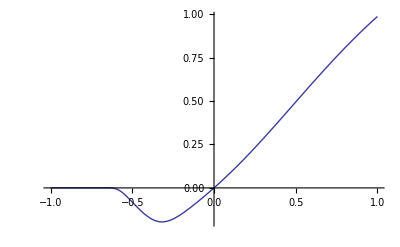

```mathematica
Module[{S1=0.05,S2=0.048,τ=15,
VolS1=0.01,VolS2=0.015,Correl12=0.95,ρS1=0.1,ρS2=0.1,ρS3=0.1,κS1=0.1,κS2=3.,κS3=0.1,λ=0.15,LTVarianceFactor=1.5,gyndinkin=1,printflag=1,prices},
Plot[PackagedSmileBiSuperHestonLogNormalCorrelation[S1,S2,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor],{Correl12,-1,1}]]
```

On observe sur le graphe suivant le cout de la difference de volatilité sur le spread

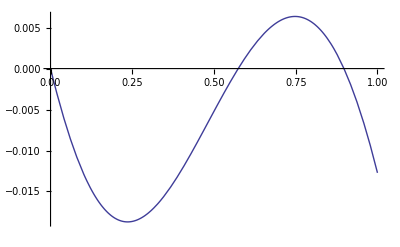

```mathematica
Module[{S1=0.05,S2=0.048,SpreadStrikes={-0.01,-0.005,-0.001,0,0.001,0.005,0.01},τ=15,
VolS1=0.01,VolS2=0.015,Correl12=0.95,ρS1=0.1,ρS2=0.1,ρS3=0.1,κS1=0.1,κS2=3.,κS3=0.1,λ=0.15,LTVarianceFactor=1.5,gyndinkin=1,printflag=1,prices},
Plot[PackagedSmileBiSuperHestonLogNormalCorrelation[S1,S2,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor]-Correl12,{Correl12,0.,1}]]
```

On observe sur le graphe suivant le cout de la difference de volatilité sur le spread

```mathematica
Module[{S1=0.05,S2=0.048,SpreadStrikes={-0.01,-0.005,-0.001,0,0.001,0.005,0.01},τ=15,
VolS1=0.01,VolS2=0.01,Correl12=0.98,ρS1=0.1,ρS2=0.1,ρS3=0.1,κS1=0.1,κS2=3.,κS3=0.1,λ=0.15,LTVarianceFactor=1.5,gyndinkin=1,printflag=1,prices},
PackagedSmileBiSuperHestonLogNormalCorrelation[S1,S2,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor]]
```

0.982186

```mathematica
Module[{S1=0.052258247890041340,S2=0.051030005797917707,τ=20.010958904109589,
VolS1=0.024514901952847092,VolS2=0.028683931136892087,ρS1=0.34328764291972580,ρS2=-0.50094389170783393,ρS3=-0.34328764291972580,κS1=0.088298860081262961,κS2=2.4141493933698608,κS3=0.088298860081262961,λ=0.1,LTVarianceFactor=1.,V0=1.0285426268100003*10^(-005)},
PackagedSmileBiSuperHestonLogNormalImplicitCorrelationFromV0[S1,S2,τ,
VolS1,VolS2,V0,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor]]
```

0.979301

le LogHestonNormalVarianceProxy ne depends pas en fait de la correlation comme le demontre l' experience ci - apres :

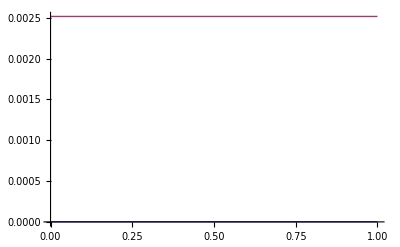

```mathematica
Module[{S1=0.05,S2=0.048,SpreadStrikes={-0.01,-0.005,-0.001,0,0.001,0.005,0.01},τ=15,
VolS1=0.01,VolS2=0.01,Correl12=0.95,ρS1=0.1,ρS2=0.1,ρS3=0.1,κS1=0.1,κS2=3.,κS3=0.1,λ=0.15,LTVarianceFactor=1.5,gyndinkin=1,printflag=1,prices},Plot[{PackagedSmileBiSuperHestonLogNormalCorrelationFromV0[S1,S2,τ,
VolS1,VolS2,Correl12,V0,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor][[1]],
PackagedSmileBiSuperHestonLogNormalCorrelationFromV0[S1,S2,τ,
VolS1,VolS2,Correl12,V0,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor][[2]]},{Correl12,0,1}]]
```

```mathematica
Module[{S1=0.05,S2=0.048,SpreadStrikes={-0.01,-0.005,-0.001,0,0.001,0.005,0.01},τ=15,
VolS1=0.01,VolS2=0.01,Correl12=0.95,ρS1=0.1,ρS2=0.1,ρS3=0.1,κS1=0.1,κS2=3.,κS3=0.1,λ=0.15,LTVarianceFactor=1.5,gyndinkin=1,printflag=1,prices},PackagedSmileBiSuperHestonLogNormalCorrelationFromV0[S1,S2,τ,
VolS1,VolS2,Correl12,V0,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor]]
```

{1.04793×10^-6,0.00251608,-795.218 (-0.00125857+19.518 V0)}

```mathematica
Module[{S1=0.05,S2=0.048,SpreadStrikes={-0.01,-0.005,-0.001,0,0.001,0.005,0.01},τ=15,
VolS1=0.01,VolS2=0.01,Correl12=0.95,ρS1=0.1,ρS2=0.1,ρS3=0.1,κS1=0.1,κS2=3.,κS3=0.1,λ=0.15,LTVarianceFactor=1.5,gyndinkin=1,printflag=1,prices},
Plot3D[PackagedSmileBiSuperHestonLogNormalCorrelationFromV0[S1,S2,τ,
VolS1,VolS2,Correl12,V0,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor],{Correl12,0.,1},{V0,0,0.01}]]
```

```mathematica
Module[{S1=0.05,S2=0.048,SpreadStrikes={-0.01,-0.005,-0.001,0,0.001,0.005,0.01},τ=15,
VolS1=0.01,VolS2=0.01,ρS1=0.1,ρS2=0.1,ρS3=0.1,κS1=0.1,κS2=3.,κS3=0.1,λ=0.15,LTVarianceFactor=1.5,gyndinkin=1,printflag=1,prices,V0=0.000015,ρimp},
ρimp=PackagedSmileBiSuperHestonLogNormalImplicitCorrelationFromV0[S1,S2,τ,
VolS1,VolS2,V0,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor];Print["ρimp=",ρimp];
PackagedSmileBiSuperHestonLogNormalCorrelationFromV0[S1,S2,τ,
VolS1,VolS2,ρimp,V0,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor]]
```

ρimp=0.755962

{1.04793×10^-6,0.00251608,0.768018}

```mathematica
Module[{S1=0.05,S2=0.048,τ=15,
VolS1=0.01,VolS2=0.015,Correl12=0.95,ρS1=0.1,ρS2=0.1,ρS3=0.1,κS1=0.1,κS2=3.,κS3=0.1,λ=0.15,LTVarianceFactor=1.5,V0=0.0000125},
PackagedSmileBiSuperHestonLogNormalImplicitCorrelationFromV0[S1,S2,τ,
VolS1,VolS2,V0,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor]]
```

0.879416

## Applications

```mathematica
Module[{ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,Z1,Z2,τ,S1,S2,α2,β2,LTFactorS=1.,λS=0.1,gyndinkin=10,prices,TrueIniVarSpread,ρprojeté,νfinal,kappaFact1=1,kappaFact2=1,rhobase1=0,rhobase2=0},
S1=0.049676953666394692;S2=0.044555848605364094;
ρ1=0.3432876429197347;λv1=0.1;θv1=0.0027262918134586395;κ1=0.08829886008126084;V1=0.0027262918134586395;
ρ2=-0.47773824397608355;λv2=0.1;θv2=1;κ2=0.80937524636338931;V2=1;
ρ3=-0.3432876429197347;λv3=0.1;θv3=0.0041436538604584065;κ3=0.08829886008126084;V3=0.0041436538604584065;
τ=3.7342465753424658;α2=0.12793651449196744;β2=0.16415267074161935;
{TrueIniVarSpread1,ρprojeté1,νfinal1}=SmileBiSuperHestonVanillaSmileParameters[S1,S2, ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,LTFactorS,λS,τ];
Print["TrueIniVarSpread1=",TrueIniVarSpread1," ρprojeté1=",ρprojeté1, " νfinal1=",νfinal1];
{κspecif,ρspecif}=CalibrateKappaSpecifBiSuperHestonSmileParams[S1,S2,λv1,θv1,V1,ρ2,λv2,θv2,κ2,V2,λv3,θv3,V3,α2,β2,LTFactorS,λS,τ,TrueIniVarSpread1,νfinal1,ρprojeté1,kappaFact1,kappaFact2,rhobase1,rhobase2];
κ1a=kappaFact1*κspecif;κ3a=kappaFact2*κspecif;ρ1a=rhobase1-ρspecif;ρ3a=rhobase2+ρspecif;
Print["κ1a=",κ1a," ρ1a=",ρ1a," κ3a=",κ3a," ρ3a=",ρ3a]]
```

VS=0.0000158727 VarVS=2.6951×10^-10 CoVarSVS=1.11773×10^-8

TrueIniVarSpread1=0.0000184604 ρprojeté1=0.170893 νfinal1=0.00382091

VS=0.0000158727 VarVS=2.6951×10^-10 CoVarSVS=1.11773×10^-8

verif1 (VarVs) ={2.6951×10^-10,2.6951×10^-10}

verif 2= (CoVarVs){1.11773×10^-8,1.11773×10^-8}

κ1a=0.0882989 ρ1a=0.343288 κ3a=0.0882989 ρ3a=-0.343288

```mathematica
Module[{λv1,θv1,V1,ρ2,λv2,θv2,κ2,V2,λv3,θv3,V3,Z1,Z2,τ,S1,S2,α2,β2,LTFactorS=1.,λS=0.1,gyndinkin=10,prices,TrueIniVarSpread,ρprojeté,νfinal,kappaFact1=1,kappaFact2=1,rhobase1=0,rhobase2=0},
TrueIniVarSpread=1.0285426268100003*10^(-005);ρprojeté=0.044103999999999997;νfinal=0.0060408747239999996;
S1=0.052258247890041340;S2=0.051030005797917707;
λv1=0.1;θv1=0.0024717066545948373;V1=0.0024717066545948373;
ρ2=-0.6;λv2=0.1;θv2=1;κ2=1.5;V2=1;
λv3=0.1;θv3=0.0040979213554041168;V3=0.0040740000000000047;
τ=20.010958904109589;α2=0.13239446115833231;β2=0.17585789717837524;
Print["TrueIniVarSpread=",TrueIniVarSpread," ρprojeté=",ρprojeté, " νfinal=",νfinal];
{κspecif,ρspecif}=CalibrateKappaSpecifBiSuperHestonSmileParams[S1,S2,λv1,θv1,V1,ρ2,λv2,θv2,κ2,V2,λv3,θv3,V3,α2,β2,LTFactorS,λS,τ,TrueIniVarSpread,νfinal,ρprojeté,kappaFact1,kappaFact2,rhobase1,rhobase2];
κ1a=kappaFact1*κspecif;κ3a=kappaFact2*κspecif;ρ1a=rhobase1-ρspecif;ρ3a=rhobase2+ρspecif;
Print["κ1a=",κ1a," ρ1a=",ρ1a," κ3a=",κ3a," ρ3a=",ρ3a];
{TrueIniVarSpread1,ρprojeté1,νfinal1}=SmileBiSuperHestonVanillaSmileParameters[S1,S2, ρ1a,λv1,θv1,κ1a,V1,ρ2,λv2,θv2,κ2,V2,ρ3a,λv3,θv3,κ3a,V3,α2,β2,LTFactorS,λS,τ];
Print["TrueIniVarSpread1=",TrueIniVarSpread1," ρprojeté1=",ρprojeté1, " νfinal1=",νfinal1];
]
```

TrueIniVarSpread=0.0000102854 ρprojeté=0.044104 νfinal=0.00604087

VS=0.0000215834 VarVS=3.75337×10^-10 CoVarSVS=3.96962×10^-9

verif1={3.75337×10^-10,3.75337×10^-10}

verif 2={3.96962×10^-9,3.96962×10^-9}

κ1a=0.0882989 ρ1a=0.343288 κ3a=0.0882989 ρ3a=-0.343288

TrueIniVarSpread1=0.0000900783 ρprojeté1=0.044104 νfinal1=0.00204127

```mathematica
{κspecif,ρspecif}
```

{0.134396,-0.337459}

```mathematica
Module[{λv1,θv1,V1,ρ2,λv2,θv2,κ2,V2,λv3,θv3,V3,Z1,Z2,τ,S1,S2,α2,β2,LTFactorS=1.,λS=0.1,gyndinkin=10,prices,TrueIniVarSpread,ρprojeté,νfinal,kappaFact1=1,kappaFact2=1,rhobase1=0,rhobase2=0},
TrueIniVarSpread=1.0285426268100003*10^(-005);ρprojeté=0.044103999999999997;νfinal=0.0060408747239999996;
S1=0.052258247890041340;S2=0.051030005797917707;
λv1=0.1;θv1=0.0024717066545948373;V1=0.0024717066545948373;
ρ2=-0.6;λv2=0.1;θv2=1;κ2=1.5;V2=1;
λv3=0.1;θv3=0.0040979213554041168;V3=0.0040740000000000047;
τ=20.010958904109589;α2=0.13239446115833231;β2=0.17585789717837524;
Print["TrueIniVarSpread=",TrueIniVarSpread," ρprojeté=",ρprojeté, " νfinal=",νfinal];
{κspecif,ρspecif}=CalibrateKappaSpecifBiSuperHestonSmileParams[S1,S2,λv1,θv1,V1,ρ2,λv2,θv2,κ2,V2,λv3,θv3,V3,α2,β2,LTFactorS,λS,τ,TrueIniVarSpread,νfinal,ρprojeté,kappaFact1,kappaFact2,rhobase1,rhobase2];
κ1a=kappaFact1*κspecif;κ3a=kappaFact2*κspecif;ρ1a=rhobase1-ρspecif;ρ3a=rhobase2+ρspecif;
Print["κ1a=",κ1a," ρ1a=",ρ1a," κ3a=",κ3a," ρ3a=",ρ3a];

{TrueIniVarSpread1,ρprojeté1,νfinal1}=SmileBiSuperHestonVanillaSmileParameters[S1,S2, ρ1a,λv1,θv1,κ1a,V1,ρ2,λv2,θv2,κ2,V2,ρ3a,λv3,θv3,κ3a,V3,α2,β2,LTFactorS,λS,τ];
Print["TrueIniVarSpread1=",TrueIniVarSpread1," ρprojeté1=",ρprojeté1, " νfinal1=",νfinal1];
Print["κspecif=",κspecif," ρspecif=",ρspecif];
]
```

TrueIniVarSpread=0.0000102854 ρprojeté=0.044104 νfinal=0.00604087

VS=0.0000215834 VarVS=3.75337×10^-10 CoVarSVS=3.96962×10^-9

verif1 (VarVs) ={3.75337×10^-10,3.75337×10^-10}

verif 2= (CoVarVs){3.96962×10^-9,3.96962×10^-9}

κ1a=0.0882989 ρ1a=0.343288 κ3a=0.0882989 ρ3a=-0.343288

TrueIniVarSpread1=0.0000900783 ρprojeté1=0.044104 νfinal1=0.00204127

κspecif=0.0882989 ρspecif=-0.343288

```mathematica
Ca marche pas (presque)
```

```mathematica
Module[{λv1,θv1,V1,ρ2,λv2,θv2,κ2,V2,λv3,θv3,V3,Z1,Z2,τ,S1,S2,α2,β2,LTFactorS=1.,λS=0.1,gyndinkin=10,prices,TrueIniVarSpread,ρprojeté,νfinal,kappaFact1=1,kappaFact2=1,rhobase1=0,rhobase2=0},
TrueIniVarSpread=1.8630532016100001*10^(-005);ρprojeté=0.20376800000000000;νfinal=0.0055809888300000004;
S1=0.049676953666394692;S2=0.044555848605364094;
λv1=0.1;θv1=0.0025862964242047599;V1=0.0025862964242047599;
ρ2=-0.44653709642906592;λv2=0.1;θv2=1;κ2=0.85149724900604684;V2=1;
λv3=0.1;θv3=0.0040916291935248900;V3=0.0040916291935248900;
τ=3.7342465753424658;α2=0.12780882888375253;β2=0.16699116902689259;
Print["rho implicite:",V2/√((V1+V2)(V3+V2)),"  ",α2 β2/√((V1+V2)(V3+V2))];
Print["TrueIniVarSpread=",TrueIniVarSpread," ρprojeté=",ρprojeté, " νfinal=",νfinal];
{κspecif,ρspecif}=CalibrateKappaSpecifBiSuperHestonSmileParams[S1,S2,λv1,θv1,V1,ρ2,λv2,θv2,κ2,V2,λv3,θv3,V3,α2,β2,LTFactorS,λS,τ,TrueIniVarSpread,νfinal,ρprojeté,kappaFact1,kappaFact2,rhobase1,rhobase2];
Print["κspecif=",κspecif," ρspecif=",ρspecif];
κ1a=kappaFact1*κspecif;κ3a=kappaFact2*κspecif;ρ1a=rhobase1-ρspecif;ρ3a=rhobase2+ρspecif;
Print["κ1a=",κ1a," ρ1a=",ρ1a," κ3a=",κ3a," ρ3a=",ρ3a];
{TrueIniVarSpread1,ρprojeté1,νfinal1}=SmileBiSuperHestonVanillaSmileParametersWithV0[S1,S2, ρ1a,λv1,θv1,κ1a,V1,ρ2,λv2,θv2,κ2,V2,ρ3a,λv3,θv3,κ3a,V3,α2,β2,LTFactorS,λS,τ,TrueIniVarSpread];
Print["TrueIniVarSpread1=",TrueIniVarSpread1," ρprojeté1=",ρprojeté1, " νfinal1=",νfinal1];
{TrueIniVarSpread2,ρprojeté2,νfinal2}=SmileBiSuperHestonVanillaSmileParameters[S1,S2, ρ1a,λv1,θv1,κ1a,V1,ρ2,λv2,θv2,κ2,V2,ρ3a,λv3,θv3,κ3a,V3,α2,β2,LTFactorS,λS,τ];
Print["TrueIniVarSpread2=",TrueIniVarSpread2," ρprojeté2=",ρprojeté2, " νfinal2=",νfinal2];

]
```

rho implicite:0.996672  0.0212719

TrueIniVarSpread=0.0000186305 ρprojeté=0.203768 νfinal=0.00558099

TrueIniVarSpread=0.0000186305 VS=0.0000156962 VarVS=5.80293×10^-10 CoVarSVS=1.94472×10^-8

verif1 (VarVs) ={5.80293×10^-10,5.80293×10^-10}

verif 2= (CoVarVs){1.94472×10^-8,1.94472×10^-8}

κspecif=0.134466 ρspecif=-0.337165

κ1a=0.134466 ρ1a=0.337165 κ3a=0.134466 ρ3a=-0.337165

TrueIniVarSpread=0.0000186305 VS=0.0000156962 VarVS=5.80293×10^-10 CoVarSVS=1.94472×10^-8

TrueIniVarSpread1=0.0000186305 ρprojeté1=0.203768 νfinal1=0.00558099

TrueIniVarSpread=0.000018625 VS=0.0000156962 VarVS=5.80293×10^-10 CoVarSVS=1.94472×10^-8

TrueIniVarSpread2=0.000018625 ρprojeté2=0.203768 νfinal2=0.00558182

## Sous-determination de la solution:

Attention il n' y a pas bijection entre α2, β2 , V1, V3 et  Correl12, VolS1, VolS2
par :

β2=((1+Correl12)√VolS2)/2;α2=(2Correl12)/(1+Correl12)√VolS1;V1=VolS1-α2^2;V3=VolS2-β2^2

la relation manquante doit etre une relation entre α2 , β2, V1 et V3 toujours verifiée : :

VolS2=((2 β2)/(1+Correl12))^2=V3+β2^2

VolS1=((α2(1+Correl12))/(2Correl12))^2=V1+α2^2

nous donne deux expression de la correl qui doivent etre egale :

```mathematica
Solve[((2 β2)/(1+Correl12))^2==V3+β2^2,Correl12]
```

{{Correl12→(-V3-β2^2-2 √(V3 β2^2+β2^4))/(V3+β2^2)},{Correl12→(-V3-β2^2+2 √(V3 β2^2+β2^4))/(V3+β2^2)}}

```mathematica
Solve[((α2(1+Correl12))/(2Correl12))^2==V1+α2^2,Correl12]
```

{{Correl12→(α2^2-2 √(V1 α2^2+α2^4))/(4 V1+3 α2^2)},{Correl12→(α2^2+2 √(V1 α2^2+α2^4))/(4 V1+3 α2^2)}}

La correspondance entre les formules se fait suivant les valeurs de la correlation

Si la correl est proche de 1, alors :

(-V3-β2^2+2 √(V3 β2^2+β2^4))/(V3+β2^2)=(α2^2+2 √(V1 α2^2+α2^4))/(4 V1+3 α2^2)

(2 √(V3 β2^2+β2^4))/(V3+β2^2)=(α2^2+2 √(V1 α2^2+α2^4))/(4 V1+3 α2^2)+1

(2 β2 √(V3 +β2^2))/(V3+β2^2)=(4 (V1+α2^2)+2 α2 √(V1 +α2^2))/(4 V1+3 α2^2)

La relation est donc :

β2 √(V3 +β2^2)(4 V1+3 α2^2)-(V3+β2^2) (2(V1+α2^2)+α2 √(V1 +α2^2))=0

## Principe de la calibration :

Pour tous les process envisagé, le longtermfactor qui est le rapport entre la variance long terme des processus et la variance initiale , est fixé a un facteur commun : f que l' on suppose egal a 1 en general .

Pour tous les process envisage on fixe la mean reversion egale a λ. (en general 10 ou 15 % , mais si la vol de vol le ncessite, elle peux atteindre 200 %)

On suppose donné aussi νFact1 et νFact2 qui fixe les rapport de proportionalité pour les vol de vol des facteur specifiques
ces facteur serait suceptible d' etre optimise pour une meilleur calibration des underlyings.Pour le moment nous les fixons a 1

On suppose donné aussi ρbase1 et ρbase2  qui fixe les bases de  pour les correl underlying - vol des facteur specifiques
ces bases serait suceptible d' etre optimise pour une meilleur calibration des underlyings.Pour le moment nous les fixons a 0

### Optimisation et calcul du smile Normalheston le plus pres des prix de spreadoptions

resultats:   TrueIniVarSpread   , ρprojeté , νfinal

Autre representationdes resultats:    TrueIniVarSpread  , VarVS ,  CoVarSVS

Les relations entre ces deux representations sont :

```mathematica
ρprojeté=CoVarSVS/(√(VS VarVS));νprojeté=√(VarVS/TrueIniVarSpread);  ou  VS=S1^2 V1+S2^2 V3+V2 (S1 α2-S2 β2)^2
```

### Initialisation de l'iteration :

Vs1 :  Total volatility  de l' index 1

Vs2 :  Total volatility  de l' index 2

RhoCommun : rho du facteur commun

NuCommun : nu du facteur commun

Correl :  Correlation entre les deux indexes

Rho1 : rho dufacteur specifique de l' index 1

Nu1 : nu dufacteur specifique de l' index 1

Rho2 : rho dufacteur specifique de l' index 2

Nu2 : nu dufacteur specifique de l' index 2

### Interation 1

#### Calibration analytique des spreadoption

Determination de νspecif et de ρspecif

c' est a dire en supposant que

ν1 = νFact1*νspecif; ν2 = νFact2*νspecif; ρ1 = ρbase1 - ρspecif; ρ2 = ρbase2 + ρspecif

determination de ν1, ν2, ρ1, ρ2

ceci se fait par projection du generateur reel du spread sur le generateur du spread en supposant que celui-ci suit un normalheston, νspecif et ρspecif sont determiné de tel maniere que la variance de la variance du spread ainsi que la covariance entre le spread et sa variance soit les meme pour les deux type de process.

#### Optimisation des Smiles des underlyings

determination de  Vs1 , Vs2, RhoCommun et NuCommun

en calculant les valeurs des options vanilles sur les deux supports et en minimisant le carré des distance avec les prix de marché pour les deux underlyings. les deux smiles ont bien sur des niveaux qui leur sont propres (Vs1 et Vs2)  mais ont une composante commune qui transporte une vol de vol et un sskew commun. Les smile peuvent etre neammoins differents du a l' action non gaussienne des composante specifiques.?

#### Determination de la correl implicite

determination de Correl tel que la vraie variance du spread a maturité est egal a la vraie variance du spread en supposant qu' il suit le procecess  caraterisé par les parametres NormalHeston . ceci se fait par resolution d' une equation numerique.

### Interation suivantes

Usuellement deux iterations sont suffisante pour converger. On s' arretera dans une etape juste apres  calibration analytique des spreadoptions affin de benficier du meilleur fit avec les spreadoptions.

```mathematica
BiSuperHestonPackaging[VolS1_,VolS2_,Correl12_]:=Module[{α2,β2,V1,V2,V3},
β2=((1+Correl12)√VolS2)/2;α2=(2Correl12)/(1+Correl12)√VolS1;V1=VolS1-α2^2;V3=VolS2-β2^2;
{α2,β2,V1,V3}]
```

```mathematica
BiSuperHestonPackagingInverse[α2_,β2_,V1_,V3_]:=Module[{VolS1,VolS2,Correl12},
VolS1=V1+α2^2;VolS2=V3+β2^2;
Correl12=(2β2)/(√(V3+β2^2))-1;(* ou bien Correl12=α2/(2 √(V1+α2^2)-α2); *)
{VolS1,VolS2,Correl12}]
```

ce qui nous permet de retrouver la relation de sous determination:

(2β2)/(√(V3+β2^2))-1=α2/(2 √(V1+α2^2)-α2)

```mathematica
VerifcationBiSuperHestonPackagingInverse[α2_,β2_,V1_,V3_]:=
Print["(2  β2)/(√(V3 + SuperscriptBox[β2, 2]))-1=",(2β2)/(√(V3+β2^2))-1,"  α2/(2 SqrtBox[V1 + SuperscriptBox[α2, 2]] - α2)=",α2/(2 √(V1+α2^2)-α2)];
```

```mathematica
Ca marche
```

```mathematica
Module[{λv1,θv1,V1,ρ2,λv2,θv2,κ2,V2,λv3,θv3,V3,Z1,Z2,τ,S1,S2,α2,β2,LTFactorS=1.,λS=0.1,gyndinkin=10,prices,TrueIniVarSpread,ρprojeté,νfinal,kappaFact1=1,kappaFact2=1,rhobase1=0,rhobase2=0,VolS1,VolS2,Correl12,κ1a,ρ1a,κ3a,ρ3a,corrimplicit},
TrueIniVarSpread=1.0285426268100003*10^(-005);ρprojeté=0.044103999999999997;νfinal=0.0060408747239999996;
S1=0.052258247890041340;S2=0.051030005797917707;
λv1=0.1;θv1=0.00051006284059752077;V1=0.00051006284059752077;
ρ2=-0.50094389170783393;λv2=0.1;θv2=1;κ2=2.4141493933698608;V2=1;
λv3=0.1;θv3=0.00059066010770074395;V3=0.00059066010770074395;
τ=20.010958904109589;α2=0.15493495122873202;β2=0.16761047410347404;
ρ1a=0.34328764291972580;ρ3a=-0.34328764291972580;κ1a=0.088298860081262961;κ3a=0.088298860081262961;
Print["rho implicite:",V2/√((V1+V2)(V3+V2))];
VerifcationBiSuperHestonPackagingInverse[α2,β2,V1,V3];
Print["TrueIniVarSpread=",TrueIniVarSpread," ρprojeté=",ρprojeté, " νfinal=",νfinal];
(*on veut encoder TrueIniVarSpread dans V1,V3,α2,β2 via la determination de la correl implicite *)
{VolS1,VolS2,Correl12}=BiSuperHestonPackagingInverse[α2,β2,V1,V3];

corrimplicit=PackagedSmileBiSuperHestonLogNormalImplicitCorrelationFromV0[S1,S2,τ,
VolS1,VolS2,TrueIniVarSpread,ρ1a,ρ2,ρ3a,κ1a,κ2,κ3a,λS,LTFactorS];

Print["VolS1=",VolS1," VolS2=",VolS2," Correl12=",Correl12];
Print["corrimplicit=",corrimplicit];
{κspecif,ρspecif}=CalibrateKappaSpecifBiSuperHestonSmileParams[S1,S2,λv1,θv1,V1,ρ2,λv2,θv2,κ2,V2,λv3,θv3,V3,α2,β2,LTFactorS,λS,τ,TrueIniVarSpread,νfinal,ρprojeté,kappaFact1,kappaFact2,rhobase1,rhobase2];
Print["κspecif=",κspecif," ρspecif=",ρspecif];
κ1a=kappaFact1*κspecif;κ3a=kappaFact2*κspecif;ρ1a=rhobase1-ρspecif;ρ3a=rhobase2+ρspecif;
Print["κ1a=",κ1a," ρ1a=",ρ1a," κ3a=",κ3a," ρ3a=",ρ3a];
{TrueIniVarSpread2,ρprojeté2,νfinal2}=SmileBiSuperHestonVanillaSmileParameters[S1,S2, ρ1a,λv1,θv1,κ1a,V1,ρ2,λv2,θv2,κ2,V2,ρ3a,λv3,θv3,κ3a,V3,α2,β2,LTFactorS,λS,τ];
Print["TrueIniVarSpread2=",TrueIniVarSpread2," ρprojeté2=",ρprojeté2, " νfinal2=",νfinal2];
]
```

rho implicite:0.99945

(2  β2)/(√(V3 + SuperscriptBox[β2, 2]))-1=0.979301  α2/(2 SqrtBox[V1 + SuperscriptBox[α2, 2]] - α2)=0.979301

TrueIniVarSpread=0.0000102854 ρprojeté=0.044104 νfinal=0.00604087

***1 {ρS1,λ,LTVarianceFactor V1,κS1,V1,ρS2,λ,LTVarianceFactor V2,κS2,V2,ρS3,λ,LTVarianceFactor V3,κS3,V3,α2,β2,τ}={0.343288,0.1,0.000510063,0.0882989,0.000510063,-0.500944,0.1,1.,2.41415,1,-0.343288,0.1,0.00059066,0.0882989,0.00059066,0.154935,0.16761,20.011}

VolS1=0.0245149 VolS2=0.0286839 Correl12=0.979301

corrimplicit=0.979301

TrueIniVarSpread=0.0000102854 VS=3.13948×10^-6 VarVS=3.75337×10^-10 CoVarSVS=1.51397×10^-9

verif1 (VarVs) ={3.75337×10^-10,3.75337×10^-10}

verif 2= (CoVarVs){1.51397×10^-9,1.51397×10^-9}

κspecif=0.219148 ρspecif=-0.071092

κ1a=0.219148 ρ1a=0.071092 κ3a=0.219148 ρ3a=-0.071092

***2 {ρ1,λv1,θv1,κ1,V1,ρ2,λv2,θv2,κ2,V2,ρ3,λv3,θv3,κ3,V3,α2,β2,τ}={0.071092,0.1,0.000510063,0.219148,0.000510063,-0.500944,0.1,1,2.41415,1,-0.071092,0.1,0.00059066,0.219148,0.00059066,0.154935,0.16761,20.011}

μXX=1.64546 μYY=2.10413 NormalTerminalcorrelT=0.991136 ExpcorreLT=0.969932 VarExpX=0.00282442 VarExpY=0.00358448 VarRealSpead=0.000236572 TrueIniVarSpread=0.0000118221

TrueIniVarSpread2=0.0000118221 ρprojeté2=0.044104 νfinal2=0.00563461

## Exemples

#### exemple1

Initial:(S1 | 0.0539991
VolSquareS1 | 0.0251
S2 | 0.0526832
VolSquareS2 | 0.024) Process V1=(V1 | 0.00257258
κ1 | 0.05
ρ1 | 0.
 κ1 norm. | 0.985793) Process V2=(α2 | 0.150091
β2 | 0.147173
κ2 | 0.05
ρ2 | 0.
 κ21 norm. | 0.33313
 κ22 norm. | 0.339735) Process V3=(V3 | 0.00234
κ3 | 0.05
ρ3 | 0.
 κ3 norm. | 1.03362) T=11.7372

variance attendue du spread:0.000165722 ecart type equivalent: 0.0128733

S1 0.0539991 S2 0.0526832 VolS1=0.0251 VolS2=0.024 Correl12= 0.9

entering   SmileBiSuperHestonVanillaSpreadOption **************

moments={{0.147301,0.140846},{0.295073,0.282121,0.259342}}

VarExpX=0.00134121 VarExpY=0.0011969

VS=0.0000141194 VarVS=9.97486×10^-11 CoVarSVS=0.

Sig1=0.15843 Sig2=0.154919 Correl12=0.9

****AlphaGenericComputeSpreadOption****

VarRealSpead (Goal)=0.000294978

NormalTerminalcorrelT=0.898857 ExpcorreLT=0.885212

TrueIniVarSpread=0.000025132

opt1=0.00801113 opt2=0.00321053 opt3=0.00512454

vol1=0.00375194 vol2=0.00374941 vol3=0.00390882

convexity=0.000161938 pente=0.000156879 ATMprix=0.00512454

PriceTable(for convexity)=(0.0005 | {0.00964967,0.00683668,0.00460384}
0.001 | {0.00963317,0.00679191,0.00454149}
0.0015 | {0.00959255,0.00671956,0.00445565}
0.0025 | {0.00945277,0.00650946,0.00423365}
0.0035 | {0.00926007,0.00625153,0.00398618})

VolTable(for convexity)=(0.0005 | {0.00502047,0.00500212,0.00498548}
0.001 | {0.00500788,0.00496936,0.00493784}
0.0015 | {0.00497685,0.00491642,0.00487219}
0.0025 | {0.00486999,0.0047627,0.00470204}
0.0035 | {0.00472232,0.00457398,0.00451165})

convexityTable=(1.71246×10^-6 | 0.0005
7.00235×10^-6 | 0.001
0.0000162056 | 0.0015
0.0000466254 | 0.0025
0.0000860066 | 0.0035)

κsol=0.0115043

prices={0.172,{{-0.6,{0.00910863,0.00396617}},{-0.3,{0.00881143,0.00375713}},{-0.1,{0.00871958,0.00376985}},{0,{0.00868927,0.0037977}},{0.5,{0.00877065,0.00413397}},{0.8,{0.00944691,0.00483891}}}}

vols={{-0.6,{0.00460595,0.00449622}},{-0.3,{0.00437671,0.00433469}},{-0.1,{0.0043056,0.00434453}},{0,{0.0042821,0.00436609}},{0.5,{0.00434515,0.00462544}},{0.8,{0.00486551,0.00516473}}}

penteTable=(-0.000109731 | -0.6
-0.0000420208 | -0.3
0.0000389371 | -0.1
0.0000839819 | 0
0.000280293 | 0.5
0.000299227 | 0.8)

ρsol=-0.0728404

Mode 0 :  Numinimum=0.0115043 rhominimum= -0.0728404

Normal Heston Parameters=(S0 | 0.00131588
V0 | 0.000025132
θ | 0.000025132
λv | 0.1
ρ | -0.0717722
ν | 0.0116755
ν normalized | 2.32896
standard dev equi. | 0.00501318)

prices={0.0131551,0.00884007,0.00582218,0.00518171,0.00460532,0.00298566,0.00198583}

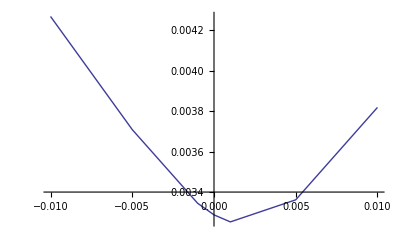

```mathematica
Module[{S1=0.05399906,S2=0.05268318,SpreadStrikes={-0.01,-0.005,-0.001,0,0.001,0.005,0.01},τ=11.737166,
VolS1=0.0251,VolS2=0.024,Correl12=0.9,ρS1=-0.,ρS2=-0.,ρS3=-0.,
κS1=0.05,κS2=0.05,κS3=0.05,
λ=0.1,LTVarianceFactor=1.,gyndinkin=10,printflag=1,prices,mode=0},
prices=PackagedSmileBiSuperHestonVanillaSpreadoptionRapide[S1,S2,SpreadStrikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor,gyndinkin,mode,printflag];
ListPlot[Table[{SpreadStrikes[[i]],NormalImplicitVol[S1-S2,SpreadStrikes[[i]],τ,prices[[i]]]},{i,1,Length[SpreadStrikes]}],Joined->True]]
```

#### exemple2

Initial:(S1 | 0.0539991
VolSquareS1 | 0.0251
S2 | 0.0526832
VolSquareS2 | 0.024) Process V1=(V1 | 0.00257258
κ1 | 0.
ρ1 | 0.
 κ1 norm. | 0.) Process V2=(α2 | 0.150091
β2 | 0.147173
κ2 | 0.
ρ2 | 0.
 κ21 norm. | 0.
 κ22 norm. | 0.) Process V3=(V3 | 0.00234
κ3 | 0.
ρ3 | 0.
 κ3 norm. | 0.) T=11.7372

variance attendue du spread:0.000165722 ecart type equivalent: 0.0128733

S1 0.0539991 S2 0.0526832 VolS1=0.0251 VolS2=0.024 Correl12= 0.9

entering   SmileBiSuperHestonVanillaSpreadOption **************

moments={{0.147301,0.140846},{0.294603,0.281692,0.259268}}

VarExpX=0.00134121 VarExpY=0.0011969

VS=0.0000141194 VarVS=0. CoVarSVS=0.

Sig1=0.15843 Sig2=0.154919 Correl12=0.9

****AlphaGenericComputeSpreadOption****

VarRealSpead (Goal)=0.000291683

NormalTerminalcorrelT=0.9 ExpcorreLT=0.886512

TrueIniVarSpread=0.0000248512

@@@@@@  inside NuRhoV0MinimunNormalHestonFromBilog

opt1=0.00801113 opt2=0.00321053 opt3=0.00512454

vol1=0.00375194 vol2=0.00374941 vol3=0.00390882

convexity=0.000161938 pente=0.000156879 ATMprix=0.00512454

convexityTable=(1.74171×10^-6 | 0.0005
7.12334×10^-6 | 0.001
0.000115897 | 0.004
0.000169534 | 0.005
0.000450854 | 0.01)

Equivalent nu normalisé=(0.0005 | 0.100299
0.001 | 0.200598
0.004 | 0.802391
0.005 | 1.00299
0.01 | 2.00598)

κsol=0.00487123

prices(pour la pente)=(-0.6 | {0.00914709,0.00306651}
-0.3 | {0.0090097,0.00349355}
-0.1 | {0.00887648,0.00370649}
0 | {0.00879638,0.00379638}
0.3 | {0.00849355,0.0040097}
0.6 | {0.00806651,0.00414709})

vols=(-0.6 | {0.00463553,0.0037956}
-0.3 | {0.00452978,0.00413001}
-0.1 | {0.00442699,0.00429545}
0 | {0.00436507,0.00436507}
0.3 | {0.00413001,0.00452978}
0.6 | {0.0037956,0.00463553})

penteTable=(-0.000839934 | -0.6
-0.000399764 | -0.3
-0.000131538 | -0.1
6.67261×10^-14 | 0
0.000399764 | 0.3
0.000839934 | 0.6)

ρsol=0.11915

######## arg={ρsol,λv,LT V0Table[,κsol,V0Table,S1-S2,S1-S2,τ,LimitGindinkin}

######## arg={0.11915,0.1,{0.0000124256,0.0000223661,0.0000248512,0.0000273364,0.0000497025},0.00487123,{0.0000124256,0.0000223661,0.0000248512,0.0000273364,0.0000497025},0.00131588,0.00131588,11.7372,10}

VOptionATMTable=(0.00377137 | 0.0000124256
0.0054775 | 0.0000223661
0.00584386 | 0.0000248512
0.00619293 | 0.0000273364
0.00881037 | 0.0000497025)

V0sol=0.0000200903

convexityTable=(2.55904×10^-6 | 0.0005
0.0000104844 | 0.001
0.000159122 | 0.004
0.000227198 | 0.005
0.000556313 | 0.01)

Equivalent nu normalisé=(0.0005 | 0.100299
0.001 | 0.200598
0.004 | 0.802391
0.005 | 1.00299
0.01 | 2.00598)

κsol2=0.00404466

VOptionATMTable=(0.00397493 | 0.0000124256
0.00569961 | 0.0000223661
0.00606741 | 0.0000248512
0.00641722 | 0.0000273364
0.00902717 | 0.0000497025)

V0sol2=0.0000187403

Mode 1 :   Numinimum=0.00404466 rhominimum= 0.11915 V0minimim=0.0000187403

Comparaison:  TrueIniVarSpread/ V0minimim =1.32609

Normal Heston Parameters=(S0 | 0.00131588
V0 | 0.0000187403
θ | 0.0000187403
λv | 0.1
ρ | 0.11915
ν | 0.00404466
ν normalized | 0.934315
standard dev equi. | 0.00432901)

prices={0.0172699,0.0128787,0.00894462,0.00634245,0.00578919,0.00527751,0.00363197,0.00230914,0.00150628}

Vols Alpha=(-0.015 | 0.00424291
-0.01 | 0.00398867
-0.005 | 0.00379466
-0.001 | 0.00373224
0 | 0.00373459
0.001 | 0.00374464
0.005 | 0.00385614
0.01 | 0.00410832
0.015 | 0.00441527)

Vols bilog=(-0.015 | 0.00418908
-0.01 | 0.00395356
-0.005 | 0.0037798
-0.001 | 0.00372848
0 | 0.00373273
0.001 | 0.00374428
0.005 | 0.00385484
0.01 | 0.00408896
0.015 | 0.00437236)

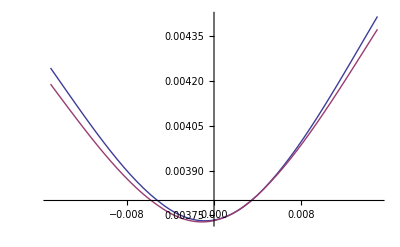

```mathematica
Module[{S1=0.05399906,S2=0.05268318,SpreadStrikes={-0.015,-0.01,-0.005,-0.001,0,0.001,0.005,0.01,0.015},τ=11.737166,
VolS1=0.0251,VolS2=0.024,Correl12=0.9,ρS1=0.,ρS2=0.,ρS3=0.,
κS1=0.00,κS2=0.0,κS3=0.00,
λ=0.1,LTVarianceFactor=1.,gyndinkin=10,printflag=1,mode=-2,prices,pricebilog,interprice,interbilog},
prices=PackagedSmileBiSuperHestonVanillaSpreadoptionRapide[S1,S2,SpreadStrikes,τ,
VolS1,VolS2,Correl12,ρS1,ρS2,ρS3,κS1,κS2,κS3,λ,LTVarianceFactor,gyndinkin,mode,printflag];
prices=Table[{SpreadStrikes[[i]],NormalImplicitVol[S1-S2,SpreadStrikes[[i]],τ,prices[[i]]]},{i,1,Length[SpreadStrikes]}];
Print["Vols Alpha=",prices // MatrixForm];
pricebilog=Table[{SpreadStrikes[[i]],NormalImplicitVol[S1-S2,SpreadStrikes[[i]],τ,LogNormalSpreadOption[S1,S2,√VolS1,√VolS2,Correl12,SpreadStrikes[[i]],τ]]},{i,1,Length[SpreadStrikes]}];
Print["Vols bilog=",pricebilog // MatrixForm];
interprice=Interpolation[prices];
interbilog=Interpolation[pricebilog];

Plot[{interprice[x],interbilog[x]},{x,First[SpreadStrikes],Last[SpreadStrikes]}, PlotLegend->{"Alpha", "BiLog"}, LegendPosition->{0.8,-0.8}]
]
```

## NouveauSpreadoption

```mathematica
AlphaGenericComputeSpreadOption[S1_,S2_,Sig1_,Sig2_,Correl12_,VarExpX_,VarExpY_,VS_,VarVSIncremental_,CoVarSVSIncremental_,μX_,μY_,μXX_,μYY_,μXY_,LTFactorS_,λS_,SpreadStrikes_,τ_,LimitGindinkin_,printflag_]:=Module[{NormalTerminalcorrelT,ExpcorreLT,VarRealSpead,TrueIniVarSpread,ρprojeté,numinimum,rhominimum,V0projeté,V0minimim,
V0Effectif,VarVSTotal,CoVarSVSTotal,νprojeté,prices,nbsteps=10,scale=8,microratio=20},
If[printflag==1 || MemberQ[printflag,1] ,Print["****AlphaGenericComputeSpreadOption****"]];
{V0minimim,rhominimum,numinimum}=HestonFromBilog[S1,S2,Sig1,Sig2,Correl12,τ,λS,LTFactorS];
If[printflag==1 || MemberQ[printflag,1] ,Print["Mode 2 :  Numinimum=",numinimum," rhominimum= ",rhominimum," V0minimim=",V0minimim]];
V0Effectif=V0minimim;
VarVSTotal=VarVSIncremental+numinimum^2 V0minimim;
CoVarSVSTotal=CoVarSVSIncremental+rhominimum V0minimim numinimum;
ρprojeté=CoVarSVSTotal/(√(V0minimim VarVSTotal));νprojeté=√(VarVSTotal/V0minimim);V0projeté=V0minimim;
(* ajustement du kurtosis par effet de vol *)
If[printflag==1 || MemberQ[printflag,1] ,Print["Normal Heston Parameters=",{{"S0",S1-S2},{"V0",V0projeté},{"θ",V0projeté LTFactorS },{"λv",λS},{"ρ",ρprojeté},{"ν",νprojeté},
{"ν normalized",νprojeté/(√V0projeté)},{"standard dev equi.",√V0projeté}} //MatrixForm]];
prices=DerivativeHestonNormalCall[ρprojeté,λS,LTFactorS,νprojeté,V0Effectif,S1-S2,SpreadStrikes,τ,nbsteps,scale,microratio,0][[1]];
If[printflag==1 || MemberQ[printflag,1] ,Print["prices=",prices]];
prices
]
```

## Pricing des digitales qui paye float

## Calculs des digitale : formule affine close

#### Cas lognormal

```mathematica
Subscript[dS, 1]/Subscript[S, 1]=√Subscript[v, 1] Subscript[dW, 1]
Subscript[dS, i]/Subscript[S, i]=√Subscript[v, i](ρ  Subscript[dW, 1]+√(1-ρ^2)Subscript[dW, i])
```

```mathematica
en log
```

```mathematica
d(Log[Subscript[S, 1]])=√Subscript[v, 1] Subscript[dW, 1]-Subscript[v, 1]/2 dt
d(Log[Subscript[S, i]])=√Subscript[v, i](ρ  Subscript[dW, 1]+√(1-ρ^2)Subscript[dW, i])-Subscript[v, i]/2 dt
```

```mathematica
le quotient
```

```mathematica
d(Log[Subscript[S, i]/Subscript[S, 1]])=√Subscript[v, i](ρ  Subscript[dW, 1]+√(1-ρ^2)Subscript[dW, i])-Subscript[v, i]/2 dt-√Subscript[v, 1] Subscript[dW, 1]+Subscript[v, 1]/2 dt
```

```mathematica
d(Log[Subscript[S, i]/Subscript[S, 1]])=(√Subscript[v, i] ρ  -√Subscript[v, 1])Subscript[dW, 1]+√Subscript[v, i] √(1-ρ^2)Subscript[dW, i]+1/2(Subscript[v, 1]-Subscript[v, i])dt
```

```mathematica
on reexponencie
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=(√Subscript[v, i] ρ  -√Subscript[v, 1])Subscript[dW, 1]+√Subscript[v, i] √(1-ρ^2)Subscript[dW, i]+1/2(Subscript[v, 1]-Subscript[v, i])dt+1/2((√Subscript[v, i] ρ  -√Subscript[v, 1])^2+Subscript[v, i](1-ρ^2))dt
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=(√Subscript[v, i] ρ  -√Subscript[v, 1])Subscript[dW, 1]+√Subscript[v, i] √(1-ρ^2)Subscript[dW, i]+(-ρ √Subscript[v, i]  √Subscript[v, 1] +(Subscript[v, 1]+Subscript[v, i])/2+1/2(Subscript[v, 1]-Subscript[v, i]))dt
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=(√Subscript[v, i] ρ  -√Subscript[v, 1])Subscript[dW, 1]+√Subscript[v, i] √(1-ρ^2)Subscript[dW, i]-√Subscript[v, 1](   ρ √Subscript[v, i]-√Subscript[v, 1])dt
```

```mathematica
on distribue les shift:
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=(√Subscript[v, i] ρ  -√Subscript[v, 1])(Subscript[dW, 1]-√Subscript[v, 1])+√Subscript[v, i] √(1-ρ^2)Subscript[dW, i]
```

```mathematica
on a donc les redefinition suivantes:
```

```mathematica
OverBar[Subscript[dW, 1]]=Subscript[dW, 1]-√Subscript[v, 1]
```

```mathematica
OverBar[Subscript[dW, i]]=Subscript[dW, i]
```

```mathematica
donc les nouveau process a analyser sont:
```

```mathematica
Subscript[dS, 1]/Subscript[S, 1]=√Subscript[v, 1](OverBar[Subscript[dW, 1]]+√Subscript[v, 1] dt)
Subscript[dS, i]/Subscript[S, i]=√Subscript[v, i](ρ  (OverBar[Subscript[dW, 1]]+√Subscript[v, 1] dt)+√(1-ρ^2)(OverBar[Subscript[dW, i]]))
```

```mathematica
soit
```

```mathematica
Subscript[dS, 1]/Subscript[S, 1]=√Subscript[v, 1](OverBar[Subscript[dW, 1]])+Subscript[v, 1] dt
Subscript[dS, i]/Subscript[S, i]=√Subscript[v, i](ρ  OverBar[Subscript[dW, 1]]+√(1-ρ^2)OverBar[Subscript[dW, i]])+ρ √Subscript[v, i] √Subscript[v, 1] dt
```

#### Cas du modele alpha

```mathematica
On veut calculer des options comme:
```

E[S_1 1_(S_1-S_2-K>0)]=E[S_1]E^S_1[1_(S_1-S_2-K>0)]

```mathematica
ou bien :
```

E[S_1 1_(S_2-S_3-K>0)]=E[S_1]E^S_1[1_(S_2-S_3-K>0)]

Principe : on change de numeraire :   On se place dans le numeraire S1

```mathematica
Il nous faut donc modifier les drift de Subscript[S, 2],Subscript[S, 3] et Subscript[S, 4] de telle sorte que Subscript[S, 2]/Subscript[S, 1] , Subscript[S, 3]/Subscript[S, 1] et Subscript[S, 4]/Subscript[S, 1] soient des martingales
```

dS_1/S_1=∑_(j=1)^4 α_(1,j) √v_j dW_j+ √v_5 dW_5
dS_i/S_i=∑_(j=1)^4 α_(i,j) √v_j dW_j+ √(v_(4+i))dW_(4+i)
mais si on modifie les drifts c'est que les browniens on changé de definition.

```mathematica
On applique donc le lemme de Ito sur le quotient et on annule le drift.
```

```mathematica
on passe par les logs
```

```mathematica
d(Log[Subscript[S, 1]])=∑_(j=1)^4 Subscript[α, 1,j] √Subscript[v, j] Subscript[dW, j]+ √Subscript[v, 5] Subscript[dW, 5]-1/2(∑_(j=1)^4 Subscript[α, 1,j]^2 Subscript[v, j]+ Subscript[v, 5])dt
```

```mathematica
d(Log[Subscript[S, i]])=∑_(j=1)^4 Subscript[α, i,j] √Subscript[v, j] Subscript[dW, j]+ √Subscript[v, 4+i] Subscript[dW, 4+i]-1/2(∑_(j=1)^4 Subscript[α, i,j]^2 Subscript[v, j]+ Subscript[v, 4+i])dt
```

```mathematica
donc
```

```mathematica
d Log[(Subscript[S, i]/Subscript[S, 1])]=∑_(j=1)^4 (Subscript[α, i,j] -Subscript[α, 1,j])√Subscript[v, j] Subscript[dW, j]+ √Subscript[v, 4+i] Subscript[dW, 4+i]- √Subscript[v, 5] Subscript[dW, 5] +1/2(∑_(j=1)^4 {(Subscript[α, 1,j]^2 -Subscript[α, i,j]^2)Subscript[v, j]}+Subscript[v, 5]-Subscript[v, 4+i])dt
```

```mathematica
si on reexponencie:
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=∑_(j=1)^4 (Subscript[α, i,j] -Subscript[α, 1,j])√Subscript[v, j] Subscript[dW, j]+ √Subscript[v, 4+i] Subscript[dW, 4+i]- √Subscript[v, 5] Subscript[dW, 5]+1/2(∑_(j=1)^4 {(Subscript[α, 1,j]^2 -Subscript[α, i,j]^2)+(Subscript[α, i,j] -Subscript[α, 1,j])^2}Subscript[v, j]+Subscript[v, 5]-Subscript[v, 4+i]+Subscript[v, 5]+Subscript[v, 4+i])dt
```

```mathematica
soit en fait:
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=∑_(j=1)^4 (Subscript[α, i,j] -Subscript[α, 1,j])√Subscript[v, j] Subscript[dW, j]+ √Subscript[v, 4+i] Subscript[dW, 4+i]- √Subscript[v, 5] Subscript[dW, 5]+(∑_(j=1)^4 {-Subscript[α, 1,j] Subscript[α, i,j]+Subscript[α, 1,j]^2}Subscript[v, j]+Subscript[v, 5])dt
```

```mathematica
on change,
```

```mathematica
{{Subscript[dW, 1]=d Subscript[W̄, 1]+Subscript[Λ, 1] dt}, {Subscript[dW, 2]=d Subscript[W̄, 2]+Subscript[Λ, 2] dt}, {Subscript[dW, 3]=d Subscript[W̄, 3]+Subscript[Λ, 3] dt}, {{{{{Subscript[dW, 4]=d Subscript[W̄, 4]+Subscript[Λ, 4] dt}, {Subscript[dW, 5]=d Subscript[W̄, 5]+Subscript[Λ, 5] dt}}}, {Subscript[dW, 4+i]=d Subscript[W̄, 4+i]}}}}
```

```mathematica
(d(Subscript[S, i]/Subscript[S, 1]))/(Subscript[S, i]/Subscript[S, 1])=∑_(j=1)^4 (Subscript[α, i,j] -Subscript[α, 1,j])√Subscript[v, j](d Subscript[W̄, j]+Subscript[Λ, j] dt)+ √Subscript[v, 4+i] Subscript[dW, 4+i]- √Subscript[v, 5](d Subscript[W̄, 5]+Subscript[Λ, 5] dt)+(∑_(j=1)^4 {-Subscript[α, 1,j] Subscript[α, i,j]+Subscript[α, 1,j]^2}Subscript[v, j]+Subscript[v, 5])dt
```

```mathematica
soit
```

```mathematica
(Subscript[α, i,j] -Subscript[α, 1,j])√Subscript[v, j] Subscript[Λ, j]+∑_(j=1)^4 {-Subscript[α, 1,j] Subscript[α, i,j]+Subscript[α, 1,j]^2}Subscript[v, j]=0
```

```mathematica
-√Subscript[v, 5] Subscript[Λ, 5]+Subscript[v, 5]=0
```

```mathematica
on remplace et annule le drift:
```

```mathematica
que l'on definit par
```

```mathematica
Subscript[Λ, j]=-({-Subscript[α, 1,j] Subscript[α, i,j]+Subscript[α, 1,j]^2}√Subscript[v, j])/(Subscript[α, i,j] -Subscript[α, 1,j])=Subscript[α, 1,j] √Subscript[v, j]
```

```mathematica
Subscript[Λ, 5]=√Subscript[v, 5]
```

```mathematica
ceci definit donc la dynamique de Subscript[S, i] par:
```

(d(S_i/S_1))/(S_i/S_1)=∑_(j=1)^4 (α_(i,j) -α_(1,j))√v_j OverBar[dW_j]+ √(v_(4+i))OverBar[dW_(4+i)]- √v_5 OverBar[dW_5]+(∑_(j=1)^4 (α_(1,j)α_(i,j) -(α_(1,j))^2)v_j - v_5 )dt

```mathematica
ceci grace a une nouvelle definition  des brownien 
if faut donc propager ces nouvelles definitions de  dans Subscript[dS, 1] pour obtenir le drift sur Subscript[S, 1] induit par le changement de mesure
```

```mathematica
Subscript[dS, 1]/Subscript[S, 1]=∑_(j=1)^4 Subscript[α, 1,j] √Subscript[v, j](OverBar[Subscript[dW, j]]+Subscript[α, 1,j] √Subscript[v, j] dt)+ √Subscript[v, 5](OverBar[Subscript[dW, 5]]+√Subscript[v, 5] dt)
```

```mathematica
Subscript[dS, 1]/Subscript[S, 1]=∑_(j=1)^4 Subscript[α, 1,j] √Subscript[v, j](OverBar[Subscript[dW, j]])+ √Subscript[v, 5](OverBar[Subscript[dW, 5]])+(∑_(j=1)^4 Subscript[α, 1,j]^2 Subscript[v, j]+Subscript[v, 5])dt
```

```mathematica
ainsi que dans Subscript[S, i]
```

```mathematica
Subscript[dS, i]/Subscript[S, i]=∑_(j=1)^4 Subscript[α, i,j] √Subscript[v, j](Subscript[dW, j]+Subscript[α, 1,j] √Subscript[v, j] dt)+ √Subscript[v, 4+i](Subscript[dW, 4+i])
```

```mathematica
Subscript[dS, i]/Subscript[S, i]=∑_(j=1)^4 Subscript[α, i,j] √Subscript[v, j](Subscript[dW, j]+Subscript[α, 1,j] √Subscript[v, j] dt)+ √Subscript[v, 4+i](Subscript[dW, 4+i])+(∑_(j=1)^4 Subscript[α, i,j] Subscript[α, 1,j] Subscript[v, j])dt
```

```mathematica
Nous avons besoin de E[Subscript[S, i]] et E[Subscript[S, 1]]dans cette mesure, nous l'obtiendrons par :
```

```mathematica
E[Subscript[S, i]]=Call[atm]-Put[atm]
```

```mathematica
Nous avons besoin de passer en Log:
```

```mathematica
(d(Log[Subscript[S, 1]]))/Subscript[S, 1]=∑_(j=1)^4 Subscript[α, 1,j] √Subscript[v, j](OverBar[Subscript[dW, j]])+ √Subscript[v, 5](OverBar[Subscript[dW, 5]])+1/2(∑_(j=1)^4 Subscript[α, 1,j]^2 Subscript[v, j]+Subscript[v, 5])dt
```

```mathematica
(d(Log[Subscript[S, i]]))/Subscript[S, i]=∑_(j=1)^4 Subscript[α, i,j] √Subscript[v, j](Subscript[dW, j]+Subscript[α, 1,j] √Subscript[v, j] dt)+ √Subscript[v, 4+i](Subscript[dW, 4+i])+(∑_(j=1)^4 Subscript[α, i,j] (Subscript[α, 1,j]-1/2 Subscript[α, i,j])Subscript[v, j]-1/2 Subscript[v, 4+i])dt
```

```mathematica
le probleme se resume donc a :
```

Le process est :

(d(Log[S_1]))/S_1=∑_(j=1)^4 α_(1,j) √v_j(OverBar[dW_j])+ √v_5(OverBar[dW_5])+1/2(∑_(j=1)^4 (α_(1,j))^2 v_j+v_5)dt
(d(Log[S_i]))/S_i=∑_(j=1)^4 α_(i,j) √v_j(dW_j+α_(1,j)√v_j dt)+ √(v_(4+i))(dW_(4+i))+(∑_(j=1)^4 α_(i,j) (α_(1,j)-1/2 α_(i,j))v_j-1/2 v_(4+i))dt
dv_1=λ_1(θ_1-v_1)dt+κ_1 √v_1 d(W̄)_1;
dv_2=λ_2(θ_2-v_2)dt+κ_2 √v_2 d(W̄)_2
dv_3=λ_3(θ_3-v_3)dt+κ_3 √v_3 d(W̄)_3
dv_4=λ_4(θ_4-v_4)dt+κ_4 √v_4 d(W̄)_4
dv_5=λ_5(θ_5-v_5)dt+κ_5 √v_5 d(W̄)_5
dv_i=λ_i(θ_i-v_i)dt+κ_i √v_i d(W̄)_i
 dW_1 d(W̄)_1=ρ_1 dt;
 dW_2 d(W̄)_2=ρ_2 dt;
 dW_3 d(W̄)_3=ρ_3 dt;
 dW_4 d(W̄)_4=ρ_4 dt;
 dW_i d(W̄)_i=ρ_i dt;

```mathematica
Soit Subscript[X, t]=Log[Subscript[S, t]]
```

```mathematica
donc deux jeux de Subscript[β, j]
```

```mathematica
pour calculer E[Subscript[S, 1]]
```

```mathematica
Subscript[β, 1]=1/2 Subscript[α, 1,1]^2;
Subscript[β, 2]=1/2 Subscript[α, 1,2]^2;
Subscript[β, 3]=1/2 Subscript[α, 1,3]^2;
Subscript[β, 4]=1/2 Subscript[α, 1,4]^2;
Subscript[β, 5]=1/2;
Subscript[β, i]=0;
```

```mathematica
pour calculer E[Subscript[S, i]]
```

```mathematica
Subscript[β, 1]=1/2 Subscript[α, i,1]^2;
Subscript[β, 2]=1/2 Subscript[α, i,2]^2;
Subscript[β, 3]=1/2 Subscript[α, i,3]^2;
Subscript[β, 4]=1/2 Subscript[α, i,4]^2;
Subscript[β, 5]=0;
Subscript[β, i]=-1/2;
```

```mathematica
l'equation se resume donc a :
```

```mathematica
d Log[Subscript[S, i]]=∑_(j=1)^4 (Subscript[α, i,j] )√Subscript[v, j] Subscript[dW, j]+ √Subscript[v, 6] Subscript[dW, 6] +(∑_(j=1)^6 Subscript[β, j] Subscript[v, j])dt
```

```mathematica
On a juste besoin de l'evaluation du call et du put sur Si donc on veut resoudre
```

```mathematica
Transformée fondamentale
```

{-(∂ P)/(∂t)=(∑_(j=1)^4 (α_(i,j) )^2 v_j+v_6)/2(∂^2 P)/(∂x^2)+∑_(j=1)^6 (κ_j^2 V_j)/2(∂^2 P)/(∂V_j^2)+∑_(j=1)^4 ρ_j κ_j  v_j(∂^2 P)/(∂V_j ∂x)+ρ_6 κ_6  v_6(∂^2 P)/(∂V_6 ∂x)+∑_(j=1)^6 λ_j(θ_j-v_j)(∂ P)/(∂V_j)+∑_(j=1)^6 β_j v_j(∂ P)/(∂x)
P(0)=(S_0 ⅇ^x-K)^+

```mathematica
soit q la transformé de fourier par rapport a x
```

q[z]=∫_(-∞)^∞ ⅇ^(ⅈ z  x)P[x]ⅆx

∫_(-∞)^∞ ⅇ^(ⅈ z  x)(∂ P)/(∂x)ⅆx=([ⅇ^(ⅈ z  x)P]^∞)_(-∞)-∫_(-∞)^∞ ⅈ Z ⅇ^(ⅈ z x)Pⅆx=∫_(-∞)^∞ (-ⅈ Z )ⅇ^(ⅈ z  x)Pⅆx

τ = T - t

{(∂ q)/(∂τ)=-(∑_(j=1)^4 (α_(i,j) )^2 v_j+v_6)/2 Z^2 q+∑_(j=1)^6 (κ_j^2 V_j)/2(∂^2 q)/(∂V_j^2)-ⅈ Z ∑_(j=1)^4 ρ_j κ_j  v_j(∂ q)/(∂V_j)-ⅈ Z ρ_6 κ_6  v_6(∂ q)/(∂V_6)+∑_(j=1)^6 λ_j(θ_j-v_j)(∂ q)/(∂V_j) -ⅈ Z∑_(j=1)^6 β_j v_j q
q(0)=∫_(-∞)^∞ ⅇ^(ⅈ ω x)(S_0 ⅇ^x-K)^+ⅆx

```mathematica
q[Z,Subscript[V, 1],Subscript[V, 2],Subscript[V, 3],Subscript[V, 4],Subscript[V, 5],Subscript[V, 6],t]=Subscript[q, 1][Z,Subscript[V, 1],Subscript[V, 2],Subscript[V, 3],Subscript[V, 4],Subscript[V, 5],Subscript[V, 6],t]Subscript[q, 0][Z]
```

```mathematica
ou        Subscript[q, 0](ω) ≡(K (K/Subscript[S, 0])^(ⅈ ω))/(ⅈ  ω-ω^2)  ≡Simplify[∫_Log[K/Subscript[S, 0]]^∞ ⅇ^(ⅈ ω x)(Subscript[S, 0] ⅇ^x-K)ⅆx]≡ Fourier  transform [ SuperPlus[(Subscript[S, 0] ⅇ^x-K)]]
```

```mathematica
on retrouve le call par
```

Call=1/(2π)∫_(ⅈ z_i-∞)^(ⅈ z_i+∞) ⅇ^(-ⅈ ω  Log[S_0])q_1[ω,V_1,V_2,V_3,V_4,V_5,V_6,t]q_0[ω]ⅆω=-1/(2π)∫_(ⅈ z_i-∞)^(ⅈ z_i+∞) ⅇ^(-ⅈ ω  Log[S_0])(K)^(1+ⅈ ω)/(ⅈ  ω-ω^2)q_1[ω,V_1,V_2,V_3,V_4,V_5,V_6,t]ⅆω             z_i>1

```mathematica
et le put par
```

Put=1/(2π)∫_(ⅈ z_i-∞)^(ⅈ z_i+∞) ⅇ^(-ⅈ ω  Log[S_0])q_1[ω,V_1,V_2,V_3,V_4,V_5,V_6,t]q_0[ω]ⅆω=-1/(2π)∫_(ⅈ z_i-∞)^(ⅈ z_i+∞) ⅇ^(-ⅈ ω  Log[S_0])(K)^(1+ⅈ ω)/(ⅈ  ω-ω^2)q_1[ω,V_1,V_2,V_3,V_4,V_5,V_6,t]ⅆω             z_i<0

```mathematica
donc maintenant il faut resoudre:
```

{(∂ q_1)/(∂τ)=(-(∑_(j=1)^4 (α_(i,j) )^2 v_j+v_6)/2 Z^2-ⅈ Z∑_(j=1)^6 β_j v_j)q_1+∑_(j=1)^6 (κ_j^2 V_j)/2(∂^2 q_1)/(∂V_j^2)-ⅈ Z ∑_(j=1)^4 ρ_j κ_j  v_j(∂ q_1)/(∂V_j)-ⅈ Z ρ_6 κ_6  v_6(∂ q_1)/(∂V_6)+∑_(j=1)^6 λ_j(θ_j-v_j)(∂ q_1)/(∂V_j) 
q_1(0)=1

On fait ensuite l' hypothese affine

q_1[V_1,V_2,τ]=ⅇ^(A[τ]+∑_(j=1)^6 B_j[τ] V_j)

```mathematica
afin de resoudre l'equation differentielle qui nous reste
```

```mathematica
( (∂A[τ])/(∂τ)+∑_(j=1)^6 (∂Subscript[B, j][τ])/(∂τ) Subscript[V, j])Subscript[q, 1]=(-(∑_(j=1)^4 (Subscript[α, i,j] )^2 Subscript[v, j]+Subscript[v, 6])/2 Z^2-ⅈ Z∑_(j=1)^6 Subscript[β, j] Subscript[v, j])Subscript[q, 1]+∑_(j=1)^6 (Subscript[κ, j]^2 Subscript[V, j])/2(Subscript[B, j][τ])^2 Subscript[q, 1]-ⅈ Z ∑_(j=1)^4 Subscript[ρ, j] Subscript[κ, j]  Subscript[v, j] Subscript[B, j][τ] Subscript[q, 1]-ⅈ Z Subscript[ρ, 6] Subscript[κ, 6]  Subscript[v, 6] Subscript[B, 6][τ] Subscript[q, 1]+∑_(j=1)^6 Subscript[λ, j](Subscript[θ, j]-Subscript[v, j])Subscript[B, j][τ] Subscript[q, 1]
```

```mathematica
ce qui se resume en
```

{(∂A[τ])/(∂τ)=∑_(j=1)^6 λ_j θ_j B_j[τ]
(∂B_1[τ])/(∂τ)=κ_1^2/2 B_1[τ]^2- ( λ_1+ⅈ ρ_1 Z κ_1)B_1[τ]-((α_(i,1) )^2 Z^2-ⅈ β_1 Z)/2
(∂B_2[τ])/(∂τ)=κ_2^2/2 B_2[τ]^2- ( λ_2+ⅈ ρ_2 Z κ_2)B_2[τ]-((α_(i,2) )^2 Z^2-ⅈ β_2 Z)/2
(∂B_3[τ])/(∂τ)=κ_3^2/2 B_3[τ]^2- ( λ_3+ⅈ ρ_3 Z κ_3)B_3[τ]-((α_(i,3) )^2 Z^2-ⅈ β_3 Z)/2
(∂B_4[τ])/(∂τ)=κ_4^2/2 B_4[τ]^2- ( λ_4+ⅈ ρ_4 Z κ_4)B_4[τ]-((α_(i,4) )^2 Z^2-ⅈ β_4 Z)/2
(∂B_5[τ])/(∂τ)=κ_5^2/2 B_5[τ]^2-  λ_5 B_5[τ]+(ⅈ β_5 Z)/2
(∂B_6[τ])/(∂τ)=κ_6^2/2 B_6[τ]^2- ( λ_6+ⅈ ρ_6 Z κ_6)B_6[τ]-(Z^2-ⅈ β_6 Z)/2

```mathematica
comme Subscript[q, 1](0)=1 on a les conditions initiales:Subscript[B, 1][0]=Subscript[B, 2][0]=Subscript[B, 3][0]=Subscript[B, 4][0]=Subscript[B, 5][0]=Subscript[B, 6][0]=A[0]=0
```

```mathematica
nous notons la solution de
```

```mathematica
df/dτ=κ^2/2 f^2-b f+c/2     avec f[0]=0
```

```mathematica
par   RiccatiSolve[κ,b,c,λ,θ,τ]
```

```mathematica
avec des notation evidente  on a:
```

```mathematica
{Subscript[A, 1][τ],Subscript[B, 1][τ]}=RiccatiSolve[Subscript[κ, 1],Subscript[λ, 1]+ⅈ Subscript[ρ, 1] Z Subscript[κ, 1],ⅈ Subscript[β, 1] Z-(Subscript[α, i,1] )^2 Z^2,Subscript[λ, 1],Subscript[θ, 1],τ]
```

```mathematica
{Subscript[A, 2][τ],Subscript[B, 2][τ]}=RiccatiSolve[Subscript[κ, 2],Subscript[λ, 2]+ⅈ Subscript[ρ, 2] Z Subscript[κ, 2],ⅈ Subscript[β, 2] Z-(Subscript[α, i,2] )^2 Z^2,Subscript[λ, 2],Subscript[θ, 2],τ]
```

```mathematica
{Subscript[A, 3][τ],Subscript[B, 3][τ]}=RiccatiSolve[Subscript[κ, 3],Subscript[λ, 3]+ⅈ Subscript[ρ, 3] Z Subscript[κ, 3],ⅈ Subscript[β, 3] Z-(Subscript[α, i,3] )^2 Z^2,Subscript[λ, 3],Subscript[θ, 3],τ]
```

```mathematica
{Subscript[A, 4][τ],Subscript[B, 4][τ]}=RiccatiSolve[Subscript[κ, 4],Subscript[λ, 4]+ⅈ Subscript[ρ, 4] Z Subscript[κ, 4],ⅈ Subscript[β, 4] Z-(Subscript[α, i,4] )^2 Z^2,Subscript[λ, 4],Subscript[θ, 4],τ]
```

```mathematica
{Subscript[A, 5][τ],Subscript[B, 5][τ]}=RiccatiSolve[Subscript[κ, 5],Subscript[λ, 5],ⅈ Subscript[β, 5] Z,Subscript[λ, 4],Subscript[θ, 5],τ]
```

```mathematica
{Subscript[A, 6][τ],Subscript[B, 6][τ]}=RiccatiSolve[Subscript[κ, 6],Subscript[λ, 6]+ⅈ Subscript[ρ, 6] Z Subscript[κ, 6],ⅈ Subscript[β, 6] Z-Z^2,Subscript[λ, 6],Subscript[θ, 6],τ]
```

```mathematica
la  solution reduite de la transformée fondamentale est alors donnée par:
```

```mathematica
Subscript[q, 1][Subscript[V, 1],Subscript[V, 2],Subscript[V, 3],Subscript[V, 4],Subscript[V, 5],Subscript[V, 6],τ]=ⅇ^((∑_(j=1)^6 Subscript[A, j][τ]) +∑_(j=1)^6 Subscript[B, j][τ] Subscript[V, j])
```

```mathematica
AlphaDigitaleU1FondamentalTransform[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,
α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,z_,λ_,LT_,τ_]:=
Module[{A1,B1,A2,B2,A3,B3,A4,B4,A5,B5,Ai,Bi,θ1,θ2,θ3,θ4,θ5,θi,β1,β2,β3,β4,β5,βi},
θ1= V1 LT;θ2=V2  LT;θ3=V3  LT;θ4= V4 LT;θ5=V5 LT;θi=Vi LT;
β1=α11^2/2;
β2=α12^2/2;
β3=α13^2/2;
β4=α14^2/2;
β5=1/2;
βi=0;
{A1,B1}=RiccatiSolve[κ1,(λ +  ⅈ z κ1 ρ1),(ⅈ β1 z-αi1^2 z^2),λ,θ1,τ];
{A2,B2}=RiccatiSolve[κ2,(λ +  ⅈ z κ2 ρ2),(ⅈ β2 z-αi2^2 z^2),λ,θ2,τ];
{A3,B3}=RiccatiSolve[κ3,(λ +  ⅈ z κ3 ρ3),(ⅈ β3 z-αi3^2 z^2),λ,θ3,τ];
{A4,B4}=RiccatiSolve[κ4,(λ+  ⅈ z κ4 ρ4),(ⅈ β4 z-αi4^2 z^2),λ,θ4,τ];
{A5,B5}=RiccatiSolve[κ5,λ,ⅈ β5 z,λ,θ5,τ];
{Ai,Bi}=RiccatiSolve[κi,(λ+  ⅈ z κi ρi),(ⅈ βi z-z^2),λ,θi,τ];
ⅇ^(A1+A2+A3+A4+A5+Ai+B1 V1+B2 V2 +B3 V3 +B4 V4+B5 V5+Bi Vi)]
```

```mathematica
AlphaDigitaleUiFondamentalTransform[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,
α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,z_,λ_,LT_,τ_]:=
Module[{A1,B1,A2,B2,A3,B3,A4,B4,A5,B5,Ai,Bi,θ1,θ2,θ3,θ4,θ5,θi,β1,β2,β3,β4,β5,βi},
θ1= V1 LT;θ2=V2  LT;θ3=V3  LT;θ4= V4 LT;θ5=V5 LT;θi=Vi LT;
β1=αi1^2/2;
β2=αi2^2/2;
β3=αi3^2/2;
β4=αi4^2/2;
β5=0;
βi=-1/2;
{A1,B1}=RiccatiSolve[κ1,(λ +  ⅈ z κ1 ρ1),(ⅈ β1 z-αi1^2 z^2),λ,θ1,τ];
{A2,B2}=RiccatiSolve[κ2,(λ +  ⅈ z κ2 ρ2),(ⅈ β2 z-αi2^2 z^2),λ,θ2,τ];
{A3,B3}=RiccatiSolve[κ3,(λ +  ⅈ z κ3 ρ3),(ⅈ β3 z-αi3^2 z^2),λ,θ3,τ];
{A4,B4}=RiccatiSolve[κ4,(λ+  ⅈ z κ4 ρ4),(ⅈ β4 z-αi4^2 z^2),λ,θ4,τ];
{A5,B5}=RiccatiSolve[κ5,λ,ⅈ β5 z,λ,θ5,τ];
{Ai,Bi}=RiccatiSolve[κi,(λ+  ⅈ z κi ρi),(ⅈ βi z-z^2),λ,θi,τ];
ⅇ^(A1+A2+A3+A4+A5+Ai+B1 V1+B2 V2 +B3 V3 +B4 V4+B5 V5+Bi Vi)]
```

```mathematica
Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT},
ρ1=-0.5;κ1=0.2;V1=0.1;ρ2=-0.5;κ2=0.2;V2=0.1;ρ3=-0.5;κ3=0.2;V3=0.1;ρ4=-0.5;κ4=0.2;V4=0.1;ρ5=-0.5;κ5=0.2;V5=0.1;ρi=-0.5;κi=0.2;Vi=0.1;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
AlphaDigitaleU1FondamentalTransform[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,0.1,λ,LT,τ]]
```

0.994508+0.0246929 ⅈ

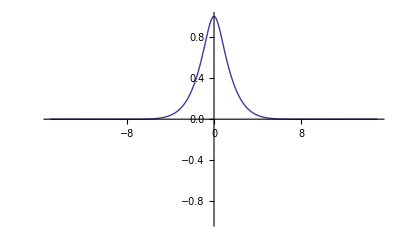

```mathematica
Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT},
ρ1=-0.5;κ1=0.2;V1=0.1;ρ2=-0.5;κ2=0.2;V2=0.1;ρ3=-0.5;κ3=0.2;V3=0.1;ρ4=-0.5;κ4=0.2;V4=0.1;ρ5=-0.5;κ5=0.2;V5=0.1;ρi=-0.5;κi=0.2;Vi=0.1;
α11=0.001;α12=0.001;α13=0.001;α14=0.001;αi1=0.001;αi2=-0.001;αi3=-0.001;αi4=0.001;τ=10;λ=0.1;LT=1;
Plot[Re[AlphaDigitaleU1FondamentalTransform[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,z,λ,LT,τ]],{z,-15,15},PlotRange->{-1,1}]]
```

```mathematica
LogNormalCallPayOffFourierTransform[K,ω]
```

K^(1+ⅈ ω)/(ω (-ⅈ+ω))

```mathematica
(K)^(1+ⅈ ω)/(ⅈ  ω-ω^2)
```

```mathematica
AlphaDigitaleU1CallIntegrand[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,
α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0]) AlphaDigitaleU1FondamentalTransform[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ω,λ,LT,T]LogNormalCallPayOffFourierTransform[K,ω]]
```

```mathematica
AlphaDigitaleUiCallIntegrand[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,
α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_,ω_]:=Re[ⅇ^(-ⅈ ω  Log[S0]) AlphaDigitaleUiFondamentalTransform[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ω,λ,LT,T]LogNormalCallPayOffFourierTransform[K,ω]]
```

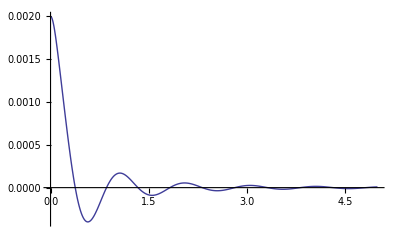
{1.859,-Graphics-}

```mathematica
Timing[Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0=0.05,T=10,K=0.0001,ω},
ρ1=-0.5;κ1=0.2;V1=0.1;ρ2=-0.5;κ2=0.2;V2=0.1;ρ3=-0.5;κ3=0.2;V3=0.1;ρ4=-0.5;κ4=0.2;V4=0.1;ρ5=-0.5;κ5=0.2;V5=0.001;ρi=-0.5;κi=0.2;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
Plot[{AlphaDigitaleU1CallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,
α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T,ω +0.15 ⅈ]},{ω,0,5},PlotRange->All]
]]
```

```mathematica
AlphaDigitaleU1CallN[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=
-1/π Re[Module[{λs=1.5,ω},
NIntegrate[AlphaDigitaleU1CallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T,ω +λs ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
AlphaDigitaleUiCallN[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=
-1/π Re[Module[{λs=1.5,ω},
NIntegrate[AlphaDigitaleUiCallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T,ω +λs ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
AlphaDigitaleU1PutN[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=
-1/π Re[Module[{λs=-0.5,ω},
NIntegrate[AlphaDigitaleU1CallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T,ω +λs ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
AlphaDigitaleUiPutN[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=
-1/π Re[Module[{λs=-0.5,ω},
NIntegrate[AlphaDigitaleUiCallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T,ω +λs ⅈ],
{ω,0,Infinity},MaxRecursion->30]]]
```

```mathematica
La fonction suivante calcule le forward dans ce nouveau numeraire, il est evidement different de Subscript[S, 0] car nous ne sommes plus dans la mesure de martingale !
```

```mathematica
AlphaDigitaleForwardU1N[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=AlphaDigitaleU1CallN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]-AlphaDigitaleU1PutN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]+K
```

```mathematica
AlphaDigitaleForwardUiN[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=AlphaDigitaleUiCallN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]-AlphaDigitaleUiPutN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]+K
```

```mathematica
Timing[Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0=0.05,T=10,K=0.04,ω},
ρ1=-0.5;κ1=0.2;V1=1;ρ2=-0.5;κ2=0.2;V2=1;ρ3=-0.5;κ3=0.2;V3=1;ρ4=-0.5;κ4=0.2;V4=1;ρ5=-0.5;κ5=0.2;V5=0.001;ρi=-0.5;κi=0.2;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
{AlphaDigitaleU1CallN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T],
AlphaDigitaleU1PutN[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T],
AlphaDigitaleForwardU1N[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]}]]
```

{0.609,{0.0103422,0.000220187,0.050122}}

```mathematica
AlphaDigitaleU1CallAux[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=
-1/π Re[Module[{λs=1.5,ω},
AdaptativeIntegrate[Function[ω,AlphaDigitaleU1CallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T,ω +λs ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
AlphaDigitaleU1PutAux[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=
-1/π Re[Module[{λs=-0.5,ω},
AdaptativeIntegrate[Function[ω,AlphaDigitaleU1CallIntegrand[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T,ω +λs ⅈ]],LegendreCoeffs[60],LegendreCoeffs[3],10,1,10^(-10),1000,1,LegendreCoeffs[20]][[2]]]]
```

```mathematica
AlphaForwardU1Aux[ρ1_,κ1_,V1_,ρ2_,κ2_,V2_,ρ3_,κ3_,V3_,ρ4_,κ4_,V4_,ρ5_,κ5_,V5_,ρi_,κi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,λ_,LT_,S0_,K_,T_]:=AlphaDigitaleU1CallAux[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]-AlphaDigitaleU1PutAux[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]+K
```

```mathematica
Timing[Module[{ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0=0.05,T=10,K=0.04,ω},
ρ1=-0.5;κ1=0.2;V1=1;ρ2=-0.5;κ2=0.2;V2=1;ρ3=-0.5;κ3=0.2;V3=1;ρ4=-0.5;κ4=0.2;V4=1;ρ5=-0.5;κ5=0.2;V5=0.001;ρi=-0.5;κi=0.2;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
{AlphaDigitaleU1CallAux[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T],
AlphaDigitaleU1PutAux[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T],
AlphaForwardU1Aux[ρ1,κ1,V1,ρ2,κ2,V2,ρ3,κ3,V3,ρ4,κ4,V4,ρ5,κ5,V5,ρi,κi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S0,K,T]}]]
```

{4.781,{0.0103491,0.000220185,0.0501289}}

## Encodage de la dynamique pour le calcul du spreadoption dans la mesure S_1 (calcul de E[1_(S_1-S_2>K)])

```mathematica
les browniens : {Subscript[W, 1],Subscript[W, 2],Subscript[W, 3],Subscript[W, 4],Subscript[W, 5],Subscript[W, i],Subscript[W̄, 1],Subscript[W̄, 2],Subscript[W̄, 3],Subscript[W̄, 4],Subscript[W̄, 5],Subscript[W̄, i]}
```

dS_1/S_1=∑_(j=1)^4 α_(1,j) √v_j dW_j+ √v_5 dW_5
dS_i/S_i=α_(i,1)√v_1 dW_1+α_(i,2)√v_2 dW_2+α_(i,3)√v_3 dW_3+α_(i,4)√v_4 dW_4+√v_i dW_i+(∑_(j=1)^4 (α_(i,j) α_(1,j)-(α_(1,j))^2)v_j-v_5)dt
dv_1=λ_1(θ_1-v_1)dt+κ_1 √v_1 d(W̄)_1;
dv_2=λ_2(θ_2-v_2)dt+κ_2 √v_2 d(W̄)_2
dv_3=λ_3(θ_3-v_3)dt+κ_3 √v_3 d(W̄)_3
dv_4=λ_4(θ_4-v_4)dt+κ_4 √v_4 d(W̄)_4
dv_5=λ_5(θ_5-v_5)dt+κ_5 √v_5 d(W̄)_5
dv_i=λ_i(θ_i-v_i)dt+κ_i √v_i d(W̄)_i
 dW_1 d(W̄)_1=ρ_1 dt;
 dW_2 d(W̄)_2=ρ_2 dt;
 dW_3 d(W̄)_3=ρ_3 dt;
 dW_4 d(W̄)_4=ρ_4 dt;
 dW_5 d(W̄)_5=ρ_5 dt;
 dW_i d(W̄)_i=ρ_i dt;

```mathematica
AlphaDigitaleCorr={
{1,0,0,0,0,0,rho1,0,0,0,0,0},
{0,1,0,0,0,0,0,rho2,0,0,0,0},
{0,0,1,0,0,0,0,0,rho3,0,0,0},
{0,0,0,1,0,0,0,0,0,rho4,0,0},
{0,0,0,0,1,0,0,0,0,0,rho5,0},
{0,0,0,0,0,1,0,0,0,0,0,rhoi},
{rho1,0,0,0,0,0,1,0,0,0,0,0},
{0,rho2,0,0,0,0,0,1,0,0,0,0},
{0,0,rho3,0,0,0,0,0,1,0,0,0},
{0,0,0,rho4,0,0,0,0,0,1,0,0},
{0,0,0,0,rho5,0,0,0,0,0,1,0},
{0,0,0,0,0,rhoi,0,0,0,0,0,1}
};
```

```mathematica
AlphaDigitaleDiff[x_]:=
D[x,S1]{alpha11 √V1 S1,alpha12 √V2 S1,alpha13 √V3 S1,alpha14 √V4 S1,√V5 S1,0,0,0,0,0,0,0}+
D[x,Si]{alphai1 √V1 Si,alphai2 √V2 Si,alphai3 √V3 Si,alphai4 √V4 Si,0,√Vi Si,0,0,0,0,0,0}+
D[x,V1]{0,0,0,0,0,0,kappaV1 √V1,0,0,0,0,0}+
D[x,V2]{0,0,0,0,0,0,0,kappaV2 √V2,0,0,0,0}+
D[x,V3]{0,0,0,0,0,0,0,0,kappaV3 √V3,0,0,0}+
D[x,V4]{0,0,0,0,0,0,0,0,0,kappaV4 √V4,0,0}+
D[x,V5]{0,0,0,0,0,0,0,0,0,0,kappaV5 √V5,0}+
D[x,Vi]{0,0,0,0,0,0,0,0,0,0,0,kappaV6 √Vi}
```

## Calcul des observables (VS, VarVS, COVarSVS) incrementale

```mathematica
zeroRule={kappaV1->0,kappaV2->0,kappaV3->0,kappaV4->0,kappaV5->0,kappaVi->0};
```

```mathematica
CompuputePureFunctionQuadriBiSuperHestonSpreadU1iObservable[spread_]:=
Module[{VS,VarVS,VarVS0,CoVarVS,CoVarVS0},
VS=Simplify[AlphaDigitaleDiff[spread].(AlphaDigitaleCorr.AlphaDigitaleDiff[spread])];
VarVS=Simplify[AlphaDigitaleDiff[VS].(AlphaDigitaleCorr.AlphaDigitaleDiff[VS])];
VarVS0=VarVS/.zeroRule;
CoVarVS=Simplify[AlphaDigitaleDiff[VS].(AlphaDigitaleCorr.AlphaDigitaleDiff[spread])];
CoVarVS0=CoVarVS /.zeroRule;
Apply[Function,{{S1,Si,
alpha11,alpha12,alpha13,alpha14,
alphai1,alphai2,alphai3,alphai4,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3,
rho4,kappaV4,V4,
rho5,kappaV5,V5,
rhoi,kappaVi,Vi},
{VS,Simplify[VarVS-VarVS0],Simplify[CoVarVS-CoVarVS0]}}]];
```

#### Spread 1 - i

```mathematica
AlphaDigitaleObservable1iz=CompuputePureFunctionQuadriBiSuperHestonSpreadU1iObservable[-(S1-Si)];
```

```mathematica
VSSpread1iz[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρi_,νi_,V0i_]:=AlphaDigitaleObservable1iz[S1,Si,
alpha11,alpha12,alpha13,alpha14,
alphai1,alphai2,alphai3,alphai4,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3,
rho4,kappaV4,V4,
rho5,kappaV5,V5,
rhoi,kappaVi,Vi][[1]]
```

```mathematica
VarVSSpread1iz[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρi_,νi_,V0i_]:=AlphaDigitaleObservable1iz[S1,Si,
alpha11,alpha12,alpha13,alpha14,
alphai1,alphai2,alphai3,alphai4,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3,
rho4,kappaV4,V4,
rho5,kappaV5,V5,
rhoi,kappaVi,Vi][[2]]
```

```mathematica
CoVarVSSpread1iz[ρ1_,ν1_,V01_,ρ2_,ν2_,V02_,ρ3_,ν3_,V03_,ρ4_,ν4_,V04_,ρ5_,ν5_,V05_,ρi_,νi_,V0i_]:=AlphaDigitaleObservable1iz[S1,Si,
alpha11,alpha12,alpha13,alpha14,
alphai1,alphai2,alphai3,alphai4,
rho1,kappaV1,V1,
rho2,kappaV2,V2,
rho3,kappaV3,V3,
rho4,kappaV4,V4,
rho5,kappaV5,V5,
rhoi,kappaVi,Vi][[3]]
```

#### Paying 1 (pure digitale)

```mathematica
IntercalePrice[K1List_,K2List_]:=Module[{nb1=Length[K1List],nb2=Length[K2List],tab,j=1,itab=1,j1=1,j2=1},
tab=Table[0,{i,1,nb1+nb2}];
While[((j1≤nb1)||(j2≤nb2))&&j<=nb1+nb2,
If[itab==1,tab[[j]]=K1List[[j1]]];If[itab==2,tab[[j]]=K2List[[j2]]];
If[itab==1,j1=j1+1;If[j2<=nb2,itab=2],
j2=j2+1;If[j1<=nb1,itab=1]];
j++
];
tab]
```

```mathematica
IntercalePrice[{a1,a2,a3,a4,a5},{b1,b2,b3,b4,b5}]
```

{a1,b1,a2,b2,a3,b3,a4,b4,a5,b5}

```mathematica
SmileAlphaDigitale[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_,T_,LimitGindinkin_,printflag_]:=SmileAlphaDigitalelist[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,{K},T,LimitGindinkin,printflag][[1]]
```

```mathematica
SmileAlphaDigitale[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_List,T_,LimitGindinkin_,printflag_]:=SmileAlphaDigitalelist[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,K,T,LimitGindinkin,printflag]
```

```mathematica
SmileAlphaDigitalelist[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_List,T_,LimitGindinkin_,printflag_]:=Module[{ρprojeté,νprojeté,prices,VarVSIncrementale,CoVarSVSIncrementale,VS,Sig1,Sig2,Correl12,numinimum,rhominimum,VarVSTotal,CoVarSVSTotal,digitaleprices,forward,shiftL,CompoundK,V0projeté,V0minimim,,nbsteps=10,scale=8,microratio=20},

Sig1=√(α11^2 V1+α12^2 V2+α13^2 V3+α14^2 V4+V5);Sig2=√(αi1^2 V1+αi2^2 V2+αi3^2 V3+αi4^2 V4+Vi);Correl12= (α11 αi1  V1+α12 αi2  V2+α13 αi3  V3+α14 αi4  V4)/(Sig1 Sig2);
{V0minimim,rhominimum,numinimum}=HestonFromBilog[S1,Si,Sig1,Sig2,Correl12,T,λ,LT];
If[printflag==1 || MemberQ[printflag,1] ,Print["V0minimim=",V0minimim," rhominimum= ",rhominimum," Numinimum=",numinimum]];
If[printflag==1 || MemberQ[printflag,1] ,Print["VSminimale=",V0minimim," VarVSminimale=",numinimum^2 V0minimim," CoVarSVSminimale=",rhominimum V0minimim numinimum]];
{VS,VarVSIncrementale,CoVarSVSIncrementale}=AlphaDigitaleObservable1iz[S1,Si,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi];
If[printflag==1 || MemberQ[printflag,1] ,Print["VS=",VS," VarVSIncrementale=",VarVSIncrementale," CoVarSVSIncrementale=",CoVarSVSIncrementale]];
VarVSTotal=VarVSIncrementale+numinimum^2 V0minimim;
CoVarSVSTotal=CoVarSVSIncrementale+rhominimum V0minimim numinimum;
If[printflag==1 || MemberQ[printflag,1] ,Print["VSTotal=",V0minimim," VarVSTotal=",VarVSTotal," CoVarSVSTotal= ",CoVarSVSTotal]];
ρprojeté=CoVarSVSTotal/(√(V0minimim VarVSTotal));νprojeté=√(VarVSTotal/V0minimim);V0projeté=V0minimim;
forward=S1-Si;
If[printflag==1 || MemberQ[printflag,1] ,Print["Normal Heston Parameters=",{{"S0",forward},{"V0",V0projeté},{"ρ",ρprojeté},{"ν",νprojeté},
{"standard dev equi.",√VS},{"ν normalized",νprojeté/(√VS)}} //MatrixForm]];
shiftL=0.0008;
CompoundK=IntercalePrice[K-shiftL,K+shiftL];
prices=DerivativeHestonNormalCall[ρprojeté,λ,LT,νprojeté,V0projeté,S1-Si,CompoundK,T,nbsteps,scale,microratio,0][[1]];
If[printflag==1 || MemberQ[printflag,1] ,Print["spreadoption prices=",prices]];
digitaleprices=Table[(prices[[2i-1]]-prices[[2i]])/(2shiftL),{i,1,Length[K]}];
If[printflag==1 || MemberQ[printflag,1] ,Print["digitale prices=",digitaleprices]];
digitaleprices
]
```

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.051,T=15,K=0.008,LimitGindinkin=2,printflag=1},
ρ1=-0.5;ν1=0.2;V1=1;ρ2=-0.5;ν2=0.2;V2=1;ρ3=-0.5;ν3=0.2;V3=1;ρ4=-0.5;ν4=0.2;V4=1;ρ5=-0.5;ν5=0.2;V5=0.001;ρi=-0.5;νi=0.2;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
SmileAlphaDigitale[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,K,T,LimitGindinkin,printflag]]]]
```

V0minimim=0.000021686 rhominimum= -0.143572 Numinimum=0.00998258

VSminimale=0.000021686 VarVSminimale=2.16105×10^-9 CoVarSVSminimale=-3.10808×10^-8

VS=7.1414×10^-6 VarVSIncrementale=2.46584×10^-10 CoVarSVSIncrementale=1.27061×10^-8

VSTotal=0.000021686 VarVSTotal=2.40763×10^-9 CoVarSVSTotal= -1.83747×10^-8

Normal Heston Parameters=(S0 | -0.001
V0 | 0.000021686
ρ | -0.0804148
ν | 0.0105367
standard dev equi. | 0.00267234
ν normalized | 3.94288)

spreadoption prices={0.00147342,0.00127307}

digitale prices={0.125217}

{2.953,0.125217}

```mathematica
Off[NIntegrate::"slwcon"]
```

0.00845068

strikes={-0.00281689,-0.00140845,0,0.00140845,0.00281689}

V0minimim=0.0000311044 rhominimum= -0.18581 Numinimum=0.0164085

VSminimale=0.0000311044 VarVSminimale=8.37446×10^-9 CoVarSVSminimale=-9.48329×10^-8

VS=7.1414×10^-6 VarVSIncrementale=-4.71173×10^-27 CoVarSVSIncrementale=4.3712×10^-22

VSTotal=0.0000311044 VarVSTotal=8.37446×10^-9 CoVarSVSTotal= -9.48329×10^-8

Normal Heston Parameters=(S0 | -0.001
V0 | 0.0000311044
ρ | -0.18581
ν | 0.0164085
standard dev equi. | 0.00267234
ν normalized | 6.14011)

spreadoption prices={0.0248,0.0232,0.0199775,0.0185054,0.015401,0.0139557,0.0109344,0.00954713,0.00878045,0.00745004,0.00672539,0.00549607,0.00594669,0.00477997,0.00484934,0.00381374,0.00331398,0.00259765,0.00228718,0.00186415,0.00188664,0.00157446,0.00168055,0.00142087,0.00130277,0.00112869,0.0010465,0.000921585,0.000720968,0.000648003,0.000524203,0.000477166,0.000392375,0.000358416}

digitale prices={1.,0.920008,0.903291,0.867073,0.831506,0.768321,0.7292,0.64725,0.447706,0.264396,0.195111,0.162299,0.108799,0.078072,0.0456031,0.0293982,0.0212244}

0.00845068

strikes={-0.00281689,-0.00140845,0,0.00140845,0.00281689}

V0minimim=0.0000311044 rhominimum= -0.18581 Numinimum=0.0164085

VSminimale=0.0000311044 VarVSminimale=8.37446×10^-9 CoVarSVSminimale=-9.48329×10^-8

VS=7.1414×10^-6 VarVSIncrementale=1.96987×10^-14 CoVarSVSIncrementale=1.0928×10^-10

VSTotal=0.0000311044 VarVSTotal=8.37448×10^-9 CoVarSVSTotal= -9.47236×10^-8

Normal Heston Parameters=(S0 | -0.001
V0 | 0.0000311044
ρ | -0.185596
ν | 0.0164085
standard dev equi. | 0.00267234
ν normalized | 6.14012)

spreadoption prices={0.0248,0.0232,0.0199732,0.0185013,0.0153972,0.013952,0.0109311,0.0095439,0.0087773,0.00744702,0.00672245,0.00549328,0.00594385,0.00477729,0.00484664,0.00381122,0.00331158,0.00259544,0.00228506,0.00186217,0.00188466,0.00157259,0.00167864,0.00141906,0.00130101,0.00112701,0.00104486,0.000920019,0.000719539,0.000646634,0.000522951,0.000475965,0.000391275,0.000357362}

digitale prices={1.,0.919908,0.903201,0.866988,0.83142,0.768227,0.7291,0.647136,0.447586,0.264309,0.195041,0.162237,0.108748,0.0780274,0.0455659,0.029366,0.0211958}

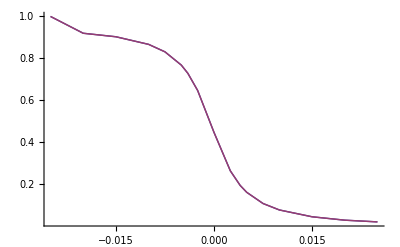
{16.875,-Graphics-}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,S1=0.05,Si=0.051,
T=10,λ=0.1,LT=1,
KList={-0.025,-0.02,-0.015,-0.01,-0.0075,-0.005,-0.004,-0.0025,0,0.0025,0.004,0.005,0.0075,0.01,0.015,0.02,0.025},LimitGindinkin=10,printflag=1,prices,νcommun,νcommun1,bilogprices},
νcommun=0.0000000000004;
ρ1=-0.5;ν1=νcommun;V1=1;ρ2=-0.5;ν2=νcommun;V2=1;ρ3=-0.5;ν3=νcommun;V3=1;ρ4=-0.5;ν4=νcommun;V4=1;ρ5=-0.5;ν5=νcommun 0.001;V5=0.001;ρi=-0.5;νi=νcommun 0.001;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;
bilogprices=SmileAlphaDigitale[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
νcommun1=0.1;
ρ1=-0.5;ν1=νcommun1;V1=1;ρ2=-0.5;ν2=νcommun1;V2=1;ρ3=-0.5;ν3=νcommun1;V3=1;ρ4=-0.5;ν4=νcommun1;V4=1;ρ5=-0.5;ν5=νcommun1 0.001;V5=0.001;ρi=-0.5;νi=νcommun1 0.001;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;
prices=SmileAlphaDigitale[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
ListPlot[{Transpose[{KList,bilogprices}],Transpose[{KList,prices}]},Joined->True]
]]]
```

#### Paying S1

```mathematica
SmileAlphaDigitaleU1[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_,T_,LimitGindinkin_,printflag_]:=Module[{forwardSi,forwardS1,ρprojeté,νprojeté,prices,VarVS,CoVarSVS,VS,Sig1,Sig2,Correl12,numinimum,rhominimum,VarVSTotal,CoVarSVSTotal,ρprojetéIni,forward,shiftL,equivalentσ1,equivalentσi,equivalentρ,S1Mesure1,SiMesure1},
(* determination de la variance *)
forwardSi=AlphaDigitaleForwardUiN[ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,Si,K,T];
forwardS1=AlphaDigitaleForwardU1N[ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,Si,K,T];
forward=forwardS1-forwardSi;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
If[printflag==1 || MemberQ[printflag,1] ,Print["equivalentσ1=",equivalentσ1," equivalentσi=",equivalentσi," equivalentρ=",equivalentρ]];
S1Mesure1=S1 Exp[equivalentσ1^2 T];SiMesure1=Si Exp[equivalentρ equivalentσ1 equivalentσi T];
If[printflag==1 || MemberQ[printflag,1] ,Print["S1Mesure1=",S1Mesure1," SiMesure1=",SiMesure1," forward mesure 1=",S1Mesure1-SiMesure1]];

If[printflag==1 || MemberQ[printflag,1] ,Print["forwardS1=",forwardS1," forwardSi=",forwardSi," forward=",forward]];
(* determination des parametres de smile initial grace au generateur*)
{VS,VarVS,CoVarSVS}=AlphaDigitaleObservable1iz[S1,Si,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi];
If[printflag==1 || MemberQ[printflag,1] ,Print["VS=",VS," VarVS=",VarVS," CoVarSVS=",CoVarSVS]];

Sig1=√(α11^2 V1+α12^2 V2+α13^2 V3+α14^2 V4+V5);Sig2=√(αi1^2 V1+αi2^2 V2+αi3^2 V3+αi4^2 V4+Vi);Correl12= (α11 αi1  V1+α12 αi2  V2+α13 αi3  V3+α14 αi4  V4)/(Sig1 Sig2);ρprojetéIni=-0.2;
{numinimum,rhominimum}=
NuRhoMinimunNormalHestonFromBilog[forwardS1 ,forwardSi,Sig1,Sig2,Correl12,T,ρprojetéIni,λ,LT ,VS,0,LimitGindinkin];
If[printflag==1 || MemberQ[printflag,1] ,Print[" Numinimum=",numinimum," rhominimum= ",rhominimum]];
VarVSTotal=VarVS+numinimum^2 VS;
CoVarSVSTotal=CoVarSVS;
ρprojeté=CoVarSVSTotal/(√(VS VarVSTotal));νprojeté=√(VarVSTotal/VS);

(* ajustement du kurtosis par effet de vol *)
(* νbrut= νprojeté √(VS/VarRealSpead);νnormalized=νbrut/(√TrueIniVarSpread);*)
If[printflag==1 || MemberQ[printflag,1] ,Print["Normal Heston Parameters=",{{"S0",forward},{"V0",VS},{"ρ",ρprojeté},{"ν",νprojeté},
{"ν normalized",νprojeté/(√VS)},{"standard dev equi.",√VS}} //MatrixForm]];
shiftL=0.0001;
forward=S1Mesure1-SiMesure1;(* peut etre enlevée *)
prices=TransHestonNormalCall[ρprojeté,λ,LT VS,νprojeté,VS,forward,{K-shiftL,K+shiftL},T,LimitGindinkin];
If[printflag==1 || MemberQ[printflag,1] ,Print["prices=",prices]];
S1(prices[[1]]-prices[[2]])/(2shiftL)
]
```

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.051,T=10,K=0.04,LimitGindinkin=2,printflag=1},
ρ1=-0.5;ν1=0.2;V1=1;ρ2=-0.5;ν2=0.2;V2=1;ρ3=-0.5;ν3=0.2;V3=1;ρ4=-0.5;ν4=0.2;V4=1;ρ5=-0.5;ν5=0.2;V5=0.001;ρi=-0.5;νi=0.2;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
SmileAlphaDigitaleU1[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,K,T,LimitGindinkin,printflag]]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

equivalentσ1=0.0374166 equivalentσi=0.0374166 equivalentρ=0.

S1Mesure1=0.0507049 SiMesure1=0.051 forward mesure 1=-0.000295077

forwardS1=0.0511245 forwardSi=0.05137 forward=-0.000245559

VS=7.1414×10^-6 VarVS=2.46584×10^-10 CoVarSVS=1.27061×10^-8

N::meprec: Internal precision limit $MaxExtraPrecision = 100. reached while evaluating √π.

N::meprec: Internal precision limit $MaxExtraPrecision = 100. reached while evaluating 1/√π.

N::meprec: Internal precision limit $MaxExtraPrecision = 100. reached while evaluating √π.

General::stop: Further output of N :: "meprec" will be suppressed during this calculation.

Numinimum=0.000433949 rhominimum= -0.00319212

Normal Heston Parameters=(S0 | -0.000245559
V0 | 7.1414×10^-6
ρ | 0.301964
ν | 0.00589213
ν normalized | 2.20486
standard dev equi. | 0.00267234)

prices={0.000316051,0.000313555}

{5.039,0.000623911}

```mathematica
SmileAlphaDigitaleU1[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_List,T_,LimitGindinkin_,printflag_]:=SmileAlphaDigitaleU1list[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,K,T,LimitGindinkin,printflag]
```

```mathematica
SmileAlphaDigitaleU1list[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_List,T_,LimitGindinkin_,printflag_]:=Module[{forwardSi,forwardS1,ρprojeté,νprojeté,prices,VarVS,CoVarSVS,VS,Sig1,Sig2,Correl12,numinimum,rhominimum,VarVSTotal,CoVarSVSTotal,ρprojetéIni,forward,shiftL,equivalentσ1,equivalentσi,equivalentρ,S1Mesure1,SiMesure1},
(* determination de la variance *)
forwardSi=AlphaDigitaleForwardUiN[ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,Si,Si,T];
forwardS1=AlphaDigitaleForwardU1N[ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,Si,Si,T];
forward=forwardS1-forwardSi;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
If[printflag==1 || MemberQ[printflag,1] ,Print["equivalentσ1=",equivalentσ1," equivalentσi=",equivalentσi," equivalentρ=",equivalentρ]];
S1Mesure1=S1 Exp[equivalentσ1^2 T];SiMesure1=Si Exp[equivalentρ equivalentσ1 equivalentσi T];
If[printflag==1 || MemberQ[printflag,1] ,Print["S1Mesure1=",S1Mesure1," SiMesure1=",SiMesure1," forward mesure 1=",S1Mesure1-SiMesure1]];

If[printflag==1 || MemberQ[printflag,1] ,Print["forwardS1=",forwardS1," forwardSi=",forwardSi," forward=",forward]];
(* determination des parametres de smile initial grace au generateur*)
{VS,VarVS,CoVarSVS}=AlphaDigitaleObservable1iz[S1,Si,α11,α12,α13,α14,αi1,αi2,αi3,αi4,ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi];
If[printflag==1 || MemberQ[printflag,1] ,Print["VS=",VS," VarVS=",VarVS," CoVarSVS=",CoVarSVS]];

Sig1=√(α11^2 V1+α12^2 V2+α13^2 V3+α14^2 V4+V5);Sig2=√(αi1^2 V1+αi2^2 V2+αi3^2 V3+αi4^2 V4+Vi);Correl12= (α11 αi1  V1+α12 αi2  V2+α13 αi3  V3+α14 αi4  V4)/(Sig1 Sig2);ρprojetéIni=-0.2;
{numinimum,rhominimum}=
NuRhoMinimunNormalHestonFromBilog[forwardS1 ,forwardSi,Sig1,Sig2,Correl12,T,ρprojetéIni,λ,LT ,VS,0,LimitGindinkin];
If[printflag==1 || MemberQ[printflag,1] ,Print[" Numinimum=",numinimum," rhominimum= ",rhominimum]];
VarVSTotal=VarVS+numinimum^2 VS;
CoVarSVSTotal=CoVarSVS;
ρprojeté=CoVarSVSTotal/(√(VS VarVSTotal));νprojeté=√(VarVSTotal/VS);

(* ajustement du kurtosis par effet de vol *)
(* νbrut= νprojeté √(VS/VarRealSpead);νnormalized=νbrut/(√TrueIniVarSpread);*)
forward=forwardS1-forwardSi;
If[printflag==1 || MemberQ[printflag,1] ,Print["Normal Heston Parameters=",{{"S0",forward},{"V0",VS},{"ρ",ρprojeté},{"ν",νprojeté},
{"ν normalized",νprojeté/(√VS)},{"standard dev equi.",√VS}} //MatrixForm]];
shiftL=0.0001;
Table[
prices=TransHestonNormalCall[ρprojeté,λ,LT VS,νprojeté,VS,forward,{K[[i]]-shiftL,K[[i]]+shiftL},T,LimitGindinkin];
If[printflag==1 || MemberQ[printflag,1] ,Print["prices=",prices]];
S1(prices[[1]]-prices[[2]])/(2shiftL),{i,1,Length[K]}]
]
```

```mathematica
Off[NIntegrate::"slwcon"]
```

```mathematica
(* converegence de la digitale payant S1 vers l'equivalent bilog *)
```

```mathematica
Off[N::"meprec"]
```

#### comparaison de la digitale payabt S1 avec la bilog

{equivalentσ1,equivalentσi,equivalentρ}={0.0374166,0.0374166,0.}

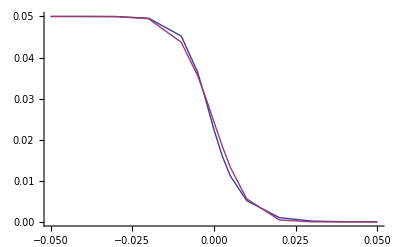
{11.562,-Graphics-}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.051,T=10,KList={-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.0025,0,0.0025,0.005,0.01,0.02,0.03,0.04,0.05},LimitGindinkin=10,printflag=0,prices,equivalentσ1,equivalentσi,equivalentρ,bilogprices,nuglobal},nuglobal=0.05;
ρ1=-0.5;ν1=nuglobal;V1=1;ρ2=-0.5;ν2=nuglobal;V2=1;ρ3=-0.5;ν3=nuglobal;V3=1;ρ4=-0.5;ν4=nuglobal;V4=1;ρ5=-0.5;ν5=nuglobal;V5=0.001;ρi=-0.5;νi=nuglobal;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
prices=SmileAlphaDigitaleU1[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
Print["{equivalentσ1,equivalentσi,equivalentρ}=",{equivalentσ1,equivalentσi,equivalentρ}];
bilogprices=Table[S1 MesureQ1LogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
ListPlot[{Transpose[{KList,prices}],Transpose[{KList,bilogprices}]},Joined->True]
]]]
```

#### Paying Si

```mathematica
On se sert de
```

```mathematica
E[S2 Subscript[1, S1-S2>K]]=S2-E[S2 Subscript[1, S1-S2<K]]=S2-E[S2 Subscript[1, S2-S1>-K]]
```

```mathematica
SmileAlphaDigitaleUi[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_,T_,LimitGindinkin_,printflag_]:=
Si-SmileAlphaDigitaleU1list[Si,S1, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρi,νi,Vi,ρ5,ν5,V5,αi1,αi2,αi3,αi4,α11,α12,α13,α14,LT,λ,{-K},T,LimitGindinkin,printflag][[1]]
```

```mathematica
SmileAlphaDigitaleUi[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,LT_,λ_,K_List,T_,LimitGindinkin_,printflag_]:=
Si-SmileAlphaDigitaleU1list[Si,S1, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρi,νi,Vi,ρ5,ν5,V5,αi1,αi2,αi3,αi4,α11,α12,α13,α14,LT,λ,-K,T,LimitGindinkin,printflag]
```

#### comparaison de la digitale payant Si avec la bilog

N::meprec: Internal precision limit $MaxExtraPrecision = 100. reached while evaluating √π.

N::meprec: Internal precision limit $MaxExtraPrecision = 100. reached while evaluating 1/√π.

N::meprec: Internal precision limit $MaxExtraPrecision = 100. reached while evaluating √π.

General::stop: Further output of N :: "meprec" will be suppressed during this calculation.

{equivalentσ1,equivalentσi,equivalentρ}={0.0374166,0.0374166,0.}

{equivalentσ1,equivalentσi,equivalentρ}={0.0374166,0.0374166,0.}

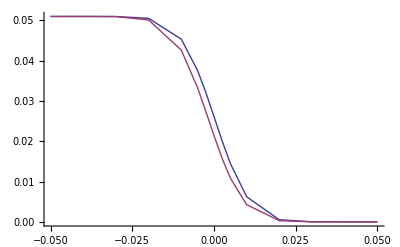
{5.818,-Graphics-}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.051,T=10,KList={-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.0025,0,0.0025,0.005,0.01,0.02,0.03,0.04,0.05},LimitGindinkin=10,printflag=0,prices,equivalentσ1,equivalentσi,equivalentρ,bilogprices,nuglobal},nuglobal=0.0005;
ρ1=-0.5;ν1=nuglobal;V1=1;ρ2=-0.5;ν2=nuglobal;V2=1;ρ3=-0.5;ν3=nuglobal;V3=1;ρ4=-0.5;ν4=nuglobal;V4=1;ρ5=-0.5;ν5=nuglobal;V5=0.001;ρi=-0.5;νi=nuglobal;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
prices=SmileAlphaDigitaleUi[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
Print["{equivalentσ1,equivalentσi,equivalentρ}=",{equivalentσ1,equivalentσi,equivalentρ}];
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[Si,S1, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρi,νi,Vi,ρ5,ν5,V5,αi1,αi2,αi3,αi4,α11,α12,α13,α14,T];
Print["{equivalentσ1,equivalentσi,equivalentρ}=",{equivalentσ1,equivalentσi,equivalentρ}];
bilogprices=Table[Si MesureQ2LogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
ListPlot[{Transpose[{KList,prices}],Transpose[{KList,bilogprices}]},Joined->True]
]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

N::meprec: Internal precision limit $MaxExtraPrecision = 100. reached while evaluating √π.

N::meprec: Internal precision limit $MaxExtraPrecision = 100. reached while evaluating 1/√π.

N::meprec: Internal precision limit $MaxExtraPrecision = 100. reached while evaluating √π.

General::stop: Further output of N :: "meprec" will be suppressed during this calculation.

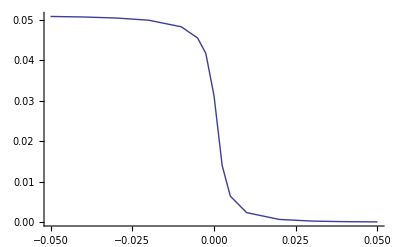
{15.241,-Graphics-}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.051,T=10,KList={-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.0025,0,0.0025,0.005,0.01,0.02,0.03,0.04,0.05},LimitGindinkin=10,printflag=0,prices},
ρ1=-0.5;ν1=0.2;V1=1;ρ2=-0.5;ν2=0.2;V2=1;ρ3=-0.5;ν3=0.2;V3=1;ρ4=-0.5;ν4=0.2;V4=1;ρ5=-0.5;ν5=0.2;V5=0.001;ρi=-0.5;νi=0.2;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
prices=SmileAlphaDigitaleUi[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
ListPlot[Transpose[{KList,prices}],Joined->True]
]]]
```

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.051,T=10,equivalentσ1,equivalentσi,equivalentρ,S1Mesure1,S1Mesurei,SiMesure1,SiMesurei,
KList={0},LimitGindinkin=10,printflag=0,prices1,pricesi,priced,priceK},
ρ1=-0.5;ν1=0.2;V1=1;ρ2=-0.5;ν2=0.2;V2=1;ρ3=-0.5;ν3=0.2;V3=1;ρ4=-0.5;ν4=0.2;V4=1;ρ5=-0.5;ν5=0.2;V5=0.001;ρi=-0.5;νi=0.2;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
prices1=SmileAlphaDigitaleU1[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
pricesi=SmileAlphaDigitaleUi[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
priced=SmileAlphaDigitale[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
priceK=Table[priced[[i]] KList[[i]],{i,Length[KList]}];
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
S1Mesure1=S1 Exp[equivalentσ1^2 T];SiMesure1=Si Exp[equivalentρ equivalentσ1 equivalentσi T];
Print["S1Mesure1=",S1Mesure1," SiMesure1=",SiMesure1," forward mesure 1=",S1Mesure1-SiMesure1];
S1Mesurei=S1 Exp[equivalentρ equivalentσ1 equivalentσi T];SiMesurei=Si Exp[ equivalentσi^2 T];
Print["S1Mesurei=",S1Mesurei," SiMesurei=",SiMesurei," forward mesure i=",S1Mesurei-SiMesurei];
]]]
```

S1Mesure1=0.0507049 SiMesure1=0.05 forward mesure 1=0.000704923

S1Mesurei=0.05 SiMesurei=0.051719 forward mesure i=-0.00171902

{20.797,Null}

#### Consistence

```mathematica
(* consistence bilog *)
```

{equivalentσ1,equivalentσi,equivalentρ}={0.0374166,0.0374166,0.}

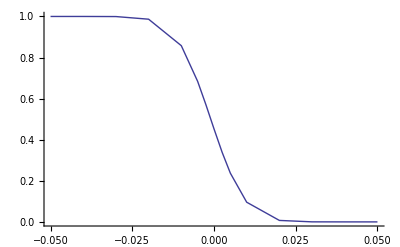
{4.25,-Graphics-}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.051,T=10,KList={-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.0025,0,0.0025,0.005,0.01,0.02,0.03,0.04,0.05},LimitGindinkin=10,printflag=0,prices,equivalentσ1,equivalentσi,equivalentρ,bilogprices,nuglobal},nuglobal=0.05;
ρ1=-0.5;ν1=nuglobal;V1=1;ρ2=-0.5;ν2=nuglobal;V2=1;ρ3=-0.5;ν3=nuglobal;V3=1;ρ4=-0.5;ν4=nuglobal;V4=1;ρ5=-0.5;ν5=nuglobal;V5=0.001;ρi=-0.5;νi=nuglobal;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
Print["{equivalentσ1,equivalentσi,equivalentρ}=",{equivalentσ1,equivalentσi,equivalentρ}];
bilogprices=Table[ MesureQTLogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
ListPlot[Transpose[{KList,bilogprices}],Joined->True]
]]]
```

```mathematica
Off[N::"meprec"]
```

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.055,T=10,equivalentσ1,equivalentσi,equivalentρ,bilogdigitale,
bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysKGRAPH,paysdigitaleGRAPH,K=0,LimitGindinkin=10,printflag=0,prices1,pricesi,priced,priceK,commonν=0.0001,bilogprices1,bilogpricesi,bilogpriceK},
ρ1=-0.5;ν1=commonν;V1=1;ρ2=-0.5;ν2=commonν;V2=1;ρ3=-0.5;ν3=commonν;V3=1;ρ4=-0.5;ν4=commonν;V4=1;ρ5=-0.5;ν5=commonν;V5=0.001;ρi=-0.5;νi=commonν;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
Print["{equivalentσ1,equivalentσi,equivalentρ}=",{equivalentσ1,equivalentσi,equivalentρ}];
bilogprices1=S1 MesureQ1LogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,K,T];
bilogpricesi=Si MesureQ2LogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,K,T];
bilogpriceK=K MesureQTLogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,K,T];
bilogdigitale=MesureQTLogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,K,T];
Print["bilogprices1=",bilogprices1," bilogpricesi=",bilogpricesi," bilogdigitale=",bilogdigitale];
prices1=SmileAlphaDigitaleU1[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,{K},T,LimitGindinkin,printflag][[1]];
pricesi=SmileAlphaDigitaleUi[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,{K},T,LimitGindinkin,printflag][[1]];
priced=SmileAlphaDigitale[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,{K},T,LimitGindinkin,printflag][[1]];
priceK=priced K;
Print["bilogprices1=",bilogprices1," prices1=",prices1];
Print["bilogpricesi=",bilogpricesi," pricesi",pricesi];
Print["bilogdigitale=",bilogdigitale," priced=",priced];
]]]
```

{equivalentσ1,equivalentσi,equivalentρ}={0.0374166,0.0374166,0.}

bilogprices1=0.0156756 bilogpricesi=0.0141238 bilogdigitale=0.284479

bilogprices1=0.0156756 prices1=0.0243591

bilogpricesi=0.0141238 pricesi0.028143

bilogdigitale=0.284479 priced=0.281978

{15.563,Null}

N::meprec: Internal precision limit $MaxExtraPrecision = 100. reached while evaluating √π.

N::meprec: Internal precision limit $MaxExtraPrecision = 100. reached while evaluating 1/√π.

N::meprec: Internal precision limit $MaxExtraPrecision = 100. reached while evaluating √π.

General::stop: Further output of N :: "meprec" will be suppressed during this calculation.

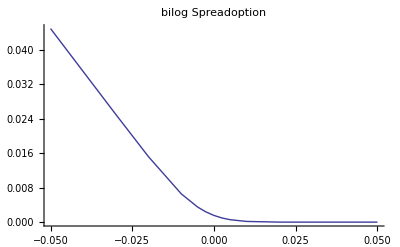
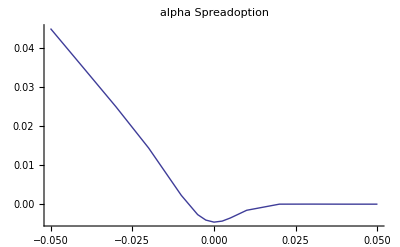
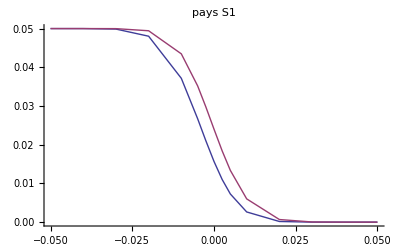
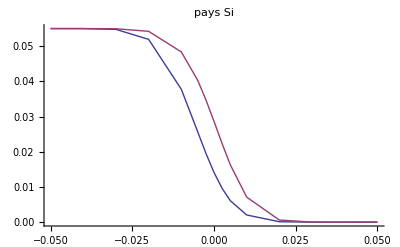
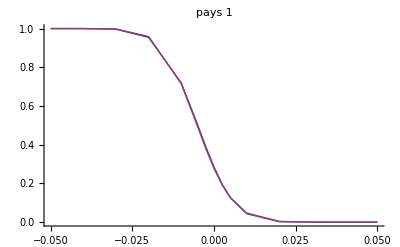
{32.985,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.055,T=10,equivalentσ1,equivalentσi,equivalentρ,bilogdigitale,
bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysKGRAPH,paysdigitaleGRAPH,KList={-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.0025,0,0.0025,0.005,0.01,0.02,0.03,0.04,0.05},LimitGindinkin=10,printflag=0,prices1,pricesi,priced,priceK,commonν=0.01,bilogprices1,bilogpricesi,bilogpriceK},
ρ1=-0.5;ν1=commonν;V1=1;ρ2=-0.5;ν2=commonν;V2=1;ρ3=-0.5;ν3=commonν;V3=1;ρ4=-0.5;ν4=commonν;V4=1;ρ5=-0.5;ν5=commonν;V5=0.001;ρi=-0.5;νi=commonν;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
bilogprices1=Table[S1 MesureQ1LogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
bilogpricesi=Table[Si MesureQ2LogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
bilogpriceK=Table[KList[[i]] MesureQTLogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
bilogdigitale=Table[ MesureQTLogNormalSpreadDigitale[S1,Si,equivalentσ1,equivalentσi,equivalentρ,KList[[i]],T],{i,1,Length[KList]}];
prices1=SmileAlphaDigitaleU1[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
pricesi=SmileAlphaDigitaleUi[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
priced=SmileAlphaDigitale[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
priceK=Table[priced[[i]] KList[[i]],{i,Length[KList]}];
bilogSpreadoptionGRAPH=ListPlot[Transpose[{KList,bilogprices1-bilogpricesi-bilogpriceK}],Joined->True,PlotLabel->"bilog Spreadoption"];
alphaSpreadoptionGRAPH=ListPlot[Transpose[{KList,prices1-pricesi-priceK}],Joined->True,PlotLabel->"alpha Spreadoption"];
paysS1GRAPH=ListPlot[{Transpose[{KList,bilogprices1}],Transpose[{KList,prices1}]},Joined->True,PlotLabel->"pays S1"];
paysSiGRAPH=ListPlot[{Transpose[{KList,bilogpricesi}],Transpose[{KList,pricesi}]},Joined->True,PlotLabel->"pays Si"];
paysdigitaleGRAPH=ListPlot[{Transpose[{KList,bilogdigitale}],Transpose[{KList,priced}]},Joined->True,PlotLabel->"pays 1"];
{bilogSpreadoptionGRAPH,alphaSpreadoptionGRAPH,paysS1GRAPH,paysSiGRAPH,paysdigitaleGRAPH}
]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

N::meprec: Internal precision limit $MaxExtraPrecision = 100. reached while evaluating √π.

N::meprec: Internal precision limit $MaxExtraPrecision = 100. reached while evaluating 1/√π.

N::meprec: Internal precision limit $MaxExtraPrecision = 100. reached while evaluating √π.

General::stop: Further output of N :: "meprec" will be suppressed during this calculation.

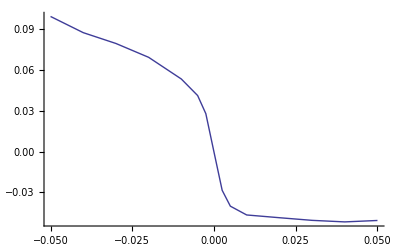
{32.449,2 -Graphics-}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.051,T=10,equivalentσ1,equivalentσi,equivalentρ,KList={-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.0025,0,0.0025,0.005,0.01,0.02,0.03,0.04,0.05},LimitGindinkin=10,printflag=0,prices1,pricesi,priced,priceK},
ρ1=-0.5;ν1=0.2;V1=1;ρ2=-0.5;ν2=0.2;V2=1;ρ3=-0.5;ν3=0.2;V3=1;ρ4=-0.5;ν4=0.2;V4=1;ρ5=-0.5;ν5=0.2;V5=0.001;ρi=-0.5;νi=0.2;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
prices1=SmileAlphaDigitaleU1[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
pricesi=SmileAlphaDigitaleUi[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
priced=SmileAlphaDigitale[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
priceK=Table[priced[[i]] KList[[i]],{i,Length[KList]}];
{equivalentσ1,equivalentσi,equivalentρ}=ComputeEquivalentBilogFromAlpha[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,T];
S1Mesure1=S1 Exp[equivalentσ1^2 T];SiMesure1=S1 Exp[equivalentρ equivalentσ1 equivalentσi T];
S1Mesurei=S1 Exp[equivalentρ equivalentσ1 equivalentσi T];SiMesurei=Si Exp[ equivalentσi^2 T];
2ListPlot[Transpose[{KList,prices1-pricesi-priceK}],Joined->True]
]]]
```

```mathematica
ComputeEquivalentBilogFromAlpha[S1_,Si_, ρ1_,ν1_,V1_,ρ2_,ν2_,V2_,ρ3_,ν3_,V3_,ρ4_,ν4_,V4_,ρ5_,ν5_,V5_,ρi_,νi_,Vi_,α11_,α12_,α13_,α14_,αi1_,αi2_,αi3_,αi4_,T_]:=
Module[{equivalentσ1,equivalentσ2,equivalentρ},
equivalentσ1=√(α11^2 V1+α12^2 V2+α13^2 V3+α14^2 V4+V5);
equivalentσ2=√(αi1^2 V1+αi2^2 V2+αi3^2 V3+αi4^2 V4+Vi);
equivalentρ=(α11 αi1 V1+α12 αi2 V2+α13 αi3 V3+α14 αi4 V4)/(equivalentσ1 equivalentσ2);
{equivalentσ1,equivalentσ2,equivalentρ}
]
```

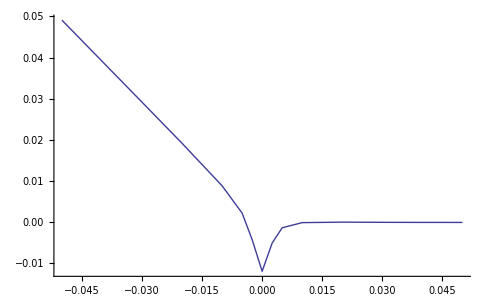
{91.578,-Graphics-}

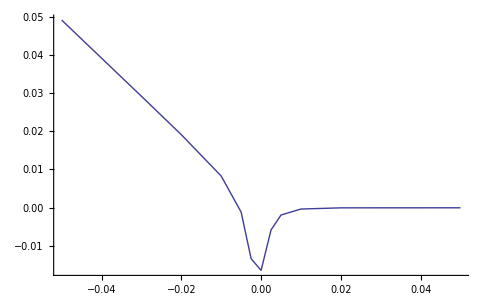
{93.953,-Graphics-}

```mathematica
ancien essai
```

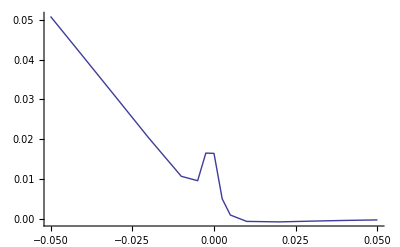
{80.515,-Graphics-}

```mathematica
Block[{$MaxExtraPrecision=100},Timing[Module[{ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,Z,τ,α2,β2,α11,α12,α13,α14,αi1,αi2,αi3,αi4,λ,LT,S1=0.05,Si=0.051,T=10,KList={-0.05,-0.04,-0.03,-0.02,-0.01,-0.005,-0.0025,0,0.0025,0.005,0.01,0.02,0.03,0.04,0.05},LimitGindinkin=10,printflag=0,prices1,pricesi,priced,priceK},
ρ1=-0.5;ν1=0.2;V1=1;ρ2=-0.5;ν2=0.2;V2=1;ρ3=-0.5;ν3=0.2;V3=1;ρ4=-0.5;ν4=0.2;V4=1;ρ5=-0.5;ν5=0.2;V5=0.001;ρi=-0.5;νi=0.2;Vi=0.001;
α11=0.01;α12=0.01;α13=0.01;α14=0.01;αi1=0.01;αi2=-0.01;αi3=-0.01;αi4=0.01;τ=10;λ=0.1;LT=1;
prices1=SmileAlphaDigitaleU1[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
pricesi=SmileAlphaDigitaleUi[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
priced=SmileAlphaDigitale[S1,Si, ρ1,ν1,V1,ρ2,ν2,V2,ρ3,ν3,V3,ρ4,ν4,V4,ρ5,ν5,V5,ρi,νi,Vi,α11,α12,α13,α14,αi1,αi2,αi3,αi4,LT,λ,KList,T,LimitGindinkin,printflag];
priceK=Table[priced[[i]] KList[[i]],{i,Length[KList]}];
ListPlot[Transpose[{KList,pricesi-prices1-priceK}],Joined->True]
]]]
```

## Annexes

## Interpolator 3 points

```mathematica
Solve[{a x1^2+b x1+c==y1,a x2^2+b x2+c==y2,a x3^2+b x3+c==y3},{a,b,c}]
```

{{a→-(-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)/((x2-x3) (x1^2-x1 x2-x1 x3+x2 x3)),b→-(x2^2 y1-x3^2 y1-x1^2 y2+x3^2 y2+x1^2 y3-x2^2 y3)/((x1-x2) (x1-x3) (x2-x3)),c→-(-x2^2 x3 y1+x2 x3^2 y1+x1^2 x3 y2-x1 x3^2 y2-x1^2 x2 y3+x1 x2^2 y3)/((x2-x3) (x1^2-x1 x2-x1 x3+x2 x3))}}

```mathematica
FullSimplify[a x^2+b x+c /.{a->-(-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3)/((x2-x3) (x1^2-x1 x2-x1 x3+x2 x3)),b->-(x2^2 y1-x3^2 y1-x1^2 y2+x3^2 y2+x1^2 y3-x2^2 y3)/((x1-x2) (x1-x3) (x2-x3)),c->-(-x2^2 x3 y1+x2 x3^2 y1+x1^2 x3 y2-x1 x3^2 y2-x1^2 x2 y3+x1 x2^2 y3)/((x2-x3) (x1^2-x1 x2-x1 x3+x2 x3))}]
```

((x-x3) ((x-x2) (x2-x3) y1+(x-x1) (-x1+x3) y2)+(x-x1) (x-x2) (x1-x2) y3)/((x1-x2) (x1-x3) (x2-x3))

```mathematica
CForm[((x-x3) ((x-x2) (x2-x3) y1+(x-x1) (-x1+x3) y2)+(x-x1) (x-x2) (x1-x2) y3)/((x1-x2) (x1-x3) (x2-x3))]
```

((x - x3)*((x - x2)*(x2 - x3)*y1 + (x - x1)*(-x1 + x3)*y2) + 
     (x - x1)*(x - x2)*(x1 - x2)*y3)/((x1 - x2)*(x1 - x3)*(x2 - x3))

```mathematica
Interpolator3points[x1_,y1_,x2_,y2_,x3_,y3_,x_]:=((x-x3) ((x-x2) (x2-x3) y1+(x-x1) (-x1+x3) y2)+(x-x1) (x-x2) (x1-x2) y3)/((x1-x2) (x1-x3) (x2-x3))
```

## Interpolator 4 points

```mathematica
ss=Solve[{a x1^3+b x1^2+c x1+d==y1,a x2^3+b x2^2+c x2+d==y2,a x3^3+b x3^2+c x3+d==y3,a x4^3+b x4^2+c x4+d==y4},{a,b,c,d}]
```

{{a→y1/x1^3+(x2^3 x3^2 y1-x2^2 x3^3 y1-x2^3 x4^2 y1+x3^3 x4^2 y1+x2^2 x4^3 y1-x3^2 x4^3 y1-x1^3 x3^2 y2+x1^2 x3^3 y2+x1^3 x4^2 y2-x3^3 x4^2 y2-x1^2 x4^3 y2+x3^2 x4^3 y2+x1^3 x2^2 y3-x1^2 x2^3 y3-x1^3 x4^2 y3+x2^3 x4^2 y3+x1^2 x4^3 y3-x2^2 x4^3 y3-x1^3 x2^2 y4+x1^2 x2^3 y4+x1^3 x3^2 y4-x2^3 x3^2 y4-x1^2 x3^3 y4+x2^2 x3^3 y4)/(x1^2 (x1-x3) (x2-x3) (x2-x4) (-x3+x4) (x1^2-x1 x2-x1 x4+x2 x4))+(x2^3 x3^2 x4 y1-x2^2 x3^3 x4 y1-x2^3 x3 x4^2 y1+x2 x3^3 x4^2 y1+x2^2 x3 x4^3 y1-x2 x3^2 x4^3 y1-x1^3 x3^2 x4 y2+x1^2 x3^3 x4 y2+x1^3 x3 x4^2 y2-x1 x3^3 x4^2 y2-x1^2 x3 x4^3 y2+x1 x3^2 x4^3 y2+x1^3 x2^2 x4 y3-x1^2 x2^3 x4 y3-x1^3 x2 x4^2 y3+x1 x2^3 x4^2 y3+x1^2 x2 x4^3 y3-x1 x2^2 x4^3 y3-x1^3 x2^2 x3 y4+x1^2 x2^3 x3 y4+x1^3 x2 x3^2 y4-x1 x2^3 x3^2 y4-x1^2 x2 x3^3 y4+x1 x2^2 x3^3 y4)/(x1^3 (x3-x4) (x2^2-x2 x3-x2 x4+x3 x4) (x1^3-x1^2 x2-x1^2 x3+x1 x2 x3-x1^2 x4+x1 x2 x4+x1 x3 x4-x2 x3 x4))+1/x1((x2^3 y1-x1^3 y2)/(x1^3 x2^2-x1^2 x2^3)-((x1^3 x2-x1 x2^3) (x2^3 x3^2 y1-x2^2 x3^3 y1-x2^3 x4^2 y1+x3^3 x4^2 y1+x2^2 x4^3 y1-x3^2 x4^3 y1-x1^3 x3^2 y2+x1^2 x3^3 y2+x1^3 x4^2 y2-x3^3 x4^2 y2-x1^2 x4^3 y2+x3^2 x4^3 y2+x1^3 x2^2 y3-x1^2 x2^3 y3-x1^3 x4^2 y3+x2^3 x4^2 y3+x1^2 x4^3 y3-x2^2 x4^3 y3-x1^3 x2^2 y4+x1^2 x2^3 y4+x1^3 x3^2 y4-x2^3 x3^2 y4-x1^2 x3^3 y4+x2^2 x3^3 y4))/((x1^3 x2^2-x1^2 x2^3) (x1-x3) (x2-x3) (x2-x4) (-x3+x4) (x1^2-x1 x2-x1 x4+x2 x4))-((x1^3-x2^3) (x2^3 x3^2 x4 y1-x2^2 x3^3 x4 y1-x2^3 x3 x4^2 y1+x2 x3^3 x4^2 y1+x2^2 x3 x4^3 y1-x2 x3^2 x4^3 y1-x1^3 x3^2 x4 y2+x1^2 x3^3 x4 y2+x1^3 x3 x4^2 y2-x1 x3^3 x4^2 y2-x1^2 x3 x4^3 y2+x1 x3^2 x4^3 y2+x1^3 x2^2 x4 y3-x1^2 x2^3 x4 y3-x1^3 x2 x4^2 y3+x1 x2^3 x4^2 y3+x1^2 x2 x4^3 y3-x1 x2^2 x4^3 y3-x1^3 x2^2 x3 y4+x1^2 x2^3 x3 y4+x1^3 x2 x3^2 y4-x1 x2^3 x3^2 y4-x1^2 x2 x3^3 y4+x1 x2^2 x3^3 y4))/((x1^3 x2^2-x1^2 x2^3) (x3-x4) (x2^2-x2 x3-x2 x4+x3 x4) (x1^3-x1^2 x2-x1^2 x3+x1 x2 x3-x1^2 x4+x1 x2 x4+x1 x3 x4-x2 x3 x4))),b→-(x2^3 y1-x1^3 y2)/(x1^3 x2^2-x1^2 x2^3)+((x1^3 x2-x1 x2^3) (x2^3 x3^2 y1-x2^2 x3^3 y1-x2^3 x4^2 y1+x3^3 x4^2 y1+x2^2 x4^3 y1-x3^2 x4^3 y1-x1^3 x3^2 y2+x1^2 x3^3 y2+x1^3 x4^2 y2-x3^3 x4^2 y2-x1^2 x4^3 y2+x3^2 x4^3 y2+x1^3 x2^2 y3-x1^2 x2^3 y3-x1^3 x4^2 y3+x2^3 x4^2 y3+x1^2 x4^3 y3-x2^2 x4^3 y3-x1^3 x2^2 y4+x1^2 x2^3 y4+x1^3 x3^2 y4-x2^3 x3^2 y4-x1^2 x3^3 y4+x2^2 x3^3 y4))/((x1^3 x2^2-x1^2 x2^3) (x1-x3) (x2-x3) (x2-x4) (-x3+x4) (x1^2-x1 x2-x1 x4+x2 x4))+((x1^3-x2^3) (x2^3 x3^2 x4 y1-x2^2 x3^3 x4 y1-x2^3 x3 x4^2 y1+x2 x3^3 x4^2 y1+x2^2 x3 x4^3 y1-x2 x3^2 x4^3 y1-x1^3 x3^2 x4 y2+x1^2 x3^3 x4 y2+x1^3 x3 x4^2 y2-x1 x3^3 x4^2 y2-x1^2 x3 x4^3 y2+x1 x3^2 x4^3 y2+x1^3 x2^2 x4 y3-x1^2 x2^3 x4 y3-x1^3 x2 x4^2 y3+x1 x2^3 x4^2 y3+x1^2 x2 x4^3 y3-x1 x2^2 x4^3 y3-x1^3 x2^2 x3 y4+x1^2 x2^3 x3 y4+x1^3 x2 x3^2 y4-x1 x2^3 x3^2 y4-x1^2 x2 x3^3 y4+x1 x2^2 x3^3 y4))/((x1^3 x2^2-x1^2 x2^3) (x3-x4) (x2^2-x2 x3-x2 x4+x3 x4) (x1^3-x1^2 x2-x1^2 x3+x1 x2 x3-x1^2 x4+x1 x2 x4+x1 x3 x4-x2 x3 x4)),c→-(x2^3 x3^2 y1-x2^2 x3^3 y1-x2^3 x4^2 y1+x3^3 x4^2 y1+x2^2 x4^3 y1-x3^2 x4^3 y1-x1^3 x3^2 y2+x1^2 x3^3 y2+x1^3 x4^2 y2-x3^3 x4^2 y2-x1^2 x4^3 y2+x3^2 x4^3 y2+x1^3 x2^2 y3-x1^2 x2^3 y3-x1^3 x4^2 y3+x2^3 x4^2 y3+x1^2 x4^3 y3-x2^2 x4^3 y3-x1^3 x2^2 y4+x1^2 x2^3 y4+x1^3 x3^2 y4-x2^3 x3^2 y4-x1^2 x3^3 y4+x2^2 x3^3 y4)/((x1-x3) (x2-x3) (x2-x4) (-x3+x4) (x1^2-x1 x2-x1 x4+x2 x4)),d→-(x2^3 x3^2 x4 y1-x2^2 x3^3 x4 y1-x2^3 x3 x4^2 y1+x2 x3^3 x4^2 y1+x2^2 x3 x4^3 y1-x2 x3^2 x4^3 y1-x1^3 x3^2 x4 y2+x1^2 x3^3 x4 y2+x1^3 x3 x4^2 y2-x1 x3^3 x4^2 y2-x1^2 x3 x4^3 y2+x1 x3^2 x4^3 y2+x1^3 x2^2 x4 y3-x1^2 x2^3 x4 y3-x1^3 x2 x4^2 y3+x1 x2^3 x4^2 y3+x1^2 x2 x4^3 y3-x1 x2^2 x4^3 y3-x1^3 x2^2 x3 y4+x1^2 x2^3 x3 y4+x1^3 x2 x3^2 y4-x1 x2^3 x3^2 y4-x1^2 x2 x3^3 y4+x1 x2^2 x3^3 y4)/((x3-x4) (x2^2-x2 x3-x2 x4+x3 x4) (x1^3-x1^2 x2-x1^2 x3+x1 x2 x3-x1^2 x4+x1 x2 x4+x1 x3 x4-x2 x3 x4))}}

```mathematica
ff=FullSimplify[a x^3+b x^2+c x+d /.ss[[1]]]
```

(x1 (x1-x3) x3 (x1-x4) (x3-x4) x4 y2+x2 x4^2 (-x3^3 y1+x3^2 x4 y1+x1^2 (x1-x4) y3)+x1^2 x2 x3^2 (-x1+x3) y4+x2^3 (x4 (-x3^2 y1+x3 x4 y1+x1 (x1-x4) y3)+x1 x3 (-x1+x3) y4)+x2^2 (x1 x4 (-x1^2+x4^2) y3+x3^3 (x4 y1-x1 y4)+x3 (-x4^3 y1+x1^3 y4))+x^3 (x1 (x1-x4) x4 (y2-y3)+x3^2 (x4 (y1-y2)+x1 (y2-y4))+x2 (x4^2 (y1-y3)+x1^2 (y3-y4)+x3^2 (-y1+y4))+x3 (x4^2 (-y1+y2)+x1^2 (-y2+y4))+x2^2 (x4 (-y1+y3)+x3 (y1-y4)+x1 (-y3+y4)))+x (x1^2 (x1-x4) x4^2 (y2-y3)+x3^3 (x4^2 (y1-y2)+x1^2 (y2-y4))+x2^2 (x4^3 (y1-y3)+x1^3 (y3-y4)+x3^3 (-y1+y4))+x3^2 (x4^3 (-y1+y2)+x1^3 (-y2+y4))+x2^3 (x4^2 (-y1+y3)+x3^2 (y1-y4)+x1^2 (-y3+y4)))+x^2 (-x1 x4 (x1^2-x4^2) (y2-y3)+x3 (x4^3 (y1-y2)+x1^3 (y2-y4))+x2^3 (x4 (y1-y3)+x1 (y3-y4)+x3 (-y1+y4))+x3^3 (x4 (-y1+y2)+x1 (-y2+y4))+x2 (x4^3 (-y1+y3)+x3^3 (y1-y4)+x1^3 (-y3+y4))))/((x1-x2) (x1-x3) (x2-x3) (x1-x4) (x2-x4) (x3-x4))

```mathematica
ff1=Module[{xx3=x*x*x,xx2=x*x,x42=x4*x4,x32=x3*x3,x12=x1*x1,x13=x1*x1*x1,x33=x3*x3*x3,x43=x4*x4*x4,x23=x2*x2*x2,x22=x2*x2},(x1 (x1-x3) x3 (x1-x4) (x3-x4) x4 y2+x2 x42 (-x33 y1+x32 x4 y1+x12 (x1-x4) y3)+x12 x2 x32 (-x1+x3) y4+x23 (x4 (-x32 y1+x3 x4 y1+x1 (x1-x4) y3)+x1 x3 (-x1+x3) y4)+x22 (x1 x4 (-x12+x42) y3+x33 (x4 y1-x1 y4)+x3 (-x43 y1+x13 y4))+xx3 (x1 (x1-x4) x4 (y2-y3)+x32 (x4 (y1-y2)+x1 (y2-y4))+x2 (x42 (y1-y3)+x12 (y3-y4)+x32 (-y1+y4))+x3 (x42 (-y1+y2)+x12 (-y2+y4))+x22 (x4 (-y1+y3)+x3 (y1-y4)+x1 (-y3+y4)))+x (x12 (x1-x4) x42 (y2-y3)+x33 (x42 (y1-y2)+x12 (y2-y4))+x22 (x43 (y1-y3)+x13 (y3-y4)+x33 (-y1+y4))+x32 (x43 (-y1+y2)+x13 (-y2+y4))+x23 (x42 (-y1+y3)+x32 (y1-y4)+x12 (-y3+y4)))+xx2 (-x1 x4 (x12-x42) (y2-y3)+x3 (x43 (y1-y2)+x13 (y2-y4))+x23 (x4 (y1-y3)+x1 (y3-y4)+x3 (-y1+y4))+x33 (x4 (-y1+y2)+x1 (-y2+y4))+x2 (x43 (-y1+y3)+x33 (y1-y4)+x13 (-y3+y4))))/((x1-x2) (x1-x3) (x2-x3) (x1-x4) (x2-x4) (x3-x4))];
```

```mathematica
Simplify[ff-ff1]
```

0

```mathematica
CForm[(x1 (x1-x3) x3 (x1-x4) (x3-x4) x4 y2+x2 x42 (-x33 y1+x32 x4 y1+x12 (x1-x4) y3)+x12 x2 x32 (-x1+x3) y4+x23 (x4 (-x32 y1+x3 x4 y1+x1 (x1-x4) y3)+x1 x3 (-x1+x3) y4)+x22 (x1 x4 (-x12+x42) y3+x33 (x4 y1-x1 y4)+x3 (-x43 y1+x13 y4))+xx3 (x1 (x1-x4) x4 (y2-y3)+x32 (x4 (y1-y2)+x1 (y2-y4))+x2 (x42 (y1-y3)+x12 (y3-y4)+x32 (-y1+y4))+x3 (x42 (-y1+y2)+x12 (-y2+y4))+x22 (x4 (-y1+y3)+x3 (y1-y4)+x1 (-y3+y4)))+x (x12 (x1-x4) x42 (y2-y3)+x33 (x42 (y1-y2)+x12 (y2-y4))+x22 (x43 (y1-y3)+x13 (y3-y4)+x33 (-y1+y4))+x32 (x43 (-y1+y2)+x13 (-y2+y4))+x23 (x42 (-y1+y3)+x32 (y1-y4)+x12 (-y3+y4)))+xx2 (-x1 x4 (x12-x42) (y2-y3)+x3 (x43 (y1-y2)+x13 (y2-y4))+x23 (x4 (y1-y3)+x1 (y3-y4)+x3 (-y1+y4))+x33 (x4 (-y1+y2)+x1 (-y2+y4))+x2 (x43 (-y1+y3)+x33 (y1-y4)+x13 (-y3+y4))))/((x1-x2) (x1-x3) (x2-x3) (x1-x4) (x2-x4) (x3-x4))]
```

(x1*(x1 - x3)*x3*(x1 - x4)*(x3 - x4)*x4*y2 + x2*x42*(-(x33*y1) + x32*x4*y1 + x12*(x1 - x4)*y3) + x12*x2*(-x1 + x3)*x32*y4 + 
     x23*(x4*(-(x32*y1) + x3*x4*y1 + x1*(x1 - x4)*y3) + x1*x3*(-x1 + x3)*y4) + 
     x22*(x1*x4*(-x12 + x42)*y3 + x33*(x4*y1 - x1*y4) + x3*(-(x43*y1) + x13*y4)) + 
     xx3*(x1*(x1 - x4)*x4*(y2 - y3) + x32*(x4*(y1 - y2) + x1*(y2 - y4)) + 
        x2*(x42*(y1 - y3) + x12*(y3 - y4) + x32*(-y1 + y4)) + x3*(x42*(-y1 + y2) + x12*(-y2 + y4)) + 
        x22*(x4*(-y1 + y3) + x3*(y1 - y4) + x1*(-y3 + y4))) + 
     x*(x12*(x1 - x4)*x42*(y2 - y3) + x33*(x42*(y1 - y2) + x12*(y2 - y4)) + 
        x22*(x43*(y1 - y3) + x13*(y3 - y4) + x33*(-y1 + y4)) + x32*(x43*(-y1 + y2) + x13*(-y2 + y4)) + 
        x23*(x42*(-y1 + y3) + x32*(y1 - y4) + x12*(-y3 + y4))) + 
     xx2*(-(x1*x4*(x12 - x42)*(y2 - y3)) + x3*(x43*(y1 - y2) + x13*(y2 - y4)) + 
        x23*(x4*(y1 - y3) + x1*(y3 - y4) + x3*(-y1 + y4)) + x33*(x4*(-y1 + y2) + x1*(-y2 + y4)) + 
        x2*(x43*(-y1 + y3) + x33*(y1 - y4) + x13*(-y3 + y4))))/((x1 - x2)*(x1 - x3)*(x2 - x3)*(x1 - x4)*(x2 - x4)*(x3 - x4))

```mathematica
Interpolator4points[x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,x_]:=Module[{xx3=x*x*x,xx2=x*x,x42=x4*x4,x32=x3*x3,x12=x1*x1,x13=x1*x1*x1,x33=x3*x3*x3,x43=x4*x4*x4,x23=x2*x2*x2,x22=x2*x2},(x1 (x1-x3) x3 (x1-x4) (x3-x4) x4 y2+x2 x42 (-x33 y1+x32 x4 y1+x12 (x1-x4) y3)+x12 x2 x32 (-x1+x3) y4+x23 (x4 (-x32 y1+x3 x4 y1+x1 (x1-x4) y3)+x1 x3 (-x1+x3) y4)+x22 (x1 x4 (-x12+x42) y3+x33 (x4 y1-x1 y4)+x3 (-x43 y1+x13 y4))+xx3 (x1 (x1-x4) x4 (y2-y3)+x32 (x4 (y1-y2)+x1 (y2-y4))+x2 (x42 (y1-y3)+x12 (y3-y4)+x32 (-y1+y4))+x3 (x42 (-y1+y2)+x12 (-y2+y4))+x22 (x4 (-y1+y3)+x3 (y1-y4)+x1 (-y3+y4)))+x (x12 (x1-x4) x42 (y2-y3)+x33 (x42 (y1-y2)+x12 (y2-y4))+x22 (x43 (y1-y3)+x13 (y3-y4)+x33 (-y1+y4))+x32 (x43 (-y1+y2)+x13 (-y2+y4))+x23 (x42 (-y1+y3)+x32 (y1-y4)+x12 (-y3+y4)))+xx2 (-x1 x4 (x12-x42) (y2-y3)+x3 (x43 (y1-y2)+x13 (y2-y4))+x23 (x4 (y1-y3)+x1 (y3-y4)+x3 (-y1+y4))+x33 (x4 (-y1+y2)+x1 (-y2+y4))+x2 (x43 (-y1+y3)+x33 (y1-y4)+x13 (-y3+y4))))/((x1-x2) (x1-x3) (x2-x3) (x1-x4) (x2-x4) (x3-x4))]
```

```mathematica
Interpolator5points[x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,x5_,y5_,x_]:=Module[{},If[(x==x2) , x2,If[(x==x3) , x3,
If[(x>x3) , Interpolator4points[x2,y2,x3,y3,x4,y4,x5,y5,x],
 Interpolator4points[x1,y1,x2,y2,x3,y3,x4,y4,x]]]]]
```

```mathematica
Interpolator6points[x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,x5_,y5_,x6_,y6_,x_]:=Module[{},If[(x==x2) , x2,If[(x==x3) , x3,
If[(x>x3) , Interpolator5points[x2,y2,x3,y3,x4,y4,x5,y5,x6,y6,x],
 Interpolator5points[x1,y1,x2,y2,x3,y3,x4,y4,x5,y5,x]]]]]
```

## Resolution des ricati

nous allons resoudre le systeme ou B_i[0]=B_(i,0)    pour le cas ou on a une time dependence (constant par morceaux)

df/dτ=κ^2/2 f^2-b f+c/2

with

So we compute the discriminant:Δ=b^2-κ^2  c

let ζ=√Δ

{x_1= (b-ζ)/κ^2
x_2= (b+ζ)/κ^2

on a bien sur : x_1 x_2=(2c)/κ^2=(-(ω^2-ⅈ ω))/κ^2  et   x_1+x_2=(-2b)/κ^2=2( λ+ⅈ ρ  ωκ)/κ^2  et   x1-x2=(-2ζ)/κ^2

donc   df/(( f-x1)(f-x2))=κ^2/2 dτ  et  1/( f-x1)-1/(f-x2)=(( f-x2)-( f-x1))/(( f-x1)(f-x2))=( x1-x2)/(( f-x1)(f-x2))

et      df (1/( f-x1)-1/(f-x2))=κ^2/2 (x1-x2)dτ

mais  a (x1-x2)=κ^2/2(-2ζ)/κ^2=-ζ

donc  Log[(B[τ]-x_1)/(B[τ]-x_2)]=-ζ τ+C  et   B[τ]-x_1=ⅇ^(-ζ  τ+C)(B[τ]-x_2)

donc

B[τ]=(x_1-ⅇ^(-ζ  τ+C)x_2)/(1-ⅇ^(-ζ  τ+C))

We determine C by :  B[0]=0 ⟺  x_1-ⅇ^C x_2=0  So  ⅇ^C(-x_2)=-x_1

ⅇ^C=x_1/x_2

donc B[τ]=(x_1-ⅇ^(-ζ  τ)x_1)/(1-ⅇ^(-ζ  τ)x_1/x_2)=(x_1 x_2(1-ⅇ^(-ζ  τ)))/(x_2-x_1 ⅇ^(-ζ  τ))

we create

ψp = -x_1 κ^2   et   ψm =   x_2 κ^2

donc x_1=-ψp/κ^2  et x_2=ψm/κ^2   ainsi que ψp +ψm =2ζ

et   B[τ]=((2c)/κ^2(1-ⅇ^(-ζ  τ)))/(ψm/κ^2--ψp/κ^2 ⅇ^(-ζ  τ))=(2c(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ))

maintenant on exploite : (∂A[τ])/(∂τ)=λ θ B[τ]        avec A[0]=0

```mathematica
Simplify[Integrate[λ θ((1-ⅇ^(-ζ  t)) 2c)/(ⅇ^(-ζ  t)ψp+ψm),{t,0,τ}] ]
```

-(2 c θ λ (ζ τ ψm+(ψm+ψp) Log[ψm+ψp]-(ψm+ψp) Log[ⅇ^(ζ τ) ψm+ψp]))/(ζ ψm ψp)

c' est a dire :

(ω (-ⅈ+ω) (ζ τ ψm+2ζ Log[(2ζ)/(ⅇ^(ζ τ) ψm+ψp)]))/(ζ ψm ψp)

```mathematica
-(2 c θ λ (ζ τ ψm+(ψm+ψp) Log[ψm+ψp]-(ψm+ψp) Log[ⅇ^(ζ τ) ψm+ψp]))/(ζ ψm ψp) /.{ ψp+ψm->2ζ,ψp ψm->κ^2   ω^2}
```

-(2 c θ λ (ζ τ ψm+2 ζ Log[2 ζ]-2 ζ Log[ⅇ^(ζ τ) ψm+ψp]))/(ζ ψm ψp)

donc

A[τ]=-(2 c θ λ ( τ ψm+2  Log[(2 ζ)/(ⅇ^(ζ τ) ψm+ψp)]))/(ψm ψp)=

Si on tient compte de :

x_1 x_2=(2c)/κ^2 donc    ψp ψm=-x_1 x_2 κ^4=-2 c κ^2

ψp = -x_1 κ^2   et   ψm =   x_2 κ^2

x1-x2=(-2ζ)/κ^2

donc

ψp + ψm = 2 ζ

on a :

A[τ]=-(2 c θ λ ( τ ψm+2  Log[(2 ζ)/(ⅇ^(ζ τ) ψm+ψp)]))/(ψm ψp)=(θ λ ( τ ψm+2  Log[(2 ζ)/(ⅇ^(ζ τ) ψm+ψp)]))/κ^2=-(θ λ ( -τ ψm-2  Log[(2 ζ ⅇ^(-ζ τ))/(ψm+ψp ⅇ^(-ζ τ))]))/κ^2

A[τ]=-(θ λ ( -τ ψm-2  Log[(2 ζ)/(ψm+ψp ⅇ^(-ζ τ))]+2ζ τ ))/κ^2=-(θ λ ( -τ ψm-2  Log[(2 ζ)/(ψm+ψp ⅇ^(-ζ τ))]+(ψp +ψm) τ ))/κ^2=-(θ λ ( τ ψp +2  Log[(ψm+ψp ⅇ^(-ζ τ))/(2 ζ)]))/κ^2

donc au total :

donc la solution de

```mathematica
df/dτ=κ^2/2 f^2-b f+c/2     avec f[0]=0
```

est

B[τ]=(c(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ))

A[τ]=-(θ λ ( τ ψp +2  Log[(ψm+ψp ⅇ^(-ζ τ))/(2 ζ)]))/κ^2+d τ

avec

{ψp= -b+ζ
ψm= b+ζ
 et   ζ=√(b^2-κ^2  c)

```mathematica
RiccatiSolve[κ_,b_,c_,λ_,θ_,τ_]:=Module[{ψp,ψm,ζ,A,B},
ζ=√(b^2-κ^2  c);
ψp= -b+ζ;
ψm= b+ζ;
B=(c(1-ⅇ^(-ζ  τ)))/(ψm+ψp ⅇ^(-ζ  τ));
A=-(θ λ ( τ ψp +2  Log[(ψm+ψp ⅇ^(-ζ τ))/(2 ζ)]))/κ^2;
{A,B}
]
```